## Model Preliminaries:

## Function definitions:

```mathematica
conj[x_]:= x/.Complex[a_,b_]:> a-ⅈ b;
re[x_] := FullSimplify[(x + conj[x])/2];
im[x_] := FullSimplify[(x - conj[x])/(2 ⅈ)];
```

```mathematica
IsnOm[Bscmplx_, n_]:=Module[{tmp},
tmp = Select[Bscmplx, (# != 0)&];
If[Length[tmp]==n, True, False]
]
```

## Bases, Hodge degrees etc.

```mathematica
hodgeS[ll_]:= Sum[ll[[i]],{i,1,6}];
Module[{tmp = Table[IntegerDigits[k, 3, 6]+1, {k, 0, 3^6-1}]},
H30 = Select[tmp, (hodgeS[#]==6)&];
H21 = Select[tmp,(hodgeS[#]==10)&];
H12 = Select[tmp, (hodgeS[#] ==14)&];
H03 = Select[tmp, (hodgeS[#] ==18)&];
H3 = Join[H30,H21, H12, H03];
]
```

```mathematica
HH = Join[H21, H03];
```

## Flux Quantization:

### Intermediate steps -- no need to run

We compute the LHS of the flux quantization conditions below. The equations follow the conventions in my notes.

```mathematica
ClClb[l_]:= Times@@ Table[(1-ⅈ^l[[i]]), {i, Length[l]}]
```

```mathematica
(* The LHS of the flux quantization conditions, namely , for the  different  vectors are computed and stored in the variable LHS. The output is exported in the file "Flux_Quant_LHS_Mink.mx" which is also available in the drive, so feel free to just import it instead of running the following module which takes a while to run (~18 minutes on my Mac). *)
```

```mathematica
Module[{Bs,int,  sum, real, imag, ii, nn},
Bs = Table[{B[2  n-1], ⅈ B[2  n]}, {n, 91}];
Bs = Apply[Plus, Bs, {1}];
LHS = {};
For[ii=1, ii<=182, ii++,
nn = IntegerDigits[ii-1, 3, 6];
int = (ⅈ^(nn . #)  ClClb[#])& /@ HH; 
sum = ComplexExpand[Bs . int];
real = Expand[re[sum]];
imag = Expand[im[sum]];
LHS = Join[LHS, {real, imag}];] 
]// AbsoluteTiming
```

$Aborted

```mathematica
Export["/Users/anindya/Desktop/Research/Flux/2^6/final_codes/Flux_Quant_LHS_Mink_AdS.mx", LHS]
```

/Users/anindya/Desktop/Research/Flux/2^6/final_codes/Flux_Quant_LHS_Mink_AdS.mx

```mathematica
Length[LHS]
```

364

```mathematica
LHS = Import["/Users/anindya/Desktop/Research/Flux/2^6/final_codes/Flux_Quant_LHS_Mink_AdS.mx"];
Length@LHS
```

364

The list indep below contains positions of a set of 182 linearly independent rows from the LHS.

```mathematica
Module[{coeff},
coeff = Last@CoefficientArrays[LHS, Array[B, 182]];
indep = Flatten[Position[#,Except[0,_?NumericQ],1,1]&/@ RowReduce@Transpose@coeff] ;
LHSindep = LHS[[indep]];
coeffLHSindep = Last@CoefficientArrays[LHSindep, Array[B, 182]];
Print[{MatrixRank[N[coeff]], Length[indep], Dimensions[coeffLHSindep], MatrixRank[N[coeffLHSindep]]}];
] // AbsoluteTiming
```

{182,182,{182,182},182}

{0.120343,Null}

```mathematica
(*Storing indep in the notebook*)
indep
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,49,50,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,73,74,75,76,77,78,79,80,81,82,85,86,91,92,93,94,97,98,109,110,111,112,113,114,115,116,117,118,121,122,127,128,129,130,133,134,145,146,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,181,182,183,184,185,186,187,188,189,190,193,194,199,200,201,202,205,206,217,218,219,220,221,222,223,224,225,226,229,230,235,236,237,238,241,242,253,254,271,272,273,274,277,278,325,326,327,328,329,330,331,332,333,334,337,338,343,344,345,346,349,350,361,362}

```mathematica
Select[indep, EvenQ] ==1 + Select[indep, OddQ]
```

True

Let us now compute the RHS entries for the corresponding quantization conditions. Then we solve for the coefficients   in the expression .

```mathematica
Module[{qn, Bcoeff, QCvars},
qn = n/@ indep;
RHSindep = Flatten[Table[{qn[[2 l -1]], - qn[[2 l]]}, {l, Length[qn]/2}]];
Bcoeff = Last@CoefficientArrays[LHSindep, Array[B, 182]];
Bs = MapThread[Rule, {Array[B, 182],Inverse[Bcoeff] . RHSindep}]; 
] // AbsoluteTiming
```

{0.124158,Null}

```mathematica
Length@tmp
```

364

```mathematica
Variables[RHSindep]==n/@indep
```

True

```mathematica
Variables[LHSindep] == Array[B, 182]
```

True

Check that the solution is correct:

```mathematica
Module[{lhsindep},
lhsindep = Expand[ LHSindep /. Bs];
lhsindep == RHSindep
] //AbsoluteTiming
```

{16.2399,True}

For the record, the coefficients  obtained from this exercise are as follows.

```mathematica
Bs
```

{B[1]→-n[1]/128-n[3]/128-n[4]/128-n[6]/128-n[7]/128-n[8]/128-n[10]/64+n[11]/128-n[12]/128-n[14]/128+n[15]/128-n[16]/128+n[17]/128+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128,B[2]→n[2]/128-n[3]/128+n[4]/128-n[5]/128-n[7]/128+n[8]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128+n[19]/128+n[21]/128+n[22]/128+n[24]/128+n[25]/128+n[26]/128+n[28]/64-n[29]/128+n[30]/128+n[32]/128-n[33]/128+n[34]/128-n[35]/128,B[3]→-n[1]/128-n[3]/128-n[4]/128-n[6]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[20]/128+n[21]/128-n[22]/128+n[23]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128,B[4]→n[2]/128-n[3]/128+n[4]/128-n[5]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/128-n[21]/128-n[22]/128-n[24]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128,B[5]→-n[1]/128-n[5]/128-n[7]/128-n[8]/128-n[11]/128-n[12]/128-n[14]/128-n[18]/128-n[20]/128-n[24]/128+n[25]/128-n[26]/128+n[29]/128-n[30]/128+n[31]/128+n[35]/128,B[6]→n[2]/128+n[6]/128-n[7]/128+n[8]/128-n[11]/128+n[12]/128-n[13]/128-n[17]/128-n[19]/128-n[23]/128-n[25]/128-n[26]/128-n[29]/128-n[30]/128-n[32]/128-n[36]/128,B[7]→-n[1]/128-n[3]/128-n[4]/128-n[6]/128+n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/64-n[20]/128-n[21]/128-(3 n[22])/128+n[23]/128-n[24]/64-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[38]/64+n[39]/64-n[40]/64+n[41]/64,B[8]→n[2]/128-n[3]/128+n[4]/128-n[5]/128+n[7]/128-n[8]/128+n[9]/64+n[11]/128+n[12]/128+n[13]/128+n[15]/128+n[16]/128+n[18]/128-n[19]/128+n[20]/64-(3 n[21])/128+n[22]/128-n[23]/64-n[24]/128+n[25]/128+n[26]/128+n[28]/64-n[29]/128+n[30]/128+n[32]/128-n[33]/128+n[34]/128-n[35]/128-n[37]/64-n[39]/64-n[40]/64-n[42]/64,B[9]→-n[1]/128-n[5]/128-n[9]/128+n[10]/128-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[20]/64+n[21]/128-n[22]/128-n[24]/128+n[25]/128-n[26]/128+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128+n[37]/128-n[38]/128+n[39]/128+n[40]/128+n[43]/128+n[44]/128-n[45]/128+n[46]/128,B[10]→n[2]/128+n[6]/128+n[9]/128+n[10]/128-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/64+n[20]/128-n[21]/128-n[22]/128-n[23]/128-n[25]/128-n[26]/128-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[37]/128-n[38]/128+n[39]/128-n[40]/128+n[43]/128-n[44]/128+n[45]/128+n[46]/128,B[11]→-n[1]/128+n[3]/128+n[4]/128+n[6]/128-n[7]/128-n[8]/128+n[10]/64-n[11]/128+n[12]/128-n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/64-n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128-(3 n[26])/128-n[27]/64-n[29]/128-n[30]/128+n[31]/128-n[32]/64-n[33]/128-n[34]/128-n[36]/128-n[38]/64+n[43]/64-n[44]/64+n[49]/64,B[12]→n[2]/128+n[3]/128-n[4]/128+n[5]/128-n[7]/128+n[8]/128+n[9]/64+n[11]/128+n[12]/128-n[13]/128+n[15]/128+n[16]/128+n[18]/128-n[19]/128+n[20]/64+n[21]/128+n[22]/128+n[24]/128-(3 n[25])/128+n[26]/128+n[28]/64-n[29]/128+n[30]/128-n[31]/64-n[32]/128-n[33]/128+n[34]/128-n[35]/128-n[37]/64-n[43]/64-n[44]/64-n[50]/64,B[13]→-n[1]/128-n[3]/128-n[4]/128-n[6]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[21]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128+n[55]/128-n[56]/128+n[57]/64+n[59]/128+n[60]/128+n[61]/128+n[62]/128+n[64]/64-n[65]/128+n[66]/128,B[14]→n[2]/128-n[3]/128+n[4]/128-n[5]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[55]/128-n[56]/128-n[58]/64+n[59]/128-n[60]/128+n[61]/128-n[62]/128+n[63]/64+n[65]/128+n[66]/128,B[15]→-n[1]/128-n[5]/128-n[7]/128-n[8]/128-n[11]/128-n[12]/128-n[14]/128-n[18]/128-n[19]/128-n[21]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128+n[55]/128-n[56]/128+n[57]/128+n[58]/128+n[61]/64+n[64]/64+n[67]/128+n[68]/128-n[69]/128+n[70]/128,B[16]→n[2]/128+n[6]/128-n[7]/128+n[8]/128-n[11]/128+n[12]/128-n[13]/128-n[17]/128+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[55]/128-n[56]/128+n[57]/128-n[58]/128-n[62]/64+n[63]/64+n[67]/128-n[68]/128+n[69]/128+n[70]/128,B[17]→-n[1]/128-n[3]/128-n[4]/128-n[6]/128-n[7]/128+n[8]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[20]/128+n[21]/128-n[22]/128+n[23]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128+n[55]/128-n[56]/128+n[57]/64+n[59]/128+n[60]/128+n[73]/128+n[74]/128+n[76]/64-n[77]/128+n[78]/128,B[18]→n[2]/128-n[3]/128+n[4]/128-n[5]/128+n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/128-n[21]/128-n[22]/128-n[24]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[55]/128-n[56]/128-n[58]/64+n[59]/128-n[60]/128+n[73]/128-n[74]/128+n[75]/64+n[77]/128+n[78]/128,B[19]→-n[1]/128-n[2]/128-n[4]/128-n[6]/128-n[8]/128-n[10]/128+n[11]/128-n[12]/128-n[14]/128+n[15]/128-n[16]/128+n[17]/128+n[19]/128-n[20]/128+n[21]/128+n[23]/128+n[25]/128+n[27]/128+n[29]/128+n[30]/128+n[31]/128+n[33]/128+n[34]/128+n[36]/128+n[55]/128+n[58]/128+n[62]/128-n[63]/128+n[74]/128-n[75]/128-n[79]/128-n[82]/128,B[20]→-n[1]/128+n[2]/128-n[3]/128-n[5]/128-n[7]/128-n[9]/128-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[20]/128-n[22]/128-n[24]/128-n[26]/128-n[28]/128+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128-n[56]/128+n[57]/128+n[61]/128+n[64]/128+n[73]/128+n[76]/128+n[80]/128-n[81]/128,B[21]→-n[1]/128-n[3]/128+n[4]/128-n[5]/128-n[7]/128-n[8]/128-n[9]/64-n[11]/128-n[12]/128-n[14]/128-n[15]/128-n[16]/128-n[18]/128-n[20]/128-n[21]/128-n[22]/128-n[24]/128+n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128+n[31]/128+n[33]/128-n[34]/128+n[35]/128+n[55]/128-n[56]/128+n[61]/64+n[67]/128+n[68]/128+n[73]/128+n[74]/128+n[80]/64-n[85]/128+n[86]/128,B[22]→n[2]/128+n[3]/128+n[4]/128+n[6]/128-n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128-n[13]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128-n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[32]/128-n[33]/128-n[34]/128-n[36]/128-n[55]/128-n[56]/128-n[62]/64+n[67]/128-n[68]/128+n[73]/128-n[74]/128+n[79]/64+n[85]/128+n[86]/128,B[23]→-n[1]/128-n[5]/128-n[7]/128+n[8]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[20]/64+n[21]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128+n[37]/128-n[38]/128+n[39]/128+n[40]/128+n[55]/128-n[56]/128+n[57]/128+n[58]/128+n[73]/64+n[76]/64+n[91]/128+n[92]/128-n[93]/128+n[94]/128,B[24]→n[2]/128+n[6]/128+n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/64+n[20]/128-n[21]/128-n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[37]/128-n[38]/128+n[39]/128-n[40]/128-n[55]/128-n[56]/128+n[57]/128-n[58]/128-n[74]/64+n[75]/64+n[91]/128-n[92]/128+n[93]/128+n[94]/128,B[25]→-n[1]/128-n[3]/128+n[4]/128-n[5]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[20]/64-n[21]/128-n[22]/128-n[24]/128+n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128+n[37]/128-n[38]/128+n[43]/128+n[44]/128+n[55]/128-n[56]/128+n[61]/128+n[62]/128+n[73]/64+n[80]/64+n[91]/128+n[92]/128-n[97]/128+n[98]/128,B[26]→n[2]/128+n[3]/128+n[4]/128+n[6]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/64+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128-n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[37]/128-n[38]/128+n[43]/128-n[44]/128-n[55]/128-n[56]/128+n[61]/128-n[62]/128-n[74]/64+n[79]/64+n[91]/128-n[92]/128+n[97]/128+n[98]/128,B[27]→-n[1]/128-n[3]/128-n[4]/128-n[6]/128+n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[55]/64-n[56]/64-n[58]/32+n[59]/64-n[60]/64-n[110]/64+n[111]/64-n[112]/64+n[113]/64,B[28]→n[2]/128-n[3]/128+n[4]/128-n[5]/128+n[7]/128-n[8]/128+n[9]/64+n[11]/128+n[12]/128+n[13]/128+n[15]/128+n[16]/128+n[18]/128+n[19]/128+n[21]/128+n[22]/128+n[24]/128+n[25]/128+n[26]/128+n[28]/64-n[29]/128+n[30]/128+n[32]/128-n[33]/128+n[34]/128-n[35]/128-n[55]/64+n[56]/64-n[57]/32-n[59]/64-n[60]/64-n[109]/64-n[111]/64-n[112]/64-n[114]/64,B[29]→-n[1]/128-n[5]/128-n[9]/128+n[10]/128-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[21]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128-n[56]/64+n[57]/64+n[61]/64+n[64]/64+n[109]/128-n[110]/128+n[111]/128+n[112]/128+n[115]/128+n[116]/128-n[117]/128+n[118]/128,B[30]→n[2]/128+n[6]/128+n[9]/128+n[10]/128-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[55]/64-n[58]/64-n[62]/64+n[63]/64-n[109]/128-n[110]/128+n[111]/128-n[112]/128+n[115]/128-n[116]/128+n[117]/128+n[118]/128,B[31]→-n[1]/128+n[3]/128+n[4]/128+n[6]/128-n[7]/128-n[8]/128+n[10]/64-n[11]/128+n[12]/128-n[14]/128-n[15]/128+n[16]/128-n[17]/128+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[55]/64-n[56]/64-n[62]/32+n[67]/64-n[68]/64-n[110]/64+n[115]/64-n[116]/64+n[121]/64,B[32]→n[2]/128+n[3]/128-n[4]/128+n[5]/128-n[7]/128+n[8]/128+n[9]/64+n[11]/128+n[12]/128-n[13]/128+n[15]/128+n[16]/128+n[18]/128+n[19]/128+n[21]/128+n[22]/128+n[24]/128+n[25]/128+n[26]/128+n[28]/64-n[29]/128+n[30]/128+n[32]/128-n[33]/128+n[34]/128-n[35]/128-n[55]/64+n[56]/64-n[61]/32-n[67]/64-n[68]/64-n[109]/64-n[115]/64-n[116]/64-n[122]/64,B[33]→-n[1]/128-n[5]/128-n[7]/128+n[8]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[20]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128-n[56]/64+n[57]/64+n[73]/64+n[76]/64+n[109]/128-n[110]/128+n[111]/128+n[112]/128+n[127]/128+n[128]/128-n[129]/128+n[130]/128,B[34]→n[2]/128+n[6]/128+n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[55]/64-n[58]/64-n[74]/64+n[75]/64-n[109]/128-n[110]/128+n[111]/128-n[112]/128+n[127]/128-n[128]/128+n[129]/128+n[130]/128,B[35]→-n[1]/128-n[3]/128+n[4]/128-n[5]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[20]/128-n[21]/128-n[22]/128-n[24]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128-n[56]/64+n[61]/64+n[73]/64+n[80]/64+n[109]/128-n[110]/128+n[115]/128+n[116]/128+n[127]/128+n[128]/128-n[133]/128+n[134]/128,B[36]→n[2]/128+n[3]/128+n[4]/128+n[6]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/128-n[21]/128+n[22]/128-n[23]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[55]/64-n[62]/64-n[74]/64+n[79]/64-n[109]/128-n[110]/128+n[115]/128-n[116]/128+n[127]/128-n[128]/128+n[133]/128+n[134]/128,B[37]→-n[1]/128+n[3]/128+n[4]/128+n[6]/128+n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/64-n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[38]/64-n[55]/64-n[56]/64-n[74]/32+n[91]/64-n[92]/64-n[110]/64+n[127]/64-n[128]/64+n[145]/64,B[38]→n[2]/128+n[3]/128-n[4]/128+n[5]/128+n[7]/128-n[8]/128+n[9]/64+n[11]/128+n[12]/128+n[13]/128+n[15]/128+n[16]/128+n[18]/128-n[19]/128+n[20]/64+n[21]/128+n[22]/128+n[24]/128+n[25]/128+n[26]/128+n[28]/64-n[29]/128+n[30]/128+n[32]/128-n[33]/128+n[34]/128-n[35]/128-n[37]/64-n[55]/64+n[56]/64-n[73]/32-n[91]/64-n[92]/64-n[109]/64-n[127]/64-n[128]/64-n[146]/64,B[39]→-n[1]/128-n[3]/128-n[4]/128-n[6]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[21]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128+n[163]/128-n[164]/128+n[165]/64+n[167]/128+n[168]/128+n[169]/128+n[170]/128+n[172]/64-n[173]/128+n[174]/128,B[40]→n[2]/128-n[3]/128+n[4]/128-n[5]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[163]/128-n[164]/128-n[166]/64+n[167]/128-n[168]/128+n[169]/128-n[170]/128+n[171]/64+n[173]/128+n[174]/128,B[41]→-n[1]/128-n[5]/128-n[7]/128-n[8]/128-n[11]/128-n[12]/128-n[14]/128-n[18]/128-n[19]/128-n[21]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128+n[163]/128-n[164]/128+n[165]/128+n[166]/128+n[169]/64+n[172]/64+n[175]/128+n[176]/128-n[177]/128+n[178]/128,B[42]→n[2]/128+n[6]/128-n[7]/128+n[8]/128-n[11]/128+n[12]/128-n[13]/128-n[17]/128+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[163]/128-n[164]/128+n[165]/128-n[166]/128-n[170]/64+n[171]/64+n[175]/128-n[176]/128+n[177]/128+n[178]/128,B[43]→-n[1]/128-n[3]/128-n[4]/128-n[6]/128-n[7]/128+n[8]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[20]/128+n[21]/128-n[22]/128+n[23]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128+n[163]/128-n[164]/128+n[165]/64+n[167]/128+n[168]/128+n[181]/128+n[182]/128+n[184]/64-n[185]/128+n[186]/128,B[44]→n[2]/128-n[3]/128+n[4]/128-n[5]/128+n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/128-n[21]/128-n[22]/128-n[24]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[163]/128-n[164]/128-n[166]/64+n[167]/128-n[168]/128+n[181]/128-n[182]/128+n[183]/64+n[185]/128+n[186]/128,B[45]→-n[1]/128-n[2]/128-n[4]/128-n[6]/128-n[8]/128-n[10]/128+n[11]/128-n[12]/128-n[14]/128+n[15]/128-n[16]/128+n[17]/128+n[19]/128-n[20]/128+n[21]/128+n[23]/128+n[25]/128+n[27]/128+n[29]/128+n[30]/128+n[31]/128+n[33]/128+n[34]/128+n[36]/128+n[163]/128+n[166]/128+n[170]/128-n[171]/128+n[182]/128-n[183]/128-n[187]/128-n[190]/128,B[46]→-n[1]/128+n[2]/128-n[3]/128-n[5]/128-n[7]/128-n[9]/128-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[20]/128-n[22]/128-n[24]/128-n[26]/128-n[28]/128+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128-n[164]/128+n[165]/128+n[169]/128+n[172]/128+n[181]/128+n[184]/128+n[188]/128-n[189]/128,B[47]→-n[1]/128-n[3]/128+n[4]/128-n[5]/128-n[7]/128-n[8]/128-n[9]/64-n[11]/128-n[12]/128-n[14]/128-n[15]/128-n[16]/128-n[18]/128-n[20]/128-n[21]/128-n[22]/128-n[24]/128+n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128+n[31]/128+n[33]/128-n[34]/128+n[35]/128+n[163]/128-n[164]/128+n[169]/64+n[175]/128+n[176]/128+n[181]/128+n[182]/128+n[188]/64-n[193]/128+n[194]/128,B[48]→n[2]/128+n[3]/128+n[4]/128+n[6]/128-n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128-n[13]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128-n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[32]/128-n[33]/128-n[34]/128-n[36]/128-n[163]/128-n[164]/128-n[170]/64+n[175]/128-n[176]/128+n[181]/128-n[182]/128+n[187]/64+n[193]/128+n[194]/128,B[49]→-n[1]/128-n[5]/128-n[7]/128+n[8]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[20]/64+n[21]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128+n[37]/128-n[38]/128+n[39]/128+n[40]/128+n[163]/128-n[164]/128+n[165]/128+n[166]/128+n[181]/64+n[184]/64+n[199]/128+n[200]/128-n[201]/128+n[202]/128,B[50]→n[2]/128+n[6]/128+n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/64+n[20]/128-n[21]/128-n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[37]/128-n[38]/128+n[39]/128-n[40]/128-n[163]/128-n[164]/128+n[165]/128-n[166]/128-n[182]/64+n[183]/64+n[199]/128-n[200]/128+n[201]/128+n[202]/128,B[51]→-n[1]/128-n[3]/128+n[4]/128-n[5]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[20]/64-n[21]/128-n[22]/128-n[24]/128+n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128+n[37]/128-n[38]/128+n[43]/128+n[44]/128+n[163]/128-n[164]/128+n[169]/128+n[170]/128+n[181]/64+n[188]/64+n[199]/128+n[200]/128-n[205]/128+n[206]/128,B[52]→n[2]/128+n[3]/128+n[4]/128+n[6]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/64+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128-n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[37]/128-n[38]/128+n[43]/128-n[44]/128-n[163]/128-n[164]/128+n[169]/128-n[170]/128-n[182]/64+n[187]/64+n[199]/128-n[200]/128+n[205]/128+n[206]/128,B[53]→-n[1]/128-n[3]/128-n[4]/128-n[6]/128-n[7]/128+n[8]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[21]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128+n[55]/128-n[56]/128+n[57]/64+n[59]/128+n[60]/128+n[163]/128-n[164]/128+n[165]/64+n[167]/128+n[168]/128+n[217]/128+n[218]/128+n[220]/64-n[221]/128+n[222]/128,B[54]→n[2]/128-n[3]/128+n[4]/128-n[5]/128+n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[55]/128-n[56]/128-n[58]/64+n[59]/128-n[60]/128-n[163]/128-n[164]/128-n[166]/64+n[167]/128-n[168]/128+n[217]/128-n[218]/128+n[219]/64+n[221]/128+n[222]/128,B[55]→-n[1]/128-n[2]/128-n[4]/128-n[6]/128-n[8]/128-n[10]/128+n[11]/128-n[12]/128-n[14]/128+n[15]/128-n[16]/128+n[17]/128-n[20]/128+n[21]/128-n[22]/128+n[23]/128+n[25]/128-n[26]/128+n[27]/64+n[29]/128+n[30]/128+n[31]/128+n[33]/128+n[34]/128+n[36]/128+n[55]/128+n[58]/128+n[62]/128-n[63]/128+n[163]/128+n[166]/128+n[170]/128-n[171]/128+n[218]/128-n[219]/128-n[223]/128-n[226]/128,B[56]→-n[1]/128+n[2]/128-n[3]/128-n[5]/128-n[7]/128-n[9]/128-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[21]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128-n[56]/128+n[57]/128+n[61]/128+n[64]/128-n[164]/128+n[165]/128+n[169]/128+n[172]/128+n[217]/128+n[220]/128+n[224]/128-n[225]/128,B[57]→-n[1]/128-n[3]/128+n[4]/128-n[5]/128-n[7]/128-n[8]/128-n[9]/64-n[11]/128-n[12]/128-n[14]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[21]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128+n[55]/128-n[56]/128+n[61]/64+n[67]/128+n[68]/128+n[163]/128-n[164]/128+n[169]/64+n[175]/128+n[176]/128+n[217]/128+n[218]/128+n[224]/64-n[229]/128+n[230]/128,B[58]→n[2]/128+n[3]/128+n[4]/128+n[6]/128-n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128-n[13]/128-n[15]/128+n[16]/128-n[17]/128+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[55]/128-n[56]/128-n[62]/64+n[67]/128-n[68]/128-n[163]/128-n[164]/128-n[170]/64+n[175]/128-n[176]/128+n[217]/128-n[218]/128+n[223]/64+n[229]/128+n[230]/128,B[59]→-n[1]/128-n[2]/128-n[4]/128-n[6]/128-n[7]/128-n[8]/128-n[10]/64+n[11]/128-n[12]/128-n[14]/128+n[15]/128-n[16]/128+n[17]/128+n[19]/128-n[20]/128+n[21]/128+n[23]/128+n[25]/128-n[26]/128+n[27]/64+n[29]/128+n[30]/128+n[31]/128+n[33]/128+n[34]/128+n[36]/128+n[55]/128+n[58]/128+n[74]/128-n[75]/128+n[163]/128+n[166]/128+n[182]/128-n[183]/128+n[218]/128-n[219]/128-n[235]/128-n[238]/128,B[60]→-n[1]/128+n[2]/128-n[3]/128-n[5]/128-n[7]/128+n[8]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[20]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128-n[56]/128+n[57]/128+n[73]/128+n[76]/128-n[164]/128+n[165]/128+n[181]/128+n[184]/128+n[217]/128+n[220]/128+n[236]/128-n[237]/128,B[61]→-n[1]/128-n[2]/128-n[3]/128-n[4]/128-n[6]/128-n[8]/128-n[10]/64+n[11]/128-n[12]/128-n[14]/128+n[15]/128-n[16]/128+n[17]/128+n[19]/128-n[20]/128+n[21]/128-n[22]/128+n[23]/128+n[25]/128+n[27]/64+n[29]/128+n[30]/128+n[31]/128+n[33]/128+n[34]/128+n[36]/128+n[55]/128+n[62]/128+n[74]/128-n[79]/128+n[163]/128+n[170]/128+n[182]/128-n[187]/128+n[218]/128-n[223]/128-n[235]/128-n[242]/128,B[62]→-n[1]/128+n[2]/128-n[3]/128+n[4]/128-n[5]/128-n[7]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[20]/128-n[21]/128-n[22]/128-n[24]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128-n[56]/128+n[61]/128+n[73]/128+n[80]/128-n[164]/128+n[169]/128+n[181]/128+n[188]/128+n[217]/128+n[224]/128+n[236]/128-n[241]/128,B[63]→-n[1]/128-n[3]/128+n[4]/128-n[5]/128-n[7]/128+n[8]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[20]/64-n[21]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128+n[37]/128-n[38]/128+n[55]/128-n[56]/128+n[73]/64+n[91]/128+n[92]/128+n[163]/128-n[164]/128+n[181]/64+n[199]/128+n[200]/128+n[217]/128+n[218]/128+n[236]/64-n[253]/128+n[254]/128,B[64]→n[2]/128+n[3]/128+n[4]/128+n[6]/128+n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/64+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[37]/128-n[38]/128-n[55]/128-n[56]/128-n[74]/64+n[91]/128-n[92]/128-n[163]/128-n[164]/128-n[182]/64+n[199]/128-n[200]/128+n[217]/128-n[218]/128+n[235]/64+n[253]/128+n[254]/128,B[65]→-n[1]/128-n[5]/128-n[7]/128+n[8]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[21]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128-n[56]/64+n[57]/64+n[109]/128-n[110]/128+n[111]/128+n[112]/128+n[163]/128-n[164]/128+n[165]/128+n[166]/128+n[217]/64+n[220]/64+n[271]/128+n[272]/128-n[273]/128+n[274]/128,B[66]→n[2]/128+n[6]/128+n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[55]/64-n[58]/64-n[109]/128-n[110]/128+n[111]/128-n[112]/128-n[163]/128-n[164]/128+n[165]/128-n[166]/128-n[218]/64+n[219]/64+n[271]/128-n[272]/128+n[273]/128+n[274]/128,B[67]→-n[1]/128-n[3]/128+n[4]/128-n[5]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[21]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128-n[56]/64+n[61]/64+n[109]/128-n[110]/128+n[115]/128+n[116]/128+n[163]/128-n[164]/128+n[169]/128+n[170]/128+n[217]/64+n[224]/64+n[271]/128+n[272]/128-n[277]/128+n[278]/128,B[68]→n[2]/128+n[3]/128+n[4]/128+n[6]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[55]/64-n[62]/64-n[109]/128-n[110]/128+n[115]/128-n[116]/128-n[163]/128-n[164]/128+n[169]/128-n[170]/128-n[218]/64+n[223]/64+n[271]/128-n[272]/128+n[277]/128+n[278]/128,B[69]→n[1]/16+(3 n[2])/128+(7 n[3])/64+n[4]/64+(5 n[5])/64+(13 n[6])/128+(7 n[7])/64+n[8]/64+(13 n[9])/64+(5 n[10])/32+(7 n[12])/32+(5 n[13])/64+(13 n[14])/128+(7 n[16])/32-n[17]/8+(15 n[18])/128-n[19]/64+(17 n[20])/128-(7 n[21])/128+(19 n[22])/128-n[23]/8+(11 n[24])/128-(7 n[25])/128+(19 n[26])/128-(13 n[27])/64+(13 n[28])/64-(31 n[29])/128-n[30]/128-n[31]/8+(11 n[32])/128-(31 n[33])/128-n[34]/128-n[35]/8-(17 n[36])/128-(3 n[37])/64-n[38]/32+n[39]/128-(5 n[40])/128+n[41]/128-n[42]/128+n[43]/128-(5 n[44])/128+n[45]/64+n[49]/128-n[50]/128-(19 n[55])/128-n[56]/128-(3 n[57])/64-(7 n[58])/64+n[59]/128-(5 n[60])/128-(3 n[61])/64-(7 n[62])/64+n[63]/16-(3 n[64])/64+n[65]/64+n[67]/128-(5 n[68])/128+n[69]/64-n[73]/32-(7 n[74])/64+n[75]/16-(3 n[76])/64+n[77]/64+n[79]/16-(3 n[80])/64+n[81]/64+n[82]/64+n[85]/64+n[91]/128-(5 n[92])/128+n[93]/64+n[97]/64-(5 n[109])/128-(5 n[110])/128+n[111]/128-(5 n[112])/128+n[113]/128-n[114]/128+n[115]/128-(5 n[116])/128+n[117]/64+n[121]/128-n[122]/128+n[127]/64-n[128]/32+n[129]/64+n[133]/64+n[145]/128-n[146]/128-(11 n[163])/128+(3 n[164])/128-(7 n[165])/128-(7 n[166])/128-n[167]/128-(3 n[168])/128-(7 n[169])/128-(7 n[170])/128+n[171]/64-(3 n[172])/64+n[173]/128-n[174]/128-n[175]/128-(3 n[176])/128+n[177]/128-n[178]/128-(3 n[181])/64-(3 n[182])/64+n[183]/64-(3 n[184])/64+n[185]/128-n[186]/128+n[187]/64-(3 n[188])/64+n[189]/64+n[193]/128-n[194]/128-n[199]/128-(3 n[200])/128+n[201]/128-n[202]/128+n[205]/128-n[206]/128-(5 n[217])/128-(7 n[218])/128+n[219]/64-(3 n[220])/64+n[221]/128-n[222]/128+n[223]/64-(3 n[224])/64+n[225]/64+n[229]/128-n[230]/128+n[235]/64-n[236]/32+n[237]/64+n[241]/64+n[253]/128-n[254]/128-n[272]/64+n[273]/128-n[274]/128+n[277]/128-n[278]/128,B[70]→(3 n[1])/128-n[2]/16+n[3]/64-(7 n[4])/64+(13 n[5])/128-(5 n[6])/64+n[7]/64-(7 n[8])/64+(5 n[9])/32-(13 n[10])/64+(7 n[11])/32+(13 n[13])/128-(5 n[14])/64+(7 n[15])/32+(15 n[17])/128+n[18]/8+(17 n[19])/128+n[20]/64+(19 n[21])/128+(7 n[22])/128+(11 n[23])/128+n[24]/8+(19 n[25])/128+(7 n[26])/128+(13 n[27])/64+(13 n[28])/64-n[29]/128+(31 n[30])/128+(11 n[31])/128+n[32]/8-n[33]/128+(31 n[34])/128-(17 n[35])/128+n[36]/8-n[37]/32+(3 n[38])/64-(5 n[39])/128-n[40]/128-n[41]/128-n[42]/128-(5 n[43])/128-n[44]/128-n[46]/64-n[49]/128-n[50]/128-n[55]/128+(19 n[56])/128-(7 n[57])/64+(3 n[58])/64-(5 n[59])/128-n[60]/128-(7 n[61])/64+(3 n[62])/64-(3 n[63])/64-n[64]/16-n[66]/64-(5 n[67])/128-n[68]/128-n[70]/64-(7 n[73])/64+n[74]/32-(3 n[75])/64-n[76]/16-n[78]/64-(3 n[79])/64-n[80]/16+n[81]/64-n[82]/64-n[86]/64-(5 n[91])/128-n[92]/128-n[94]/64-n[98]/64-(5 n[109])/128+(5 n[110])/128-(5 n[111])/128-n[112]/128-n[113]/128-n[114]/128-(5 n[115])/128-n[116]/128-n[118]/64-n[121]/128-n[122]/128-n[127]/32-n[128]/64-n[130]/64-n[134]/64-n[145]/128-n[146]/128+(3 n[163])/128+(11 n[164])/128-(7 n[165])/128+(7 n[166])/128-(3 n[167])/128+n[168]/128-(7 n[169])/128+(7 n[170])/128-(3 n[171])/64-n[172]/64-n[173]/128-n[174]/128-(3 n[175])/128+n[176]/128-n[177]/128-n[178]/128-(3 n[181])/64+(3 n[182])/64-(3 n[183])/64-n[184]/64-n[185]/128-n[186]/128-(3 n[187])/64-n[188]/64-n[190]/64-n[193]/128-n[194]/128-(3 n[199])/128+n[200]/128-n[201]/128-n[202]/128-n[205]/128-n[206]/128-(7 n[217])/128+(5 n[218])/128-(3 n[219])/64-n[220]/64-n[221]/128-n[222]/128-(3 n[223])/64-n[224]/64-n[226]/64-n[229]/128-n[230]/128-n[235]/32-n[236]/64-n[238]/64-n[242]/64-n[253]/128-n[254]/128-n[271]/64-n[273]/128-n[274]/128-n[277]/128-n[278]/128,B[71]→-n[1]/128-n[3]/128-n[4]/128-n[6]/128+n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[163]/64-n[164]/64-n[166]/32+n[167]/64-n[168]/64-n[326]/64+n[327]/64-n[328]/64+n[329]/64,B[72]→n[2]/128-n[3]/128+n[4]/128-n[5]/128+n[7]/128-n[8]/128+n[9]/64+n[11]/128+n[12]/128+n[13]/128+n[15]/128+n[16]/128+n[18]/128+n[19]/128+n[21]/128+n[22]/128+n[24]/128+n[25]/128+n[26]/128+n[28]/64-n[29]/128+n[30]/128+n[32]/128-n[33]/128+n[34]/128-n[35]/128-n[163]/64+n[164]/64-n[165]/32-n[167]/64-n[168]/64-n[325]/64-n[327]/64-n[328]/64-n[330]/64,B[73]→-n[1]/128-n[5]/128-n[9]/128+n[10]/128-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[21]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128-n[164]/64+n[165]/64+n[169]/64+n[172]/64+n[325]/128-n[326]/128+n[327]/128+n[328]/128+n[331]/128+n[332]/128-n[333]/128+n[334]/128,B[74]→n[2]/128+n[6]/128+n[9]/128+n[10]/128-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[163]/64-n[166]/64-n[170]/64+n[171]/64-n[325]/128-n[326]/128+n[327]/128-n[328]/128+n[331]/128-n[332]/128+n[333]/128+n[334]/128,B[75]→-n[1]/128+n[3]/128+n[4]/128+n[6]/128-n[7]/128-n[8]/128+n[10]/64-n[11]/128+n[12]/128-n[14]/128-n[15]/128+n[16]/128-n[17]/128+n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[163]/64-n[164]/64-n[170]/32+n[175]/64-n[176]/64-n[326]/64+n[331]/64-n[332]/64+n[337]/64,B[76]→n[2]/128+n[3]/128-n[4]/128+n[5]/128-n[7]/128+n[8]/128+n[9]/64+n[11]/128+n[12]/128-n[13]/128+n[15]/128+n[16]/128+n[18]/128+n[19]/128+n[21]/128+n[22]/128+n[24]/128+n[25]/128+n[26]/128+n[28]/64-n[29]/128+n[30]/128+n[32]/128-n[33]/128+n[34]/128-n[35]/128-n[163]/64+n[164]/64-n[169]/32-n[175]/64-n[176]/64-n[325]/64-n[331]/64-n[332]/64-n[338]/64,B[77]→-n[1]/128-n[5]/128-n[7]/128+n[8]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[20]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128-n[164]/64+n[165]/64+n[181]/64+n[184]/64+n[325]/128-n[326]/128+n[327]/128+n[328]/128+n[343]/128+n[344]/128-n[345]/128+n[346]/128,B[78]→n[2]/128+n[6]/128+n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[163]/64-n[166]/64-n[182]/64+n[183]/64-n[325]/128-n[326]/128+n[327]/128-n[328]/128+n[343]/128-n[344]/128+n[345]/128+n[346]/128,B[79]→-n[1]/128-n[3]/128+n[4]/128-n[5]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[20]/128-n[21]/128-n[22]/128-n[24]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128-n[164]/64+n[169]/64+n[181]/64+n[188]/64+n[325]/128-n[326]/128+n[331]/128+n[332]/128+n[343]/128+n[344]/128-n[349]/128+n[350]/128,B[80]→n[2]/128+n[3]/128+n[4]/128+n[6]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/128-n[21]/128+n[22]/128-n[23]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[163]/64-n[170]/64-n[182]/64+n[187]/64-n[325]/128-n[326]/128+n[331]/128-n[332]/128+n[343]/128-n[344]/128+n[349]/128+n[350]/128,B[81]→-n[1]/128+n[3]/128+n[4]/128+n[6]/128+n[7]/128+n[8]/128+n[10]/64-n[11]/128+n[12]/128+n[14]/128-n[15]/128+n[16]/128-n[17]/128-n[19]/64-n[20]/128-n[21]/128+n[22]/128-n[23]/128-n[25]/128+n[26]/128-n[27]/64-n[29]/128-n[30]/128-n[31]/128-n[33]/128-n[34]/128-n[36]/128-n[38]/64-n[163]/64-n[164]/64-n[182]/32+n[199]/64-n[200]/64-n[326]/64+n[343]/64-n[344]/64+n[361]/64,B[82]→n[2]/128+n[3]/128-n[4]/128+n[5]/128+n[7]/128-n[8]/128+n[9]/64+n[11]/128+n[12]/128+n[13]/128+n[15]/128+n[16]/128+n[18]/128-n[19]/128+n[20]/64+n[21]/128+n[22]/128+n[24]/128+n[25]/128+n[26]/128+n[28]/64-n[29]/128+n[30]/128+n[32]/128-n[33]/128+n[34]/128-n[35]/128-n[37]/64-n[163]/64+n[164]/64-n[181]/32-n[199]/64-n[200]/64-n[325]/64-n[343]/64-n[344]/64-n[362]/64,B[83]→(11 n[1])/128+n[3]/16+(11 n[5])/128+n[6]/16+(5 n[7])/64-(3 n[8])/64+(23 n[9])/128-(3 n[10])/128+(13 n[11])/128+(17 n[12])/128+(15 n[13])/128+n[14]/64+n[15]/8+n[16]/8-n[17]/128+(9 n[18])/64+(5 n[19])/64+(13 n[20])/128+n[21]/32+n[22]/8-(3 n[23])/64+(17 n[24])/128+(11 n[25])/128+(17 n[26])/128+(15 n[28])/64-(19 n[29])/128+(17 n[30])/128-n[31]/128+(9 n[32])/64-(9 n[33])/64+(9 n[34])/64-(19 n[35])/128-n[37]/32+n[38]/64-(3 n[39])/128-(3 n[40])/128-n[41]/128-n[42]/128-n[43]/128-n[44]/128+n[45]/128-n[46]/128-n[55]/16+(3 n[56])/32-(7 n[57])/64-n[58]/64-(3 n[59])/64-n[60]/64-n[61]/16-n[62]/64-n[64]/16-n[66]/64-n[67]/128-n[68]/128+n[69]/128-n[70]/128-n[73]/16-n[74]/64-n[76]/16-n[78]/64-n[80]/64+n[81]/64-n[91]/128-n[92]/128+n[93]/128-n[94]/128-n[109]/32+n[110]/64-(3 n[111])/128-(3 n[112])/128-n[113]/128-n[114]/128-n[115]/128-n[116]/128+n[117]/128-n[118]/128-n[127]/128-n[128]/128+n[129]/128-n[130]/128-(9 n[163])/128+(11 n[164])/128-(13 n[165])/128-(3 n[166])/128-(3 n[167])/64-n[168]/64-n[169]/16-n[170]/64-n[172]/16-n[174]/64-n[175]/128-n[176]/128+n[177]/128-n[178]/128-n[181]/16-n[182]/64-n[184]/16-n[186]/64-n[188]/64+n[189]/64-n[199]/128-n[200]/128+n[201]/128-n[202]/128-(3 n[217])/64-n[218]/64-(3 n[220])/64-n[222]/64-n[224]/64+n[225]/64-n[236]/64+n[237]/64-n[271]/128-n[272]/128+n[273]/128-n[274]/128-(3 n[325])/128+n[326]/128-n[327]/64-n[328]/64-n[329]/128-n[330]/128-n[331]/128-n[332]/128+n[333]/128-n[334]/128-n[343]/128-n[344]/128+n[345]/128-n[346]/128,B[84]→-(11 n[2])/128-n[4]/16+n[5]/16-(11 n[6])/128-(3 n[7])/64-(5 n[8])/64-(3 n[9])/128-(23 n[10])/128+(17 n[11])/128-(13 n[12])/128+n[13]/64-(15 n[14])/128+n[15]/8-n[16]/8+(9 n[17])/64+n[18]/128+(13 n[19])/128-(5 n[20])/64+n[21]/8-n[22]/32+(17 n[23])/128+(3 n[24])/64+(17 n[25])/128-(11 n[26])/128+(15 n[27])/64+(17 n[29])/128+(19 n[30])/128+(9 n[31])/64+n[32]/128+(9 n[33])/64+(9 n[34])/64+(19 n[36])/128+n[37]/64+n[38]/32-(3 n[39])/128+(3 n[40])/128-n[41]/128+n[42]/128-n[43]/128+n[44]/128-n[45]/128-n[46]/128+(3 n[55])/32+n[56]/16-n[57]/64+(7 n[58])/64-n[59]/64+(3 n[60])/64-n[61]/64+n[62]/16-n[63]/16-n[65]/64-n[67]/128+n[68]/128-n[69]/128-n[70]/128-n[73]/64+n[74]/16-n[75]/16-n[77]/64-n[79]/64-n[82]/64-n[91]/128+n[92]/128-n[93]/128-n[94]/128+n[109]/64+n[110]/32-(3 n[111])/128+(3 n[112])/128-n[113]/128+n[114]/128-n[115]/128+n[116]/128-n[117]/128-n[118]/128-n[127]/128+n[128]/128-n[129]/128-n[130]/128+(11 n[163])/128+(9 n[164])/128-(3 n[165])/128+(13 n[166])/128-n[167]/64+(3 n[168])/64-n[169]/64+n[170]/16-n[171]/16-n[173]/64-n[175]/128+n[176]/128-n[177]/128-n[178]/128-n[181]/64+n[182]/16-n[183]/16-n[185]/64-n[187]/64-n[190]/64-n[199]/128+n[200]/128-n[201]/128-n[202]/128-n[217]/64+(3 n[218])/64-(3 n[219])/64-n[221]/64-n[223]/64-n[226]/64-n[235]/64-n[238]/64-n[271]/128+n[272]/128-n[273]/128-n[274]/128+n[325]/128+(3 n[326])/128-n[327]/64+n[328]/64-n[329]/128+n[330]/128-n[331]/128+n[332]/128-n[333]/128-n[334]/128-n[343]/128+n[344]/128-n[345]/128-n[346]/128,B[85]→(11 n[1])/128+(5 n[3])/64-(3 n[4])/64+(15 n[5])/128+n[6]/64+n[7]/16+(23 n[9])/128-(3 n[10])/128+n[11]/8+n[12]/8+(11 n[13])/128+n[14]/16+(13 n[15])/128+(17 n[16])/128-n[17]/128+(9 n[18])/64+(5 n[19])/64+(13 n[20])/128+(11 n[21])/128+(17 n[22])/128-n[23]/128+(9 n[24])/64+n[25]/32+n[26]/8+(15 n[28])/64-(9 n[29])/64+(9 n[30])/64-(3 n[31])/64+(17 n[32])/128-(19 n[33])/128+(17 n[34])/128-(19 n[35])/128-n[37]/32+n[38]/64-n[39]/128-n[40]/128-(3 n[43])/128-(3 n[44])/128+n[45]/128-n[46]/128-n[49]/128-n[50]/128-n[55]/16+(3 n[56])/32-n[57]/16-n[58]/64-n[59]/128-n[60]/128-(7 n[61])/64-n[62]/64-n[64]/16+n[65]/128-n[66]/128-(3 n[67])/64-n[68]/64-n[70]/64-n[73]/16-n[74]/64-n[76]/64-n[80]/16+n[81]/64-n[86]/64-n[91]/128-n[92]/128+n[97]/128-n[98]/128-n[109]/32+n[110]/64-n[111]/128-n[112]/128-(3 n[115])/128-(3 n[116])/128+n[117]/128-n[118]/128-n[121]/128-n[122]/128-n[127]/128-n[128]/128+n[133]/128-n[134]/128-(9 n[163])/128+(11 n[164])/128-n[165]/16-n[166]/64-n[167]/128-n[168]/128-(13 n[169])/128-(3 n[170])/128-n[172]/16+n[173]/128-n[174]/128-(3 n[175])/64-n[176]/64-n[178]/64-n[181]/16-n[182]/64-n[184]/64-n[188]/16+n[189]/64-n[194]/64-n[199]/128-n[200]/128+n[205]/128-n[206]/128-(3 n[217])/64-n[218]/64-n[220]/64-(3 n[224])/64+n[225]/64-n[230]/64-n[236]/64+n[241]/64-n[271]/128-n[272]/128+n[277]/128-n[278]/128-(3 n[325])/128+n[326]/128-n[327]/128-n[328]/128-n[331]/64-n[332]/64+n[333]/128-n[334]/128-n[337]/128-n[338]/128-n[343]/128-n[344]/128+n[349]/128-n[350]/128,B[86]→-(11 n[2])/128-(3 n[3])/64-(5 n[4])/64+n[5]/64-(15 n[6])/128-n[8]/16-(3 n[9])/128-(23 n[10])/128+n[11]/8-n[12]/8+n[13]/16-(11 n[14])/128+(17 n[15])/128-(13 n[16])/128+(9 n[17])/64+n[18]/128+(13 n[19])/128-(5 n[20])/64+(17 n[21])/128-(11 n[22])/128+(9 n[23])/64+n[24]/128+n[25]/8-n[26]/32+(15 n[27])/64+(9 n[29])/64+(9 n[30])/64+(17 n[31])/128+(3 n[32])/64+(17 n[33])/128+(19 n[34])/128+(19 n[36])/128+n[37]/64+n[38]/32-n[39]/128+n[40]/128-(3 n[43])/128+(3 n[44])/128-n[45]/128-n[46]/128-n[49]/128+n[50]/128+(3 n[55])/32+n[56]/16-n[57]/64+n[58]/16-n[59]/128+n[60]/128-n[61]/64+(7 n[62])/64-n[63]/16-n[65]/128-n[66]/128-n[67]/64+(3 n[68])/64-n[69]/64-n[73]/64+n[74]/16-n[75]/64-n[79]/16-n[82]/64-n[85]/64-n[91]/128+n[92]/128-n[97]/128-n[98]/128+n[109]/64+n[110]/32-n[111]/128+n[112]/128-(3 n[115])/128+(3 n[116])/128-n[117]/128-n[118]/128-n[121]/128+n[122]/128-n[127]/128+n[128]/128-n[133]/128-n[134]/128+(11 n[163])/128+(9 n[164])/128-n[165]/64+n[166]/16-n[167]/128+n[168]/128-(3 n[169])/128+(13 n[170])/128-n[171]/16-n[173]/128-n[174]/128-n[175]/64+(3 n[176])/64-n[177]/64-n[181]/64+n[182]/16-n[183]/64-n[187]/16-n[190]/64-n[193]/64-n[199]/128+n[200]/128-n[205]/128-n[206]/128-n[217]/64+(3 n[218])/64-n[219]/64-(3 n[223])/64-n[226]/64-n[229]/64-n[235]/64-n[242]/64-n[271]/128+n[272]/128-n[277]/128-n[278]/128+n[325]/128+(3 n[326])/128-n[327]/128+n[328]/128-n[331]/64+n[332]/64-n[333]/128-n[334]/128-n[337]/128+n[338]/128-n[343]/128+n[344]/128-n[349]/128-n[350]/128,B[87]→n[1]/64-(3 n[2])/128-(5 n[3])/128-(7 n[4])/128+n[5]/32-(11 n[6])/128-(5 n[7])/128-(7 n[8])/128+n[9]/64-(11 n[10])/64+(17 n[11])/128-(11 n[12])/128+n[13]/32-(11 n[14])/128+(17 n[15])/128-(11 n[16])/128+n[17]/8+(3 n[18])/128+(5 n[19])/64+n[20]/128+(5 n[21])/64-n[22]/32+(13 n[23])/128+n[24]/32+(5 n[25])/64-n[26]/32+(13 n[27])/64+n[28]/64+(7 n[29])/64+(9 n[30])/64+(13 n[31])/128+n[32]/32+(7 n[33])/64+(9 n[34])/64-n[35]/64+(17 n[36])/128-n[37]/64+(3 n[38])/32-(7 n[39])/128+(3 n[40])/128-n[41]/64-(7 n[43])/128+(3 n[44])/128-n[45]/64-n[46]/64-n[49]/64+(11 n[55])/128+(11 n[56])/128-n[57]/64+(3 n[58])/32-n[59]/64+n[60]/32-n[61]/64+(3 n[62])/32-n[63]/16+n[64]/32-n[65]/64-n[67]/64+n[68]/32-n[69]/64-n[73]/16+(3 n[74])/32-n[75]/16-n[76]/64-n[77]/128-n[78]/128-n[79]/16-n[80]/64-n[82]/64-n[85]/128-n[86]/128-(7 n[91])/128+(3 n[92])/128-n[93]/64-n[94]/64-n[97]/64-n[98]/64+n[109]/64+(3 n[110])/64-n[111]/64+n[112]/32-n[113]/128+n[114]/128-n[115]/64+n[116]/32-n[117]/64-n[121]/128+n[122]/128-n[127]/32+n[128]/64-n[129]/128-n[130]/128-n[133]/128-n[134]/128-n[145]/64+(3 n[163])/128+(7 n[164])/128-n[165]/128+(5 n[166])/128+n[168]/64-n[169]/128+(5 n[170])/128-n[171]/64+n[172]/32-n[173]/128+n[174]/128+n[176]/64-n[177]/128+n[178]/128-(3 n[181])/64+n[182]/32-n[183]/64-n[184]/64-n[187]/64-n[188]/64-(5 n[199])/128+n[200]/128-n[201]/128-n[202]/128-n[205]/128-n[206]/128+n[217]/128+(5 n[218])/128-n[219]/64+n[220]/32-n[221]/128+n[222]/128-n[223]/64+n[224]/32-n[225]/64-n[229]/128+n[230]/128-n[235]/64-n[253]/128-n[254]/128+n[272]/64-n[273]/128+n[274]/128-n[277]/128+n[278]/128-(3 n[325])/128+n[326]/128-n[327]/128-n[328]/128-n[331]/128-n[332]/128-n[343]/64-n[344]/64+n[345]/128-n[346]/128+n[349]/128-n[350]/128-n[361]/128-n[362]/128,B[88]→-(3 n[1])/128-n[2]/64-(7 n[3])/128+(5 n[4])/128-(11 n[5])/128-n[6]/32-(7 n[7])/128+(5 n[8])/128-(11 n[9])/64-n[10]/64-(11 n[11])/128-(17 n[12])/128-(11 n[13])/128-n[14]/32-(11 n[15])/128-(17 n[16])/128+(3 n[17])/128-n[18]/8+n[19]/128-(5 n[20])/64-n[21]/32-(5 n[22])/64+n[23]/32-(13 n[24])/128-n[25]/32-(5 n[26])/64+n[27]/64-(13 n[28])/64+(9 n[29])/64-(7 n[30])/64+n[31]/32-(13 n[32])/128+(9 n[33])/64-(7 n[34])/64+(17 n[35])/128+n[36]/64+(3 n[37])/32+n[38]/64+(3 n[39])/128+(7 n[40])/128+n[42]/64+(3 n[43])/128+(7 n[44])/128-n[45]/64+n[46]/64+n[50]/64+(11 n[55])/128-(11 n[56])/128+(3 n[57])/32+n[58]/64+n[59]/32+n[60]/64+(3 n[61])/32+n[62]/64+n[63]/32+n[64]/16+n[66]/64+n[67]/32+n[68]/64+n[70]/64+(3 n[73])/32+n[74]/16-n[75]/64+n[76]/16-n[77]/128+n[78]/128-n[79]/64+n[80]/16-n[81]/64-n[85]/128+n[86]/128+(3 n[91])/128+(7 n[92])/128-n[93]/64+n[94]/64-n[97]/64+n[98]/64+(3 n[109])/64-n[110]/64+n[111]/32+n[112]/64+n[113]/128+n[114]/128+n[115]/32+n[116]/64+n[118]/64+n[121]/128+n[122]/128+n[127]/64+n[128]/32-n[129]/128+n[130]/128-n[133]/128+n[134]/128+n[146]/64+(7 n[163])/128-(3 n[164])/128+(5 n[165])/128+n[166]/128+n[167]/64+(5 n[169])/128+n[170]/128+n[171]/32+n[172]/64+n[173]/128+n[174]/128+n[175]/64+n[177]/128+n[178]/128+n[181]/32+(3 n[182])/64-n[183]/64+n[184]/64-n[187]/64+n[188]/64+n[199]/128+(5 n[200])/128-n[201]/128+n[202]/128-n[205]/128+n[206]/128+(5 n[217])/128-n[218]/128+n[219]/32+n[220]/64+n[221]/128+n[222]/128+n[223]/32+n[224]/64+n[226]/64+n[229]/128+n[230]/128+n[236]/64-n[253]/128+n[254]/128+n[271]/64+n[273]/128+n[274]/128+n[277]/128+n[278]/128+n[325]/128+(3 n[326])/128-n[327]/128+n[328]/128-n[331]/128+n[332]/128-n[343]/64+n[344]/64-n[345]/128-n[346]/128-n[349]/128-n[350]/128-n[361]/128+n[362]/128,B[89]→-(7 n[1])/128+(3 n[2])/32-(13 n[3])/128+(27 n[4])/128-n[5]/4+(7 n[6])/128-(13 n[7])/128+(27 n[8])/128-(29 n[9])/64+n[10]/4-(51 n[11])/128-(25 n[12])/128-n[13]/4+(7 n[14])/128-(51 n[15])/128-(25 n[16])/128-(13 n[17])/128-(11 n[18])/32-(7 n[19])/32-(21 n[20])/128-(25 n[21])/128-(31 n[22])/128-(3 n[23])/128-(5 n[24])/16-(25 n[25])/128-(31 n[26])/128-(11 n[27])/64-(17 n[28])/32+(31 n[29])/128-(57 n[30])/128-(3 n[31])/128-(5 n[32])/16+(31 n[33])/128-(57 n[34])/128+(3 n[35])/8-(15 n[36])/128+n[37]/8-n[38]/16+(3 n[39])/32+n[40]/16+n[41]/64+n[42]/32+(3 n[43])/32+n[44]/16-n[45]/64+(3 n[46])/64+n[49]/64+n[50]/32+(3 n[55])/32-(3 n[56])/16+(3 n[57])/16+n[59]/16+n[60]/32+(3 n[61])/16+n[63]/16+n[64]/8+n[66]/32+n[67]/16+n[68]/32+n[70]/32+(3 n[73])/16+n[75]/16+n[76]/8+n[78]/32+n[79]/16+n[80]/8-n[81]/32+n[82]/32+n[86]/32+n[91]/16+n[92]/32+n[94]/32+n[98]/32+n[109]/16+n[110]/64+n[111]/64+(3 n[112])/64+n[114]/64+n[115]/64+(3 n[116])/64-n[117]/64+n[118]/64+n[122]/64+n[127]/64+(3 n[128])/64-n[129]/64+n[130]/64-n[133]/64+n[134]/64+n[146]/64+(3 n[163])/32-(3 n[164])/16+(3 n[165])/16+n[167]/16+n[168]/32+(3 n[169])/16+n[171]/16+n[172]/8+n[174]/32+n[175]/16+n[176]/32+n[178]/32+(3 n[181])/16+n[183]/16+n[184]/8+n[186]/32+n[187]/16+n[188]/8-n[189]/32+n[190]/32+n[194]/32+n[199]/16+n[200]/32+n[202]/32+n[206]/32+(5 n[217])/64-(3 n[218])/64+n[219]/16+n[220]/32+n[221]/64+n[222]/64+n[223]/16+n[224]/32+n[226]/32+n[229]/64+n[230]/64+n[235]/16+n[236]/32+n[238]/32+n[242]/32+n[253]/64+n[254]/64+n[325]/16+n[326]/64+n[327]/64+(3 n[328])/64+n[330]/64+n[331]/64+(3 n[332])/64-n[333]/64+n[334]/64+n[338]/64+n[343]/64+(3 n[344])/64-n[345]/64+n[346]/64-n[349]/64+n[350]/64+n[362]/64,B[90]→(3 n[1])/32+(7 n[2])/128+(27 n[3])/128+(13 n[4])/128+(7 n[5])/128+n[6]/4+(27 n[7])/128+(13 n[8])/128+n[9]/4+(29 n[10])/64-(25 n[11])/128+(51 n[12])/128+(7 n[13])/128+n[14]/4-(25 n[15])/128+(51 n[16])/128-(11 n[17])/32+(13 n[18])/128-(21 n[19])/128+(7 n[20])/32-(31 n[21])/128+(25 n[22])/128-(5 n[23])/16+(3 n[24])/128-(31 n[25])/128+(25 n[26])/128-(17 n[27])/32+(11 n[28])/64-(57 n[29])/128-(31 n[30])/128-(5 n[31])/16+(3 n[32])/128-(57 n[33])/128-(31 n[34])/128-(15 n[35])/128-(3 n[36])/8-n[37]/16-n[38]/8+n[39]/16-(3 n[40])/32+n[41]/32-n[42]/64+n[43]/16-(3 n[44])/32+(3 n[45])/64+n[46]/64+n[49]/32-n[50]/64-(3 n[55])/16-(3 n[56])/32-(3 n[58])/16+n[59]/32-n[60]/16-(3 n[62])/16+n[63]/8-n[64]/16+n[65]/32+n[67]/32-n[68]/16+n[69]/32-(3 n[74])/16+n[75]/8-n[76]/16+n[77]/32+n[79]/8-n[80]/16+n[81]/32+n[82]/32+n[85]/32+n[91]/32-n[92]/16+n[93]/32+n[97]/32+n[109]/64-n[110]/16+(3 n[111])/64-n[112]/64+n[113]/64+(3 n[115])/64-n[116]/64+n[117]/64+n[118]/64+n[121]/64+(3 n[127])/64-n[128]/64+n[129]/64+n[130]/64+n[133]/64+n[134]/64+n[145]/64-(3 n[163])/16-(3 n[164])/32-(3 n[166])/16+n[167]/32-n[168]/16-(3 n[170])/16+n[171]/8-n[172]/16+n[173]/32+n[175]/32-n[176]/16+n[177]/32-(3 n[182])/16+n[183]/8-n[184]/16+n[185]/32+n[187]/8-n[188]/16+n[189]/32+n[190]/32+n[193]/32+n[199]/32-n[200]/16+n[201]/32+n[205]/32-(3 n[217])/64-(5 n[218])/64+n[219]/32-n[220]/16+n[221]/64-n[222]/64+n[223]/32-n[224]/16+n[225]/32+n[229]/64-n[230]/64+n[235]/32-n[236]/16+n[237]/32+n[241]/32+n[253]/64-n[254]/64+n[325]/64-n[326]/16+(3 n[327])/64-n[328]/64+n[329]/64+(3 n[331])/64-n[332]/64+n[333]/64+n[334]/64+n[337]/64+(3 n[343])/64-n[344]/64+n[345]/64+n[346]/64+n[349]/64+n[350]/64+n[361]/64,B[91]→n[1]/64+n[2]/128+n[3]/128+(3 n[4])/128-n[5]/128+n[6]/64+n[13]/64+n[14]/128+n[15]/128+(3 n[16])/128-n[17]/128+n[18]/64+n[19]/64+n[20]/128+n[21]/128+(3 n[22])/128-n[23]/128+n[24]/64+n[25]/64+n[26]/64+n[28]/32-n[29]/64+n[30]/64+(3 n[32])/128-(3 n[33])/128+(3 n[34])/128-(3 n[35])/128-n[55]/128+n[56]/128-n[57]/64-n[59]/128-n[60]/128-n[61]/128-n[62]/128-n[64]/64+n[65]/128-n[66]/128-n[163]/128+n[164]/128-n[165]/64-n[167]/128-n[168]/128-n[169]/128-n[170]/128-n[172]/64+n[173]/128-n[174]/128,B[92]→n[1]/128-n[2]/64+(3 n[3])/128-n[4]/128+n[5]/64+n[6]/128+n[13]/128-n[14]/64+(3 n[15])/128-n[16]/128+n[17]/64+n[18]/128+n[19]/128-n[20]/64+(3 n[21])/128-n[22]/128+n[23]/64+n[24]/128+n[25]/64-n[26]/64+n[27]/32+n[29]/64+n[30]/64+(3 n[31])/128+(3 n[33])/128+(3 n[34])/128+(3 n[36])/128+n[55]/128+n[56]/128+n[58]/64-n[59]/128+n[60]/128-n[61]/128+n[62]/128-n[63]/64-n[65]/128-n[66]/128+n[163]/128+n[164]/128+n[166]/64-n[167]/128+n[168]/128-n[169]/128+n[170]/128-n[171]/64-n[173]/128-n[174]/128,B[93]→n[1]/64+n[2]/128+n[5]/64+n[6]/128+n[7]/128+(3 n[8])/128+n[11]/128+(3 n[12])/128-n[13]/128+n[14]/64-n[17]/128+n[18]/64+n[19]/64+n[20]/128+n[21]/64+n[22]/64+(3 n[24])/128+n[25]/128+(3 n[26])/128+n[28]/32-(3 n[29])/128+(3 n[30])/128-n[31]/128+n[32]/64-n[33]/64+n[34]/64-(3 n[35])/128-n[55]/128+n[56]/128-n[57]/128-n[58]/128-n[61]/64-n[64]/64-n[67]/128-n[68]/128+n[69]/128-n[70]/128-n[163]/128+n[164]/128-n[165]/128-n[166]/128-n[169]/64-n[172]/64-n[175]/128-n[176]/128+n[177]/128-n[178]/128,B[94]→n[1]/128-n[2]/64+n[5]/128-n[6]/64+(3 n[7])/128-n[8]/128+(3 n[11])/128-n[12]/128+n[13]/64+n[14]/128+n[17]/64+n[18]/128+n[19]/128-n[20]/64+n[21]/64-n[22]/64+(3 n[23])/128+(3 n[25])/128-n[26]/128+n[27]/32+(3 n[29])/128+(3 n[30])/128+n[31]/64+n[32]/128+n[33]/64+n[34]/64+(3 n[36])/128+n[55]/128+n[56]/128-n[57]/128+n[58]/128+n[62]/64-n[63]/64-n[67]/128+n[68]/128-n[69]/128-n[70]/128+n[163]/128+n[164]/128-n[165]/128+n[166]/128+n[170]/64-n[171]/64-n[175]/128+n[176]/128-n[177]/128-n[178]/128,B[95]→n[1]/64+n[2]/128+n[3]/128+(3 n[4])/128-n[5]/128+n[6]/64+n[7]/64-n[8]/64+n[9]/32+n[11]/64+n[12]/64+(3 n[13])/128+(3 n[15])/128+(3 n[16])/128+(3 n[18])/128+(3 n[20])/128-(3 n[21])/128+(3 n[22])/128-(3 n[23])/128+n[25]/64+n[26]/64+n[28]/32-n[29]/64+n[30]/64+(3 n[32])/128-(3 n[33])/128+(3 n[34])/128-(3 n[35])/128-n[37]/128+n[38]/128-n[39]/64-n[41]/128-n[42]/128-n[55]/128+n[56]/128-n[57]/64-n[59]/128-n[60]/128-n[73]/128-n[74]/128-n[76]/64+n[77]/128-n[78]/128-n[163]/128+n[164]/128-n[165]/64-n[167]/128-n[168]/128-n[181]/128-n[182]/128-n[184]/64+n[185]/128-n[186]/128,B[96]→n[1]/128-n[2]/64+(3 n[3])/128-n[4]/128+n[5]/64+n[6]/128-n[7]/64-n[8]/64-n[10]/32+n[11]/64-n[12]/64-(3 n[14])/128+(3 n[15])/128-(3 n[16])/128+(3 n[17])/128+(3 n[19])/128+(3 n[21])/128+(3 n[22])/128+(3 n[24])/128+n[25]/64-n[26]/64+n[27]/32+n[29]/64+n[30]/64+(3 n[31])/128+(3 n[33])/128+(3 n[34])/128+(3 n[36])/128+n[37]/128+n[38]/128+n[40]/64-n[41]/128+n[42]/128+n[55]/128+n[56]/128+n[58]/64-n[59]/128+n[60]/128-n[73]/128+n[74]/128-n[75]/64-n[77]/128-n[78]/128+n[163]/128+n[164]/128+n[166]/64-n[167]/128+n[168]/128-n[181]/128+n[182]/128-n[183]/64-n[185]/128-n[186]/128,B[97]→n[1]/64+(3 n[2])/128+n[4]/64+(3 n[6])/128+n[8]/64+n[9]/128+n[10]/64-n[11]/64+(3 n[12])/128+(3 n[14])/128-n[15]/64+(3 n[16])/128-(3 n[17])/128+n[18]/128-(3 n[19])/128+(3 n[20])/128-(3 n[21])/128-(3 n[23])/128-(3 n[25])/128-n[27]/64-(3 n[29])/128-n[30]/64-(3 n[31])/128-(3 n[33])/128-n[34]/64-n[35]/128-(3 n[36])/128-n[37]/128-n[40]/128-n[44]/128+n[45]/128-n[55]/128-n[58]/128-n[62]/128+n[63]/128-n[74]/128+n[75]/128+n[79]/128+n[82]/128-n[163]/128-n[166]/128-n[170]/128+n[171]/128-n[182]/128+n[183]/128+n[187]/128+n[190]/128,B[98]→(3 n[1])/128-n[2]/64+n[3]/64+(3 n[5])/128+n[7]/64+n[9]/64-n[10]/128+(3 n[11])/128+n[12]/64+(3 n[13])/128+(3 n[15])/128+n[16]/64+n[17]/128+(3 n[18])/128+(3 n[19])/128+(3 n[20])/128+(3 n[22])/128+(3 n[24])/128+(3 n[26])/128+n[28]/64-n[29]/64+(3 n[30])/128+(3 n[32])/128-n[33]/64+(3 n[34])/128-(3 n[35])/128+n[36]/128+n[38]/128-n[39]/128-n[43]/128-n[46]/128+n[56]/128-n[57]/128-n[61]/128-n[64]/128-n[73]/128-n[76]/128-n[80]/128+n[81]/128+n[164]/128-n[165]/128-n[169]/128-n[172]/128-n[181]/128-n[184]/128-n[188]/128+n[189]/128,B[99]→n[1]/64+n[2]/128+n[3]/64-n[4]/64+(3 n[5])/128+n[7]/128+(3 n[8])/128+n[9]/32+(3 n[11])/128+(3 n[12])/128-n[13]/128+n[14]/64+n[15]/64+n[16]/64+(3 n[18])/128+(3 n[20])/128+n[21]/64+n[22]/64+(3 n[24])/128-(3 n[25])/128+(3 n[26])/128+n[28]/32-(3 n[29])/128+(3 n[30])/128-(3 n[31])/128-n[33]/64+n[34]/64-(3 n[35])/128-n[37]/128+n[38]/128-n[43]/64-n[49]/128-n[50]/128-n[55]/128+n[56]/128-n[61]/64-n[67]/128-n[68]/128-n[73]/128-n[74]/128-n[80]/64+n[85]/128-n[86]/128-n[163]/128+n[164]/128-n[169]/64-n[175]/128-n[176]/128-n[181]/128-n[182]/128-n[188]/64+n[193]/128-n[194]/128,B[100]→n[1]/128-n[2]/64-n[3]/64-n[4]/64-(3 n[6])/128+(3 n[7])/128-n[8]/128-n[10]/32+(3 n[11])/128-(3 n[12])/128+n[13]/64+n[14]/128+n[15]/64-n[16]/64+(3 n[17])/128+(3 n[19])/128+n[21]/64-n[22]/64+(3 n[23])/128+(3 n[25])/128+(3 n[26])/128+n[27]/32+(3 n[29])/128+(3 n[30])/128+(3 n[32])/128+n[33]/64+n[34]/64+(3 n[36])/128+n[37]/128+n[38]/128+n[44]/64-n[49]/128+n[50]/128+n[55]/128+n[56]/128+n[62]/64-n[67]/128+n[68]/128-n[73]/128+n[74]/128-n[79]/64-n[85]/128-n[86]/128+n[163]/128+n[164]/128+n[170]/64-n[175]/128+n[176]/128-n[181]/128+n[182]/128-n[187]/64-n[193]/128-n[194]/128,B[101]→n[1]/64+n[2]/128+n[5]/64+n[6]/128+n[7]/64-n[8]/64+(5 n[9])/128-n[10]/128+(3 n[11])/128+(3 n[12])/128+(3 n[13])/128+(3 n[15])/128+(3 n[16])/128+(3 n[18])/128+n[19]/128+(3 n[20])/64-(3 n[21])/128+(3 n[22])/128-n[23]/64+(3 n[24])/128+n[25]/128+(3 n[26])/128+n[28]/32-(3 n[29])/128+(3 n[30])/128+(3 n[32])/128-(3 n[33])/128+(3 n[34])/128-(3 n[35])/128-n[37]/32+n[38]/64-(3 n[39])/128-(3 n[40])/128-n[41]/128-n[42]/128-n[43]/128-n[44]/128+n[45]/128-n[46]/128-n[55]/128+n[56]/128-n[57]/128-n[58]/128-n[73]/64-n[76]/64-n[91]/128-n[92]/128+n[93]/128-n[94]/128-n[163]/128+n[164]/128-n[165]/128-n[166]/128-n[181]/64-n[184]/64-n[199]/128-n[200]/128+n[201]/128-n[202]/128,B[102]→n[1]/128-n[2]/64+n[5]/128-n[6]/64-n[7]/64-n[8]/64-n[9]/128-(5 n[10])/128+(3 n[11])/128-(3 n[12])/128-(3 n[14])/128+(3 n[15])/128-(3 n[16])/128+(3 n[17])/128+(3 n[19])/64-n[20]/128+(3 n[21])/128+(3 n[22])/128+(3 n[23])/128+n[24]/64+(3 n[25])/128-n[26]/128+n[27]/32+(3 n[29])/128+(3 n[30])/128+(3 n[31])/128+(3 n[33])/128+(3 n[34])/128+(3 n[36])/128+n[37]/64+n[38]/32-(3 n[39])/128+(3 n[40])/128-n[41]/128+n[42]/128-n[43]/128+n[44]/128-n[45]/128-n[46]/128+n[55]/128+n[56]/128-n[57]/128+n[58]/128+n[74]/64-n[75]/64-n[91]/128+n[92]/128-n[93]/128-n[94]/128+n[163]/128+n[164]/128-n[165]/128+n[166]/128+n[182]/64-n[183]/64-n[199]/128+n[200]/128-n[201]/128-n[202]/128,B[103]→n[1]/64+n[2]/128+n[3]/64-n[4]/64+(3 n[5])/128+(5 n[9])/128-n[10]/128+(3 n[11])/128+(3 n[12])/128+n[13]/64+n[14]/128+(3 n[15])/128+(3 n[16])/128+(3 n[18])/128+n[19]/128+(3 n[20])/64+n[21]/128+(3 n[22])/128+(3 n[24])/128-(3 n[25])/128+(3 n[26])/128+n[28]/32-(3 n[29])/128+(3 n[30])/128-n[31]/64+(3 n[32])/128-(3 n[33])/128+(3 n[34])/128-(3 n[35])/128-n[37]/32+n[38]/64-n[39]/128-n[40]/128-(3 n[43])/128-(3 n[44])/128+n[45]/128-n[46]/128-n[49]/128-n[50]/128-n[55]/128+n[56]/128-n[61]/128-n[62]/128-n[73]/64-n[80]/64-n[91]/128-n[92]/128+n[97]/128-n[98]/128-n[163]/128+n[164]/128-n[169]/128-n[170]/128-n[181]/64-n[188]/64-n[199]/128-n[200]/128+n[205]/128-n[206]/128,B[104]→n[1]/128-n[2]/64-n[3]/64-n[4]/64-(3 n[6])/128-n[9]/128-(5 n[10])/128+(3 n[11])/128-(3 n[12])/128+n[13]/128-n[14]/64+(3 n[15])/128-(3 n[16])/128+(3 n[17])/128+(3 n[19])/64-n[20]/128+(3 n[21])/128-n[22]/128+(3 n[23])/128+(3 n[25])/128+(3 n[26])/128+n[27]/32+(3 n[29])/128+(3 n[30])/128+(3 n[31])/128+n[32]/64+(3 n[33])/128+(3 n[34])/128+(3 n[36])/128+n[37]/64+n[38]/32-n[39]/128+n[40]/128-(3 n[43])/128+(3 n[44])/128-n[45]/128-n[46]/128-n[49]/128+n[50]/128+n[55]/128+n[56]/128-n[61]/128+n[62]/128+n[74]/64-n[79]/64-n[91]/128+n[92]/128-n[97]/128-n[98]/128+n[163]/128+n[164]/128-n[169]/128+n[170]/128+n[182]/64-n[187]/64-n[199]/128+n[200]/128-n[205]/128-n[206]/128,B[105]→n[1]/64+n[2]/128+n[3]/128+(3 n[4])/128-n[5]/128+n[6]/64+n[7]/64-n[8]/64+n[9]/32+n[11]/64+n[12]/64+(3 n[13])/128+(3 n[15])/128+(3 n[16])/128+(3 n[18])/128+n[19]/64+n[20]/128+n[21]/128+(3 n[22])/128-n[23]/128+n[24]/64+(3 n[25])/128+(3 n[26])/128+(3 n[28])/64-(3 n[29])/128+(3 n[30])/128+(3 n[32])/128-(3 n[33])/128+(3 n[34])/128-(3 n[35])/128-(3 n[55])/128+(3 n[56])/128-(3 n[57])/64-(3 n[59])/128-(3 n[60])/128-n[61]/128-n[62]/128-n[64]/64+n[65]/128-n[66]/128-n[73]/128-n[74]/128-n[76]/64+n[77]/128-n[78]/128-n[109]/128+n[110]/128-n[111]/64-n[113]/128-n[114]/128-n[163]/128+n[164]/128-n[165]/64-n[167]/128-n[168]/128-n[217]/128-n[218]/128-n[220]/64+n[221]/128-n[222]/128,B[106]→n[1]/128-n[2]/64+(3 n[3])/128-n[4]/128+n[5]/64+n[6]/128-n[7]/64-n[8]/64-n[10]/32+n[11]/64-n[12]/64-(3 n[14])/128+(3 n[15])/128-(3 n[16])/128+(3 n[17])/128+n[19]/128-n[20]/64+(3 n[21])/128-n[22]/128+n[23]/64+n[24]/128+(3 n[25])/128-(3 n[26])/128+(3 n[27])/64+(3 n[29])/128+(3 n[30])/128+(3 n[31])/128+(3 n[33])/128+(3 n[34])/128+(3 n[36])/128+(3 n[55])/128+(3 n[56])/128+(3 n[58])/64-(3 n[59])/128+(3 n[60])/128-n[61]/128+n[62]/128-n[63]/64-n[65]/128-n[66]/128-n[73]/128+n[74]/128-n[75]/64-n[77]/128-n[78]/128+n[109]/128+n[110]/128+n[112]/64-n[113]/128+n[114]/128+n[163]/128+n[164]/128+n[166]/64-n[167]/128+n[168]/128-n[217]/128+n[218]/128-n[219]/64-n[221]/128-n[222]/128,B[107]→n[1]/64+(3 n[2])/128+n[4]/64+(3 n[6])/128+n[8]/64+n[9]/128+n[10]/64-n[11]/64+(3 n[12])/128+(3 n[14])/128-n[15]/64+(3 n[16])/128-(3 n[17])/128+n[18]/128+(3 n[20])/128-n[21]/64+(3 n[22])/128-(3 n[23])/128+n[24]/128-n[25]/64+(3 n[26])/128-(5 n[27])/128+n[28]/64-n[29]/32-n[30]/64-(3 n[31])/128+n[32]/128-n[33]/32-n[34]/64-n[35]/128-(3 n[36])/128-n[55]/32-n[57]/128-n[58]/32-n[60]/128-n[61]/128-n[62]/32+n[63]/32-n[64]/64+n[65]/128-n[68]/128+n[69]/128-n[74]/128+n[75]/128+n[79]/128+n[82]/128-n[109]/128-n[112]/128-n[116]/128+n[117]/128-n[163]/128-n[166]/128-n[170]/128+n[171]/128-n[218]/128+n[219]/128+n[223]/128+n[226]/128,B[108]→(3 n[1])/128-n[2]/64+n[3]/64+(3 n[5])/128+n[7]/64+n[9]/64-n[10]/128+(3 n[11])/128+n[12]/64+(3 n[13])/128+(3 n[15])/128+n[16]/64+n[17]/128+(3 n[18])/128+(3 n[19])/128+(3 n[21])/128+n[22]/64+n[23]/128+(3 n[24])/128+(3 n[25])/128+n[26]/64+n[27]/64+(5 n[28])/128-n[29]/64+n[30]/32+n[31]/128+(3 n[32])/128-n[33]/64+n[34]/32-(3 n[35])/128+n[36]/128+n[56]/32-n[57]/32+n[58]/128-n[59]/128-n[61]/32+n[62]/128-n[63]/64-n[64]/32-n[66]/128-n[67]/128-n[70]/128-n[73]/128-n[76]/128-n[80]/128+n[81]/128+n[110]/128-n[111]/128-n[115]/128-n[118]/128+n[164]/128-n[165]/128-n[169]/128-n[172]/128-n[217]/128-n[220]/128-n[224]/128+n[225]/128,B[109]→n[1]/64+n[2]/128+n[3]/64-n[4]/64+(3 n[5])/128+n[7]/128+(3 n[8])/128+n[9]/32+(3 n[11])/128+(3 n[12])/128-n[13]/128+n[14]/64+n[15]/64+n[16]/64+(3 n[18])/128+n[19]/64+n[20]/128+(3 n[21])/128+(3 n[22])/128+(3 n[24])/128+n[25]/128+(3 n[26])/128+(3 n[28])/64-(3 n[29])/128+(3 n[30])/128-n[31]/128+n[32]/64-(3 n[33])/128+(3 n[34])/128-(3 n[35])/128-(3 n[55])/128+(3 n[56])/128-n[57]/128-n[58]/128-(3 n[61])/64-n[64]/64-(3 n[67])/128-(3 n[68])/128+n[69]/128-n[70]/128-n[73]/128-n[74]/128-n[80]/64+n[85]/128-n[86]/128-n[109]/128+n[110]/128-n[115]/64-n[121]/128-n[122]/128-n[163]/128+n[164]/128-n[169]/64-n[175]/128-n[176]/128-n[217]/128-n[218]/128-n[224]/64+n[229]/128-n[230]/128,B[110]→n[1]/128-n[2]/64-n[3]/64-n[4]/64-(3 n[6])/128+(3 n[7])/128-n[8]/128-n[10]/32+(3 n[11])/128-(3 n[12])/128+n[13]/64+n[14]/128+n[15]/64-n[16]/64+(3 n[17])/128+n[19]/128-n[20]/64+(3 n[21])/128-(3 n[22])/128+(3 n[23])/128+(3 n[25])/128-n[26]/128+(3 n[27])/64+(3 n[29])/128+(3 n[30])/128+n[31]/64+n[32]/128+(3 n[33])/128+(3 n[34])/128+(3 n[36])/128+(3 n[55])/128+(3 n[56])/128-n[57]/128+n[58]/128+(3 n[62])/64-n[63]/64-(3 n[67])/128+(3 n[68])/128-n[69]/128-n[70]/128-n[73]/128+n[74]/128-n[79]/64-n[85]/128-n[86]/128+n[109]/128+n[110]/128+n[116]/64-n[121]/128+n[122]/128+n[163]/128+n[164]/128+n[170]/64-n[175]/128+n[176]/128-n[217]/128+n[218]/128-n[223]/64-n[229]/128-n[230]/128,B[111]→n[1]/64+(3 n[2])/128+n[4]/64+(3 n[6])/128+(3 n[7])/128+n[8]/64+n[9]/64+(5 n[10])/128-n[11]/64+n[12]/32+n[13]/128+(3 n[14])/128-n[15]/64+n[16]/32-(3 n[17])/128+n[18]/128-(3 n[19])/128+(3 n[20])/128-(3 n[21])/128-(3 n[23])/128-n[25]/64+(3 n[26])/128-(5 n[27])/128+n[28]/64-n[29]/32-n[30]/64-(3 n[31])/128+n[32]/128-n[33]/32-n[34]/64-n[35]/128-(3 n[36])/128-n[37]/128-n[40]/128-n[55]/32-n[57]/128-n[58]/32-n[60]/128-n[62]/128+n[63]/128-n[73]/128-n[74]/32+n[75]/32-n[76]/64+n[77]/128+n[79]/128+n[82]/128-n[92]/128+n[93]/128-n[109]/128-n[112]/128-n[128]/128+n[129]/128-n[163]/128-n[166]/128-n[182]/128+n[183]/128-n[218]/128+n[219]/128+n[235]/128+n[238]/128,B[112]→(3 n[1])/128-n[2]/64+n[3]/64+(3 n[5])/128+n[7]/64-(3 n[8])/128+(5 n[9])/128-n[10]/64+n[11]/32+n[12]/64+(3 n[13])/128-n[14]/128+n[15]/32+n[16]/64+n[17]/128+(3 n[18])/128+(3 n[19])/128+(3 n[20])/128+(3 n[22])/128+(3 n[24])/128+(3 n[25])/128+n[26]/64+n[27]/64+(5 n[28])/128-n[29]/64+n[30]/32+n[31]/128+(3 n[32])/128-n[33]/64+n[34]/32-(3 n[35])/128+n[36]/128+n[38]/128-n[39]/128+n[56]/32-n[57]/32+n[58]/128-n[59]/128-n[61]/128-n[64]/128-n[73]/32+n[74]/128-n[75]/64-n[76]/32-n[78]/128-n[80]/128+n[81]/128-n[91]/128-n[94]/128+n[110]/128-n[111]/128-n[127]/128-n[130]/128+n[164]/128-n[165]/128-n[181]/128-n[184]/128-n[217]/128-n[220]/128-n[236]/128+n[237]/128,B[113]→n[1]/64+(3 n[2])/128+(3 n[3])/128+n[4]/64+n[5]/128+(3 n[6])/128+n[8]/64+n[9]/64+(5 n[10])/128-n[11]/64+n[12]/32+(3 n[14])/128-n[15]/64+n[16]/32-(3 n[17])/128+n[18]/128-(3 n[19])/128+(3 n[20])/128-n[21]/64+(3 n[22])/128-(3 n[23])/128+n[24]/128-(3 n[25])/128-(5 n[27])/128+n[28]/64-n[29]/32-n[30]/64-(3 n[31])/128-n[33]/32-n[34]/64-n[35]/128-(3 n[36])/128-n[37]/128-n[44]/128-n[55]/32-n[58]/128-n[61]/128-n[62]/32+n[63]/128-n[68]/128-n[73]/128-n[74]/32+n[75]/128+n[79]/32-n[80]/64+n[82]/128+n[85]/128-n[92]/128+n[97]/128-n[109]/128-n[116]/128-n[128]/128+n[133]/128-n[163]/128-n[170]/128-n[182]/128+n[187]/128-n[218]/128+n[223]/128+n[235]/128+n[242]/128,B[114]→(3 n[1])/128-n[2]/64+n[3]/64-(3 n[4])/128+(3 n[5])/128-n[6]/128+n[7]/64+(5 n[9])/128-n[10]/64+n[11]/32+n[12]/64+(3 n[13])/128+n[15]/32+n[16]/64+n[17]/128+(3 n[18])/128+(3 n[19])/128+(3 n[20])/128+(3 n[21])/128+n[22]/64+n[23]/128+(3 n[24])/128+(3 n[26])/128+n[27]/64+(5 n[28])/128-n[29]/64+n[30]/32+(3 n[32])/128-n[33]/64+n[34]/32-(3 n[35])/128+n[36]/128+n[38]/128-n[43]/128+n[56]/32-n[57]/128-n[61]/32+n[62]/128-n[64]/128-n[67]/128-n[73]/32+n[74]/128-n[76]/128-n[79]/64-n[80]/32+n[81]/128-n[86]/128-n[91]/128-n[98]/128+n[110]/128-n[115]/128-n[127]/128-n[134]/128+n[164]/128-n[169]/128-n[181]/128-n[188]/128-n[217]/128-n[224]/128-n[236]/128+n[241]/128,B[115]→n[1]/64+n[2]/128+n[3]/64-n[4]/64+(3 n[5])/128+n[7]/64-n[8]/64+(3 n[9])/64+(3 n[11])/128+(3 n[12])/128+(3 n[13])/128+(3 n[15])/128+(3 n[16])/128+(3 n[18])/128+n[19]/128+(3 n[20])/64+n[21]/128+(3 n[22])/128+(3 n[24])/128+n[25]/128+(3 n[26])/128+(3 n[28])/64-(3 n[29])/128+(3 n[30])/128+(3 n[32])/128-(3 n[33])/128+(3 n[34])/128-(3 n[35])/128-n[37]/32+n[38]/64-n[39]/128-n[40]/128-n[43]/128-n[44]/128-(3 n[55])/128+(3 n[56])/128-n[57]/128-n[58]/128-n[61]/128-n[62]/128-(3 n[73])/64-n[76]/64-n[80]/64-(3 n[91])/128-(3 n[92])/128+n[93]/128-n[94]/128+n[97]/128-n[98]/128-n[109]/128+n[110]/128-n[127]/64-n[145]/128-n[146]/128-n[163]/128+n[164]/128-n[181]/64-n[199]/128-n[200]/128-n[217]/128-n[218]/128-n[236]/64+n[253]/128-n[254]/128,B[116]→n[1]/128-n[2]/64-n[3]/64-n[4]/64-(3 n[6])/128-n[7]/64-n[8]/64-(3 n[10])/64+(3 n[11])/128-(3 n[12])/128-(3 n[14])/128+(3 n[15])/128-(3 n[16])/128+(3 n[17])/128+(3 n[19])/64-n[20]/128+(3 n[21])/128-n[22]/128+(3 n[23])/128+(3 n[25])/128-n[26]/128+(3 n[27])/64+(3 n[29])/128+(3 n[30])/128+(3 n[31])/128+(3 n[33])/128+(3 n[34])/128+(3 n[36])/128+n[37]/64+n[38]/32-n[39]/128+n[40]/128-n[43]/128+n[44]/128+(3 n[55])/128+(3 n[56])/128-n[57]/128+n[58]/128-n[61]/128+n[62]/128+(3 n[74])/64-n[75]/64-n[79]/64-(3 n[91])/128+(3 n[92])/128-n[93]/128-n[94]/128-n[97]/128-n[98]/128+n[109]/128+n[110]/128+n[128]/64-n[145]/128+n[146]/128+n[163]/128+n[164]/128+n[182]/64-n[199]/128+n[200]/128-n[217]/128+n[218]/128-n[235]/64-n[253]/128-n[254]/128,B[117]→n[1]/64+n[2]/128+n[5]/64+n[6]/128+n[7]/64-n[8]/64+(5 n[9])/128-n[10]/128+(3 n[11])/128+(3 n[12])/128+(3 n[13])/128+(3 n[15])/128+(3 n[16])/128+(3 n[18])/128+n[19]/64+n[20]/128+n[21]/64+n[22]/64+(3 n[24])/128+(3 n[25])/128+(3 n[26])/128+(3 n[28])/64-(3 n[29])/128+(3 n[30])/128+(3 n[32])/128-(3 n[33])/128+(3 n[34])/128-(3 n[35])/128-n[55]/64+(3 n[56])/64-(3 n[57])/64-n[59]/64-n[61]/64-n[64]/64-n[73]/64-n[76]/64-n[109]/32+n[110]/64-(3 n[111])/128-(3 n[112])/128-n[113]/128-n[114]/128-n[115]/128-n[116]/128+n[117]/128-n[118]/128-n[127]/128-n[128]/128+n[129]/128-n[130]/128-n[163]/128+n[164]/128-n[165]/128-n[166]/128-n[217]/64-n[220]/64-n[271]/128-n[272]/128+n[273]/128-n[274]/128,B[118]→n[1]/128-n[2]/64+n[5]/128-n[6]/64-n[7]/64-n[8]/64-n[9]/128-(5 n[10])/128+(3 n[11])/128-(3 n[12])/128-(3 n[14])/128+(3 n[15])/128-(3 n[16])/128+(3 n[17])/128+n[19]/128-n[20]/64+n[21]/64-n[22]/64+(3 n[23])/128+(3 n[25])/128-(3 n[26])/128+(3 n[27])/64+(3 n[29])/128+(3 n[30])/128+(3 n[31])/128+(3 n[33])/128+(3 n[34])/128+(3 n[36])/128+(3 n[55])/64+n[56]/64+(3 n[58])/64+n[60]/64+n[62]/64-n[63]/64+n[74]/64-n[75]/64+n[109]/64+n[110]/32-(3 n[111])/128+(3 n[112])/128-n[113]/128+n[114]/128-n[115]/128+n[116]/128-n[117]/128-n[118]/128-n[127]/128+n[128]/128-n[129]/128-n[130]/128+n[163]/128+n[164]/128-n[165]/128+n[166]/128+n[218]/64-n[219]/64-n[271]/128+n[272]/128-n[273]/128-n[274]/128,B[119]→n[1]/64+n[2]/128+n[3]/64-n[4]/64+(3 n[5])/128+(5 n[9])/128-n[10]/128+(3 n[11])/128+(3 n[12])/128+n[13]/64+n[14]/128+(3 n[15])/128+(3 n[16])/128+(3 n[18])/128+n[19]/64+n[20]/128+(3 n[21])/128+(3 n[22])/128+(3 n[24])/128+n[25]/64+n[26]/64+(3 n[28])/64-(3 n[29])/128+(3 n[30])/128+(3 n[32])/128-(3 n[33])/128+(3 n[34])/128-(3 n[35])/128-n[55]/64+(3 n[56])/64-n[57]/64-(3 n[61])/64-n[64]/64-n[67]/64-n[73]/64-n[80]/64-n[109]/32+n[110]/64-n[111]/128-n[112]/128-(3 n[115])/128-(3 n[116])/128+n[117]/128-n[118]/128-n[121]/128-n[122]/128-n[127]/128-n[128]/128+n[133]/128-n[134]/128-n[163]/128+n[164]/128-n[169]/128-n[170]/128-n[217]/64-n[224]/64-n[271]/128-n[272]/128+n[277]/128-n[278]/128,B[120]→n[1]/128-n[2]/64-n[3]/64-n[4]/64-(3 n[6])/128-n[9]/128-(5 n[10])/128+(3 n[11])/128-(3 n[12])/128+n[13]/128-n[14]/64+(3 n[15])/128-(3 n[16])/128+(3 n[17])/128+n[19]/128-n[20]/64+(3 n[21])/128-(3 n[22])/128+(3 n[23])/128+n[25]/64-n[26]/64+(3 n[27])/64+(3 n[29])/128+(3 n[30])/128+(3 n[31])/128+(3 n[33])/128+(3 n[34])/128+(3 n[36])/128+(3 n[55])/64+n[56]/64+n[58]/64+(3 n[62])/64-n[63]/64+n[68]/64+n[74]/64-n[79]/64+n[109]/64+n[110]/32-n[111]/128+n[112]/128-(3 n[115])/128+(3 n[116])/128-n[117]/128-n[118]/128-n[121]/128+n[122]/128-n[127]/128+n[128]/128-n[133]/128-n[134]/128+n[163]/128+n[164]/128-n[169]/128+n[170]/128+n[218]/64-n[223]/64-n[271]/128+n[272]/128-n[277]/128-n[278]/128,B[121]→-(7 n[1])/128-n[2]/64-(13 n[3])/128-(3 n[4])/128-n[5]/16-(13 n[6])/128-(13 n[7])/128-(3 n[8])/128-(11 n[9])/64-(5 n[10])/32+n[11]/64-(13 n[12])/64-n[13]/16-(13 n[14])/128+n[15]/64-(13 n[16])/64+n[17]/8-(13 n[18])/128+n[19]/64-(15 n[20])/128+n[21]/16-(9 n[22])/64+n[23]/8-(9 n[24])/128+n[25]/16-(9 n[26])/64+(13 n[27])/64-(11 n[28])/64+(29 n[29])/128+(3 n[30])/128+n[31]/8-(9 n[32])/128+(29 n[33])/128+(3 n[34])/128+(7 n[35])/64+(17 n[36])/128+(5 n[37])/128+(5 n[38])/128-n[39]/128+(5 n[40])/128-n[41]/128+n[42]/128-n[43]/128+(5 n[44])/128-n[45]/64-n[49]/128+n[50]/128+(17 n[55])/128+(5 n[56])/128+n[57]/32+(7 n[58])/64-n[59]/128+(5 n[60])/128+n[61]/32+(7 n[62])/64-n[63]/16+(3 n[64])/64-n[65]/64-n[67]/128+(5 n[68])/128-n[69]/64+(7 n[74])/64-n[75]/16+n[76]/32-n[77]/64-n[79]/16+n[80]/32-n[81]/64-n[82]/64-n[85]/64-(3 n[91])/128+(5 n[92])/128-n[93]/64-n[97]/64+n[109]/64+(3 n[110])/64-n[111]/64+n[112]/32-n[113]/128+n[114]/128-n[115]/64+n[116]/32-n[117]/64-n[121]/128+n[122]/128-n[127]/32+n[128]/64-n[129]/128-n[130]/128-n[133]/128-n[134]/128-n[145]/64+(11 n[163])/128-(3 n[164])/128+(7 n[165])/128+(7 n[166])/128+n[167]/128+(3 n[168])/128+(7 n[169])/128+(7 n[170])/128-n[171]/64+(3 n[172])/64-n[173]/128+n[174]/128+n[175]/128+(3 n[176])/128-n[177]/128+n[178]/128+(3 n[181])/64+(3 n[182])/64-n[183]/64+(3 n[184])/64-n[185]/128+n[186]/128-n[187]/64+(3 n[188])/64-n[189]/64-n[193]/128+n[194]/128+n[199]/128+(3 n[200])/128-n[201]/128+n[202]/128-n[205]/128+n[206]/128+(5 n[217])/128+(7 n[218])/128-n[219]/64+(3 n[220])/64-n[221]/128+n[222]/128-n[223]/64+(3 n[224])/64-n[225]/64-n[229]/128+n[230]/128-n[235]/64+n[236]/32-n[237]/64-n[241]/64-n[253]/128+n[254]/128+n[272]/64-n[273]/128+n[274]/128-n[277]/128+n[278]/128,B[122]→-n[1]/64+(7 n[2])/128-(3 n[3])/128+(13 n[4])/128-(13 n[5])/128+n[6]/16-(3 n[7])/128+(13 n[8])/128-(5 n[9])/32+(11 n[10])/64-(13 n[11])/64-n[12]/64-(13 n[13])/128+n[14]/16-(13 n[15])/64-n[16]/64-(13 n[17])/128-n[18]/8-(15 n[19])/128-n[20]/64-(9 n[21])/64-n[22]/16-(9 n[23])/128-n[24]/8-(9 n[25])/64-n[26]/16-(11 n[27])/64-(13 n[28])/64+(3 n[29])/128-(29 n[30])/128-(9 n[31])/128-n[32]/8+(3 n[33])/128-(29 n[34])/128+(17 n[35])/128-(7 n[36])/64+(5 n[37])/128-(5 n[38])/128+(5 n[39])/128+n[40]/128+n[41]/128+n[42]/128+(5 n[43])/128+n[44]/128+n[46]/64+n[49]/128+n[50]/128+(5 n[55])/128-(17 n[56])/128+(7 n[57])/64-n[58]/32+(5 n[59])/128+n[60]/128+(7 n[61])/64-n[62]/32+(3 n[63])/64+n[64]/16+n[66]/64+(5 n[67])/128+n[68]/128+n[70]/64+(7 n[73])/64+n[75]/32+n[76]/16+n[78]/64+n[79]/32+n[80]/16-n[81]/64+n[82]/64+n[86]/64+(5 n[91])/128+(3 n[92])/128+n[94]/64+n[98]/64+(3 n[109])/64-n[110]/64+n[111]/32+n[112]/64+n[113]/128+n[114]/128+n[115]/32+n[116]/64+n[118]/64+n[121]/128+n[122]/128+n[127]/64+n[128]/32-n[129]/128+n[130]/128-n[133]/128+n[134]/128+n[146]/64-(3 n[163])/128-(11 n[164])/128+(7 n[165])/128-(7 n[166])/128+(3 n[167])/128-n[168]/128+(7 n[169])/128-(7 n[170])/128+(3 n[171])/64+n[172]/64+n[173]/128+n[174]/128+(3 n[175])/128-n[176]/128+n[177]/128+n[178]/128+(3 n[181])/64-(3 n[182])/64+(3 n[183])/64+n[184]/64+n[185]/128+n[186]/128+(3 n[187])/64+n[188]/64+n[190]/64+n[193]/128+n[194]/128+(3 n[199])/128-n[200]/128+n[201]/128+n[202]/128+n[205]/128+n[206]/128+(7 n[217])/128-(5 n[218])/128+(3 n[219])/64+n[220]/64+n[221]/128+n[222]/128+(3 n[223])/64+n[224]/64+n[226]/64+n[229]/128+n[230]/128+n[235]/32+n[236]/64+n[238]/64+n[242]/64+n[253]/128+n[254]/128+n[271]/64+n[273]/128+n[274]/128+n[277]/128+n[278]/128,B[123]→n[1]/64+n[2]/128+n[3]/128+(3 n[4])/128-n[5]/128+n[6]/64+n[7]/64-n[8]/64+n[9]/32+n[11]/64+n[12]/64+(3 n[13])/128+(3 n[15])/128+(3 n[16])/128+(3 n[18])/128+n[19]/64+n[20]/128+n[21]/128+(3 n[22])/128-n[23]/128+n[24]/64+(3 n[25])/128+(3 n[26])/128+(3 n[28])/64-(3 n[29])/128+(3 n[30])/128+(3 n[32])/128-(3 n[33])/128+(3 n[34])/128-(3 n[35])/128-n[55]/128+n[56]/128-n[57]/64-n[59]/128-n[60]/128-(3 n[163])/128+(3 n[164])/128-(3 n[165])/64-(3 n[167])/128-(3 n[168])/128-n[169]/128-n[170]/128-n[172]/64+n[173]/128-n[174]/128-n[181]/128-n[182]/128-n[184]/64+n[185]/128-n[186]/128-n[217]/128-n[218]/128-n[220]/64+n[221]/128-n[222]/128-n[325]/128+n[326]/128-n[327]/64-n[329]/128-n[330]/128,B[124]→n[1]/128-n[2]/64+(3 n[3])/128-n[4]/128+n[5]/64+n[6]/128-n[7]/64-n[8]/64-n[10]/32+n[11]/64-n[12]/64-(3 n[14])/128+(3 n[15])/128-(3 n[16])/128+(3 n[17])/128+n[19]/128-n[20]/64+(3 n[21])/128-n[22]/128+n[23]/64+n[24]/128+(3 n[25])/128-(3 n[26])/128+(3 n[27])/64+(3 n[29])/128+(3 n[30])/128+(3 n[31])/128+(3 n[33])/128+(3 n[34])/128+(3 n[36])/128+n[55]/128+n[56]/128+n[58]/64-n[59]/128+n[60]/128+(3 n[163])/128+(3 n[164])/128+(3 n[166])/64-(3 n[167])/128+(3 n[168])/128-n[169]/128+n[170]/128-n[171]/64-n[173]/128-n[174]/128-n[181]/128+n[182]/128-n[183]/64-n[185]/128-n[186]/128-n[217]/128+n[218]/128-n[219]/64-n[221]/128-n[222]/128+n[325]/128+n[326]/128+n[328]/64-n[329]/128+n[330]/128,B[125]→n[1]/64+(3 n[2])/128+n[4]/64+(3 n[6])/128+n[8]/64+n[9]/128+n[10]/64-n[11]/64+(3 n[12])/128+(3 n[14])/128-n[15]/64+(3 n[16])/128-(3 n[17])/128+n[18]/128+(3 n[20])/128-n[21]/64+(3 n[22])/128-(3 n[23])/128+n[24]/128-n[25]/64+(3 n[26])/128-(5 n[27])/128+n[28]/64-n[29]/32-n[30]/64-(3 n[31])/128+n[32]/128-n[33]/32-n[34]/64-n[35]/128-(3 n[36])/128-n[55]/128-n[58]/128-n[62]/128+n[63]/128-n[163]/32-n[165]/128-n[166]/32-n[168]/128-n[169]/128-n[170]/32+n[171]/32-n[172]/64+n[173]/128-n[176]/128+n[177]/128-n[182]/128+n[183]/128+n[187]/128+n[190]/128-n[218]/128+n[219]/128+n[223]/128+n[226]/128-n[325]/128-n[328]/128-n[332]/128+n[333]/128,B[126]→(3 n[1])/128-n[2]/64+n[3]/64+(3 n[5])/128+n[7]/64+n[9]/64-n[10]/128+(3 n[11])/128+n[12]/64+(3 n[13])/128+(3 n[15])/128+n[16]/64+n[17]/128+(3 n[18])/128+(3 n[19])/128+(3 n[21])/128+n[22]/64+n[23]/128+(3 n[24])/128+(3 n[25])/128+n[26]/64+n[27]/64+(5 n[28])/128-n[29]/64+n[30]/32+n[31]/128+(3 n[32])/128-n[33]/64+n[34]/32-(3 n[35])/128+n[36]/128+n[56]/128-n[57]/128-n[61]/128-n[64]/128+n[164]/32-n[165]/32+n[166]/128-n[167]/128-n[169]/32+n[170]/128-n[171]/64-n[172]/32-n[174]/128-n[175]/128-n[178]/128-n[181]/128-n[184]/128-n[188]/128+n[189]/128-n[217]/128-n[220]/128-n[224]/128+n[225]/128+n[326]/128-n[327]/128-n[331]/128-n[334]/128,B[127]→n[1]/64+n[2]/128+n[3]/64-n[4]/64+(3 n[5])/128+n[7]/128+(3 n[8])/128+n[9]/32+(3 n[11])/128+(3 n[12])/128-n[13]/128+n[14]/64+n[15]/64+n[16]/64+(3 n[18])/128+n[19]/64+n[20]/128+(3 n[21])/128+(3 n[22])/128+(3 n[24])/128+n[25]/128+(3 n[26])/128+(3 n[28])/64-(3 n[29])/128+(3 n[30])/128-n[31]/128+n[32]/64-(3 n[33])/128+(3 n[34])/128-(3 n[35])/128-n[55]/128+n[56]/128-n[61]/64-n[67]/128-n[68]/128-(3 n[163])/128+(3 n[164])/128-n[165]/128-n[166]/128-(3 n[169])/64-n[172]/64-(3 n[175])/128-(3 n[176])/128+n[177]/128-n[178]/128-n[181]/128-n[182]/128-n[188]/64+n[193]/128-n[194]/128-n[217]/128-n[218]/128-n[224]/64+n[229]/128-n[230]/128-n[325]/128+n[326]/128-n[331]/64-n[337]/128-n[338]/128,B[128]→n[1]/128-n[2]/64-n[3]/64-n[4]/64-(3 n[6])/128+(3 n[7])/128-n[8]/128-n[10]/32+(3 n[11])/128-(3 n[12])/128+n[13]/64+n[14]/128+n[15]/64-n[16]/64+(3 n[17])/128+n[19]/128-n[20]/64+(3 n[21])/128-(3 n[22])/128+(3 n[23])/128+(3 n[25])/128-n[26]/128+(3 n[27])/64+(3 n[29])/128+(3 n[30])/128+n[31]/64+n[32]/128+(3 n[33])/128+(3 n[34])/128+(3 n[36])/128+n[55]/128+n[56]/128+n[62]/64-n[67]/128+n[68]/128+(3 n[163])/128+(3 n[164])/128-n[165]/128+n[166]/128+(3 n[170])/64-n[171]/64-(3 n[175])/128+(3 n[176])/128-n[177]/128-n[178]/128-n[181]/128+n[182]/128-n[187]/64-n[193]/128-n[194]/128-n[217]/128+n[218]/128-n[223]/64-n[229]/128-n[230]/128+n[325]/128+n[326]/128+n[332]/64-n[337]/128+n[338]/128,B[129]→n[1]/64+(3 n[2])/128+n[4]/64+(3 n[6])/128+(3 n[7])/128+n[8]/64+n[9]/64+(5 n[10])/128-n[11]/64+n[12]/32+n[13]/128+(3 n[14])/128-n[15]/64+n[16]/32-(3 n[17])/128+n[18]/128-(3 n[19])/128+(3 n[20])/128-(3 n[21])/128-(3 n[23])/128-n[25]/64+(3 n[26])/128-(5 n[27])/128+n[28]/64-n[29]/32-n[30]/64-(3 n[31])/128+n[32]/128-n[33]/32-n[34]/64-n[35]/128-(3 n[36])/128-n[37]/128-n[40]/128-n[55]/128-n[58]/128-n[74]/128+n[75]/128-n[163]/32-n[165]/128-n[166]/32-n[168]/128-n[170]/128+n[171]/128-n[181]/128-n[182]/32+n[183]/32-n[184]/64+n[185]/128+n[187]/128+n[190]/128-n[200]/128+n[201]/128-n[218]/128+n[219]/128+n[235]/128+n[238]/128-n[325]/128-n[328]/128-n[344]/128+n[345]/128,B[130]→(3 n[1])/128-n[2]/64+n[3]/64+(3 n[5])/128+n[7]/64-(3 n[8])/128+(5 n[9])/128-n[10]/64+n[11]/32+n[12]/64+(3 n[13])/128-n[14]/128+n[15]/32+n[16]/64+n[17]/128+(3 n[18])/128+(3 n[19])/128+(3 n[20])/128+(3 n[22])/128+(3 n[24])/128+(3 n[25])/128+n[26]/64+n[27]/64+(5 n[28])/128-n[29]/64+n[30]/32+n[31]/128+(3 n[32])/128-n[33]/64+n[34]/32-(3 n[35])/128+n[36]/128+n[38]/128-n[39]/128+n[56]/128-n[57]/128-n[73]/128-n[76]/128+n[164]/32-n[165]/32+n[166]/128-n[167]/128-n[169]/128-n[172]/128-n[181]/32+n[182]/128-n[183]/64-n[184]/32-n[186]/128-n[188]/128+n[189]/128-n[199]/128-n[202]/128-n[217]/128-n[220]/128-n[236]/128+n[237]/128+n[326]/128-n[327]/128-n[343]/128-n[346]/128,B[131]→n[1]/64+(3 n[2])/128+(3 n[3])/128+n[4]/64+n[5]/128+(3 n[6])/128+n[8]/64+n[9]/64+(5 n[10])/128-n[11]/64+n[12]/32+(3 n[14])/128-n[15]/64+n[16]/32-(3 n[17])/128+n[18]/128-(3 n[19])/128+(3 n[20])/128-n[21]/64+(3 n[22])/128-(3 n[23])/128+n[24]/128-(3 n[25])/128-(5 n[27])/128+n[28]/64-n[29]/32-n[30]/64-(3 n[31])/128-n[33]/32-n[34]/64-n[35]/128-(3 n[36])/128-n[37]/128-n[44]/128-n[55]/128-n[62]/128-n[74]/128+n[79]/128-n[163]/32-n[166]/128-n[169]/128-n[170]/32+n[171]/128-n[176]/128-n[181]/128-n[182]/32+n[183]/128+n[187]/32-n[188]/64+n[190]/128+n[193]/128-n[200]/128+n[205]/128-n[218]/128+n[223]/128+n[235]/128+n[242]/128-n[325]/128-n[332]/128-n[344]/128+n[349]/128,B[132]→(3 n[1])/128-n[2]/64+n[3]/64-(3 n[4])/128+(3 n[5])/128-n[6]/128+n[7]/64+(5 n[9])/128-n[10]/64+n[11]/32+n[12]/64+(3 n[13])/128+n[15]/32+n[16]/64+n[17]/128+(3 n[18])/128+(3 n[19])/128+(3 n[20])/128+(3 n[21])/128+n[22]/64+n[23]/128+(3 n[24])/128+(3 n[26])/128+n[27]/64+(5 n[28])/128-n[29]/64+n[30]/32+(3 n[32])/128-n[33]/64+n[34]/32-(3 n[35])/128+n[36]/128+n[38]/128-n[43]/128+n[56]/128-n[61]/128-n[73]/128-n[80]/128+n[164]/32-n[165]/128-n[169]/32+n[170]/128-n[172]/128-n[175]/128-n[181]/32+n[182]/128-n[184]/128-n[187]/64-n[188]/32+n[189]/128-n[194]/128-n[199]/128-n[206]/128-n[217]/128-n[224]/128-n[236]/128+n[241]/128+n[326]/128-n[331]/128-n[343]/128-n[350]/128,B[133]→n[1]/64+n[2]/128+n[3]/64-n[4]/64+(3 n[5])/128+n[7]/64-n[8]/64+(3 n[9])/64+(3 n[11])/128+(3 n[12])/128+(3 n[13])/128+(3 n[15])/128+(3 n[16])/128+(3 n[18])/128+n[19]/128+(3 n[20])/64+n[21]/128+(3 n[22])/128+(3 n[24])/128+n[25]/128+(3 n[26])/128+(3 n[28])/64-(3 n[29])/128+(3 n[30])/128+(3 n[32])/128-(3 n[33])/128+(3 n[34])/128-(3 n[35])/128-n[37]/32+n[38]/64-n[39]/128-n[40]/128-n[43]/128-n[44]/128-n[55]/128+n[56]/128-n[73]/64-n[91]/128-n[92]/128-(3 n[163])/128+(3 n[164])/128-n[165]/128-n[166]/128-n[169]/128-n[170]/128-(3 n[181])/64-n[184]/64-n[188]/64-(3 n[199])/128-(3 n[200])/128+n[201]/128-n[202]/128+n[205]/128-n[206]/128-n[217]/128-n[218]/128-n[236]/64+n[253]/128-n[254]/128-n[325]/128+n[326]/128-n[343]/64-n[361]/128-n[362]/128,B[134]→n[1]/128-n[2]/64-n[3]/64-n[4]/64-(3 n[6])/128-n[7]/64-n[8]/64-(3 n[10])/64+(3 n[11])/128-(3 n[12])/128-(3 n[14])/128+(3 n[15])/128-(3 n[16])/128+(3 n[17])/128+(3 n[19])/64-n[20]/128+(3 n[21])/128-n[22]/128+(3 n[23])/128+(3 n[25])/128-n[26]/128+(3 n[27])/64+(3 n[29])/128+(3 n[30])/128+(3 n[31])/128+(3 n[33])/128+(3 n[34])/128+(3 n[36])/128+n[37]/64+n[38]/32-n[39]/128+n[40]/128-n[43]/128+n[44]/128+n[55]/128+n[56]/128+n[74]/64-n[91]/128+n[92]/128+(3 n[163])/128+(3 n[164])/128-n[165]/128+n[166]/128-n[169]/128+n[170]/128+(3 n[182])/64-n[183]/64-n[187]/64-(3 n[199])/128+(3 n[200])/128-n[201]/128-n[202]/128-n[205]/128-n[206]/128-n[217]/128+n[218]/128-n[235]/64-n[253]/128-n[254]/128+n[325]/128+n[326]/128+n[344]/64-n[361]/128+n[362]/128,B[135]→-n[1]/32-(3 n[2])/128-n[3]/32-n[4]/64-n[5]/64-(7 n[6])/128-(3 n[7])/64-(3 n[9])/32-(3 n[10])/64-(3 n[12])/32-(3 n[13])/64-(3 n[14])/64-n[15]/64-(13 n[16])/128+(7 n[17])/128-n[18]/16+n[19]/128-(9 n[20])/128+n[21]/32-n[22]/16+(9 n[23])/128-(5 n[24])/128+n[25]/128-(11 n[26])/128+(5 n[27])/64-(7 n[28])/64+(15 n[29])/128-n[30]/128+(7 n[31])/128-n[32]/16+(15 n[33])/128-n[34]/64+(9 n[35])/128+(7 n[36])/128+(3 n[37])/128+n[38]/128+(3 n[40])/128+n[42]/128+n[44]/128-n[45]/128+(7 n[55])/128-n[56]/64+(5 n[57])/128+(5 n[58])/128+n[59]/64+(3 n[60])/128+(3 n[61])/128+n[62]/32-(3 n[63])/128+n[64]/32-n[65]/128+n[66]/128+n[68]/128-n[69]/128+(3 n[73])/128+n[74]/32-(3 n[75])/128+n[76]/32-n[77]/128+n[78]/128-n[79]/128+n[80]/128-n[81]/128-n[82]/128+n[92]/128-n[93]/128+n[109]/64+n[110]/128+n[112]/64+n[114]/128+n[116]/128-n[117]/128+n[128]/128-n[129]/128+(7 n[163])/128-n[164]/64+(5 n[165])/128+(5 n[166])/128+n[167]/64+(3 n[168])/128+(3 n[169])/128+n[170]/32-(3 n[171])/128+n[172]/32-n[173]/128+n[174]/128+n[176]/128-n[177]/128+(3 n[181])/128+n[182]/32-(3 n[183])/128+n[184]/32-n[185]/128+n[186]/128-n[187]/128+n[188]/128-n[189]/128-n[190]/128+n[200]/128-n[201]/128+n[217]/64+n[218]/128+n[220]/64+n[222]/128+n[224]/128-n[225]/128+n[236]/128-n[237]/128+n[325]/64+n[326]/128+n[328]/64+n[330]/128+n[332]/128-n[333]/128+n[344]/128-n[345]/128,B[136]→-(3 n[1])/128+n[2]/32-n[3]/64+n[4]/32-(7 n[5])/128+n[6]/64+(3 n[8])/64-(3 n[9])/64+(3 n[10])/32-(3 n[11])/32-(3 n[13])/64+(3 n[14])/64-(13 n[15])/128+n[16]/64-n[17]/16-(7 n[18])/128-(9 n[19])/128-n[20]/128-n[21]/16-n[22]/32-(5 n[23])/128-(9 n[24])/128-(11 n[25])/128-n[26]/128-(7 n[27])/64-(5 n[28])/64-n[29]/128-(15 n[30])/128-n[31]/16-(7 n[32])/128-n[33]/64-(15 n[34])/128+(7 n[35])/128-(9 n[36])/128+n[37]/128-(3 n[38])/128+(3 n[39])/128+n[41]/128+n[43]/128+n[46]/128-n[55]/64-(7 n[56])/128+(5 n[57])/128-(5 n[58])/128+(3 n[59])/128-n[60]/64+n[61]/32-(3 n[62])/128+n[63]/32+(3 n[64])/128+n[65]/128+n[66]/128+n[67]/128+n[70]/128+n[73]/32-(3 n[74])/128+n[75]/32+(3 n[76])/128+n[77]/128+n[78]/128+n[79]/128+n[80]/128-n[81]/128+n[82]/128+n[91]/128+n[94]/128+n[109]/128-n[110]/64+n[111]/64+n[113]/128+n[115]/128+n[118]/128+n[127]/128+n[130]/128-n[163]/64-(7 n[164])/128+(5 n[165])/128-(5 n[166])/128+(3 n[167])/128-n[168]/64+n[169]/32-(3 n[170])/128+n[171]/32+(3 n[172])/128+n[173]/128+n[174]/128+n[175]/128+n[178]/128+n[181]/32-(3 n[182])/128+n[183]/32+(3 n[184])/128+n[185]/128+n[186]/128+n[187]/128+n[188]/128-n[189]/128+n[190]/128+n[199]/128+n[202]/128+n[217]/128-n[218]/64+n[219]/64+n[221]/128+n[223]/128+n[226]/128+n[235]/128+n[238]/128+n[325]/128-n[326]/64+n[327]/64+n[329]/128+n[331]/128+n[334]/128+n[343]/128+n[346]/128,B[137]→-n[1]/32-(3 n[2])/128-(3 n[3])/64-(3 n[5])/64-(3 n[6])/64-n[7]/32-n[8]/64-(3 n[9])/32-(3 n[10])/64-n[11]/64-(13 n[12])/128-n[13]/64-(7 n[14])/128-(3 n[16])/32+(7 n[17])/128-n[18]/16+n[19]/128-(9 n[20])/128+n[21]/128-(11 n[22])/128+(7 n[23])/128-n[24]/16+n[25]/32-n[26]/16+(5 n[27])/64-(7 n[28])/64+(15 n[29])/128-n[30]/64+(9 n[31])/128-(5 n[32])/128+(15 n[33])/128-n[34]/128+(9 n[35])/128+(7 n[36])/128+(3 n[37])/128+n[38]/128+n[40]/128+(3 n[44])/128-n[45]/128+n[50]/128+(7 n[55])/128-n[56]/64+(3 n[57])/128+n[58]/32+n[60]/128+(5 n[61])/128+(5 n[62])/128-(3 n[63])/128+n[64]/32-n[65]/128+n[67]/64+(3 n[68])/128-n[69]/128+n[70]/128+(3 n[73])/128+n[74]/32-n[75]/128+n[76]/128-(3 n[79])/128+n[80]/32-n[81]/128-n[82]/128-n[85]/128+n[86]/128+n[92]/128-n[97]/128+n[109]/64+n[110]/128+n[112]/128+n[116]/64-n[117]/128+n[122]/128+n[128]/128-n[133]/128+(7 n[163])/128-n[164]/64+(3 n[165])/128+n[166]/32+n[168]/128+(5 n[169])/128+(5 n[170])/128-(3 n[171])/128+n[172]/32-n[173]/128+n[175]/64+(3 n[176])/128-n[177]/128+n[178]/128+(3 n[181])/128+n[182]/32-n[183]/128+n[184]/128-(3 n[187])/128+n[188]/32-n[189]/128-n[190]/128-n[193]/128+n[194]/128+n[200]/128-n[205]/128+n[217]/64+n[218]/128+n[220]/128+n[224]/64-n[225]/128+n[230]/128+n[236]/128-n[241]/128+n[325]/64+n[326]/128+n[328]/128+n[332]/64-n[333]/128+n[338]/128+n[344]/128-n[349]/128,B[138]→-(3 n[1])/128+n[2]/32+(3 n[4])/64-(3 n[5])/64+(3 n[6])/64-n[7]/64+n[8]/32-(3 n[9])/64+(3 n[10])/32-(13 n[11])/128+n[12]/64-(7 n[13])/128+n[14]/64-(3 n[15])/32-n[17]/16-(7 n[18])/128-(9 n[19])/128-n[20]/128-(11 n[21])/128-n[22]/128-n[23]/16-(7 n[24])/128-n[25]/16-n[26]/32-(7 n[27])/64-(5 n[28])/64-n[29]/64-(15 n[30])/128-(5 n[31])/128-(9 n[32])/128-n[33]/128-(15 n[34])/128+(7 n[35])/128-(9 n[36])/128+n[37]/128-(3 n[38])/128+n[39]/128+(3 n[43])/128+n[46]/128+n[49]/128-n[55]/64-(7 n[56])/128+n[57]/32-(3 n[58])/128+n[59]/128+(5 n[61])/128-(5 n[62])/128+n[63]/32+(3 n[64])/128+n[66]/128+(3 n[67])/128-n[68]/64+n[69]/128+n[70]/128+n[73]/32-(3 n[74])/128+n[75]/128+n[76]/128+n[79]/32+(3 n[80])/128-n[81]/128+n[82]/128+n[85]/128+n[86]/128+n[91]/128+n[98]/128+n[109]/128-n[110]/64+n[111]/128+n[115]/64+n[118]/128+n[121]/128+n[127]/128+n[134]/128-n[163]/64-(7 n[164])/128+n[165]/32-(3 n[166])/128+n[167]/128+(5 n[169])/128-(5 n[170])/128+n[171]/32+(3 n[172])/128+n[174]/128+(3 n[175])/128-n[176]/64+n[177]/128+n[178]/128+n[181]/32-(3 n[182])/128+n[183]/128+n[184]/128+n[187]/32+(3 n[188])/128-n[189]/128+n[190]/128+n[193]/128+n[194]/128+n[199]/128+n[206]/128+n[217]/128-n[218]/64+n[219]/128+n[223]/64+n[226]/128+n[229]/128+n[235]/128+n[242]/128+n[325]/128-n[326]/64+n[327]/128+n[331]/64+n[334]/128+n[337]/128+n[343]/128+n[350]/128,B[139]→-n[1]/32-(3 n[2])/128-(3 n[3])/64-(3 n[5])/64-(3 n[6])/64-(3 n[7])/64-(15 n[9])/128-(9 n[10])/128-n[11]/64-(15 n[12])/128-(3 n[13])/64-(3 n[14])/64-n[15]/64-(15 n[16])/128+(7 n[17])/128-(9 n[18])/128+(3 n[19])/128-(11 n[20])/128+n[21]/32-n[22]/16+(7 n[23])/128-(3 n[24])/64+n[25]/32-n[26]/16+(5 n[27])/64-(7 n[28])/64+(15 n[29])/128-n[30]/64+(7 n[31])/128-(3 n[32])/64+(15 n[33])/128-n[34]/64+(9 n[35])/128+(7 n[36])/128+(7 n[37])/128+n[39]/64+n[40]/32+n[42]/128+n[43]/64+n[44]/32-n[45]/128+n[46]/128+n[50]/128+(7 n[55])/128-n[56]/64+(3 n[57])/128+n[58]/32+n[60]/128+(3 n[61])/128+n[62]/32-n[63]/128+n[64]/128+n[68]/128+(5 n[73])/128+(5 n[74])/128-(3 n[75])/128+n[76]/32-n[77]/128-(3 n[79])/128+n[80]/32-n[81]/128-n[82]/128-n[85]/128+n[91]/64+(3 n[92])/128-n[93]/128+n[94]/128-n[97]/128+n[98]/128+n[109]/64+n[110]/128+n[112]/128+n[116]/128+n[128]/64-n[129]/128-n[133]/128+n[146]/128+(7 n[163])/128-n[164]/64+(3 n[165])/128+n[166]/32+n[168]/128+(3 n[169])/128+n[170]/32-n[171]/128+n[172]/128+n[176]/128+(5 n[181])/128+(5 n[182])/128-(3 n[183])/128+n[184]/32-n[185]/128-(3 n[187])/128+n[188]/32-n[189]/128-n[190]/128-n[193]/128+n[199]/64+(3 n[200])/128-n[201]/128+n[202]/128-n[205]/128+n[206]/128+n[217]/64+n[218]/128+n[220]/128+n[224]/128+n[236]/64-n[237]/128-n[241]/128+n[254]/128+n[325]/64+n[326]/128+n[328]/128+n[332]/128+n[344]/64-n[345]/128-n[349]/128+n[362]/128,B[140]→-(3 n[1])/128+n[2]/32+(3 n[4])/64-(3 n[5])/64+(3 n[6])/64+(3 n[8])/64-(9 n[9])/128+(15 n[10])/128-(15 n[11])/128+n[12]/64-(3 n[13])/64+(3 n[14])/64-(15 n[15])/128+n[16]/64-(9 n[17])/128-(7 n[18])/128-(11 n[19])/128-(3 n[20])/128-n[21]/16-n[22]/32-(3 n[23])/64-(7 n[24])/128-n[25]/16-n[26]/32-(7 n[27])/64-(5 n[28])/64-n[29]/64-(15 n[30])/128-(3 n[31])/64-(7 n[32])/128-n[33]/64-(15 n[34])/128+(7 n[35])/128-(9 n[36])/128-(7 n[38])/128+n[39]/32-n[40]/64+n[41]/128+n[43]/32-n[44]/64+n[45]/128+n[46]/128+n[49]/128-n[55]/64-(7 n[56])/128+n[57]/32-(3 n[58])/128+n[59]/128+n[61]/32-(3 n[62])/128+n[63]/128+n[64]/128+n[67]/128+(5 n[73])/128-(5 n[74])/128+n[75]/32+(3 n[76])/128+n[78]/128+n[79]/32+(3 n[80])/128-n[81]/128+n[82]/128+n[86]/128+(3 n[91])/128-n[92]/64+n[93]/128+n[94]/128+n[97]/128+n[98]/128+n[109]/128-n[110]/64+n[111]/128+n[115]/128+n[127]/64+n[130]/128+n[134]/128+n[145]/128-n[163]/64-(7 n[164])/128+n[165]/32-(3 n[166])/128+n[167]/128+n[169]/32-(3 n[170])/128+n[171]/128+n[172]/128+n[175]/128+(5 n[181])/128-(5 n[182])/128+n[183]/32+(3 n[184])/128+n[186]/128+n[187]/32+(3 n[188])/128-n[189]/128+n[190]/128+n[194]/128+(3 n[199])/128-n[200]/64+n[201]/128+n[202]/128+n[205]/128+n[206]/128+n[217]/128-n[218]/64+n[219]/128+n[223]/128+n[235]/64+n[238]/128+n[242]/128+n[253]/128+n[325]/128-n[326]/64+n[327]/128+n[331]/128+n[343]/64+n[346]/128+n[350]/128+n[361]/128,B[141]→n[1]/64-(5 n[2])/128+(7 n[3])/128-(9 n[4])/128+(11 n[5])/128+(7 n[7])/128-(9 n[8])/128+(11 n[9])/64-(3 n[10])/64+(7 n[11])/64+(3 n[12])/32+(11 n[13])/128+(7 n[15])/64+(3 n[16])/32+(15 n[18])/128+(7 n[19])/128+n[20]/16+(5 n[21])/128+(11 n[22])/128-(3 n[23])/128+(3 n[24])/32+(5 n[25])/128+(11 n[26])/128+n[27]/64+(11 n[28])/64-(15 n[29])/128+(15 n[30])/128-(3 n[31])/128+(3 n[32])/32-(15 n[33])/128+(15 n[34])/128-(17 n[35])/128-(3 n[37])/64-(3 n[39])/128-(5 n[40])/128-n[42]/64-(3 n[43])/128-(5 n[44])/128+n[45]/64-n[46]/64-n[50]/64-n[55]/128+(9 n[56])/128-n[57]/16+n[58]/64-(3 n[59])/128-n[60]/128-n[61]/16+n[62]/64-n[63]/32-(3 n[64])/64-n[66]/64-(3 n[67])/128-n[68]/128-n[70]/64-n[73]/16+n[74]/64-n[75]/32-(3 n[76])/64-n[78]/64-n[79]/32-(3 n[80])/64+n[81]/64-n[82]/64-n[86]/64-(3 n[91])/128-n[92]/128-n[94]/64-n[98]/64-(9 n[163])/128+(3 n[164])/128-(3 n[165])/64-(3 n[166])/64-n[167]/128-(3 n[168])/128-(3 n[169])/64-(3 n[170])/64+n[171]/64-(3 n[172])/64+n[173]/128-n[174]/128-n[175]/128-(3 n[176])/128+n[177]/128-n[178]/128-(3 n[181])/64-(3 n[182])/64+n[183]/64-(3 n[184])/64+n[185]/128-n[186]/128+n[187]/64-(3 n[188])/64+n[189]/64+n[193]/128-n[194]/128-n[199]/128-(3 n[200])/128+n[201]/128-n[202]/128+n[205]/128-n[206]/128-(5 n[217])/128+(3 n[218])/128-n[219]/32-n[220]/64-n[221]/128-n[222]/128-n[223]/32-n[224]/64-n[226]/64-n[229]/128-n[230]/128-n[235]/32-n[236]/64-n[238]/64-n[242]/64-n[253]/128-n[254]/128-(3 n[325])/128-(5 n[326])/128+n[327]/64-n[328]/32+n[329]/128-n[330]/128+n[331]/64-n[332]/32+n[333]/64+n[337]/128-n[338]/128+n[343]/64-n[344]/32+n[345]/64+n[349]/64+n[361]/128-n[362]/128,B[142]→-(5 n[1])/128-n[2]/64-(9 n[3])/128-(7 n[4])/128-(11 n[6])/128-(9 n[7])/128-(7 n[8])/128-(3 n[9])/64-(11 n[10])/64+(3 n[11])/32-(7 n[12])/64-(11 n[14])/128+(3 n[15])/32-(7 n[16])/64+(15 n[17])/128+n[19]/16-(7 n[20])/128+(11 n[21])/128-(5 n[22])/128+(3 n[23])/32+(3 n[24])/128+(11 n[25])/128-(5 n[26])/128+(11 n[27])/64-n[28]/64+(15 n[29])/128+(15 n[30])/128+(3 n[31])/32+(3 n[32])/128+(15 n[33])/128+(15 n[34])/128+(17 n[36])/128+(3 n[38])/64-(5 n[39])/128+(3 n[40])/128-n[41]/64-(5 n[43])/128+(3 n[44])/128-n[45]/64-n[46]/64-n[49]/64+(9 n[55])/128+n[56]/128+n[57]/64+n[58]/16-n[59]/128+(3 n[60])/128+n[61]/64+n[62]/16-(3 n[63])/64+n[64]/32-n[65]/64-n[67]/128+(3 n[68])/128-n[69]/64+n[73]/64+n[74]/16-(3 n[75])/64+n[76]/32-n[77]/64-(3 n[79])/64+n[80]/32-n[81]/64-n[82]/64-n[85]/64-n[91]/128+(3 n[92])/128-n[93]/64-n[97]/64+(3 n[163])/128+(9 n[164])/128-(3 n[165])/64+(3 n[166])/64-(3 n[167])/128+n[168]/128-(3 n[169])/64+(3 n[170])/64-(3 n[171])/64-n[172]/64-n[173]/128-n[174]/128-(3 n[175])/128+n[176]/128-n[177]/128-n[178]/128-(3 n[181])/64+(3 n[182])/64-(3 n[183])/64-n[184]/64-n[185]/128-n[186]/128-(3 n[187])/64-n[188]/64-n[190]/64-n[193]/128-n[194]/128-(3 n[199])/128+n[200]/128-n[201]/128-n[202]/128-n[205]/128-n[206]/128+(3 n[217])/128+(5 n[218])/128-n[219]/64+n[220]/32-n[221]/128+n[222]/128-n[223]/64+n[224]/32-n[225]/64-n[229]/128+n[230]/128-n[235]/64+n[236]/32-n[237]/64-n[241]/64-n[253]/128+n[254]/128-(5 n[325])/128+(3 n[326])/128-n[327]/32-n[328]/64-n[329]/128-n[330]/128-n[331]/32-n[332]/64-n[334]/64-n[337]/128-n[338]/128-n[343]/32-n[344]/64-n[346]/64-n[350]/64-n[361]/128-n[362]/128,B[143]→-(5 n[1])/64+n[2]/128-n[3]/16-(5 n[5])/64-(7 n[6])/128-(9 n[7])/128+(5 n[8])/128-(5 n[9])/32+n[10]/64-(11 n[11])/128-(15 n[12])/128-(13 n[13])/128-n[14]/64-(7 n[15])/64-(7 n[16])/64+n[17]/128-n[18]/8-(9 n[19])/128-(3 n[20])/32-(3 n[21])/128-(15 n[22])/128+(3 n[23])/64-(15 n[24])/128-(9 n[25])/128-(15 n[26])/128-(13 n[28])/64+(17 n[29])/128-(15 n[30])/128+n[31]/128-n[32]/8+n[33]/8-n[34]/8+(17 n[35])/128+n[37]/32-n[38]/64+(3 n[39])/128+(3 n[40])/128+n[41]/128+n[42]/128+n[43]/128+n[44]/128-n[45]/128+n[46]/128+n[55]/16-(3 n[56])/32+(7 n[57])/64+n[58]/64+(3 n[59])/64+n[60]/64+n[61]/16+n[62]/64+n[64]/16+n[66]/64+n[67]/128+n[68]/128-n[69]/128+n[70]/128+n[73]/16+n[74]/64+n[76]/16+n[78]/64+n[80]/64-n[81]/64+n[91]/128+n[92]/128-n[93]/128+n[94]/128+n[109]/32-n[110]/64+(3 n[111])/128+(3 n[112])/128+n[113]/128+n[114]/128+n[115]/128+n[116]/128-n[117]/128+n[118]/128+n[127]/128+n[128]/128-n[129]/128+n[130]/128+(7 n[163])/128-(7 n[164])/128+(9 n[165])/128+(3 n[166])/128+n[167]/32+n[168]/64+(3 n[169])/64+n[170]/64+(3 n[172])/64+n[174]/64+n[175]/128+n[176]/128-n[177]/128+n[178]/128+(3 n[181])/64+n[182]/64+(3 n[184])/64+n[186]/64+n[188]/64-n[189]/64+n[199]/128+n[200]/128-n[201]/128+n[202]/128+(3 n[217])/64+n[218]/64+(3 n[220])/64+n[222]/64+n[224]/64-n[225]/64+n[236]/64-n[237]/64+n[271]/128+n[272]/128-n[273]/128+n[274]/128,B[144]→n[1]/128+(5 n[2])/64+n[4]/16-(7 n[5])/128+(5 n[6])/64+(5 n[7])/128+(9 n[8])/128+n[9]/64+(5 n[10])/32-(15 n[11])/128+(11 n[12])/128-n[13]/64+(13 n[14])/128-(7 n[15])/64+(7 n[16])/64-n[17]/8-n[18]/128-(3 n[19])/32+(9 n[20])/128-(15 n[21])/128+(3 n[22])/128-(15 n[23])/128-(3 n[24])/64-(15 n[25])/128+(9 n[26])/128-(13 n[27])/64-(15 n[29])/128-(17 n[30])/128-n[31]/8-n[32]/128-n[33]/8-n[34]/8-(17 n[36])/128-n[37]/64-n[38]/32+(3 n[39])/128-(3 n[40])/128+n[41]/128-n[42]/128+n[43]/128-n[44]/128+n[45]/128+n[46]/128-(3 n[55])/32-n[56]/16+n[57]/64-(7 n[58])/64+n[59]/64-(3 n[60])/64+n[61]/64-n[62]/16+n[63]/16+n[65]/64+n[67]/128-n[68]/128+n[69]/128+n[70]/128+n[73]/64-n[74]/16+n[75]/16+n[77]/64+n[79]/64+n[82]/64+n[91]/128-n[92]/128+n[93]/128+n[94]/128-n[109]/64-n[110]/32+(3 n[111])/128-(3 n[112])/128+n[113]/128-n[114]/128+n[115]/128-n[116]/128+n[117]/128+n[118]/128+n[127]/128-n[128]/128+n[129]/128+n[130]/128-(7 n[163])/128-(7 n[164])/128+(3 n[165])/128-(9 n[166])/128+n[167]/64-n[168]/32+n[169]/64-(3 n[170])/64+(3 n[171])/64+n[173]/64+n[175]/128-n[176]/128+n[177]/128+n[178]/128+n[181]/64-(3 n[182])/64+(3 n[183])/64+n[185]/64+n[187]/64+n[190]/64+n[199]/128-n[200]/128+n[201]/128+n[202]/128+n[217]/64-(3 n[218])/64+(3 n[219])/64+n[221]/64+n[223]/64+n[226]/64+n[235]/64+n[238]/64+n[271]/128-n[272]/128+n[273]/128+n[274]/128,B[145]→-(5 n[1])/64+n[2]/128-(9 n[3])/128+(5 n[4])/128-(13 n[5])/128-n[6]/64-n[7]/16-(5 n[9])/32+n[10]/64-(7 n[11])/64-(7 n[12])/64-(5 n[13])/64-(7 n[14])/128-(11 n[15])/128-(15 n[16])/128+n[17]/128-n[18]/8-(9 n[19])/128-(3 n[20])/32-(9 n[21])/128-(15 n[22])/128+n[23]/128-n[24]/8-(3 n[25])/128-(15 n[26])/128-(13 n[28])/64+n[29]/8-n[30]/8+(3 n[31])/64-(15 n[32])/128+(17 n[33])/128-(15 n[34])/128+(17 n[35])/128+n[37]/32-n[38]/64+n[39]/128+n[40]/128+(3 n[43])/128+(3 n[44])/128-n[45]/128+n[46]/128+n[49]/128+n[50]/128+n[55]/16-(3 n[56])/32+n[57]/16+n[58]/64+n[59]/128+n[60]/128+(7 n[61])/64+n[62]/64+n[64]/16-n[65]/128+n[66]/128+(3 n[67])/64+n[68]/64+n[70]/64+n[73]/16+n[74]/64+n[76]/64+n[80]/16-n[81]/64+n[86]/64+n[91]/128+n[92]/128-n[97]/128+n[98]/128+n[109]/32-n[110]/64+n[111]/128+n[112]/128+(3 n[115])/128+(3 n[116])/128-n[117]/128+n[118]/128+n[121]/128+n[122]/128+n[127]/128+n[128]/128-n[133]/128+n[134]/128+(7 n[163])/128-(7 n[164])/128+(3 n[165])/64+n[166]/64+n[167]/128+n[168]/128+(9 n[169])/128+(3 n[170])/128+(3 n[172])/64-n[173]/128+n[174]/128+n[175]/32+n[176]/64+n[178]/64+(3 n[181])/64+n[182]/64+n[184]/64+(3 n[188])/64-n[189]/64+n[194]/64+n[199]/128+n[200]/128-n[205]/128+n[206]/128+(3 n[217])/64+n[218]/64+n[220]/64+(3 n[224])/64-n[225]/64+n[230]/64+n[236]/64-n[241]/64+n[271]/128+n[272]/128-n[277]/128+n[278]/128,B[146]→n[1]/128+(5 n[2])/64+(5 n[3])/128+(9 n[4])/128-n[5]/64+(13 n[6])/128+n[8]/16+n[9]/64+(5 n[10])/32-(7 n[11])/64+(7 n[12])/64-(7 n[13])/128+(5 n[14])/64-(15 n[15])/128+(11 n[16])/128-n[17]/8-n[18]/128-(3 n[19])/32+(9 n[20])/128-(15 n[21])/128+(9 n[22])/128-n[23]/8-n[24]/128-(15 n[25])/128+(3 n[26])/128-(13 n[27])/64-n[29]/8-n[30]/8-(15 n[31])/128-(3 n[32])/64-(15 n[33])/128-(17 n[34])/128-(17 n[36])/128-n[37]/64-n[38]/32+n[39]/128-n[40]/128+(3 n[43])/128-(3 n[44])/128+n[45]/128+n[46]/128+n[49]/128-n[50]/128-(3 n[55])/32-n[56]/16+n[57]/64-n[58]/16+n[59]/128-n[60]/128+n[61]/64-(7 n[62])/64+n[63]/16+n[65]/128+n[66]/128+n[67]/64-(3 n[68])/64+n[69]/64+n[73]/64-n[74]/16+n[75]/64+n[79]/16+n[82]/64+n[85]/64+n[91]/128-n[92]/128+n[97]/128+n[98]/128-n[109]/64-n[110]/32+n[111]/128-n[112]/128+(3 n[115])/128-(3 n[116])/128+n[117]/128+n[118]/128+n[121]/128-n[122]/128+n[127]/128-n[128]/128+n[133]/128+n[134]/128-(7 n[163])/128-(7 n[164])/128+n[165]/64-(3 n[166])/64+n[167]/128-n[168]/128+(3 n[169])/128-(9 n[170])/128+(3 n[171])/64+n[173]/128+n[174]/128+n[175]/64-n[176]/32+n[177]/64+n[181]/64-(3 n[182])/64+n[183]/64+(3 n[187])/64+n[190]/64+n[193]/64+n[199]/128-n[200]/128+n[205]/128+n[206]/128+n[217]/64-(3 n[218])/64+n[219]/64+(3 n[223])/64+n[226]/64+n[229]/64+n[235]/64+n[242]/64+n[271]/128-n[272]/128+n[277]/128+n[278]/128,B[147]→-n[1]/128+n[2]/32+(3 n[3])/64+(3 n[4])/64-n[5]/64+(11 n[6])/128+(3 n[7])/64+(3 n[8])/64+n[9]/64+(11 n[10])/64-(15 n[11])/128+(13 n[12])/128-n[13]/64+(11 n[14])/128-(15 n[15])/128+(13 n[16])/128-n[17]/8-n[18]/128-(5 n[19])/64+n[20]/128-(9 n[21])/128+(5 n[22])/128-(13 n[23])/128-n[24]/64-(9 n[25])/128+(5 n[26])/128-(13 n[27])/64+n[28]/64-n[29]/8-n[30]/8-(13 n[31])/128-n[32]/64-n[33]/8-n[34]/8-(17 n[36])/128+n[37]/128-(11 n[38])/128+(7 n[39])/128-(3 n[40])/128+n[41]/64+(7 n[43])/128-(3 n[44])/128+n[45]/64+n[46]/64+n[49]/64-(11 n[55])/128-(11 n[56])/128+n[57]/64-(3 n[58])/32+n[59]/64-n[60]/32+n[61]/64-(3 n[62])/32+n[63]/16-n[64]/32+n[65]/64+n[67]/64-n[68]/32+n[69]/64+n[73]/16-(3 n[74])/32+n[75]/16+n[76]/64+n[77]/128+n[78]/128+n[79]/16+n[80]/64+n[82]/64+n[85]/128+n[86]/128+(7 n[91])/128-(3 n[92])/128+n[93]/64+n[94]/64+n[97]/64+n[98]/64-n[109]/64-(3 n[110])/64+n[111]/64-n[112]/32+n[113]/128-n[114]/128+n[115]/64-n[116]/32+n[117]/64+n[121]/128-n[122]/128+n[127]/32-n[128]/64+n[129]/128+n[130]/128+n[133]/128+n[134]/128+n[145]/64-(5 n[163])/128-(3 n[164])/128-n[165]/128-(5 n[166])/128-n[168]/64-n[169]/128-(5 n[170])/128+n[171]/64-n[172]/32+n[173]/128-n[174]/128-n[176]/64+n[177]/128-n[178]/128+n[181]/64-n[182]/32+n[183]/64+n[187]/64+(3 n[199])/128-n[200]/128+n[201]/128+n[202]/128+n[205]/128+n[206]/128-n[217]/128-(5 n[218])/128+n[219]/64-n[220]/32+n[221]/128-n[222]/128+n[223]/64-n[224]/32+n[225]/64+n[229]/128-n[230]/128+n[235]/64+n[253]/128+n[254]/128-n[272]/64+n[273]/128-n[274]/128+n[277]/128-n[278]/128,B[148]→n[1]/32+n[2]/128+(3 n[3])/64-(3 n[4])/64+(11 n[5])/128+n[6]/64+(3 n[7])/64-(3 n[8])/64+(11 n[9])/64-n[10]/64+(13 n[11])/128+(15 n[12])/128+(11 n[13])/128+n[14]/64+(13 n[15])/128+(15 n[16])/128-n[17]/128+n[18]/8+n[19]/128+(5 n[20])/64+(5 n[21])/128+(9 n[22])/128-n[23]/64+(13 n[24])/128+(5 n[25])/128+(9 n[26])/128+n[27]/64+(13 n[28])/64-n[29]/8+n[30]/8-n[31]/64+(13 n[32])/128-n[33]/8+n[34]/8-(17 n[35])/128-(11 n[37])/128-n[38]/128-(3 n[39])/128-(7 n[40])/128-n[42]/64-(3 n[43])/128-(7 n[44])/128+n[45]/64-n[46]/64-n[50]/64-(11 n[55])/128+(11 n[56])/128-(3 n[57])/32-n[58]/64-n[59]/32-n[60]/64-(3 n[61])/32-n[62]/64-n[63]/32-n[64]/16-n[66]/64-n[67]/32-n[68]/64-n[70]/64-(3 n[73])/32-n[74]/16+n[75]/64-n[76]/16+n[77]/128-n[78]/128+n[79]/64-n[80]/16+n[81]/64+n[85]/128-n[86]/128-(3 n[91])/128-(7 n[92])/128+n[93]/64-n[94]/64+n[97]/64-n[98]/64-(3 n[109])/64+n[110]/64-n[111]/32-n[112]/64-n[113]/128-n[114]/128-n[115]/32-n[116]/64-n[118]/64-n[121]/128-n[122]/128-n[127]/64-n[128]/32+n[129]/128-n[130]/128+n[133]/128-n[134]/128-n[146]/64-(3 n[163])/128+(5 n[164])/128-(5 n[165])/128+n[166]/128-n[167]/64-(5 n[169])/128+n[170]/128-n[171]/32-n[172]/64-n[173]/128-n[174]/128-n[175]/64-n[177]/128-n[178]/128-n[181]/32-n[182]/64-n[184]/64-n[188]/64-n[199]/128-(3 n[200])/128+n[201]/128-n[202]/128+n[205]/128-n[206]/128-(5 n[217])/128+n[218]/128-n[219]/32-n[220]/64-n[221]/128-n[222]/128-n[223]/32-n[224]/64-n[226]/64-n[229]/128-n[230]/128-n[236]/64+n[253]/128-n[254]/128-n[271]/64-n[273]/128-n[274]/128-n[277]/128-n[278]/128,B[149]→n[1]/64-(5 n[2])/128+(7 n[3])/128-(9 n[4])/128+(11 n[5])/128+(7 n[7])/128-(9 n[8])/128+(11 n[9])/64-(3 n[10])/64+(7 n[11])/64+(3 n[12])/32+(11 n[13])/128+(7 n[15])/64+(3 n[16])/32+(15 n[18])/128+(7 n[19])/128+n[20]/16+(5 n[21])/128+(11 n[22])/128-(3 n[23])/128+(3 n[24])/32+(5 n[25])/128+(11 n[26])/128+n[27]/64+(11 n[28])/64-(15 n[29])/128+(15 n[30])/128-(3 n[31])/128+(3 n[32])/32-(15 n[33])/128+(15 n[34])/128-(17 n[35])/128-(3 n[37])/64-(3 n[39])/128-(5 n[40])/128-n[42]/64-(3 n[43])/128-(5 n[44])/128+n[45]/64-n[46]/64-n[50]/64-(9 n[55])/128+(3 n[56])/128-(3 n[57])/64-(3 n[58])/64-n[59]/128-(3 n[60])/128-(3 n[61])/64-(3 n[62])/64+n[63]/64-(3 n[64])/64+n[65]/128-n[66]/128-n[67]/128-(3 n[68])/128+n[69]/128-n[70]/128-(3 n[73])/64-(3 n[74])/64+n[75]/64-(3 n[76])/64+n[77]/128-n[78]/128+n[79]/64-(3 n[80])/64+n[81]/64+n[85]/128-n[86]/128-n[91]/128-(3 n[92])/128+n[93]/128-n[94]/128+n[97]/128-n[98]/128-(3 n[109])/128-(5 n[110])/128+n[111]/64-n[112]/32+n[113]/128-n[114]/128+n[115]/64-n[116]/32+n[117]/64+n[121]/128-n[122]/128+n[127]/64-n[128]/32+n[129]/64+n[133]/64+n[145]/128-n[146]/128-n[163]/128+(9 n[164])/128-n[165]/16+n[166]/64-(3 n[167])/128-n[168]/128-n[169]/16+n[170]/64-n[171]/32-(3 n[172])/64-n[174]/64-(3 n[175])/128-n[176]/128-n[178]/64-n[181]/16+n[182]/64-n[183]/32-(3 n[184])/64-n[186]/64-n[187]/32-(3 n[188])/64+n[189]/64-n[190]/64-n[194]/64-(3 n[199])/128-n[200]/128-n[202]/64-n[206]/64-(5 n[217])/128+(3 n[218])/128-n[219]/32-n[220]/64-n[221]/128-n[222]/128-n[223]/32-n[224]/64-n[226]/64-n[229]/128-n[230]/128-n[235]/32-n[236]/64-n[238]/64-n[242]/64-n[253]/128-n[254]/128,B[150]→-(5 n[1])/128-n[2]/64-(9 n[3])/128-(7 n[4])/128-(11 n[6])/128-(9 n[7])/128-(7 n[8])/128-(3 n[9])/64-(11 n[10])/64+(3 n[11])/32-(7 n[12])/64-(11 n[14])/128+(3 n[15])/32-(7 n[16])/64+(15 n[17])/128+n[19]/16-(7 n[20])/128+(11 n[21])/128-(5 n[22])/128+(3 n[23])/32+(3 n[24])/128+(11 n[25])/128-(5 n[26])/128+(11 n[27])/64-n[28]/64+(15 n[29])/128+(15 n[30])/128+(3 n[31])/32+(3 n[32])/128+(15 n[33])/128+(15 n[34])/128+(17 n[36])/128+(3 n[38])/64-(5 n[39])/128+(3 n[40])/128-n[41]/64-(5 n[43])/128+(3 n[44])/128-n[45]/64-n[46]/64-n[49]/64+(3 n[55])/128+(9 n[56])/128-(3 n[57])/64+(3 n[58])/64-(3 n[59])/128+n[60]/128-(3 n[61])/64+(3 n[62])/64-(3 n[63])/64-n[64]/64-n[65]/128-n[66]/128-(3 n[67])/128+n[68]/128-n[69]/128-n[70]/128-(3 n[73])/64+(3 n[74])/64-(3 n[75])/64-n[76]/64-n[77]/128-n[78]/128-(3 n[79])/64-n[80]/64-n[82]/64-n[85]/128-n[86]/128-(3 n[91])/128+n[92]/128-n[93]/128-n[94]/128-n[97]/128-n[98]/128-(5 n[109])/128+(3 n[110])/128-n[111]/32-n[112]/64-n[113]/128-n[114]/128-n[115]/32-n[116]/64-n[118]/64-n[121]/128-n[122]/128-n[127]/32-n[128]/64-n[130]/64-n[134]/64-n[145]/128-n[146]/128+(9 n[163])/128+n[164]/128+n[165]/64+n[166]/16-n[167]/128+(3 n[168])/128+n[169]/64+n[170]/16-(3 n[171])/64+n[172]/32-n[173]/64-n[175]/128+(3 n[176])/128-n[177]/64+n[181]/64+n[182]/16-(3 n[183])/64+n[184]/32-n[185]/64-(3 n[187])/64+n[188]/32-n[189]/64-n[190]/64-n[193]/64-n[199]/128+(3 n[200])/128-n[201]/64-n[205]/64+(3 n[217])/128+(5 n[218])/128-n[219]/64+n[220]/32-n[221]/128+n[222]/128-n[223]/64+n[224]/32-n[225]/64-n[229]/128+n[230]/128-n[235]/64+n[236]/32-n[237]/64-n[241]/64-n[253]/128+n[254]/128,B[151]→-(3 n[1])/128-n[2]/32+n[3]/128-(7 n[4])/128+n[5]/32-(3 n[6])/128-(7 n[7])/128+(5 n[8])/128-(3 n[9])/32-n[10]/64-(5 n[11])/128-(7 n[12])/128-(5 n[13])/64-(3 n[14])/128-(7 n[15])/128-(13 n[16])/128+(3 n[17])/128-(5 n[18])/64-n[19]/32-(7 n[20])/128+(3 n[21])/128-(11 n[22])/128+(7 n[23])/128-n[24]/32-(7 n[25])/128-(13 n[26])/128+(3 n[27])/64-(5 n[28])/32+(13 n[29])/128-(7 n[30])/128+(3 n[31])/128-(3 n[32])/32+(15 n[33])/128-(9 n[34])/128+(3 n[35])/32+(3 n[36])/128+n[37]/64+n[39]/64+n[40]/64+n[42]/64+n[55]/16-n[56]/32+(3 n[57])/32+n[58]/32+n[59]/32+n[60]/16+n[61]/64+n[62]/64+n[64]/32-n[65]/64+n[66]/64+n[73]/64+n[74]/64+n[76]/32-n[77]/64+n[78]/64+n[109]/64+n[111]/64+n[112]/64+n[114]/64+n[163]/16-n[164]/32+(3 n[165])/32+n[166]/32+n[167]/32+n[168]/16+n[169]/64+n[170]/64+n[172]/32-n[173]/64+n[174]/64+n[181]/64+n[182]/64+n[184]/32-n[185]/64+n[186]/64+n[217]/64+n[218]/64+n[220]/32-n[221]/64+n[222]/64+n[325]/64+n[327]/64+n[328]/64+n[330]/64,B[152]→-n[1]/32+(3 n[2])/128-(7 n[3])/128-n[4]/128-(3 n[5])/128-n[6]/32+(5 n[7])/128+(7 n[8])/128-n[9]/64+(3 n[10])/32-(7 n[11])/128+(5 n[12])/128-(3 n[13])/128+(5 n[14])/64-(13 n[15])/128+(7 n[16])/128-(5 n[17])/64-(3 n[18])/128-(7 n[19])/128+n[20]/32-(11 n[21])/128-(3 n[22])/128-n[23]/32-(7 n[24])/128-(13 n[25])/128+(7 n[26])/128-(5 n[27])/32-(3 n[28])/64-(7 n[29])/128-(13 n[30])/128-(3 n[31])/32-(3 n[32])/128-(9 n[33])/128-(15 n[34])/128+(3 n[35])/128-(3 n[36])/32-n[38]/64+n[39]/64-n[40]/64+n[41]/64-n[55]/32-n[56]/16+n[57]/32-(3 n[58])/32+n[59]/16-n[60]/32+n[61]/64-n[62]/64+n[63]/32+n[65]/64+n[66]/64+n[73]/64-n[74]/64+n[75]/32+n[77]/64+n[78]/64-n[110]/64+n[111]/64-n[112]/64+n[113]/64-n[163]/32-n[164]/16+n[165]/32-(3 n[166])/32+n[167]/16-n[168]/32+n[169]/64-n[170]/64+n[171]/32+n[173]/64+n[174]/64+n[181]/64-n[182]/64+n[183]/32+n[185]/64+n[186]/64+n[217]/64-n[218]/64+n[219]/32+n[221]/64+n[222]/64-n[326]/64+n[327]/64-n[328]/64+n[329]/64,B[153]→-(3 n[1])/128-(5 n[2])/64-(3 n[4])/64+(3 n[5])/128-(5 n[6])/64-(3 n[8])/64-(3 n[9])/128-(9 n[10])/128+(9 n[11])/128-(9 n[12])/128+(3 n[13])/128-(5 n[14])/64+(9 n[15])/128-(9 n[16])/128+(3 n[17])/32-n[18]/128+(5 n[19])/128-(5 n[20])/64+(9 n[21])/128-(7 n[22])/128+(3 n[23])/32-n[24]/128+(9 n[25])/128-(7 n[26])/128+n[27]/8-n[28]/32+(13 n[29])/128+(9 n[30])/128+(3 n[31])/32-n[32]/128+(13 n[33])/128+(9 n[34])/128+(3 n[35])/128+(3 n[36])/32+n[37]/128+n[38]/128-n[39]/128+n[40]/128-n[43]/128+n[44]/128-n[45]/128-n[46]/128+n[55]/16+n[56]/64+n[58]/16+n[60]/64+n[62]/16-n[63]/16+n[64]/64-n[65]/64+n[68]/64-n[69]/64+n[74]/64-n[75]/64-n[79]/64-n[82]/64+n[109]/128+n[110]/128-n[111]/128+n[112]/128-n[115]/128+n[116]/128-n[117]/128-n[118]/128+n[163]/16+n[164]/64+n[166]/16+n[168]/64+n[170]/16-n[171]/16+n[172]/64-n[173]/64+n[176]/64-n[177]/64+n[182]/64-n[183]/64-n[187]/64-n[190]/64+n[218]/64-n[219]/64-n[223]/64-n[226]/64+n[325]/128+n[326]/128-n[327]/128+n[328]/128-n[331]/128+n[332]/128-n[333]/128-n[334]/128,B[154]→-(5 n[1])/64+(3 n[2])/128-(3 n[3])/64-(5 n[5])/64-(3 n[6])/128-(3 n[7])/64-(9 n[9])/128+(3 n[10])/128-(9 n[11])/128-(9 n[12])/128-(5 n[13])/64-(3 n[14])/128-(9 n[15])/128-(9 n[16])/128-n[17]/128-(3 n[18])/32-(5 n[19])/64-(5 n[20])/128-(7 n[21])/128-(9 n[22])/128-n[23]/128-(3 n[24])/32-(7 n[25])/128-(9 n[26])/128-n[27]/32-n[28]/8+(9 n[29])/128-(13 n[30])/128-n[31]/128-(3 n[32])/32+(9 n[33])/128-(13 n[34])/128+(3 n[35])/32-(3 n[36])/128+n[37]/128-n[38]/128+n[39]/128+n[40]/128+n[43]/128+n[44]/128-n[45]/128+n[46]/128+n[55]/64-n[56]/16+n[57]/16+n[59]/64+n[61]/16+n[63]/64+n[64]/16+n[66]/64+n[67]/64+n[70]/64+n[73]/64+n[76]/64+n[80]/64-n[81]/64+n[109]/128-n[110]/128+n[111]/128+n[112]/128+n[115]/128+n[116]/128-n[117]/128+n[118]/128+n[163]/64-n[164]/16+n[165]/16+n[167]/64+n[169]/16+n[171]/64+n[172]/16+n[174]/64+n[175]/64+n[178]/64+n[181]/64+n[184]/64+n[188]/64-n[189]/64+n[217]/64+n[220]/64+n[224]/64-n[225]/64+n[325]/128-n[326]/128+n[327]/128+n[328]/128+n[331]/128+n[332]/128-n[333]/128+n[334]/128,B[155]→-(3 n[1])/128-n[2]/32-(7 n[3])/128+(5 n[4])/128-(5 n[5])/64-(3 n[6])/128+n[7]/128-(7 n[8])/128-(3 n[9])/32-n[10]/64-(7 n[11])/128-(13 n[12])/128+n[13]/32-(3 n[14])/128-(5 n[15])/128-(7 n[16])/128+(3 n[17])/128-(5 n[18])/64-n[19]/32-(7 n[20])/128-(7 n[21])/128-(13 n[22])/128+(3 n[23])/128-(3 n[24])/32+(3 n[25])/128-(11 n[26])/128+(3 n[27])/64-(5 n[28])/32+(15 n[29])/128-(9 n[30])/128+(7 n[31])/128-n[32]/32+(13 n[33])/128-(7 n[34])/128+(3 n[35])/32+(3 n[36])/128+n[37]/64+n[43]/64+n[44]/64+n[50]/64+n[55]/16-n[56]/32+n[57]/64+n[58]/64+(3 n[61])/32+n[62]/32+n[64]/32+n[67]/32+n[68]/16-n[69]/64+n[70]/64+n[73]/64+n[74]/64+n[80]/32-n[85]/64+n[86]/64+n[109]/64+n[115]/64+n[116]/64+n[122]/64+n[163]/16-n[164]/32+n[165]/64+n[166]/64+(3 n[169])/32+n[170]/32+n[172]/32+n[175]/32+n[176]/16-n[177]/64+n[178]/64+n[181]/64+n[182]/64+n[188]/32-n[193]/64+n[194]/64+n[217]/64+n[218]/64+n[224]/32-n[229]/64+n[230]/64+n[325]/64+n[331]/64+n[332]/64+n[338]/64,B[156]→-n[1]/32+(3 n[2])/128+(5 n[3])/128+(7 n[4])/128-(3 n[5])/128+(5 n[6])/64-(7 n[7])/128-n[8]/128-n[9]/64+(3 n[10])/32-(13 n[11])/128+(7 n[12])/128-(3 n[13])/128-n[14]/32-(7 n[15])/128+(5 n[16])/128-(5 n[17])/64-(3 n[18])/128-(7 n[19])/128+n[20]/32-(13 n[21])/128+(7 n[22])/128-(3 n[23])/32-(3 n[24])/128-(11 n[25])/128-(3 n[26])/128-(5 n[27])/32-(3 n[28])/64-(9 n[29])/128-(15 n[30])/128-n[31]/32-(7 n[32])/128-(7 n[33])/128-(13 n[34])/128+(3 n[35])/128-(3 n[36])/32-n[38]/64+n[43]/64-n[44]/64+n[49]/64-n[55]/32-n[56]/16+n[57]/64-n[58]/64+n[61]/32-(3 n[62])/32+n[63]/32+n[67]/16-n[68]/32+n[69]/64+n[70]/64+n[73]/64-n[74]/64+n[79]/32+n[85]/64+n[86]/64-n[110]/64+n[115]/64-n[116]/64+n[121]/64-n[163]/32-n[164]/16+n[165]/64-n[166]/64+n[169]/32-(3 n[170])/32+n[171]/32+n[175]/16-n[176]/32+n[177]/64+n[178]/64+n[181]/64-n[182]/64+n[187]/32+n[193]/64+n[194]/64+n[217]/64-n[218]/64+n[223]/32+n[229]/64+n[230]/64-n[326]/64+n[331]/64-n[332]/64+n[337]/64,B[157]→-(3 n[1])/128-(5 n[2])/64-(3 n[4])/64+(3 n[5])/128-(5 n[6])/64-(7 n[7])/128-(7 n[8])/128-(3 n[9])/64-n[10]/8+(9 n[11])/128-(13 n[12])/128-n[13]/64-(11 n[14])/128+n[15]/16-(7 n[16])/64+(3 n[17])/32-(3 n[18])/128+(3 n[19])/32-(9 n[20])/128+(3 n[21])/32+(3 n[23])/32+(3 n[24])/128+(9 n[25])/128-(7 n[26])/128+n[27]/8-n[28]/32+(13 n[29])/128+(9 n[30])/128+(11 n[31])/128-n[32]/64+(7 n[33])/64+n[34]/16+(3 n[35])/128+(3 n[36])/32+(3 n[37])/64+n[38]/64+(3 n[40])/64+n[42]/64+n[44]/64-n[45]/64+n[55]/16+n[56]/64+n[58]/16+n[60]/64+n[62]/64-n[63]/64+n[74]/16-n[75]/16+n[76]/64-n[77]/64-n[79]/64-n[82]/64+n[92]/64-n[93]/64+n[109]/128+n[110]/128-n[111]/128+n[112]/128-n[127]/128+n[128]/128-n[129]/128-n[130]/128+n[163]/16+n[164]/64+n[166]/16+n[168]/64+n[170]/64-n[171]/64+n[182]/16-n[183]/16+n[184]/64-n[185]/64-n[187]/64-n[190]/64+n[200]/64-n[201]/64+n[218]/64-n[219]/64-n[235]/64-n[238]/64+n[325]/128+n[326]/128-n[327]/128+n[328]/128-n[343]/128+n[344]/128-n[345]/128-n[346]/128,B[158]→-(5 n[1])/64+(3 n[2])/128-(3 n[3])/64-(5 n[5])/64-(3 n[6])/128-(7 n[7])/128+(7 n[8])/128-n[9]/8+(3 n[10])/64-(13 n[11])/128-(9 n[12])/128-(11 n[13])/128+n[14]/64-(7 n[15])/64-n[16]/16-(3 n[17])/128-(3 n[18])/32-(9 n[19])/128-(3 n[20])/32-(3 n[22])/32+(3 n[23])/128-(3 n[24])/32-(7 n[25])/128-(9 n[26])/128-n[27]/32-n[28]/8+(9 n[29])/128-(13 n[30])/128-n[31]/64-(11 n[32])/128+n[33]/16-(7 n[34])/64+(3 n[35])/32-(3 n[36])/128+n[37]/64-(3 n[38])/64+(3 n[39])/64+n[41]/64+n[43]/64+n[46]/64+n[55]/64-n[56]/16+n[57]/16+n[59]/64+n[61]/64+n[64]/64+n[73]/16+n[75]/64+n[76]/16+n[78]/64+n[80]/64-n[81]/64+n[91]/64+n[94]/64+n[109]/128-n[110]/128+n[111]/128+n[112]/128+n[127]/128+n[128]/128-n[129]/128+n[130]/128+n[163]/64-n[164]/16+n[165]/16+n[167]/64+n[169]/64+n[172]/64+n[181]/16+n[183]/64+n[184]/16+n[186]/64+n[188]/64-n[189]/64+n[199]/64+n[202]/64+n[217]/64+n[220]/64+n[236]/64-n[237]/64+n[325]/128-n[326]/128+n[327]/128+n[328]/128+n[343]/128+n[344]/128-n[345]/128+n[346]/128,B[159]→-(3 n[1])/128-(5 n[2])/64-(7 n[3])/128-(7 n[4])/128-n[5]/64-(11 n[6])/128-(3 n[8])/64-(3 n[9])/64-n[10]/8+n[11]/16-(7 n[12])/64+(3 n[13])/128-(5 n[14])/64+(9 n[15])/128-(13 n[16])/128+(3 n[17])/32-(3 n[18])/128+(3 n[19])/32-(9 n[20])/128+(9 n[21])/128-(7 n[22])/128+(11 n[23])/128-n[24]/64+(3 n[25])/32+n[27]/8-n[28]/32+(7 n[29])/64+n[30]/16+(3 n[31])/32+(3 n[32])/128+(13 n[33])/128+(9 n[34])/128+(3 n[35])/128+(3 n[36])/32+(3 n[37])/64+n[38]/64+n[40]/64+(3 n[44])/64-n[45]/64+n[50]/64+n[55]/16+n[56]/64+n[58]/64+n[62]/16-n[63]/64+n[68]/64+n[74]/16-n[75]/64-n[79]/16+n[80]/64-n[82]/64-n[85]/64+n[92]/64-n[97]/64+n[109]/128+n[110]/128-n[115]/128+n[116]/128-n[127]/128+n[128]/128-n[133]/128-n[134]/128+n[163]/16+n[164]/64+n[166]/64+n[170]/16-n[171]/64+n[176]/64+n[182]/16-n[183]/64-n[187]/16+n[188]/64-n[190]/64-n[193]/64+n[200]/64-n[205]/64+n[218]/64-n[223]/64-n[235]/64-n[242]/64+n[325]/128+n[326]/128-n[331]/128+n[332]/128-n[343]/128+n[344]/128-n[349]/128-n[350]/128,B[160]→-(5 n[1])/64+(3 n[2])/128-(7 n[3])/128+(7 n[4])/128-(11 n[5])/128+n[6]/64-(3 n[7])/64-n[9]/8+(3 n[10])/64-(7 n[11])/64-n[12]/16-(5 n[13])/64-(3 n[14])/128-(13 n[15])/128-(9 n[16])/128-(3 n[17])/128-(3 n[18])/32-(9 n[19])/128-(3 n[20])/32-(7 n[21])/128-(9 n[22])/128-n[23]/64-(11 n[24])/128-(3 n[26])/32-n[27]/32-n[28]/8+n[29]/16-(7 n[30])/64+(3 n[31])/128-(3 n[32])/32+(9 n[33])/128-(13 n[34])/128+(3 n[35])/32-(3 n[36])/128+n[37]/64-(3 n[38])/64+n[39]/64+(3 n[43])/64+n[46]/64+n[49]/64+n[55]/64-n[56]/16+n[57]/64+n[61]/16+n[64]/64+n[67]/64+n[73]/16+n[76]/64+n[79]/64+n[80]/16-n[81]/64+n[86]/64+n[91]/64+n[98]/64+n[109]/128-n[110]/128+n[115]/128+n[116]/128+n[127]/128+n[128]/128-n[133]/128+n[134]/128+n[163]/64-n[164]/16+n[165]/64+n[169]/16+n[172]/64+n[175]/64+n[181]/16+n[184]/64+n[187]/64+n[188]/16-n[189]/64+n[194]/64+n[199]/64+n[206]/64+n[217]/64+n[224]/64+n[236]/64-n[241]/64+n[325]/128-n[326]/128+n[331]/128+n[332]/128+n[343]/128+n[344]/128-n[349]/128+n[350]/128,B[161]→-(3 n[1])/128-n[2]/32-(7 n[3])/128+(5 n[4])/128-(5 n[5])/64-(3 n[6])/128-(7 n[7])/128+(5 n[8])/128-(11 n[9])/64-n[10]/32-(9 n[11])/128-(15 n[12])/128-(5 n[13])/64-(3 n[14])/128-(9 n[15])/128-(15 n[16])/128+(3 n[17])/128-(3 n[18])/32+n[19]/32-(19 n[20])/128+(3 n[21])/128-(11 n[22])/128+(5 n[23])/128-(5 n[24])/64+(3 n[25])/128-(11 n[26])/128+(3 n[27])/64-(5 n[28])/32+(15 n[29])/128-(9 n[30])/128+(5 n[31])/128-(5 n[32])/64+(15 n[33])/128-(9 n[34])/128+(3 n[35])/32+(3 n[36])/128+n[37]/8+n[39]/32+n[40]/16+n[42]/64+n[43]/32+n[44]/16-n[45]/64+n[46]/64+n[50]/64+n[55]/16-n[56]/32+n[57]/64+n[58]/64+n[61]/64+n[62]/64+(3 n[73])/32+n[74]/32+n[76]/32+n[80]/32+n[91]/32+n[92]/16-n[93]/64+n[94]/64-n[97]/64+n[98]/64+n[109]/64+n[127]/64+n[128]/64+n[146]/64+n[163]/16-n[164]/32+n[165]/64+n[166]/64+n[169]/64+n[170]/64+(3 n[181])/32+n[182]/32+n[184]/32+n[188]/32+n[199]/32+n[200]/16-n[201]/64+n[202]/64-n[205]/64+n[206]/64+n[217]/64+n[218]/64+n[236]/32-n[253]/64+n[254]/64+n[325]/64+n[343]/64+n[344]/64+n[362]/64,B[162]→-n[1]/32+(3 n[2])/128+(5 n[3])/128+(7 n[4])/128-(3 n[5])/128+(5 n[6])/64+(5 n[7])/128+(7 n[8])/128-n[9]/32+(11 n[10])/64-(15 n[11])/128+(9 n[12])/128-(3 n[13])/128+(5 n[14])/64-(15 n[15])/128+(9 n[16])/128-(3 n[17])/32-(3 n[18])/128-(19 n[19])/128-n[20]/32-(11 n[21])/128-(3 n[22])/128-(5 n[23])/64-(5 n[24])/128-(11 n[25])/128-(3 n[26])/128-(5 n[27])/32-(3 n[28])/64-(9 n[29])/128-(15 n[30])/128-(5 n[31])/64-(5 n[32])/128-(9 n[33])/128-(15 n[34])/128+(3 n[35])/128-(3 n[36])/32-n[38]/8+n[39]/16-n[40]/32+n[41]/64+n[43]/16-n[44]/32+n[45]/64+n[46]/64+n[49]/64-n[55]/32-n[56]/16+n[57]/64-n[58]/64+n[61]/64-n[62]/64+n[73]/32-(3 n[74])/32+n[75]/32+n[79]/32+n[91]/16-n[92]/32+n[93]/64+n[94]/64+n[97]/64+n[98]/64-n[110]/64+n[127]/64-n[128]/64+n[145]/64-n[163]/32-n[164]/16+n[165]/64-n[166]/64+n[169]/64-n[170]/64+n[181]/32-(3 n[182])/32+n[183]/32+n[187]/32+n[199]/16-n[200]/32+n[201]/64+n[202]/64+n[205]/64+n[206]/64+n[217]/64-n[218]/64+n[235]/32+n[253]/64+n[254]/64-n[326]/64+n[343]/64-n[344]/64+n[361]/64,B[163]→-(3 n[1])/128+n[2]/64+n[4]/64-(5 n[5])/128+n[6]/64+n[8]/32-(3 n[9])/128+(9 n[10])/128-(9 n[11])/128+n[12]/128-n[13]/32+(5 n[14])/128-(9 n[15])/128+(3 n[16])/128-(7 n[17])/128-n[18]/32-n[19]/16+n[20]/128-n[21]/16-n[22]/64-(3 n[23])/64-(7 n[24])/128-(9 n[25])/128-n[26]/128-(5 n[27])/64-(3 n[28])/64-(3 n[29])/128-(11 n[30])/128-(7 n[31])/128-n[32]/32-n[33]/32-(5 n[34])/64+(3 n[35])/128-n[36]/16-n[37]/128-(3 n[38])/128+n[39]/64-n[40]/64+n[41]/128-n[42]/128+n[43]/128-n[44]/128+n[45]/128+n[46]/128+n[55]/64-(3 n[56])/64+(3 n[57])/64+n[59]/64+n[61]/64+n[64]/64+n[73]/64+n[76]/64+n[109]/32-n[110]/64+(3 n[111])/128+(3 n[112])/128+n[113]/128+n[114]/128+n[115]/128+n[116]/128-n[117]/128+n[118]/128+n[127]/128+n[128]/128-n[129]/128+n[130]/128-(5 n[163])/128-(7 n[164])/128+(3 n[165])/128-(7 n[166])/128+n[167]/64-n[168]/32+n[169]/64-(3 n[170])/64+(3 n[171])/64+n[173]/64+n[175]/128-n[176]/128+n[177]/128+n[178]/128+n[181]/64-(3 n[182])/64+(3 n[183])/64+n[185]/64+n[187]/64+n[190]/64+n[199]/128-n[200]/128+n[201]/128+n[202]/128+n[217]/64+n[220]/64+n[271]/128+n[272]/128-n[273]/128+n[274]/128-n[325]/128-(3 n[326])/128+n[327]/64-n[328]/64+n[329]/128-n[330]/128+n[331]/128-n[332]/128+n[333]/128+n[334]/128+n[343]/128-n[344]/128+n[345]/128+n[346]/128,B[164]→n[1]/64+(3 n[2])/128+n[3]/64+n[5]/64+(5 n[6])/128+n[7]/32+(9 n[9])/128+(3 n[10])/128+n[11]/128+(9 n[12])/128+(5 n[13])/128+n[14]/32+(3 n[15])/128+(9 n[16])/128-n[17]/32+(7 n[18])/128+n[19]/128+n[20]/16-n[21]/64+n[22]/16-(7 n[23])/128+(3 n[24])/64-n[25]/128+(9 n[26])/128-(3 n[27])/64+(5 n[28])/64-(11 n[29])/128+(3 n[30])/128-n[31]/32+(7 n[32])/128-(5 n[33])/64+n[34]/32-n[35]/16-(3 n[36])/128-(3 n[37])/128+n[38]/128-n[39]/64-n[40]/64-n[41]/128-n[42]/128-n[43]/128-n[44]/128+n[45]/128-n[46]/128-(3 n[55])/64-n[56]/64-(3 n[58])/64-n[60]/64-n[62]/64+n[63]/64-n[74]/64+n[75]/64-n[109]/64-n[110]/32+(3 n[111])/128-(3 n[112])/128+n[113]/128-n[114]/128+n[115]/128-n[116]/128+n[117]/128+n[118]/128+n[127]/128-n[128]/128+n[129]/128+n[130]/128-(7 n[163])/128+(5 n[164])/128-(7 n[165])/128-(3 n[166])/128-n[167]/32-n[168]/64-(3 n[169])/64-n[170]/64-(3 n[172])/64-n[174]/64-n[175]/128-n[176]/128+n[177]/128-n[178]/128-(3 n[181])/64-n[182]/64-(3 n[184])/64-n[186]/64-n[188]/64+n[189]/64-n[199]/128-n[200]/128+n[201]/128-n[202]/128-n[218]/64+n[219]/64+n[271]/128-n[272]/128+n[273]/128+n[274]/128-(3 n[325])/128+n[326]/128-n[327]/64-n[328]/64-n[329]/128-n[330]/128-n[331]/128-n[332]/128+n[333]/128-n[334]/128-n[343]/128-n[344]/128+n[345]/128-n[346]/128,B[165]→-(3 n[1])/128+n[2]/64+n[4]/32-n[5]/32+(5 n[6])/128+n[8]/64-(3 n[9])/128+(9 n[10])/128-(9 n[11])/128+(3 n[12])/128-(5 n[13])/128+n[14]/64-(9 n[15])/128+n[16]/128-(7 n[17])/128-n[18]/32-n[19]/16+n[20]/128-(9 n[21])/128-n[22]/128-(7 n[23])/128-n[24]/32-n[25]/16-n[26]/64-(5 n[27])/64-(3 n[28])/64-n[29]/32-(5 n[30])/64-(3 n[31])/64-(7 n[32])/128-(3 n[33])/128-(11 n[34])/128+(3 n[35])/128-n[36]/16-n[37]/128-(3 n[38])/128+n[39]/128-n[40]/128+n[43]/64-n[44]/64+n[45]/128+n[46]/128+n[49]/128-n[50]/128+n[55]/64-(3 n[56])/64+n[57]/64+(3 n[61])/64+n[64]/64+n[67]/64+n[73]/64+n[80]/64+n[109]/32-n[110]/64+n[111]/128+n[112]/128+(3 n[115])/128+(3 n[116])/128-n[117]/128+n[118]/128+n[121]/128+n[122]/128+n[127]/128+n[128]/128-n[133]/128+n[134]/128-(5 n[163])/128-(7 n[164])/128+n[165]/64-(3 n[166])/64+n[167]/128-n[168]/128+(3 n[169])/128-(7 n[170])/128+(3 n[171])/64+n[173]/128+n[174]/128+n[175]/64-n[176]/32+n[177]/64+n[181]/64-(3 n[182])/64+n[183]/64+(3 n[187])/64+n[190]/64+n[193]/64+n[199]/128-n[200]/128+n[205]/128+n[206]/128+n[217]/64+n[224]/64+n[271]/128+n[272]/128-n[277]/128+n[278]/128-n[325]/128-(3 n[326])/128+n[327]/128-n[328]/128+n[331]/64-n[332]/64+n[333]/128+n[334]/128+n[337]/128-n[338]/128+n[343]/128-n[344]/128+n[349]/128+n[350]/128,B[166]→n[1]/64+(3 n[2])/128+n[3]/32+(5 n[5])/128+n[6]/32+n[7]/64+(9 n[9])/128+(3 n[10])/128+(3 n[11])/128+(9 n[12])/128+n[13]/64+(5 n[14])/128+n[15]/128+(9 n[16])/128-n[17]/32+(7 n[18])/128+n[19]/128+n[20]/16-n[21]/128+(9 n[22])/128-n[23]/32+(7 n[24])/128-n[25]/64+n[26]/16-(3 n[27])/64+(5 n[28])/64-(5 n[29])/64+n[30]/32-(7 n[31])/128+(3 n[32])/64-(11 n[33])/128+(3 n[34])/128-n[35]/16-(3 n[36])/128-(3 n[37])/128+n[38]/128-n[39]/128-n[40]/128-n[43]/64-n[44]/64+n[45]/128-n[46]/128-n[49]/128-n[50]/128-(3 n[55])/64-n[56]/64-n[58]/64-(3 n[62])/64+n[63]/64-n[68]/64-n[74]/64+n[79]/64-n[109]/64-n[110]/32+n[111]/128-n[112]/128+(3 n[115])/128-(3 n[116])/128+n[117]/128+n[118]/128+n[121]/128-n[122]/128+n[127]/128-n[128]/128+n[133]/128+n[134]/128-(7 n[163])/128+(5 n[164])/128-(3 n[165])/64-n[166]/64-n[167]/128-n[168]/128-(7 n[169])/128-(3 n[170])/128-(3 n[172])/64+n[173]/128-n[174]/128-n[175]/32-n[176]/64-n[178]/64-(3 n[181])/64-n[182]/64-n[184]/64-(3 n[188])/64+n[189]/64-n[194]/64-n[199]/128-n[200]/128+n[205]/128-n[206]/128-n[218]/64+n[223]/64+n[271]/128-n[272]/128+n[277]/128+n[278]/128-(3 n[325])/128+n[326]/128-n[327]/128-n[328]/128-n[331]/64-n[332]/64+n[333]/128-n[334]/128-n[337]/128-n[338]/128-n[343]/128-n[344]/128+n[349]/128-n[350]/128,B[167]→(3 n[1])/64+(5 n[2])/128+(15 n[3])/128+(5 n[4])/128+(7 n[5])/128+(9 n[6])/64+(15 n[7])/128+(5 n[8])/128+(3 n[9])/16+(15 n[10])/64-(9 n[11])/128+(33 n[12])/128+(7 n[13])/128+(9 n[14])/64-(9 n[15])/128+(33 n[16])/128-(3 n[17])/16+(13 n[18])/128-(5 n[19])/64+(17 n[20])/128-(7 n[21])/64+(9 n[22])/64-(11 n[23])/64+(7 n[24])/128-(7 n[25])/64+(9 n[26])/64-(9 n[27])/32+(11 n[28])/64-(9 n[29])/32-(5 n[30])/64-(11 n[31])/64+(7 n[32])/128-(9 n[33])/32-(5 n[34])/64-(7 n[35])/64-(25 n[36])/128-n[37]/16-(5 n[38])/64+(3 n[39])/128-(9 n[40])/128+n[41]/64-n[42]/64+(3 n[43])/128-(9 n[44])/128+n[45]/32+n[49]/64-n[50]/64-(17 n[55])/128-(5 n[56])/128-n[57]/32-(7 n[58])/64+n[59]/128-(5 n[60])/128-n[61]/32-(7 n[62])/64+n[63]/16-(3 n[64])/64+n[65]/64+n[67]/128-(5 n[68])/128+n[69]/64-(7 n[74])/64+n[75]/16-n[76]/32+n[77]/64+n[79]/16-n[80]/32+n[81]/64+n[82]/64+n[85]/64+(3 n[91])/128-(5 n[92])/128+n[93]/64+n[97]/64-n[109]/64-(3 n[110])/64+n[111]/64-n[112]/32+n[113]/128-n[114]/128+n[115]/64-n[116]/32+n[117]/64+n[121]/128-n[122]/128+n[127]/32-n[128]/64+n[129]/128+n[130]/128+n[133]/128+n[134]/128+n[145]/64-(17 n[163])/128-(3 n[164])/128-(5 n[165])/128-(13 n[166])/128-n[168]/32-(5 n[169])/128-(13 n[170])/128+n[171]/32-(3 n[172])/64+n[173]/128-n[174]/128-n[176]/32+n[177]/128-n[178]/128-n[181]/32-(7 n[182])/64+n[183]/16-(3 n[184])/64+n[185]/64+n[187]/16-(3 n[188])/64+n[189]/64+n[190]/64+n[193]/64+n[199]/128-(7 n[200])/128+(3 n[201])/128-n[202]/128+(3 n[205])/128-n[206]/128-(5 n[217])/128-(7 n[218])/128+n[219]/64-(3 n[220])/64+n[221]/128-n[222]/128+n[223]/64-(3 n[224])/64+n[225]/64+n[229]/128-n[230]/128+n[235]/64-n[236]/32+n[237]/64+n[241]/64+n[253]/128-n[254]/128-n[272]/64+n[273]/128-n[274]/128+n[277]/128-n[278]/128-n[325]/128-(3 n[326])/128+n[327]/128-n[328]/128+n[331]/128-n[332]/128+n[343]/64-n[344]/64+n[345]/128+n[346]/128+n[349]/128+n[350]/128+n[361]/128-n[362]/128,B[168]→(5 n[1])/128-(3 n[2])/64+(5 n[3])/128-(15 n[4])/128+(9 n[5])/64-(7 n[6])/128+(5 n[7])/128-(15 n[8])/128+(15 n[9])/64-(3 n[10])/16+(33 n[11])/128+(9 n[12])/128+(9 n[13])/64-(7 n[14])/128+(33 n[15])/128+(9 n[16])/128+(13 n[17])/128+(3 n[18])/16+(17 n[19])/128+(5 n[20])/64+(9 n[21])/64+(7 n[22])/64+(7 n[23])/128+(11 n[24])/64+(9 n[25])/64+(7 n[26])/64+(11 n[27])/64+(9 n[28])/32-(5 n[29])/64+(9 n[30])/32+(7 n[31])/128+(11 n[32])/64-(5 n[33])/64+(9 n[34])/32-(25 n[35])/128+(7 n[36])/64-(5 n[37])/64+n[38]/16-(9 n[39])/128-(3 n[40])/128-n[41]/64-n[42]/64-(9 n[43])/128-(3 n[44])/128-n[46]/32-n[49]/64-n[50]/64-(5 n[55])/128+(17 n[56])/128-(7 n[57])/64+n[58]/32-(5 n[59])/128-n[60]/128-(7 n[61])/64+n[62]/32-(3 n[63])/64-n[64]/16-n[66]/64-(5 n[67])/128-n[68]/128-n[70]/64-(7 n[73])/64-n[75]/32-n[76]/16-n[78]/64-n[79]/32-n[80]/16+n[81]/64-n[82]/64-n[86]/64-(5 n[91])/128-(3 n[92])/128-n[94]/64-n[98]/64-(3 n[109])/64+n[110]/64-n[111]/32-n[112]/64-n[113]/128-n[114]/128-n[115]/32-n[116]/64-n[118]/64-n[121]/128-n[122]/128-n[127]/64-n[128]/32+n[129]/128-n[130]/128+n[133]/128-n[134]/128-n[146]/64-(3 n[163])/128+(17 n[164])/128-(13 n[165])/128+(5 n[166])/128-n[167]/32-(13 n[169])/128+(5 n[170])/128-(3 n[171])/64-n[172]/32-n[173]/128-n[174]/128-n[175]/32-n[177]/128-n[178]/128-(7 n[181])/64+n[182]/32-(3 n[183])/64-n[184]/16-n[186]/64-(3 n[187])/64-n[188]/16+n[189]/64-n[190]/64-n[194]/64-(7 n[199])/128-n[200]/128-n[201]/128-(3 n[202])/128-n[205]/128-(3 n[206])/128-(7 n[217])/128+(5 n[218])/128-(3 n[219])/64-n[220]/64-n[221]/128-n[222]/128-(3 n[223])/64-n[224]/64-n[226]/64-n[229]/128-n[230]/128-n[235]/32-n[236]/64-n[238]/64-n[242]/64-n[253]/128-n[254]/128-n[271]/64-n[273]/128-n[274]/128-n[277]/128-n[278]/128-(3 n[325])/128+n[326]/128-n[327]/128-n[328]/128-n[331]/128-n[332]/128-n[343]/64-n[344]/64+n[345]/128-n[346]/128+n[349]/128-n[350]/128-n[361]/128-n[362]/128,B[169]→(3 n[1])/128-n[2]/32-(3 n[3])/128-(7 n[4])/128+(3 n[5])/64-(9 n[6])/128-(3 n[7])/128-(7 n[8])/128+n[9]/32-(11 n[10])/64+(19 n[11])/128-(7 n[12])/128+(3 n[13])/64-(9 n[14])/128+(19 n[15])/128-(7 n[16])/128+(15 n[17])/128+n[18]/16+(7 n[19])/64+n[20]/128+(13 n[21])/128+(3 n[22])/128+(11 n[23])/128+(5 n[24])/64+(13 n[25])/128+(3 n[26])/128+(11 n[27])/64+(3 n[28])/32+(7 n[29])/128+(23 n[30])/128+(11 n[31])/128+(5 n[32])/64+(7 n[33])/128+(23 n[34])/128-n[35]/16+(17 n[36])/128-n[37]/64+n[38]/16-(3 n[39])/64+n[40]/64-n[41]/64-(3 n[43])/64+n[44]/64-n[45]/64-n[46]/64-n[49]/64+(3 n[163])/64+(9 n[164])/64-(3 n[165])/32+(3 n[166])/32-(3 n[167])/64+n[168]/64-(3 n[169])/32+(3 n[170])/32-(3 n[171])/32-n[172]/32-n[173]/64-n[174]/64-(3 n[175])/64+n[176]/64-n[177]/64-n[178]/64-(3 n[181])/32+(3 n[182])/32-(3 n[183])/32-n[184]/32-n[185]/64-n[186]/64-(3 n[187])/32-n[188]/32-n[190]/32-n[193]/64-n[194]/64-(3 n[199])/64+n[200]/64-n[201]/64-n[202]/64-n[205]/64-n[206]/64-n[325]/64+n[326]/16-(3 n[327])/64+n[328]/64-n[329]/64-(3 n[331])/64+n[332]/64-n[333]/64-n[334]/64-n[337]/64-(3 n[343])/64+n[344]/64-n[345]/64-n[346]/64-n[349]/64-n[350]/64-n[361]/64,B[170]→-n[1]/32-(3 n[2])/128-(7 n[3])/128+(3 n[4])/128-(9 n[5])/128-(3 n[6])/64-(7 n[7])/128+(3 n[8])/128-(11 n[9])/64-n[10]/32-(7 n[11])/128-(19 n[12])/128-(9 n[13])/128-(3 n[14])/64-(7 n[15])/128-(19 n[16])/128+n[17]/16-(15 n[18])/128+n[19]/128-(7 n[20])/64+(3 n[21])/128-(13 n[22])/128+(5 n[23])/64-(11 n[24])/128+(3 n[25])/128-(13 n[26])/128+(3 n[27])/32-(11 n[28])/64+(23 n[29])/128-(7 n[30])/128+(5 n[31])/64-(11 n[32])/128+(23 n[33])/128-(7 n[34])/128+(17 n[35])/128+n[36]/16+n[37]/16+n[38]/64+n[39]/64+(3 n[40])/64+n[42]/64+n[43]/64+(3 n[44])/64-n[45]/64+n[46]/64+n[50]/64+(9 n[163])/64-(3 n[164])/64+(3 n[165])/32+(3 n[166])/32+n[167]/64+(3 n[168])/64+(3 n[169])/32+(3 n[170])/32-n[171]/32+(3 n[172])/32-n[173]/64+n[174]/64+n[175]/64+(3 n[176])/64-n[177]/64+n[178]/64+(3 n[181])/32+(3 n[182])/32-n[183]/32+(3 n[184])/32-n[185]/64+n[186]/64-n[187]/32+(3 n[188])/32-n[189]/32-n[193]/64+n[194]/64+n[199]/64+(3 n[200])/64-n[201]/64+n[202]/64-n[205]/64+n[206]/64+n[325]/16+n[326]/64+n[327]/64+(3 n[328])/64+n[330]/64+n[331]/64+(3 n[332])/64-n[333]/64+n[334]/64+n[338]/64+n[343]/64+(3 n[344])/64-n[345]/64+n[346]/64-n[349]/64+n[350]/64+n[362]/64,B[171]→(9 n[1])/128+n[2]/64+n[3]/16+n[4]/64+(7 n[5])/128+(5 n[6])/64+(11 n[7])/128-(3 n[8])/128+(11 n[9])/64+(3 n[10])/64+(5 n[11])/128+(19 n[12])/128+(3 n[13])/32+(7 n[14])/128+n[15]/16+(5 n[16])/32-n[17]/16+(15 n[18])/128+(3 n[19])/128+(7 n[20])/64-(3 n[21])/128+(15 n[22])/128-(3 n[23])/32+(11 n[24])/128+(3 n[25])/128+(17 n[26])/128-(5 n[27])/64+(13 n[28])/64-(23 n[29])/128+(7 n[30])/128-n[31]/16+(15 n[32])/128-(23 n[33])/128+(9 n[34])/128-(17 n[35])/128-n[36]/16-(5 n[37])/128-n[38]/128-n[39]/128-(5 n[40])/128-n[42]/64-n[44]/64+n[45]/64-(7 n[55])/64+(3 n[56])/64-(3 n[57])/32-(5 n[58])/64-n[59]/32-(3 n[60])/64-(3 n[61])/64-n[62]/16+(3 n[63])/64-n[64]/16+n[65]/64-n[66]/64-n[68]/64+n[69]/64-(3 n[73])/64-n[74]/16+(3 n[75])/64-n[76]/16+n[77]/64-n[78]/64+n[79]/64-n[80]/64+n[81]/64+n[82]/64-n[92]/64+n[93]/64-(5 n[109])/128-n[110]/128-n[111]/128-(5 n[112])/128-n[114]/64-n[116]/64+n[117]/64-n[128]/64+n[129]/64-(7 n[163])/128+(7 n[164])/128-(9 n[165])/128-(3 n[166])/128-n[167]/32-n[168]/64-(3 n[169])/64-n[170]/64-(3 n[172])/64-n[174]/64-n[175]/128-n[176]/128+n[177]/128-n[178]/128-(3 n[181])/64-n[182]/64-(3 n[184])/64-n[186]/64-n[188]/64+n[189]/64-n[199]/128-n[200]/128+n[201]/128-n[202]/128-(3 n[217])/64-n[218]/64-(3 n[220])/64-n[222]/64-n[224]/64+n[225]/64-n[236]/64+n[237]/64-n[271]/128-n[272]/128+n[273]/128-n[274]/128,B[172]→n[1]/64-(9 n[2])/128+n[3]/64-n[4]/16+(5 n[5])/64-(7 n[6])/128-(3 n[7])/128-(11 n[8])/128+(3 n[9])/64-(11 n[10])/64+(19 n[11])/128-(5 n[12])/128+(7 n[13])/128-(3 n[14])/32+(5 n[15])/32-n[16]/16+(15 n[17])/128+n[18]/16+(7 n[19])/64-(3 n[20])/128+(15 n[21])/128+(3 n[22])/128+(11 n[23])/128+(3 n[24])/32+(17 n[25])/128-(3 n[26])/128+(13 n[27])/64+(5 n[28])/64+(7 n[29])/128+(23 n[30])/128+(15 n[31])/128+n[32]/16+(9 n[33])/128+(23 n[34])/128-n[35]/16+(17 n[36])/128-n[37]/128+(5 n[38])/128-(5 n[39])/128+n[40]/128-n[41]/64-n[43]/64-n[46]/64+(3 n[55])/64+(7 n[56])/64-(5 n[57])/64+(3 n[58])/32-(3 n[59])/64+n[60]/32-n[61]/16+(3 n[62])/64-n[63]/16-(3 n[64])/64-n[65]/64-n[66]/64-n[67]/64-n[70]/64-n[73]/16+(3 n[74])/64-n[75]/16-(3 n[76])/64-n[77]/64-n[78]/64-n[79]/64-n[80]/64+n[81]/64-n[82]/64-n[91]/64-n[94]/64-n[109]/128+(5 n[110])/128-(5 n[111])/128+n[112]/128-n[113]/64-n[115]/64-n[118]/64-n[127]/64-n[130]/64+(7 n[163])/128+(7 n[164])/128-(3 n[165])/128+(9 n[166])/128-n[167]/64+n[168]/32-n[169]/64+(3 n[170])/64-(3 n[171])/64-n[173]/64-n[175]/128+n[176]/128-n[177]/128-n[178]/128-n[181]/64+(3 n[182])/64-(3 n[183])/64-n[185]/64-n[187]/64-n[190]/64-n[199]/128+n[200]/128-n[201]/128-n[202]/128-n[217]/64+(3 n[218])/64-(3 n[219])/64-n[221]/64-n[223]/64-n[226]/64-n[235]/64-n[238]/64-n[271]/128+n[272]/128-n[273]/128-n[274]/128,B[173]→(9 n[1])/128+n[2]/64+(11 n[3])/128-(3 n[4])/128+(3 n[5])/32+(7 n[6])/128+n[7]/16+n[8]/64+(11 n[9])/64+(3 n[10])/64+n[11]/16+(5 n[12])/32+(7 n[13])/128+(5 n[14])/64+(5 n[15])/128+(19 n[16])/128-n[17]/16+(15 n[18])/128+(3 n[19])/128+(7 n[20])/64+(3 n[21])/128+(17 n[22])/128-n[23]/16+(15 n[24])/128-(3 n[25])/128+(15 n[26])/128-(5 n[27])/64+(13 n[28])/64-(23 n[29])/128+(9 n[30])/128-(3 n[31])/32+(11 n[32])/128-(23 n[33])/128+(7 n[34])/128-(17 n[35])/128-n[36]/16-(5 n[37])/128-n[38]/128-n[40]/64-n[43]/128-(5 n[44])/128+n[45]/64-n[50]/64-(7 n[55])/64+(3 n[56])/64-(3 n[57])/64-n[58]/16-n[60]/64-(3 n[61])/32-(5 n[62])/64+(3 n[63])/64-n[64]/16+n[65]/64-n[67]/32-(3 n[68])/64+n[69]/64-n[70]/64-(3 n[73])/64-n[74]/16+n[75]/64-n[76]/64+(3 n[79])/64-n[80]/16+n[81]/64+n[82]/64+n[85]/64-n[86]/64-n[92]/64+n[97]/64-(5 n[109])/128-n[110]/128-n[112]/64-n[115]/128-(5 n[116])/128+n[117]/64-n[122]/64-n[128]/64+n[133]/64-(7 n[163])/128+(7 n[164])/128-(3 n[165])/64-n[166]/64-n[167]/128-n[168]/128-(9 n[169])/128-(3 n[170])/128-(3 n[172])/64+n[173]/128-n[174]/128-n[175]/32-n[176]/64-n[178]/64-(3 n[181])/64-n[182]/64-n[184]/64-(3 n[188])/64+n[189]/64-n[194]/64-n[199]/128-n[200]/128+n[205]/128-n[206]/128-(3 n[217])/64-n[218]/64-n[220]/64-(3 n[224])/64+n[225]/64-n[230]/64-n[236]/64+n[241]/64-n[271]/128-n[272]/128+n[277]/128-n[278]/128,B[174]→n[1]/64-(9 n[2])/128-(3 n[3])/128-(11 n[4])/128+(7 n[5])/128-(3 n[6])/32+n[7]/64-n[8]/16+(3 n[9])/64-(11 n[10])/64+(5 n[11])/32-n[12]/16+(5 n[13])/64-(7 n[14])/128+(19 n[15])/128-(5 n[16])/128+(15 n[17])/128+n[18]/16+(7 n[19])/64-(3 n[20])/128+(17 n[21])/128-(3 n[22])/128+(15 n[23])/128+n[24]/16+(15 n[25])/128+(3 n[26])/128+(13 n[27])/64+(5 n[28])/64+(9 n[29])/128+(23 n[30])/128+(11 n[31])/128+(3 n[32])/32+(7 n[33])/128+(23 n[34])/128-n[35]/16+(17 n[36])/128-n[37]/128+(5 n[38])/128-n[39]/64-(5 n[43])/128+n[44]/128-n[46]/64-n[49]/64+(3 n[55])/64+(7 n[56])/64-n[57]/16+(3 n[58])/64-n[59]/64-(5 n[61])/64+(3 n[62])/32-n[63]/16-(3 n[64])/64-n[66]/64-(3 n[67])/64+n[68]/32-n[69]/64-n[70]/64-n[73]/16+(3 n[74])/64-n[75]/64-n[76]/64-n[79]/16-(3 n[80])/64+n[81]/64-n[82]/64-n[85]/64-n[86]/64-n[91]/64-n[98]/64-n[109]/128+(5 n[110])/128-n[111]/64-(5 n[115])/128+n[116]/128-n[118]/64-n[121]/64-n[127]/64-n[134]/64+(7 n[163])/128+(7 n[164])/128-n[165]/64+(3 n[166])/64-n[167]/128+n[168]/128-(3 n[169])/128+(9 n[170])/128-(3 n[171])/64-n[173]/128-n[174]/128-n[175]/64+n[176]/32-n[177]/64-n[181]/64+(3 n[182])/64-n[183]/64-(3 n[187])/64-n[190]/64-n[193]/64-n[199]/128+n[200]/128-n[205]/128-n[206]/128-n[217]/64+(3 n[218])/64-n[219]/64-(3 n[223])/64-n[226]/64-n[229]/64-n[235]/64-n[242]/64-n[271]/128+n[272]/128-n[277]/128-n[278]/128,B[175]→-n[2]/128-n[3]/32-n[4]/32+n[5]/128-(3 n[6])/64-n[7]/32-n[8]/32-(3 n[10])/32+n[11]/16-(3 n[12])/64+n[13]/128-(3 n[14])/64+n[15]/16-(3 n[16])/64+n[17]/16+n[18]/128+n[19]/64+n[20]/128+(3 n[21])/128-(5 n[22])/128+(7 n[23])/128+(3 n[25])/128-(5 n[26])/128+n[27]/8-n[28]/64+(9 n[29])/128+(9 n[30])/128+(7 n[31])/128+(9 n[33])/128+(9 n[34])/128+(9 n[36])/128-n[37]/32+(3 n[38])/64-(5 n[39])/128-n[40]/128-n[41]/128-n[42]/128-(5 n[43])/128-n[44]/128-n[46]/64-n[49]/128-n[50]/128+(5 n[55])/128+(5 n[56])/128+(3 n[58])/64-n[59]/128+(3 n[60])/128+(3 n[62])/64-(3 n[63])/64+n[64]/32-n[65]/64-n[67]/128+(3 n[68])/128-n[69]/64-(3 n[73])/64+n[74]/32-n[75]/64-n[76]/64-n[79]/64-n[80]/64-(5 n[91])/128-n[92]/128-n[94]/64-n[98]/64+n[109]/128+(3 n[110])/128-n[111]/128+(3 n[112])/128-n[113]/128+n[114]/128-n[115]/128+(3 n[116])/128-n[117]/64-n[121]/128+n[122]/128-n[127]/64-n[145]/128-n[146]/128+(5 n[163])/128+(3 n[164])/128+n[165]/128+(5 n[166])/128+n[168]/64+n[169]/128+(5 n[170])/128-n[171]/64+n[172]/32-n[173]/128+n[174]/128+n[176]/64-n[177]/128+n[178]/128-n[181]/64+n[182]/32-n[183]/64-n[187]/64-(3 n[199])/128+n[200]/128-n[201]/128-n[202]/128-n[205]/128-n[206]/128+n[217]/128+(5 n[218])/128-n[219]/64+n[220]/32-n[221]/128+n[222]/128-n[223]/64+n[224]/32-n[225]/64-n[229]/128+n[230]/128-n[235]/64-n[253]/128-n[254]/128+n[272]/64-n[273]/128+n[274]/128-n[277]/128+n[278]/128,B[176]→-n[1]/128-n[3]/32+n[4]/32-(3 n[5])/64-n[6]/128-n[7]/32+n[8]/32-(3 n[9])/32-(3 n[11])/64-n[12]/16-(3 n[13])/64-n[14]/128-(3 n[15])/64-n[16]/16+n[17]/128-n[18]/16+n[19]/128-n[20]/64-(5 n[21])/128-(3 n[22])/128-(7 n[24])/128-(5 n[25])/128-(3 n[26])/128-n[27]/64-n[28]/8+(9 n[29])/128-(9 n[30])/128-(7 n[32])/128+(9 n[33])/128-(9 n[34])/128+(9 n[35])/128+(3 n[37])/64+n[38]/32-n[39]/128+(5 n[40])/128-n[41]/128+n[42]/128-n[43]/128+(5 n[44])/128-n[45]/64-n[49]/128+n[50]/128+(5 n[55])/128-(5 n[56])/128+(3 n[57])/64+(3 n[59])/128+n[60]/128+(3 n[61])/64+n[63]/32+(3 n[64])/64+n[66]/64+(3 n[67])/128+n[68]/128+n[70]/64+n[73]/32+(3 n[74])/64-n[75]/64+n[76]/64-n[79]/64+n[80]/64-n[91]/128+(5 n[92])/128-n[93]/64-n[97]/64+(3 n[109])/128-n[110]/128+(3 n[111])/128+n[112]/128+n[113]/128+n[114]/128+(3 n[115])/128+n[116]/128+n[118]/64+n[121]/128+n[122]/128+n[128]/64-n[145]/128+n[146]/128+(3 n[163])/128-(5 n[164])/128+(5 n[165])/128-n[166]/128+n[167]/64+(5 n[169])/128-n[170]/128+n[171]/32+n[172]/64+n[173]/128+n[174]/128+n[175]/64+n[177]/128+n[178]/128+n[181]/32+n[182]/64+n[184]/64+n[188]/64+n[199]/128+(3 n[200])/128-n[201]/128+n[202]/128-n[205]/128+n[206]/128+(5 n[217])/128-n[218]/128+n[219]/32+n[220]/64+n[221]/128+n[222]/128+n[223]/32+n[224]/64+n[226]/64+n[229]/128+n[230]/128+n[236]/64-n[253]/128+n[254]/128+n[271]/64+n[273]/128+n[274]/128+n[277]/128+n[278]/128,B[177]→-(3 n[1])/128+n[2]/16-(5 n[3])/128+(11 n[4])/128-(3 n[5])/32+(5 n[6])/128-(5 n[7])/128+(11 n[8])/128-(5 n[9])/32+n[10]/8-(21 n[11])/128-(5 n[12])/128-(3 n[13])/32+(5 n[14])/128-(21 n[15])/128-(5 n[16])/128-n[17]/16-(15 n[18])/128-(13 n[19])/128-(3 n[20])/64-(11 n[21])/128-(9 n[22])/128-n[23]/32-(13 n[24])/128-(11 n[25])/128-(9 n[26])/128-n[27]/8-(11 n[28])/64+(7 n[29])/128-(23 n[30])/128-n[31]/32-(13 n[32])/128+(7 n[33])/128-(23 n[34])/128+(17 n[35])/128-n[36]/16+(5 n[37])/128-(3 n[38])/128+n[39]/32+n[40]/32+n[42]/64+n[43]/32+n[44]/32-n[45]/64+n[46]/64+n[50]/64+n[55]/128-(9 n[56])/128+n[57]/16-n[58]/64+(3 n[59])/128+n[60]/128+n[61]/16-n[62]/64+n[63]/32+(3 n[64])/64+n[66]/64+(3 n[67])/128+n[68]/128+n[70]/64+n[73]/16-n[74]/64+n[75]/32+(3 n[76])/64+n[78]/64+n[79]/32+(3 n[80])/64-n[81]/64+n[82]/64+n[86]/64+(3 n[91])/128+n[92]/128+n[94]/64+n[98]/64+n[163]/128-(9 n[164])/128+n[165]/16-n[166]/64+(3 n[167])/128+n[168]/128+n[169]/16-n[170]/64+n[171]/32+(3 n[172])/64+n[174]/64+(3 n[175])/128+n[176]/128+n[178]/64+n[181]/16-n[182]/64+n[183]/32+(3 n[184])/64+n[186]/64+n[187]/32+(3 n[188])/64-n[189]/64+n[190]/64+n[194]/64+(3 n[199])/128+n[200]/128+n[202]/64+n[206]/64+(5 n[217])/128-(3 n[218])/128+n[219]/32+n[220]/64+n[221]/128+n[222]/128+n[223]/32+n[224]/64+n[226]/64+n[229]/128+n[230]/128+n[235]/32+n[236]/64+n[238]/64+n[242]/64+n[253]/128+n[254]/128,B[178]→n[1]/16+(3 n[2])/128+(11 n[3])/128+(5 n[4])/128+(5 n[5])/128+(3 n[6])/32+(11 n[7])/128+(5 n[8])/128+n[9]/8+(5 n[10])/32-(5 n[11])/128+(21 n[12])/128+(5 n[13])/128+(3 n[14])/32-(5 n[15])/128+(21 n[16])/128-(15 n[17])/128+n[18]/16-(3 n[19])/64+(13 n[20])/128-(9 n[21])/128+(11 n[22])/128-(13 n[23])/128+n[24]/32-(9 n[25])/128+(11 n[26])/128-(11 n[27])/64+n[28]/8-(23 n[29])/128-(7 n[30])/128-(13 n[31])/128+n[32]/32-(23 n[33])/128-(7 n[34])/128-n[35]/16-(17 n[36])/128-(3 n[37])/128-(5 n[38])/128+n[39]/32-n[40]/32+n[41]/64+n[43]/32-n[44]/32+n[45]/64+n[46]/64+n[49]/64-(9 n[55])/128-n[56]/128-n[57]/64-n[58]/16+n[59]/128-(3 n[60])/128-n[61]/64-n[62]/16+(3 n[63])/64-n[64]/32+n[65]/64+n[67]/128-(3 n[68])/128+n[69]/64-n[73]/64-n[74]/16+(3 n[75])/64-n[76]/32+n[77]/64+(3 n[79])/64-n[80]/32+n[81]/64+n[82]/64+n[85]/64+n[91]/128-(3 n[92])/128+n[93]/64+n[97]/64-(9 n[163])/128-n[164]/128-n[165]/64-n[166]/16+n[167]/128-(3 n[168])/128-n[169]/64-n[170]/16+(3 n[171])/64-n[172]/32+n[173]/64+n[175]/128-(3 n[176])/128+n[177]/64-n[181]/64-n[182]/16+(3 n[183])/64-n[184]/32+n[185]/64+(3 n[187])/64-n[188]/32+n[189]/64+n[190]/64+n[193]/64+n[199]/128-(3 n[200])/128+n[201]/64+n[205]/64-(3 n[217])/128-(5 n[218])/128+n[219]/64-n[220]/32+n[221]/128-n[222]/128+n[223]/64-n[224]/32+n[225]/64+n[229]/128-n[230]/128+n[235]/64-n[236]/32+n[237]/64+n[241]/64+n[253]/128-n[254]/128,B[179]→(3 n[1])/128-n[2]/32-(3 n[3])/128-(7 n[4])/128+(3 n[5])/64-(9 n[6])/128-(3 n[7])/128-(7 n[8])/128+n[9]/32-(11 n[10])/64+(19 n[11])/128-(7 n[12])/128+(3 n[13])/64-(9 n[14])/128+(19 n[15])/128-(7 n[16])/128+(15 n[17])/128+n[18]/16+(7 n[19])/64+n[20]/128+(13 n[21])/128+(3 n[22])/128+(11 n[23])/128+(5 n[24])/64+(13 n[25])/128+(3 n[26])/128+(11 n[27])/64+(3 n[28])/32+(7 n[29])/128+(23 n[30])/128+(11 n[31])/128+(5 n[32])/64+(7 n[33])/128+(23 n[34])/128-n[35]/16+(17 n[36])/128-n[37]/64+n[38]/16-(3 n[39])/64+n[40]/64-n[41]/64-(3 n[43])/64+n[44]/64-n[45]/64-n[46]/64-n[49]/64+(3 n[55])/64+(9 n[56])/64-(3 n[57])/32+(3 n[58])/32-(3 n[59])/64+n[60]/64-(3 n[61])/32+(3 n[62])/32-(3 n[63])/32-n[64]/32-n[65]/64-n[66]/64-(3 n[67])/64+n[68]/64-n[69]/64-n[70]/64-(3 n[73])/32+(3 n[74])/32-(3 n[75])/32-n[76]/32-n[77]/64-n[78]/64-(3 n[79])/32-n[80]/32-n[82]/32-n[85]/64-n[86]/64-(3 n[91])/64+n[92]/64-n[93]/64-n[94]/64-n[97]/64-n[98]/64-n[109]/64+n[110]/16-(3 n[111])/64+n[112]/64-n[113]/64-(3 n[115])/64+n[116]/64-n[117]/64-n[118]/64-n[121]/64-(3 n[127])/64+n[128]/64-n[129]/64-n[130]/64-n[133]/64-n[134]/64-n[145]/64,B[180]→-n[1]/32-(3 n[2])/128-(7 n[3])/128+(3 n[4])/128-(9 n[5])/128-(3 n[6])/64-(7 n[7])/128+(3 n[8])/128-(11 n[9])/64-n[10]/32-(7 n[11])/128-(19 n[12])/128-(9 n[13])/128-(3 n[14])/64-(7 n[15])/128-(19 n[16])/128+n[17]/16-(15 n[18])/128+n[19]/128-(7 n[20])/64+(3 n[21])/128-(13 n[22])/128+(5 n[23])/64-(11 n[24])/128+(3 n[25])/128-(13 n[26])/128+(3 n[27])/32-(11 n[28])/64+(23 n[29])/128-(7 n[30])/128+(5 n[31])/64-(11 n[32])/128+(23 n[33])/128-(7 n[34])/128+(17 n[35])/128+n[36]/16+n[37]/16+n[38]/64+n[39]/64+(3 n[40])/64+n[42]/64+n[43]/64+(3 n[44])/64-n[45]/64+n[46]/64+n[50]/64+(9 n[55])/64-(3 n[56])/64+(3 n[57])/32+(3 n[58])/32+n[59]/64+(3 n[60])/64+(3 n[61])/32+(3 n[62])/32-n[63]/32+(3 n[64])/32-n[65]/64+n[66]/64+n[67]/64+(3 n[68])/64-n[69]/64+n[70]/64+(3 n[73])/32+(3 n[74])/32-n[75]/32+(3 n[76])/32-n[77]/64+n[78]/64-n[79]/32+(3 n[80])/32-n[81]/32-n[85]/64+n[86]/64+n[91]/64+(3 n[92])/64-n[93]/64+n[94]/64-n[97]/64+n[98]/64+n[109]/16+n[110]/64+n[111]/64+(3 n[112])/64+n[114]/64+n[115]/64+(3 n[116])/64-n[117]/64+n[118]/64+n[122]/64+n[127]/64+(3 n[128])/64-n[129]/64+n[130]/64-n[133]/64+n[134]/64+n[146]/64,B[181]→-n[1]/128-n[3]/128-n[4]/128-n[6]/128-n[7]/128-n[8]/128-n[10]/64+n[11]/128-n[12]/128-n[14]/128+n[15]/128-n[16]/128+n[17]/128-n[20]/128+n[21]/128-n[22]/128+n[23]/128+n[25]/128-n[26]/128+n[27]/64+n[29]/128+n[30]/128+n[31]/128+n[33]/128+n[34]/128+n[36]/128,B[182]→n[2]/128-n[3]/128+n[4]/128-n[5]/128-n[7]/128+n[8]/128-n[9]/64-n[11]/128-n[12]/128-n[13]/128-n[15]/128-n[16]/128-n[18]/128-n[19]/128-n[21]/128-n[22]/128-n[24]/128-n[25]/128-n[26]/128-n[28]/64+n[29]/128-n[30]/128-n[32]/128+n[33]/128-n[34]/128+n[35]/128}

We can choose the independent flux numbers to be integers, but that fixes all the .  This does not yet guarantee that the other, dependent, flux quantization conditions will be satisfied. To ensure this, we now solve these remaining quantization conditions for , and demand that all    should be integers. It turns out that the solutions are parametrized in terms of  integers (which we denote by ), which are essentially nothing but the independent flux numbers we had previously, but re-indexed. The remaining flux numbers are -linear combinations of the independent ones.Then we obtain expressions for  in terms of the  by substituting the index relabeling (and also changing  to ). We also store the transformation   in the variable NfromY which contains in it the information about how the dependent flux numbers are related to the independent ones.

```mathematica
Module[{dep, LHSdep,  qndep, RHSdeptmp, RHSdep},
dep = Complement[Range[364], indep];
LHSdep = LHS[[dep]];
LHSdep = Expand[LHSdep /. Bs];
qndep = n/@ dep;
RHSdep = Flatten[Table[{qndep[[2 l -1]], - qndep[[2 l]]}, {l, Length[qndep]/2}]];
QNs = Flatten[Solve[LHSdep == RHSdep, Array[n, 364], Integers]];
] // AbsoluteTiming
```

{22.0898,Null}

```mathematica
Module[{Ns, rhs},
Ns = n /@ Range[364];
rhs = ((n /@ Range[364] /. QNs)[[;;,1]]) /. C -> y ;
NfromY = Last@CoefficientArrays[rhs, Array[y, 182]];
rules = MapThread[Rule, {Ns, rhs}];
Bs = Expand[Bs /. rules];
BfromY = Last@CoefficientArrays[( Array[B,182]/. Bs), Array[y, 182]];
]
```

```mathematica
(*Storing the rules in the notebook*)
rules
```

{n[1]→y[1],n[2]→y[2],n[3]→y[3],n[4]→y[4],n[5]→y[5],n[6]→y[6],n[7]→y[7],n[8]→y[8],n[9]→y[9],n[10]→y[10],n[11]→y[11],n[12]→y[12],n[13]→y[13],n[14]→y[14],n[15]→y[15],n[16]→y[16],n[17]→y[17],n[18]→y[18],n[19]→y[19],n[20]→y[20],n[21]→y[21],n[22]→y[22],n[23]→y[23],n[24]→y[24],n[25]→y[25],n[26]→y[26],n[27]→y[27],n[28]→y[28],n[29]→y[29],n[30]→y[30],n[31]→y[31],n[32]→y[32],n[33]→y[33],n[34]→y[34],n[35]→y[35],n[36]→y[36],n[37]→y[37],n[38]→y[38],n[39]→y[39],n[40]→y[40],n[41]→y[41],n[42]→y[42],n[43]→y[43],n[44]→y[44],n[45]→y[45],n[46]→y[46],n[47]→y[8]-y[9]+y[10]-y[11]-y[13]-y[15]-y[16]-y[18]-y[20]+y[21]-y[22]+y[23]-y[32]+y[33]-y[34]+y[35]+y[37]+y[39]+y[40]+y[42]+y[44]-y[45]+y[46],n[48]→-y[7]-y[9]-y[10]-y[12]-y[14]+y[15]-y[16]+y[17]+y[19]+y[21]+y[22]+y[24]+y[31]+y[33]+y[34]+y[36]+y[38]-y[39]+y[40]-y[41]-y[43]-y[45]-y[46],n[49]→y[47],n[50]→y[48],n[51]→y[4]-y[5]-y[9]+y[10]-y[11]-y[12]-y[15]-y[18]-y[20]-y[24]+y[25]-y[26]+y[29]-y[30]+y[31]+y[35]+y[37]+y[40]+y[43]+y[44]-y[45]+y[46]+y[48],n[52]→-y[3]-y[6]-y[9]-y[10]+y[11]-y[12]-y[16]+y[17]+y[19]+y[23]+y[25]+y[26]+y[29]+y[30]+y[32]+y[36]+y[38]-y[39]-y[43]+y[44]-y[45]-y[46]-y[47],n[53]→y[1]+y[5]-2 y[10]+2 y[11]+y[13]+2 y[15]+y[17]+2 y[18]+2 y[19]+2 y[20]+2 y[22]+2 y[24]+2 y[26]+2 y[30]+2 y[32]+2 y[34]-2 y[35]+2 y[36]-y[37]+2 y[38]-2 y[39]-y[41]-2 y[43]-2 y[46]-y[47],n[54]→y[2]+y[6]+2 y[9]+2 y[12]+y[14]+2 y[16]-2 y[17]+y[18]-2 y[19]+2 y[20]-2 y[21]-2 y[23]-2 y[25]-2 y[29]-2 y[31]-2 y[33]-2 y[35]-2 y[36]-2 y[37]-y[38]-2 y[40]-y[42]-2 y[44]+2 y[45]-y[48],n[55]→y[49],n[56]→y[50],n[57]→y[51],n[58]→y[52],n[59]→y[53],n[60]→y[54],n[61]→y[55],n[62]→y[56],n[63]→y[57],n[64]→y[58],n[65]→y[59],n[66]→y[60],n[67]→y[61],n[68]→y[62],n[69]→y[63],n[70]→y[64],n[71]→-y[19]-y[21]-y[22]-y[24]-y[25]-y[26]-2 y[28]+y[29]-y[30]-y[32]+y[33]-y[34]+y[35]+y[49]+y[51]+y[52]+y[54]+y[55]+y[56]+2 y[58]-y[59]+y[60]+y[62]-y[63]+y[64],n[72]→-y[20]+y[21]-y[22]+y[23]+y[25]-y[26]+2 y[27]+y[29]+y[30]+y[31]+y[33]+y[34]+y[36]+y[50]-y[51]+y[52]-y[53]-y[55]+y[56]-2 y[57]-y[59]-y[60]-y[61]-y[63]-y[64],n[73]→y[65],n[74]→y[66],n[75]→y[67],n[76]→y[68],n[77]→y[69],n[78]→y[70],n[79]→y[71],n[80]→y[72],n[81]→y[73],n[82]→y[74],n[83]→y[2]-y[3]+y[4]-y[5]+y[8]-y[9]+y[10]-y[11]-y[13]+y[14]-2 y[15]-y[17]-y[18]-y[19]-y[21]-y[22]-y[24]-y[25]-y[27]-y[28]-y[30]-y[31]-y[32]-2 y[34]+y[35]-y[36]-y[50]+y[51]-y[52]+y[53]+y[55]+y[57]+y[58]+y[60]+y[65]+y[67]+y[68]+y[70]+y[72]-y[73]+y[74],n[84]→-y[1]-y[3]-y[4]-y[6]-y[7]-y[9]-y[10]-y[12]-y[13]-y[14]-2 y[16]+y[17]-y[18]-y[20]+y[21]-y[22]+y[23]-y[26]+y[27]-y[28]+y[29]+y[31]-y[32]+2 y[33]+y[35]+y[36]+y[49]+y[51]+y[52]+y[54]+y[56]-y[57]+y[58]-y[59]+y[66]-y[67]+y[68]-y[69]-y[71]-y[73]-y[74],n[85]→y[75],n[86]→y[76],n[87]→y[2]+y[4]-y[5]+y[6]-y[7]+y[8]-y[9]+y[10]-2 y[11]-y[13]-y[15]-y[17]-y[18]-y[19]-y[21]-y[23]-y[24]-y[25]-y[26]-y[27]-y[28]-2 y[30]-y[32]-y[34]+y[35]-y[36]-y[50]+y[51]+y[55]-y[56]+y[57]+y[58]+y[61]+y[64]+y[65]+y[68]+y[71]+y[72]-y[73]+y[74]+y[76],n[88]→-y[1]-y[3]-y[5]-y[6]-y[7]-y[8]-y[9]-y[10]-2 y[12]-y[14]-y[16]+y[17]-y[18]-y[20]-y[22]+y[23]-y[24]+y[25]-y[26]+y[27]-y[28]+2 y[29]+y[31]+y[33]+y[35]+y[36]+y[49]+y[52]+y[55]+y[56]-y[57]+y[58]+y[62]-y[63]+y[66]-y[67]-y[71]+y[72]-y[73]-y[74]-y[75],n[89]→-y[1]-2 y[2]-2 y[4]+y[5]-2 y[6]-2 y[8]-2 y[10]+2 y[11]-2 y[12]+y[13]-2 y[14]+2 y[15]-2 y[16]+3 y[17]+2 y[19]-2 y[20]+3 y[21]-y[22]+3 y[23]+y[24]+3 y[25]-y[26]+4 y[27]+3 y[29]+3 y[30]+3 y[31]+y[32]+3 y[33]+3 y[34]+4 y[36]+2 y[49]+2 y[50]-y[51]+3 y[52]-y[53]+y[54]-y[55]+3 y[56]-4 y[57]-y[59]-y[60]-y[61]+y[62]-y[63]-y[64]-y[65]+2 y[66]-2 y[67]-y[69]-2 y[71]-2 y[74]-y[75],n[90]→2 y[1]-y[2]+2 y[3]+2 y[5]+y[6]+2 y[7]+2 y[9]+2 y[11]+2 y[12]+2 y[13]+y[14]+2 y[15]+2 y[16]+3 y[18]+2 y[19]+2 y[20]+y[21]+3 y[22]-y[23]+3 y[24]+y[25]+3 y[26]+4 y[28]-3 y[29]+3 y[30]-y[31]+3 y[32]-3 y[33]+3 y[34]-4 y[35]-2 y[49]+2 y[50]-3 y[51]-y[52]-y[53]-y[54]-3 y[55]-y[56]-4 y[58]+y[59]-y[60]-y[61]-y[62]+y[63]-y[64]-2 y[65]-y[66]-2 y[68]-y[70]-2 y[72]+2 y[73]-y[76],n[91]→y[77],n[92]→y[78],n[93]→y[79],n[94]→y[80],n[95]→-y[7]+y[8]-2 y[9]-y[11]-y[12]-y[13]-y[15]-y[16]-y[18]-y[20]+y[21]-y[22]+y[23]-y[25]-y[26]-2 y[28]+y[29]-y[30]-y[32]+y[33]-y[34]+y[35]+y[37]+y[39]+y[40]+y[42]+y[49]+y[51]+y[52]+y[54]+y[65]+y[66]+2 y[68]-y[69]+y[70]+y[78]-y[79]+y[80],n[96]→-y[7]-y[8]-2 y[10]+y[11]-y[12]-y[14]+y[15]-y[16]+y[17]+y[19]+y[21]+y[22]+y[24]+y[25]-y[26]+2 y[27]+y[29]+y[30]+y[31]+y[33]+y[34]+y[36]+y[38]-y[39]+y[40]-y[41]+y[50]-y[51]+y[52]-y[53]-y[65]+y[66]-2 y[67]-y[69]-y[70]-y[77]-y[79]-y[80],n[97]→y[81],n[98]→y[82],n[99]→y[2]+y[4]-y[5]+y[6]+y[8]-y[9]+2 y[10]-2 y[11]-y[13]+y[14]-2 y[15]-y[17]-y[18]-2 y[19]-y[21]-y[22]-y[23]-y[24]-y[25]-y[26]-y[27]-y[28]-2 y[30]-y[31]-y[32]-2 y[34]+y[35]-y[36]-y[38]+y[39]+y[43]+y[46]-y[50]+y[51]+y[55]+y[58]+y[65]-y[66]+y[67]+y[68]+y[71]+y[72]-y[73]+y[74]+y[77]+y[80]+y[82],n[100]→-y[1]-y[3]-y[5]-y[6]-y[7]-2 y[9]-y[10]-2 y[12]-y[13]-y[14]-2 y[16]+y[17]-y[18]-2 y[20]+y[21]-y[22]+y[23]-y[24]+y[25]-y[26]+y[27]-y[28]+2 y[29]+y[31]-y[32]+2 y[33]+y[35]+y[36]+y[37]+y[40]+y[44]-y[45]+y[49]+y[52]+y[56]-y[57]+y[65]+y[66]-y[67]+y[68]-y[71]+y[72]-y[73]-y[74]+y[78]-y[79]-y[81],n[101]→-y[1]-2 y[2]-2 y[4]+y[5]-2 y[6]-2 y[7]-2 y[8]-y[9]-5 y[10]+3 y[11]-3 y[12]-4 y[14]+4 y[15]-4 y[16]+4 y[17]+4 y[19]-2 y[20]+4 y[21]+2 y[22]+2 y[23]+2 y[24]+3 y[25]-y[26]+4 y[27]+3 y[29]+3 y[30]+4 y[31]+4 y[33]+4 y[34]+4 y[36]+y[37]+2 y[38]-2 y[39]+2 y[40]-y[41]-y[43]+y[44]-y[45]-y[46]+2 y[49]+2 y[50]-y[51]+3 y[52]-y[53]+y[54]-y[55]+2 y[56]-2 y[57]-y[59]-y[65]+3 y[66]-4 y[67]-y[69]-y[70]-2 y[71]-2 y[74]-y[77]+y[78]-y[79]-y[80]-y[81],n[102]→2 y[1]-y[2]+2 y[3]+2 y[5]+y[6]+2 y[7]-2 y[8]+5 y[9]-y[10]+3 y[11]+3 y[12]+4 y[13]+4 y[15]+4 y[16]+4 y[18]+2 y[19]+4 y[20]-2 y[21]+4 y[22]-2 y[23]+2 y[24]+y[25]+3 y[26]+4 y[28]-3 y[29]+3 y[30]+4 y[32]-4 y[33]+4 y[34]-4 y[35]-2 y[37]+y[38]-2 y[39]-2 y[40]-y[42]-y[43]-y[44]+y[45]-y[46]-2 y[49]+2 y[50]-3 y[51]-y[52]-y[53]-y[54]-2 y[55]-y[56]-2 y[58]-y[60]-3 y[65]-y[66]-4 y[68]+y[69]-y[70]-2 y[72]+2 y[73]-y[77]-y[78]+y[79]-y[80]-y[82],n[103]→-y[3]+y[4]-y[5]-2 y[9]-y[11]-y[12]-y[15]-y[16]-y[18]-y[20]-y[21]-y[22]-y[24]+y[25]-y[26]-2 y[28]+y[29]-y[30]+y[31]+y[33]-y[34]+y[35]+y[37]+y[43]+y[44]+y[48]+y[49]+y[55]+y[56]+y[62]+y[65]+y[66]+2 y[72]-y[75]+y[76]+y[78]-y[81]+y[82],n[104]→-y[3]-y[4]-y[6]-2 y[10]+y[11]-y[12]+y[15]-y[16]+y[17]+y[19]+y[21]-y[22]+y[23]+y[25]+y[26]+2 y[27]+y[29]+y[30]+y[32]+y[33]+y[34]+y[36]+y[38]-y[43]+y[44]-y[47]+y[50]-y[55]+y[56]-y[61]-y[65]+y[66]-2 y[71]-y[75]-y[76]-y[77]-y[81]-y[82],n[105]→-y[1]-2 y[2]-2 y[3]-2 y[4]-4 y[6]-2 y[8]-y[9]-5 y[10]+4 y[11]-4 y[12]+y[13]-2 y[14]+3 y[15]-3 y[16]+4 y[17]+4 y[19]-2 y[20]+3 y[21]-y[22]+4 y[23]+4 y[25]+2 y[26]+4 y[27]+4 y[29]+4 y[30]+2 y[31]+2 y[32]+3 y[33]+3 y[34]+4 y[36]+y[37]+2 y[38]-y[39]+y[40]-2 y[43]+2 y[44]-y[45]-y[46]-y[47]+2 y[49]+2 y[50]-y[51]+2 y[52]-y[55]+3 y[56]-2 y[57]-y[61]+y[62]-y[63]-y[65]+3 y[66]-2 y[67]-4 y[71]-2 y[74]-y[75]-y[76]-y[77]+y[78]-y[79]-y[81]-y[82],n[106]→2 y[1]-y[2]+2 y[3]-2 y[4]+4 y[5]+2 y[7]+5 y[9]-y[10]+4 y[11]+4 y[12]+2 y[13]+y[14]+3 y[15]+3 y[16]+4 y[18]+2 y[19]+4 y[20]+y[21]+3 y[22]+4 y[24]-2 y[25]+4 y[26]+4 y[28]-4 y[29]+4 y[30]-2 y[31]+2 y[32]-3 y[33]+3 y[34]-4 y[35]-2 y[37]+y[38]-y[39]-y[40]-2 y[43]-2 y[44]+y[45]-y[46]-y[48]-2 y[49]+2 y[50]-2 y[51]-y[52]-3 y[55]-y[56]-2 y[58]-y[61]-y[62]-y[64]-3 y[65]-y[66]-2 y[68]-4 y[72]+2 y[73]+y[75]-y[76]-y[77]-y[78]-y[80]+y[81]-y[82],n[107]→4 y[1]+2 y[2]+3 y[3]+y[4]+3 y[5]+4 y[6]+3 y[7]+y[8]+8 y[9]+2 y[10]+2 y[11]+8 y[12]+3 y[13]+4 y[14]+2 y[15]+8 y[16]-4 y[17]+6 y[18]-y[19]+8 y[20]-3 y[21]+5 y[22]-5 y[23]+4 y[24]-3 y[25]+5 y[26]-2 y[27]+8 y[28]-9 y[29]+3 y[30]-5 y[31]+4 y[32]-9 y[33]+3 y[34]-7 y[35]-4 y[36]-4 y[37]-y[39]-3 y[40]-y[42]-y[43]-3 y[44]+2 y[45]-y[48]-6 y[49]+2 y[50]-4 y[51]-4 y[52]-y[53]-2 y[54]-4 y[55]-4 y[56]+2 y[57]-4 y[58]+y[59]-y[60]-y[61]-2 y[62]+y[63]-y[64]-4 y[65]-4 y[66]+2 y[67]-4 y[68]+y[69]-y[70]+2 y[71]-4 y[72]+2 y[73]+2 y[74]+y[75]-y[76]-y[77]-2 y[78]+y[79]-y[80]+y[81]-y[82],n[108]→-2 y[1]+4 y[2]-y[3]+3 y[4]-4 y[5]+3 y[6]-y[7]+3 y[8]-2 y[9]+8 y[10]-8 y[11]+2 y[12]-4 y[13]+3 y[14]-8 y[15]+2 y[16]-6 y[17]-4 y[18]-8 y[19]-y[20]-5 y[21]-3 y[22]-4 y[23]-5 y[24]-5 y[25]-3 y[26]-8 y[27]-2 y[28]-3 y[29]-9 y[30]-4 y[31]-5 y[32]-3 y[33]-9 y[34]+4 y[35]-7 y[36]-4 y[38]+3 y[39]-y[40]+y[41]+3 y[43]-y[44]+2 y[46]+y[47]-2 y[49]-6 y[50]+4 y[51]-4 y[52]+2 y[53]-y[54]+4 y[55]-4 y[56]+4 y[57]+2 y[58]+y[59]+y[60]+2 y[61]-y[62]+y[63]+y[64]+4 y[65]-4 y[66]+4 y[67]+2 y[68]+y[69]+y[70]+4 y[71]+2 y[72]-2 y[73]+2 y[74]+y[75]+y[76]+2 y[77]-y[78]+y[79]+y[80]+y[81]+y[82],n[109]→y[83],n[110]→y[84],n[111]→y[85],n[112]→y[86],n[113]→y[87],n[114]→y[88],n[115]→y[89],n[116]→y[90],n[117]→y[91],n[118]→y[92],n[119]→y[8]-y[9]+y[10]-y[11]-y[13]-y[15]-y[16]-y[18]-y[19]-y[21]-y[22]-y[24]-y[25]-y[26]-2 y[28]+y[29]-y[30]-y[32]+y[33]-y[34]+y[35]+y[49]-y[50]+2 y[51]+y[53]+y[54]+y[55]+y[56]+2 y[58]-y[59]+y[60]+y[83]+y[85]+y[86]+y[88]+y[90]-y[91]+y[92],n[120]→-y[7]-y[9]-y[10]-y[12]-y[14]+y[15]-y[16]+y[17]-y[20]+y[21]-y[22]+y[23]+y[25]-y[26]+2 y[27]+y[29]+y[30]+y[31]+y[33]+y[34]+y[36]+y[49]+y[50]+2 y[52]-y[53]+y[54]-y[55]+y[56]-2 y[57]-y[59]-y[60]+y[84]-y[85]+y[86]-y[87]-y[89]-y[91]-y[92],n[121]→y[93],n[122]→y[94],n[123]→y[4]-y[5]-y[9]+y[10]-y[11]-y[12]-y[15]-y[18]-y[19]-y[21]-y[22]-y[24]-y[25]-y[26]-2 y[28]+y[29]-y[30]-y[32]+y[33]-y[34]+y[35]+y[49]-y[50]+y[51]+y[52]+2 y[55]+2 y[58]+y[61]+y[62]-y[63]+y[64]+y[83]+y[86]+y[89]+y[90]-y[91]+y[92]+y[94],n[124]→-y[3]-y[6]-y[9]-y[10]+y[11]-y[12]-y[16]+y[17]-y[20]+y[21]-y[22]+y[23]+y[25]-y[26]+2 y[27]+y[29]+y[30]+y[31]+y[33]+y[34]+y[36]+y[49]+y[50]-y[51]+y[52]+2 y[56]-2 y[57]-y[61]+y[62]-y[63]-y[64]+y[84]-y[85]-y[89]+y[90]-y[91]-y[92]-y[93],n[125]→y[1]+y[5]-2 y[10]+2 y[11]+y[13]+2 y[15]+y[17]+2 y[18]+2 y[19]-2 y[20]+4 y[21]+2 y[23]+2 y[24]+4 y[25]+4 y[27]+4 y[28]+4 y[30]+2 y[31]+2 y[32]+4 y[34]-2 y[35]+2 y[36]+4 y[50]-4 y[51]+2 y[52]-2 y[53]-4 y[55]+2 y[56]-4 y[57]-4 y[58]-2 y[60]-2 y[61]-2 y[64]-y[83]+2 y[84]-2 y[85]-y[87]-2 y[89]-2 y[92]-y[93],n[126]→y[2]+y[6]+2 y[9]+2 y[12]+y[14]+2 y[16]-2 y[17]+y[18]+2 y[19]+2 y[20]+4 y[22]-2 y[23]+2 y[24]+4 y[26]-4 y[27]+4 y[28]-4 y[29]-2 y[31]+2 y[32]-4 y[33]-2 y[35]-2 y[36]-4 y[49]-2 y[51]-4 y[52]-2 y[54]-2 y[55]-4 y[56]+4 y[57]-4 y[58]+2 y[59]-2 y[62]+2 y[63]-2 y[83]-y[84]-2 y[86]-y[88]-2 y[90]+2 y[91]-y[94],n[127]→y[95],n[128]→y[96],n[129]→y[97],n[130]→y[98],n[131]→-y[7]+y[8]-2 y[9]-y[11]-y[12]-y[13]-y[15]-y[16]-y[18]-y[25]-y[26]-2 y[28]+y[29]-y[30]-y[32]+y[33]-y[34]+y[35]+y[49]-y[50]+2 y[51]+y[53]+y[54]+y[65]+y[66]+2 y[68]-y[69]+y[70]+y[83]+y[85]+y[86]+y[88]+y[96]-y[97]+y[98],n[132]→-y[7]-y[8]-2 y[10]+y[11]-y[12]-y[14]+y[15]-y[16]+y[17]+y[25]-y[26]+2 y[27]+y[29]+y[30]+y[31]+y[33]+y[34]+y[36]+y[49]+y[50]+2 y[52]-y[53]+y[54]-y[65]+y[66]-2 y[67]-y[69]-y[70]+y[84]-y[85]+y[86]-y[87]-y[95]-y[97]-y[98],n[133]→y[99],n[134]→y[100],n[135]→y[2]+y[4]-y[5]+y[6]+y[8]-y[9]+2 y[10]-2 y[11]-y[13]+y[14]-2 y[15]-y[17]-y[18]-y[19]-y[21]-y[23]-y[24]-y[25]-2 y[27]-y[28]-2 y[30]-y[31]-y[32]-2 y[34]+y[35]-y[36]-y[49]-y[50]+y[51]-y[52]+y[55]-y[56]+y[57]+y[58]+y[65]-y[66]+y[67]+y[68]+y[71]+y[72]-y[73]+y[74]-y[84]+y[85]+y[89]+y[92]+y[95]+y[98]+y[100],n[136]→-y[1]-y[3]-y[5]-y[6]-y[7]-2 y[9]-y[10]-2 y[12]-y[13]-y[14]-2 y[16]+y[17]-y[18]-y[20]-y[22]+y[23]-y[24]-y[26]+y[27]-2 y[28]+2 y[29]+y[31]-y[32]+2 y[33]+y[35]+y[36]+y[49]-y[50]+y[51]+y[52]+y[55]+y[56]-y[57]+y[58]+y[65]+y[66]-y[67]+y[68]-y[71]+y[72]-y[73]-y[74]+y[83]+y[86]+y[90]-y[91]+y[96]-y[97]-y[99],n[137]→-y[1]-2 y[2]-2 y[4]+y[5]-2 y[6]-2 y[7]-2 y[8]-y[9]-5 y[10]+3 y[11]-3 y[12]-4 y[14]+4 y[15]-4 y[16]+4 y[17]+2 y[19]-2 y[20]+3 y[21]-y[22]+3 y[23]+y[24]+3 y[25]-2 y[26]+6 y[27]+3 y[29]+4 y[30]+4 y[31]+4 y[33]+4 y[34]+4 y[36]+4 y[49]+2 y[50]+6 y[52]-2 y[53]+2 y[54]-y[55]+3 y[56]-4 y[57]-y[59]-y[60]-y[65]+3 y[66]-4 y[67]-y[69]-y[70]-2 y[71]-2 y[74]+y[83]+2 y[84]-2 y[85]+2 y[86]-y[87]-y[89]+y[90]-y[91]-y[92]-y[95]+y[96]-y[97]-y[98]-y[99],n[138]→2 y[1]-y[2]+2 y[3]+2 y[5]+y[6]+2 y[7]-2 y[8]+5 y[9]-y[10]+3 y[11]+3 y[12]+4 y[13]+4 y[15]+4 y[16]+4 y[18]+2 y[19]+2 y[20]+y[21]+3 y[22]-y[23]+3 y[24]+2 y[25]+3 y[26]+6 y[28]-4 y[29]+3 y[30]+4 y[32]-4 y[33]+4 y[34]-4 y[35]-2 y[49]+4 y[50]-6 y[51]-2 y[53]-2 y[54]-3 y[55]-y[56]-4 y[58]+y[59]-y[60]-3 y[65]-y[66]-4 y[68]+y[69]-y[70]-2 y[72]+2 y[73]-2 y[83]+y[84]-2 y[85]-2 y[86]-y[88]-y[89]-y[90]+y[91]-y[92]-y[95]-y[96]+y[97]-y[98]-y[100],n[139]→-y[3]+y[4]-y[5]-2 y[9]-y[11]-y[12]-y[15]-y[16]-y[18]-y[21]-y[22]-y[24]-2 y[28]+y[29]-y[30]+y[33]-y[34]+y[35]+y[49]-y[50]+2 y[55]+y[61]+y[62]+y[65]+y[66]+2 y[72]-y[75]+y[76]+y[83]+y[89]+y[90]+y[94]+y[96]-y[99]+y[100],n[140]→-y[3]-y[4]-y[6]-2 y[10]+y[11]-y[12]+y[15]-y[16]+y[17]+y[21]-y[22]+y[23]+2 y[27]+y[29]+y[30]+y[33]+y[34]+y[36]+y[49]+y[50]+2 y[56]-y[61]+y[62]-y[65]+y[66]-2 y[71]-y[75]-y[76]+y[84]-y[89]+y[90]-y[93]-y[95]-y[99]-y[100],n[141]→-y[1]-2 y[2]-2 y[3]-2 y[4]-4 y[6]-2 y[8]-y[9]-5 y[10]+4 y[11]-4 y[12]+y[13]-2 y[14]+3 y[15]-3 y[16]+4 y[17]+2 y[19]-2 y[20]+3 y[21]-2 y[22]+4 y[23]+3 y[25]-y[26]+6 y[27]+4 y[29]+4 y[30]+3 y[31]+y[32]+3 y[33]+4 y[34]+4 y[36]+4 y[49]+2 y[50]-y[51]+3 y[52]+6 y[56]-4 y[57]-2 y[61]+2 y[62]-y[63]-y[64]-y[65]+3 y[66]-2 y[67]-4 y[71]-2 y[74]-y[75]-y[76]+y[83]+2 y[84]-y[85]+y[86]-2 y[89]+2 y[90]-y[91]-y[92]-y[93]-y[95]+y[96]-y[97]-y[99]-y[100],n[142]→2 y[1]-y[2]+2 y[3]-2 y[4]+4 y[5]+2 y[7]+5 y[9]-y[10]+4 y[11]+4 y[12]+2 y[13]+y[14]+3 y[15]+3 y[16]+4 y[18]+2 y[19]+2 y[20]+2 y[21]+3 y[22]+4 y[24]+y[25]+3 y[26]+6 y[28]-4 y[29]+4 y[30]-y[31]+3 y[32]-4 y[33]+3 y[34]-4 y[35]-2 y[49]+4 y[50]-3 y[51]-y[52]-6 y[55]-4 y[58]-2 y[61]-2 y[62]+y[63]-y[64]-3 y[65]-y[66]-2 y[68]-4 y[72]+2 y[73]+y[75]-y[76]-2 y[83]+y[84]-y[85]-y[86]-2 y[89]-2 y[90]+y[91]-y[92]-y[94]-y[95]-y[96]-y[98]+y[99]-y[100],n[143]→4 y[1]+2 y[2]+3 y[3]+y[4]+3 y[5]+4 y[6]+3 y[7]+y[8]+8 y[9]+2 y[10]+2 y[11]+8 y[12]+3 y[13]+4 y[14]+2 y[15]+8 y[16]-4 y[17]+6 y[18]+y[19]+6 y[20]-y[21]+7 y[22]-5 y[23]+5 y[24]-y[25]+7 y[26]-6 y[27]+10 y[28]-10 y[29]+2 y[30]-5 y[31]+5 y[32]-10 y[33]+2 y[34]-7 y[35]-4 y[36]-8 y[49]+4 y[50]-6 y[51]-6 y[52]-y[53]-3 y[54]-6 y[55]-6 y[56]+6 y[57]-6 y[58]+2 y[59]-y[61]-3 y[62]+2 y[63]-4 y[65]-4 y[66]+2 y[67]-4 y[68]+y[69]-y[70]+2 y[71]-4 y[72]+2 y[73]+2 y[74]+y[75]-y[76]-4 y[83]-y[85]-3 y[86]-y[88]-y[89]-3 y[90]+2 y[91]-y[94]-y[95]-2 y[96]+y[97]-y[98]+y[99]-y[100],n[144]→-2 y[1]+4 y[2]-y[3]+3 y[4]-4 y[5]+3 y[6]-y[7]+3 y[8]-2 y[9]+8 y[10]-8 y[11]+2 y[12]-4 y[13]+3 y[14]-8 y[15]+2 y[16]-6 y[17]-4 y[18]-6 y[19]+y[20]-7 y[21]-y[22]-5 y[23]-5 y[24]-7 y[25]-y[26]-10 y[27]-6 y[28]-2 y[29]-10 y[30]-5 y[31]-5 y[32]-2 y[33]-10 y[34]+4 y[35]-7 y[36]-4 y[49]-8 y[50]+6 y[51]-6 y[52]+3 y[53]-y[54]+6 y[55]-6 y[56]+6 y[57]+6 y[58]+2 y[60]+3 y[61]-y[62]+2 y[64]+4 y[65]-4 y[66]+4 y[67]+2 y[68]+y[69]+y[70]+4 y[71]+2 y[72]-2 y[73]+2 y[74]+y[75]+y[76]-4 y[84]+3 y[85]-y[86]+y[87]+3 y[89]-y[90]+2 y[92]+y[93]+2 y[95]-y[96]+y[97]+y[98]+y[99]+y[100],n[145]→y[101],n[146]→y[102],n[147]→y[4]-y[5]-y[7]+y[8]-2 y[9]-y[11]-y[12]-y[13]-y[15]-y[16]-y[18]-y[20]-y[24]-y[25]-y[26]-2 y[28]+y[29]-y[30]-y[32]+y[33]-y[34]+y[35]+y[37]+y[40]+y[49]-y[50]+y[51]+y[52]+2 y[65]+2 y[68]+y[77]+y[78]-y[79]+y[80]+y[83]+y[86]+y[95]+y[96]-y[97]+y[98]+y[102],n[148]→-y[3]-y[6]-y[7]-y[8]-2 y[10]+y[11]-y[12]-y[14]+y[15]-y[16]+y[17]+y[19]+y[23]+y[25]-y[26]+2 y[27]+y[29]+y[30]+y[31]+y[33]+y[34]+y[36]+y[38]-y[39]+y[49]+y[50]-y[51]+y[52]+2 y[66]-2 y[67]-y[77]+y[78]-y[79]-y[80]+y[84]-y[85]-y[95]+y[96]-y[97]-y[98]-y[101],n[149]→y[1]+y[5]-4 y[8]+4 y[9]-4 y[10]+4 y[11]+2 y[13]-2 y[14]+4 y[15]+2 y[17]+2 y[18]+2 y[19]+2 y[20]+2 y[22]+2 y[24]+4 y[25]+4 y[27]+4 y[28]+4 y[30]+2 y[31]+2 y[32]+4 y[34]-2 y[35]+2 y[36]-y[37]+2 y[38]-2 y[39]-y[41]+4 y[50]-4 y[51]+2 y[52]-2 y[53]-4 y[65]+2 y[66]-4 y[67]-4 y[68]-2 y[70]-2 y[77]-2 y[80]-y[83]+2 y[84]-2 y[85]-y[87]-2 y[95]-2 y[98]-y[101],n[150]→y[2]+y[6]+4 y[7]+4 y[9]+4 y[10]+4 y[12]+2 y[13]+2 y[14]+4 y[16]-2 y[17]+2 y[18]-2 y[19]+2 y[20]-2 y[21]-2 y[23]+4 y[26]-4 y[27]+4 y[28]-4 y[29]-2 y[31]+2 y[32]-4 y[33]-2 y[35]-2 y[36]-2 y[37]-y[38]-2 y[40]-y[42]-4 y[49]-2 y[51]-4 y[52]-2 y[54]-2 y[65]-4 y[66]+4 y[67]-4 y[68]+2 y[69]-2 y[78]+2 y[79]-2 y[83]-y[84]-2 y[86]-y[88]-2 y[96]+2 y[97]-y[102],n[151]→-y[3]+y[4]-y[5]+y[8]-2 y[9]-y[11]-y[12]-y[13]-y[15]-y[16]-y[18]-y[20]-y[21]-y[22]-y[24]-2 y[28]+y[29]-y[30]-y[32]+y[33]-y[34]+y[35]+y[37]+y[44]+y[49]-y[50]+y[55]+y[56]+2 y[65]+2 y[72]+y[77]+y[78]-y[81]+y[82]+y[83]+y[90]+y[95]+y[96]-y[99]+y[100]+y[102],n[152]→-y[3]-y[4]-y[6]-y[7]-2 y[10]+y[11]-y[12]-y[14]+y[15]-y[16]+y[17]+y[19]+y[21]-y[22]+y[23]+2 y[27]+y[29]+y[30]+y[31]+y[33]+y[34]+y[36]+y[38]-y[43]+y[49]+y[50]-y[55]+y[56]+2 y[66]-2 y[71]-y[77]+y[78]-y[81]-y[82]+y[84]-y[89]-y[95]+y[96]-y[99]-y[100]-y[101],n[153]→-y[1]-2 y[2]-2 y[3]-2 y[4]-4 y[6]-2 y[7]-2 y[8]-y[9]-6 y[10]+4 y[11]-4 y[12]-4 y[14]+4 y[15]-4 y[16]+4 y[17]+4 y[19]-2 y[20]+3 y[21]-y[22]+4 y[23]+3 y[25]-y[26]+6 y[27]+4 y[29]+4 y[30]+4 y[31]+4 y[33]+4 y[34]+4 y[36]+y[37]+2 y[38]-y[39]+y[40]-y[43]+y[44]-y[45]+4 y[49]+2 y[50]-y[51]+3 y[52]-y[55]+3 y[56]-2 y[57]+6 y[66]-4 y[67]-4 y[71]-2 y[74]-2 y[77]+2 y[78]-y[79]-y[80]-y[81]-y[82]+y[83]+2 y[84]-y[85]+y[86]-y[89]+y[90]-y[91]-2 y[95]+2 y[96]-y[97]-y[98]-y[99]-y[100]-y[101],n[154]→2 y[1]-y[2]+2 y[3]-2 y[4]+4 y[5]+2 y[7]-2 y[8]+6 y[9]-y[10]+4 y[11]+4 y[12]+4 y[13]+4 y[15]+4 y[16]+4 y[18]+2 y[19]+4 y[20]+y[21]+3 y[22]+4 y[24]+y[25]+3 y[26]+6 y[28]-4 y[29]+4 y[30]+4 y[32]-4 y[33]+4 y[34]-4 y[35]-2 y[37]+y[38]-y[39]-y[40]-y[43]-y[44]-y[46]-2 y[49]+4 y[50]-3 y[51]-y[52]-3 y[55]-y[56]-2 y[58]-6 y[65]-4 y[68]-4 y[72]+2 y[73]-2 y[77]-2 y[78]+y[79]-y[80]+y[81]-y[82]-2 y[83]+y[84]-y[85]-y[86]-y[89]-y[90]-y[92]-2 y[95]-2 y[96]+y[97]-y[98]+y[99]-y[100]-y[102],n[155]→4 y[1]+2 y[2]+3 y[3]+y[4]+3 y[5]+4 y[6]+5 y[7]-y[8]+10 y[9]+4 y[10]+2 y[11]+9 y[12]+7 y[13]+4 y[14]+3 y[15]+11 y[16]-4 y[17]+7 y[18]-y[19]+8 y[20]-3 y[21]+5 y[22]-5 y[23]+4 y[24]-y[25]+7 y[26]-6 y[27]+10 y[28]-10 y[29]+2 y[30]-4 y[31]+7 y[32]-11 y[33]+3 y[34]-7 y[35]-4 y[36]-4 y[37]-y[39]-3 y[40]-y[42]-y[43]-2 y[44]+y[45]-y[46]-8 y[49]+4 y[50]-6 y[51]-6 y[52]-y[53]-3 y[54]-4 y[55]-4 y[56]+2 y[57]-4 y[58]+y[59]-y[60]-6 y[65]-6 y[66]+6 y[67]-6 y[68]+2 y[69]+2 y[71]-4 y[72]+2 y[73]+2 y[74]-y[77]-3 y[78]+2 y[79]+y[81]-y[82]-4 y[83]-y[85]-3 y[86]-y[88]-y[89]-2 y[90]+y[91]-y[92]-y[95]-3 y[96]+2 y[97]+y[99]-y[100]-y[102],n[156]→-2 y[1]+4 y[2]-y[3]+3 y[4]-4 y[5]+3 y[6]+y[7]+5 y[8]-4 y[9]+10 y[10]-9 y[11]+2 y[12]-4 y[13]+7 y[14]-11 y[15]+3 y[16]-7 y[17]-4 y[18]-8 y[19]-y[20]-5 y[21]-3 y[22]-4 y[23]-5 y[24]-7 y[25]-y[26]-10 y[27]-6 y[28]-2 y[29]-10 y[30]-7 y[31]-4 y[32]-3 y[33]-11 y[34]+4 y[35]-7 y[36]-4 y[38]+3 y[39]-y[40]+y[41]+2 y[43]-y[44]+y[45]+y[46]-4 y[49]-8 y[50]+6 y[51]-6 y[52]+3 y[53]-y[54]+4 y[55]-4 y[56]+4 y[57]+2 y[58]+y[59]+y[60]+6 y[65]-6 y[66]+6 y[67]+6 y[68]+2 y[70]+4 y[71]+2 y[72]-2 y[73]+2 y[74]+3 y[77]-y[78]+2 y[80]+y[81]+y[82]-4 y[84]+3 y[85]-y[86]+y[87]+2 y[89]-y[90]+y[91]+y[92]+3 y[95]-y[96]+2 y[98]+y[99]+y[100]+y[101],n[157]→y[1]-4 y[4]+2 y[5]-2 y[6]+4 y[9]-4 y[10]+4 y[11]+y[13]+4 y[15]+2 y[17]+2 y[18]+2 y[19]+2 y[20]+4 y[21]+2 y[23]+2 y[24]+2 y[26]+4 y[27]+4 y[28]+4 y[30]+2 y[32]+4 y[34]-2 y[35]+2 y[36]-y[37]+2 y[38]-2 y[43]-y[47]+4 y[50]-4 y[55]+2 y[56]-2 y[61]-4 y[65]+2 y[66]-4 y[71]-4 y[72]-2 y[76]-2 y[77]-2 y[82]-y[83]+2 y[84]-2 y[89]-y[93]-2 y[95]-2 y[100]-y[101],n[158]→y[2]+4 y[3]+2 y[5]+2 y[6]+4 y[9]+4 y[10]+4 y[12]+y[14]+4 y[16]-2 y[17]+2 y[18]-2 y[19]+2 y[20]+4 y[22]-2 y[23]+2 y[24]-2 y[25]-4 y[27]+4 y[28]-4 y[29]-2 y[31]-4 y[33]-2 y[35]-2 y[36]-2 y[37]-y[38]-2 y[44]-y[48]-4 y[49]-2 y[55]-4 y[56]-2 y[62]-2 y[65]-4 y[66]+4 y[71]-4 y[72]+2 y[75]-2 y[78]+2 y[81]-2 y[83]-y[84]-2 y[90]-y[94]-2 y[96]+2 y[99]-y[102],n[159]→4 y[1]+2 y[2]+5 y[3]-y[4]+7 y[5]+4 y[6]+3 y[7]+y[8]+10 y[9]+4 y[10]+3 y[11]+11 y[12]+3 y[13]+4 y[14]+2 y[15]+9 y[16]-4 y[17]+7 y[18]-y[19]+8 y[20]-y[21]+7 y[22]-4 y[23]+7 y[24]-3 y[25]+5 y[26]-6 y[27]+10 y[28]-11 y[29]+3 y[30]-5 y[31]+4 y[32]-10 y[33]+2 y[34]-7 y[35]-4 y[36]-4 y[37]-y[39]-2 y[40]-y[43]-3 y[44]+y[45]-y[46]-y[48]-8 y[49]+4 y[50]-4 y[51]-4 y[52]-6 y[55]-6 y[56]+2 y[57]-4 y[58]-y[61]-3 y[62]+y[63]-y[64]-6 y[65]-6 y[66]+2 y[67]-4 y[68]+6 y[71]-6 y[72]+2 y[73]+2 y[74]+2 y[75]-y[77]-3 y[78]+y[79]-y[80]+2 y[81]-4 y[83]-y[85]-2 y[86]-y[89]-3 y[90]+y[91]-y[92]-y[94]-y[95]-3 y[96]+y[97]-y[98]+2 y[99]-y[102],n[160]→-2 y[1]+4 y[2]+y[3]+5 y[4]-4 y[5]+7 y[6]-y[7]+3 y[8]-4 y[9]+10 y[10]-11 y[11]+3 y[12]-4 y[13]+3 y[14]-9 y[15]+2 y[16]-7 y[17]-4 y[18]-8 y[19]-y[20]-7 y[21]-y[22]-7 y[23]-4 y[24]-5 y[25]-3 y[26]-10 y[27]-6 y[28]-3 y[29]-11 y[30]-4 y[31]-5 y[32]-2 y[33]-10 y[34]+4 y[35]-7 y[36]-4 y[38]+2 y[39]-y[40]+3 y[43]-y[44]+y[45]+y[46]+y[47]-4 y[49]-8 y[50]+4 y[51]-4 y[52]+6 y[55]-6 y[56]+4 y[57]+2 y[58]+3 y[61]-y[62]+y[63]+y[64]+6 y[65]-6 y[66]+4 y[67]+2 y[68]+6 y[71]+6 y[72]-2 y[73]+2 y[74]+2 y[76]+3 y[77]-y[78]+y[79]+y[80]+2 y[82]-4 y[84]+2 y[85]-y[86]+3 y[89]-y[90]+y[91]+y[92]+y[93]+3 y[95]-y[96]+y[97]+y[98]+2 y[100]+y[101],n[161]→-9 y[1]+4 y[2]-4 y[3]+4 y[4]-10 y[5]+2 y[6]-4 y[7]+4 y[8]-12 y[9]+12 y[10]-16 y[11]-4 y[12]-10 y[13]+2 y[14]-16 y[15]-4 y[16]-7 y[17]-12 y[18]-12 y[19]-8 y[20]-8 y[21]-8 y[22]-4 y[23]-12 y[24]-8 y[25]-8 y[26]-12 y[27]-16 y[28]+4 y[29]-18 y[30]-4 y[31]-12 y[32]+4 y[33]-18 y[34]+12 y[35]-8 y[36]+2 y[37]-6 y[38]+4 y[39]+y[41]+4 y[43]+2 y[46]+y[47]-16 y[50]+12 y[51]-4 y[52]+4 y[53]+12 y[55]-4 y[56]+4 y[57]+8 y[58]+2 y[60]+4 y[61]+2 y[64]+12 y[65]-4 y[66]+4 y[67]+8 y[68]+2 y[70]+4 y[71]+8 y[72]-4 y[73]+2 y[76]+4 y[77]+2 y[80]+2 y[82]+2 y[83]-6 y[84]+4 y[85]+y[87]+4 y[89]+2 y[92]+y[93]+4 y[95]+2 y[98]+2 y[100]+y[101],n[162]→-4 y[1]-9 y[2]-4 y[3]-4 y[4]-2 y[5]-10 y[6]-4 y[7]-4 y[8]-12 y[9]-12 y[10]+4 y[11]-16 y[12]-2 y[13]-10 y[14]+4 y[15]-16 y[16]+12 y[17]-7 y[18]+8 y[19]-12 y[20]+8 y[21]-8 y[22]+12 y[23]-4 y[24]+8 y[25]-8 y[26]+16 y[27]-12 y[28]+18 y[29]+4 y[30]+12 y[31]-4 y[32]+18 y[33]+4 y[34]+8 y[35]+12 y[36]+6 y[37]+2 y[38]+4 y[40]+y[42]+4 y[44]-2 y[45]+y[48]+16 y[49]+4 y[51]+12 y[52]+4 y[54]+4 y[55]+12 y[56]-8 y[57]+4 y[58]-2 y[59]+4 y[62]-2 y[63]+4 y[65]+12 y[66]-8 y[67]+4 y[68]-2 y[69]-8 y[71]+4 y[72]-4 y[74]-2 y[75]+4 y[78]-2 y[79]-2 y[81]+6 y[83]+2 y[84]+4 y[86]+y[88]+4 y[90]-2 y[91]+y[94]+4 y[96]-2 y[97]-2 y[99]+y[102],n[163]→y[103],n[164]→y[104],n[165]→y[105],n[166]→y[106],n[167]→y[107],n[168]→y[108],n[169]→y[109],n[170]→y[110],n[171]→y[111],n[172]→y[112],n[173]→y[113],n[174]→y[114],n[175]→y[115],n[176]→y[116],n[177]→y[117],n[178]→y[118],n[179]→-y[19]-y[21]-y[22]-y[24]-y[25]-y[26]-2 y[28]+y[29]-y[30]-y[32]+y[33]-y[34]+y[35]+y[103]+y[105]+y[106]+y[108]+y[109]+y[110]+2 y[112]-y[113]+y[114]+y[116]-y[117]+y[118],n[180]→-y[20]+y[21]-y[22]+y[23]+y[25]-y[26]+2 y[27]+y[29]+y[30]+y[31]+y[33]+y[34]+y[36]+y[104]-y[105]+y[106]-y[107]-y[109]+y[110]-2 y[111]-y[113]-y[114]-y[115]-y[117]-y[118],n[181]→y[119],n[182]→y[120],n[183]→y[121],n[184]→y[122],n[185]→y[123],n[186]→y[124],n[187]→y[125],n[188]→y[126],n[189]→y[127],n[190]→y[128],n[191]→y[2]-y[3]+y[4]-y[5]+y[8]-y[9]+y[10]-y[11]-y[13]+y[14]-2 y[15]-y[17]-y[18]-y[19]-y[21]-y[22]-y[24]-y[25]-y[27]-y[28]-y[30]-y[31]-y[32]-2 y[34]+y[35]-y[36]-y[104]+y[105]-y[106]+y[107]+y[109]+y[111]+y[112]+y[114]+y[119]+y[121]+y[122]+y[124]+y[126]-y[127]+y[128],n[192]→-y[1]-y[3]-y[4]-y[6]-y[7]-y[9]-y[10]-y[12]-y[13]-y[14]-2 y[16]+y[17]-y[18]-y[20]+y[21]-y[22]+y[23]-y[26]+y[27]-y[28]+y[29]+y[31]-y[32]+2 y[33]+y[35]+y[36]+y[103]+y[105]+y[106]+y[108]+y[110]-y[111]+y[112]-y[113]+y[120]-y[121]+y[122]-y[123]-y[125]-y[127]-y[128],n[193]→y[129],n[194]→y[130],n[195]→y[2]+y[4]-y[5]+y[6]-y[7]+y[8]-y[9]+y[10]-2 y[11]-y[13]-y[15]-y[17]-y[18]-y[19]-y[21]-y[23]-y[24]-y[25]-y[26]-y[27]-y[28]-2 y[30]-y[32]-y[34]+y[35]-y[36]-y[104]+y[105]+y[109]-y[110]+y[111]+y[112]+y[115]+y[118]+y[119]+y[122]+y[125]+y[126]-y[127]+y[128]+y[130],n[196]→-y[1]-y[3]-y[5]-y[6]-y[7]-y[8]-y[9]-y[10]-2 y[12]-y[14]-y[16]+y[17]-y[18]-y[20]-y[22]+y[23]-y[24]+y[25]-y[26]+y[27]-y[28]+2 y[29]+y[31]+y[33]+y[35]+y[36]+y[103]+y[106]+y[109]+y[110]-y[111]+y[112]+y[116]-y[117]+y[120]-y[121]-y[125]+y[126]-y[127]-y[128]-y[129],n[197]→-y[1]-2 y[2]-2 y[4]+y[5]-2 y[6]-2 y[8]-2 y[10]+2 y[11]-2 y[12]+y[13]-2 y[14]+2 y[15]-2 y[16]+3 y[17]+2 y[19]-2 y[20]+3 y[21]-y[22]+3 y[23]+y[24]+3 y[25]-y[26]+4 y[27]+3 y[29]+3 y[30]+3 y[31]+y[32]+3 y[33]+3 y[34]+4 y[36]+2 y[103]+2 y[104]-y[105]+3 y[106]-y[107]+y[108]-y[109]+3 y[110]-4 y[111]-y[113]-y[114]-y[115]+y[116]-y[117]-y[118]-y[119]+2 y[120]-2 y[121]-y[123]-2 y[125]-2 y[128]-y[129],n[198]→2 y[1]-y[2]+2 y[3]+2 y[5]+y[6]+2 y[7]+2 y[9]+2 y[11]+2 y[12]+2 y[13]+y[14]+2 y[15]+2 y[16]+3 y[18]+2 y[19]+2 y[20]+y[21]+3 y[22]-y[23]+3 y[24]+y[25]+3 y[26]+4 y[28]-3 y[29]+3 y[30]-y[31]+3 y[32]-3 y[33]+3 y[34]-4 y[35]-2 y[103]+2 y[104]-3 y[105]-y[106]-y[107]-y[108]-3 y[109]-y[110]-4 y[112]+y[113]-y[114]-y[115]-y[116]+y[117]-y[118]-2 y[119]-y[120]-2 y[122]-y[124]-2 y[126]+2 y[127]-y[130],n[199]→y[131],n[200]→y[132],n[201]→y[133],n[202]→y[134],n[203]→-y[7]+y[8]-2 y[9]-y[11]-y[12]-y[13]-y[15]-y[16]-y[18]-y[20]+y[21]-y[22]+y[23]-y[25]-y[26]-2 y[28]+y[29]-y[30]-y[32]+y[33]-y[34]+y[35]+y[37]+y[39]+y[40]+y[42]+y[103]+y[105]+y[106]+y[108]+y[119]+y[120]+2 y[122]-y[123]+y[124]+y[132]-y[133]+y[134],n[204]→-y[7]-y[8]-2 y[10]+y[11]-y[12]-y[14]+y[15]-y[16]+y[17]+y[19]+y[21]+y[22]+y[24]+y[25]-y[26]+2 y[27]+y[29]+y[30]+y[31]+y[33]+y[34]+y[36]+y[38]-y[39]+y[40]-y[41]+y[104]-y[105]+y[106]-y[107]-y[119]+y[120]-2 y[121]-y[123]-y[124]-y[131]-y[133]-y[134],n[205]→y[135],n[206]→y[136],n[207]→y[2]+y[4]-y[5]+y[6]+y[8]-y[9]+2 y[10]-2 y[11]-y[13]+y[14]-2 y[15]-y[17]-y[18]-2 y[19]-y[21]-y[22]-y[23]-y[24]-y[25]-y[26]-y[27]-y[28]-2 y[30]-y[31]-y[32]-2 y[34]+y[35]-y[36]-y[38]+y[39]+y[43]+y[46]-y[104]+y[105]+y[109]+y[112]+y[119]-y[120]+y[121]+y[122]+y[125]+y[126]-y[127]+y[128]+y[131]+y[134]+y[136],n[208]→-y[1]-y[3]-y[5]-y[6]-y[7]-2 y[9]-y[10]-2 y[12]-y[13]-y[14]-2 y[16]+y[17]-y[18]-2 y[20]+y[21]-y[22]+y[23]-y[24]+y[25]-y[26]+y[27]-y[28]+2 y[29]+y[31]-y[32]+2 y[33]+y[35]+y[36]+y[37]+y[40]+y[44]-y[45]+y[103]+y[106]+y[110]-y[111]+y[119]+y[120]-y[121]+y[122]-y[125]+y[126]-y[127]-y[128]+y[132]-y[133]-y[135],n[209]→-y[1]-2 y[2]-2 y[4]+y[5]-2 y[6]-2 y[7]-2 y[8]-y[9]-5 y[10]+3 y[11]-3 y[12]-4 y[14]+4 y[15]-4 y[16]+4 y[17]+4 y[19]-2 y[20]+4 y[21]+2 y[22]+2 y[23]+2 y[24]+3 y[25]-y[26]+4 y[27]+3 y[29]+3 y[30]+4 y[31]+4 y[33]+4 y[34]+4 y[36]+y[37]+2 y[38]-2 y[39]+2 y[40]-y[41]-y[43]+y[44]-y[45]-y[46]+2 y[103]+2 y[104]-y[105]+3 y[106]-y[107]+y[108]-y[109]+2 y[110]-2 y[111]-y[113]-y[119]+3 y[120]-4 y[121]-y[123]-y[124]-2 y[125]-2 y[128]-y[131]+y[132]-y[133]-y[134]-y[135],n[210]→2 y[1]-y[2]+2 y[3]+2 y[5]+y[6]+2 y[7]-2 y[8]+5 y[9]-y[10]+3 y[11]+3 y[12]+4 y[13]+4 y[15]+4 y[16]+4 y[18]+2 y[19]+4 y[20]-2 y[21]+4 y[22]-2 y[23]+2 y[24]+y[25]+3 y[26]+4 y[28]-3 y[29]+3 y[30]+4 y[32]-4 y[33]+4 y[34]-4 y[35]-2 y[37]+y[38]-2 y[39]-2 y[40]-y[42]-y[43]-y[44]+y[45]-y[46]-2 y[103]+2 y[104]-3 y[105]-y[106]-y[107]-y[108]-2 y[109]-y[110]-2 y[112]-y[114]-3 y[119]-y[120]-4 y[122]+y[123]-y[124]-2 y[126]+2 y[127]-y[131]-y[132]+y[133]-y[134]-y[136],n[211]→-y[3]+y[4]-y[5]-2 y[9]-y[11]-y[12]-y[15]-y[16]-y[18]-y[20]-y[21]-y[22]-y[24]+y[25]-y[26]-2 y[28]+y[29]-y[30]+y[31]+y[33]-y[34]+y[35]+y[37]+y[43]+y[44]+y[48]+y[103]+y[109]+y[110]+y[116]+y[119]+y[120]+2 y[126]-y[129]+y[130]+y[132]-y[135]+y[136],n[212]→-y[3]-y[4]-y[6]-2 y[10]+y[11]-y[12]+y[15]-y[16]+y[17]+y[19]+y[21]-y[22]+y[23]+y[25]+y[26]+2 y[27]+y[29]+y[30]+y[32]+y[33]+y[34]+y[36]+y[38]-y[43]+y[44]-y[47]+y[104]-y[109]+y[110]-y[115]-y[119]+y[120]-2 y[125]-y[129]-y[130]-y[131]-y[135]-y[136],n[213]→-y[1]-2 y[2]-2 y[3]-2 y[4]-4 y[6]-2 y[8]-y[9]-5 y[10]+4 y[11]-4 y[12]+y[13]-2 y[14]+3 y[15]-3 y[16]+4 y[17]+4 y[19]-2 y[20]+3 y[21]-y[22]+4 y[23]+4 y[25]+2 y[26]+4 y[27]+4 y[29]+4 y[30]+2 y[31]+2 y[32]+3 y[33]+3 y[34]+4 y[36]+y[37]+2 y[38]-y[39]+y[40]-2 y[43]+2 y[44]-y[45]-y[46]-y[47]+2 y[103]+2 y[104]-y[105]+2 y[106]-y[109]+3 y[110]-2 y[111]-y[115]+y[116]-y[117]-y[119]+3 y[120]-2 y[121]-4 y[125]-2 y[128]-y[129]-y[130]-y[131]+y[132]-y[133]-y[135]-y[136],n[214]→2 y[1]-y[2]+2 y[3]-2 y[4]+4 y[5]+2 y[7]+5 y[9]-y[10]+4 y[11]+4 y[12]+2 y[13]+y[14]+3 y[15]+3 y[16]+4 y[18]+2 y[19]+4 y[20]+y[21]+3 y[22]+4 y[24]-2 y[25]+4 y[26]+4 y[28]-4 y[29]+4 y[30]-2 y[31]+2 y[32]-3 y[33]+3 y[34]-4 y[35]-2 y[37]+y[38]-y[39]-y[40]-2 y[43]-2 y[44]+y[45]-y[46]-y[48]-2 y[103]+2 y[104]-2 y[105]-y[106]-3 y[109]-y[110]-2 y[112]-y[115]-y[116]-y[118]-3 y[119]-y[120]-2 y[122]-4 y[126]+2 y[127]+y[129]-y[130]-y[131]-y[132]-y[134]+y[135]-y[136],n[215]→4 y[1]+2 y[2]+3 y[3]+y[4]+3 y[5]+4 y[6]+3 y[7]+y[8]+8 y[9]+2 y[10]+2 y[11]+8 y[12]+3 y[13]+4 y[14]+2 y[15]+8 y[16]-4 y[17]+6 y[18]-y[19]+8 y[20]-3 y[21]+5 y[22]-5 y[23]+4 y[24]-3 y[25]+5 y[26]-2 y[27]+8 y[28]-9 y[29]+3 y[30]-5 y[31]+4 y[32]-9 y[33]+3 y[34]-7 y[35]-4 y[36]-4 y[37]-y[39]-3 y[40]-y[42]-y[43]-3 y[44]+2 y[45]-y[48]-6 y[103]+2 y[104]-4 y[105]-4 y[106]-y[107]-2 y[108]-4 y[109]-4 y[110]+2 y[111]-4 y[112]+y[113]-y[114]-y[115]-2 y[116]+y[117]-y[118]-4 y[119]-4 y[120]+2 y[121]-4 y[122]+y[123]-y[124]+2 y[125]-4 y[126]+2 y[127]+2 y[128]+y[129]-y[130]-y[131]-2 y[132]+y[133]-y[134]+y[135]-y[136],n[216]→-2 y[1]+4 y[2]-y[3]+3 y[4]-4 y[5]+3 y[6]-y[7]+3 y[8]-2 y[9]+8 y[10]-8 y[11]+2 y[12]-4 y[13]+3 y[14]-8 y[15]+2 y[16]-6 y[17]-4 y[18]-8 y[19]-y[20]-5 y[21]-3 y[22]-4 y[23]-5 y[24]-5 y[25]-3 y[26]-8 y[27]-2 y[28]-3 y[29]-9 y[30]-4 y[31]-5 y[32]-3 y[33]-9 y[34]+4 y[35]-7 y[36]-4 y[38]+3 y[39]-y[40]+y[41]+3 y[43]-y[44]+2 y[46]+y[47]-2 y[103]-6 y[104]+4 y[105]-4 y[106]+2 y[107]-y[108]+4 y[109]-4 y[110]+4 y[111]+2 y[112]+y[113]+y[114]+2 y[115]-y[116]+y[117]+y[118]+4 y[119]-4 y[120]+4 y[121]+2 y[122]+y[123]+y[124]+4 y[125]+2 y[126]-2 y[127]+2 y[128]+y[129]+y[130]+2 y[131]-y[132]+y[133]+y[134]+y[135]+y[136],n[217]→y[137],n[218]→y[138],n[219]→y[139],n[220]→y[140],n[221]→y[141],n[222]→y[142],n[223]→y[143],n[224]→y[144],n[225]→y[145],n[226]→y[146],n[227]→y[2]-y[3]+y[4]-y[5]+y[8]-y[9]+y[10]-y[11]-y[13]+y[14]-2 y[15]-y[17]-y[18]-y[19]+y[20]-2 y[21]-y[23]-y[24]-2 y[25]-2 y[27]-2 y[28]-2 y[30]-y[31]-y[32]-2 y[34]+y[35]-y[36]-y[50]+y[51]-y[52]+y[53]+y[55]+y[57]+y[58]+y[60]-y[104]+y[105]-y[106]+y[107]+y[109]+y[111]+y[112]+y[114]+y[137]+y[139]+y[140]+y[142]+y[144]-y[145]+y[146],n[228]→-y[1]-y[3]-y[4]-y[6]-y[7]-y[9]-y[10]-y[12]-y[13]-y[14]-2 y[16]+y[17]-y[18]-y[19]-y[20]-2 y[22]+y[23]-y[24]-2 y[26]+2 y[27]-2 y[28]+2 y[29]+y[31]-y[32]+2 y[33]+y[35]+y[36]+y[49]+y[51]+y[52]+y[54]+y[56]-y[57]+y[58]-y[59]+y[103]+y[105]+y[106]+y[108]+y[110]-y[111]+y[112]-y[113]+y[138]-y[139]+y[140]-y[141]-y[143]-y[145]-y[146],n[229]→y[147],n[230]→y[148],n[231]→y[2]+y[4]-y[5]+y[6]-y[7]+y[8]-y[9]+y[10]-2 y[11]-y[13]-y[15]-y[17]-y[18]-y[19]+y[20]-2 y[21]-y[23]-y[24]-2 y[25]-2 y[27]-2 y[28]-2 y[30]-y[31]-y[32]-2 y[34]+y[35]-y[36]-y[50]+y[51]+y[55]-y[56]+y[57]+y[58]+y[61]+y[64]-y[104]+y[105]+y[109]-y[110]+y[111]+y[112]+y[115]+y[118]+y[137]+y[140]+y[143]+y[144]-y[145]+y[146]+y[148],n[232]→-y[1]-y[3]-y[5]-y[6]-y[7]-y[8]-y[9]-y[10]-2 y[12]-y[14]-y[16]+y[17]-y[18]-y[19]-y[20]-2 y[22]+y[23]-y[24]-2 y[26]+2 y[27]-2 y[28]+2 y[29]+y[31]-y[32]+2 y[33]+y[35]+y[36]+y[49]+y[52]+y[55]+y[56]-y[57]+y[58]+y[62]-y[63]+y[103]+y[106]+y[109]+y[110]-y[111]+y[112]+y[116]-y[117]+y[138]-y[139]-y[143]+y[144]-y[145]-y[146]-y[147],n[233]→-y[1]-2 y[2]-2 y[4]+y[5]-2 y[6]-2 y[8]-2 y[10]+2 y[11]-2 y[12]+y[13]-2 y[14]+2 y[15]-2 y[16]+3 y[17]-4 y[20]+4 y[21]-4 y[22]+4 y[23]+4 y[25]-4 y[26]+8 y[27]+4 y[29]+4 y[30]+4 y[31]+4 y[33]+4 y[34]+4 y[36]+2 y[49]+2 y[50]-y[51]+3 y[52]-y[53]+y[54]-y[55]+3 y[56]-4 y[57]-y[59]-y[60]-y[61]+y[62]-y[63]-y[64]+2 y[103]+2 y[104]-y[105]+3 y[106]-y[107]+y[108]-y[109]+3 y[110]-4 y[111]-y[113]-y[114]-y[115]+y[116]-y[117]-y[118]-y[137]+2 y[138]-2 y[139]-y[141]-2 y[143]-2 y[146]-y[147],n[234]→2 y[1]-y[2]+2 y[3]+2 y[5]+y[6]+2 y[7]+2 y[9]+2 y[11]+2 y[12]+2 y[13]+y[14]+2 y[15]+2 y[16]+3 y[18]+4 y[19]+4 y[21]+4 y[22]+4 y[24]+4 y[25]+4 y[26]+8 y[28]-4 y[29]+4 y[30]+4 y[32]-4 y[33]+4 y[34]-4 y[35]-2 y[49]+2 y[50]-3 y[51]-y[52]-y[53]-y[54]-3 y[55]-y[56]-4 y[58]+y[59]-y[60]-y[61]-y[62]+y[63]-y[64]-2 y[103]+2 y[104]-3 y[105]-y[106]-y[107]-y[108]-3 y[109]-y[110]-4 y[112]+y[113]-y[114]-y[115]-y[116]+y[117]-y[118]-2 y[137]-y[138]-2 y[140]-y[142]-2 y[144]+2 y[145]-y[148],n[235]→y[149],n[236]→y[150],n[237]→y[151],n[238]→y[152],n[239]→y[2]-y[3]+y[4]-y[5]+2 y[8]-2 y[9]+2 y[10]-2 y[11]-y[13]+y[14]-2 y[15]-y[17]-y[18]-y[19]-y[21]-y[22]-y[24]-2 y[25]-2 y[27]-2 y[28]-2 y[30]-y[31]-y[32]-2 y[34]+y[35]-y[36]-y[50]+y[51]-y[52]+y[53]+y[65]+y[67]+y[68]+y[70]-y[104]+y[105]-y[106]+y[107]+y[119]+y[121]+y[122]+y[124]+y[137]+y[139]+y[140]+y[142]+y[150]-y[151]+y[152],n[240]→-y[1]-y[3]-y[4]-y[6]-2 y[7]-2 y[9]-2 y[10]-2 y[12]-y[13]-y[14]-2 y[16]+y[17]-y[18]-y[20]+y[21]-y[22]+y[23]-2 y[26]+2 y[27]-2 y[28]+2 y[29]+y[31]-y[32]+2 y[33]+y[35]+y[36]+y[49]+y[51]+y[52]+y[54]+y[66]-y[67]+y[68]-y[69]+y[103]+y[105]+y[106]+y[108]+y[120]-y[121]+y[122]-y[123]+y[138]-y[139]+y[140]-y[141]-y[149]-y[151]-y[152],n[241]→y[153],n[242]→y[154],n[243]→2 y[1]+y[2]+y[3]+2 y[4]+2 y[6]+y[7]+2 y[8]+3 y[10]-2 y[11]+2 y[12]+2 y[14]-2 y[15]+2 y[16]-2 y[17]-y[19]+2 y[20]-2 y[21]+y[22]-2 y[23]-2 y[25]+y[26]-3 y[27]-2 y[29]-2 y[30]-2 y[31]-2 y[33]-2 y[34]-2 y[36]-y[49]-y[52]-y[56]+y[57]-y[66]+y[67]+y[71]+y[74]-y[103]-y[106]-y[110]+y[111]-y[120]+y[121]+y[125]+y[128]-y[138]+y[139]+y[143]+y[146]+y[149]+y[152]+y[154],n[244]→-y[1]+2 y[2]-2 y[3]+y[4]-2 y[5]-2 y[7]+y[8]-3 y[9]-2 y[11]-2 y[12]-2 y[13]-2 y[15]-2 y[16]-2 y[18]-2 y[19]-y[20]-y[21]-2 y[22]-2 y[24]-y[25]-2 y[26]-3 y[28]+2 y[29]-2 y[30]-2 y[32]+2 y[33]-2 y[34]+2 y[35]-y[50]+y[51]+y[55]+y[58]+y[65]+y[68]+y[72]-y[73]-y[104]+y[105]+y[109]+y[112]+y[119]+y[122]+y[126]-y[127]+y[137]+y[140]+y[144]-y[145]+y[150]-y[151]-y[153],n[245]→-5 y[1]-4 y[3]-4 y[4]-y[5]-4 y[6]-5 y[7]-y[8]-5 y[9]-5 y[10]-6 y[12]-4 y[13]-4 y[14]-8 y[16]+4 y[17]-4 y[18]-y[19]-5 y[20]+3 y[21]-5 y[22]+4 y[23]-2 y[24]+y[25]-6 y[26]+6 y[27]-6 y[28]+7 y[29]+4 y[31]-4 y[32]+8 y[33]+4 y[35]+4 y[36]+3 y[49]-y[50]+3 y[51]+3 y[52]+2 y[54]+y[55]+2 y[56]-2 y[57]+2 y[58]-y[59]+y[65]+2 y[66]-2 y[67]+2 y[68]-y[69]-y[71]+y[72]-y[73]-y[74]+3 y[103]-y[104]+3 y[105]+3 y[106]+2 y[108]+y[109]+2 y[110]-2 y[111]+2 y[112]-y[113]+y[119]+2 y[120]-2 y[121]+2 y[122]-y[123]-y[125]+y[126]-y[127]-y[128]+y[137]+2 y[138]-2 y[139]+2 y[140]-y[141]-y[143]+y[144]-y[145]-y[146]-y[149]+y[150]-y[151]-y[152]-y[153],n[246]→-5 y[2]+4 y[3]-4 y[4]+4 y[5]-y[6]+y[7]-5 y[8]+5 y[9]-5 y[10]+6 y[11]+4 y[13]-4 y[14]+8 y[15]+4 y[17]+4 y[18]+5 y[19]-y[20]+5 y[21]+3 y[22]+2 y[23]+4 y[24]+6 y[25]+y[26]+6 y[27]+6 y[28]+7 y[30]+4 y[31]+4 y[32]+8 y[34]-4 y[35]+4 y[36]+y[49]+3 y[50]-3 y[51]+3 y[52]-2 y[53]-2 y[55]+y[56]-2 y[57]-2 y[58]-y[60]-2 y[65]+y[66]-2 y[67]-2 y[68]-y[70]-y[71]-y[72]+y[73]-y[74]+y[103]+3 y[104]-3 y[105]+3 y[106]-2 y[107]-2 y[109]+y[110]-2 y[111]-2 y[112]-y[114]-2 y[119]+y[120]-2 y[121]-2 y[122]-y[124]-y[125]-y[126]+y[127]-y[128]-2 y[137]+y[138]-2 y[139]-2 y[140]-y[142]-y[143]-y[144]+y[145]-y[146]-y[149]-y[150]+y[151]-y[152]-y[154],n[247]→y[2]+2 y[4]-y[5]+y[6]-y[7]+y[8]-2 y[9]+2 y[10]-2 y[11]-y[13]-2 y[15]-y[17]-y[18]-y[19]-2 y[21]-y[23]-y[24]-y[25]-y[26]-2 y[27]-2 y[28]-2 y[30]-y[32]-2 y[34]+y[35]-y[36]-y[50]+y[55]-y[56]+y[61]+y[65]+y[71]+y[72]+y[76]-y[104]+y[109]-y[110]+y[115]+y[119]+y[125]+y[126]+y[130]+y[137]+y[143]+y[144]+y[148]+y[150]-y[153]+y[154],n[248]→-y[1]-2 y[3]-y[5]-y[6]-y[7]-y[8]-2 y[9]-2 y[10]-2 y[12]-y[14]-2 y[16]+y[17]-y[18]-y[20]-2 y[22]+y[23]-y[24]+y[25]-y[26]+2 y[27]-2 y[28]+2 y[29]+y[31]+2 y[33]+y[35]+y[36]+y[49]+y[55]+y[56]+y[62]+y[66]-y[71]+y[72]-y[75]+y[103]+y[109]+y[110]+y[116]+y[120]-y[125]+y[126]-y[129]+y[138]-y[143]+y[144]-y[147]-y[149]-y[153]-y[154],n[249]→-5 y[1]-5 y[3]-y[4]-4 y[5]-4 y[6]-4 y[7]-4 y[8]-5 y[9]-5 y[10]-8 y[12]-y[13]-4 y[14]-6 y[16]+4 y[17]-4 y[18]-y[19]-5 y[20]+y[21]-6 y[22]+4 y[23]-4 y[24]+3 y[25]-5 y[26]+6 y[27]-6 y[28]+8 y[29]+4 y[31]-2 y[32]+7 y[33]+4 y[35]+4 y[36]+3 y[49]-y[50]+y[51]+2 y[52]+3 y[55]+3 y[56]-2 y[57]+2 y[58]+2 y[62]-y[63]+y[65]+2 y[66]-y[67]+y[68]-2 y[71]+2 y[72]-y[73]-y[74]-y[75]+3 y[103]-y[104]+y[105]+2 y[106]+3 y[109]+3 y[110]-2 y[111]+2 y[112]+2 y[116]-y[117]+y[119]+2 y[120]-y[121]+y[122]-2 y[125]+2 y[126]-y[127]-y[128]-y[129]+y[137]+2 y[138]-y[139]+y[140]-2 y[143]+2 y[144]-y[145]-y[146]-y[147]-y[149]+y[150]-y[151]-y[153]-y[154],n[250]→-5 y[2]+y[3]-5 y[4]+4 y[5]-4 y[6]+4 y[7]-4 y[8]+5 y[9]-5 y[10]+8 y[11]+4 y[13]-y[14]+6 y[15]+4 y[17]+4 y[18]+5 y[19]-y[20]+6 y[21]+y[22]+4 y[23]+4 y[24]+5 y[25]+3 y[26]+6 y[27]+6 y[28]+8 y[30]+2 y[31]+4 y[32]+7 y[34]-4 y[35]+4 y[36]+y[49]+3 y[50]-2 y[51]+y[52]-3 y[55]+3 y[56]-2 y[57]-2 y[58]-2 y[61]-y[64]-2 y[65]+y[66]-y[67]-y[68]-2 y[71]-2 y[72]+y[73]-y[74]-y[76]+y[103]+3 y[104]-2 y[105]+y[106]-3 y[109]+3 y[110]-2 y[111]-2 y[112]-2 y[115]-y[118]-2 y[119]+y[120]-y[121]-y[122]-2 y[125]-2 y[126]+y[127]-y[128]-y[130]-2 y[137]+y[138]-y[139]-y[140]-2 y[143]-2 y[144]+y[145]-y[146]-y[148]-y[149]-y[150]-y[152]+y[153]-y[154],n[251]→6 y[1]-6 y[2]+7 y[3]-3 y[4]+8 y[5]+y[6]+7 y[7]-3 y[8]+10 y[9]-4 y[10]+10 y[11]+6 y[12]+8 y[13]+y[14]+10 y[15]+6 y[16]+2 y[17]+10 y[18]+9 y[19]+4 y[20]+7 y[21]+9 y[22]+10 y[24]+7 y[25]+9 y[26]+4 y[27]+16 y[28]-8 y[29]+12 y[30]+10 y[32]-8 y[33]+12 y[34]-11 y[35]+2 y[36]-2 y[49]+6 y[50]-6 y[51]-2 y[53]-y[54]-6 y[55]-6 y[58]+y[59]-y[60]-2 y[61]-y[62]+y[63]-y[64]-4 y[65]-y[67]-3 y[68]-y[70]-y[71]-3 y[72]+2 y[73]-y[76]-2 y[103]+6 y[104]-6 y[105]-2 y[107]-y[108]-6 y[109]-6 y[112]+y[113]-y[114]-2 y[115]-y[116]+y[117]-y[118]-4 y[119]-y[121]-3 y[122]-y[124]-y[125]-3 y[126]+2 y[127]-y[130]-4 y[137]-y[139]-3 y[140]-y[142]-y[143]-3 y[144]+2 y[145]-y[148]-y[149]-2 y[150]+y[151]-y[152]+y[153]-y[154],n[252]→6 y[1]+6 y[2]+3 y[3]+7 y[4]-y[5]+8 y[6]+3 y[7]+7 y[8]+4 y[9]+10 y[10]-6 y[11]+10 y[12]-y[13]+8 y[14]-6 y[15]+10 y[16]-10 y[17]+2 y[18]-4 y[19]+9 y[20]-9 y[21]+7 y[22]-10 y[23]-9 y[25]+7 y[26]-16 y[27]+4 y[28]-12 y[29]-8 y[30]-10 y[31]-12 y[33]-8 y[34]-2 y[35]-11 y[36]-6 y[49]-2 y[50]-6 y[52]+y[53]-2 y[54]-6 y[56]+6 y[57]+y[59]+y[60]+y[61]-2 y[62]+y[63]+y[64]-4 y[66]+3 y[67]-y[68]+y[69]+3 y[71]-y[72]+2 y[74]+y[75]-6 y[103]-2 y[104]-6 y[106]+y[107]-2 y[108]-6 y[110]+6 y[111]+y[113]+y[114]+y[115]-2 y[116]+y[117]+y[118]-4 y[120]+3 y[121]-y[122]+y[123]+3 y[125]-y[126]+2 y[128]+y[129]-4 y[138]+3 y[139]-y[140]+y[141]+3 y[143]-y[144]+2 y[146]+y[147]+2 y[149]-y[150]+y[151]+y[152]+y[153]+y[154],n[253]→y[155],n[254]→y[156],n[255]→y[2]+y[4]-y[5]+y[6]+2 y[8]-2 y[9]+2 y[10]-2 y[11]-y[13]+y[14]-2 y[15]-y[17]-y[18]-2 y[19]-y[21]-y[22]-y[23]-y[24]-2 y[25]-2 y[27]-2 y[28]-2 y[30]-y[31]-y[32]-2 y[34]+y[35]-y[36]-y[38]+y[39]-y[50]+y[51]+y[65]-y[66]+y[67]+y[68]+y[77]+y[80]-y[104]+y[105]+y[119]-y[120]+y[121]+y[122]+y[131]+y[134]+y[137]+y[140]+y[149]+y[150]-y[151]+y[152]+y[156],n[256]→-y[1]-y[3]-y[5]-y[6]-2 y[7]-2 y[9]-2 y[10]-2 y[12]-y[13]-y[14]-2 y[16]+y[17]-y[18]-2 y[20]+y[21]-y[22]+y[23]-y[24]-2 y[26]+2 y[27]-2 y[28]+2 y[29]+y[31]-y[32]+2 y[33]+y[35]+y[36]+y[37]+y[40]+y[49]+y[52]+y[65]+y[66]-y[67]+y[68]+y[78]-y[79]+y[103]+y[106]+y[119]+y[120]-y[121]+y[122]+y[132]-y[133]+y[138]-y[139]-y[149]+y[150]-y[151]-y[152]-y[155],n[257]→-y[1]-2 y[2]-2 y[4]+y[5]-2 y[6]-4 y[7]-4 y[8]-8 y[10]+4 y[11]-4 y[12]-4 y[14]+4 y[15]-4 y[16]+4 y[17]+4 y[19]-2 y[20]+4 y[21]+2 y[22]+2 y[23]+2 y[24]+4 y[25]-4 y[26]+8 y[27]+4 y[29]+4 y[30]+4 y[31]+4 y[33]+4 y[34]+4 y[36]+y[37]+2 y[38]-2 y[39]+2 y[40]-y[41]+2 y[49]+2 y[50]-y[51]+3 y[52]-y[53]+y[54]-y[65]+3 y[66]-4 y[67]-y[69]-y[70]-y[77]+y[78]-y[79]-y[80]+2 y[103]+2 y[104]-y[105]+3 y[106]-y[107]+y[108]-y[119]+3 y[120]-4 y[121]-y[123]-y[124]-y[131]+y[132]-y[133]-y[134]-y[137]+2 y[138]-2 y[139]-y[141]-2 y[149]-2 y[152]-y[155],n[258]→2 y[1]-y[2]+2 y[3]+2 y[5]+y[6]+4 y[7]-4 y[8]+8 y[9]+4 y[11]+4 y[12]+4 y[13]+4 y[15]+4 y[16]+4 y[18]+2 y[19]+4 y[20]-2 y[21]+4 y[22]-2 y[23]+2 y[24]+4 y[25]+4 y[26]+8 y[28]-4 y[29]+4 y[30]+4 y[32]-4 y[33]+4 y[34]-4 y[35]-2 y[37]+y[38]-2 y[39]-2 y[40]-y[42]-2 y[49]+2 y[50]-3 y[51]-y[52]-y[53]-y[54]-3 y[65]-y[66]-4 y[68]+y[69]-y[70]-y[77]-y[78]+y[79]-y[80]-2 y[103]+2 y[104]-3 y[105]-y[106]-y[107]-y[108]-3 y[119]-y[120]-4 y[122]+y[123]-y[124]-y[131]-y[132]+y[133]-y[134]-2 y[137]-y[138]-2 y[140]-y[142]-2 y[150]+2 y[151]-y[156],n[259]→y[2]+2 y[4]-y[5]+y[6]+y[8]-2 y[9]+2 y[10]-2 y[11]-y[13]+y[14]-2 y[15]-y[17]-y[18]-2 y[19]-2 y[21]-y[23]-y[24]-y[25]-y[26]-2 y[27]-2 y[28]-2 y[30]-y[31]-y[32]-2 y[34]+y[35]-y[36]-y[38]+y[43]-y[50]+y[55]+y[65]-y[66]+y[71]+y[72]+y[77]+y[82]-y[104]+y[109]+y[119]-y[120]+y[125]+y[126]+y[131]+y[136]+y[137]+y[144]+y[149]+y[150]-y[153]+y[154]+y[156],n[260]→-y[1]-2 y[3]-y[5]-y[6]-y[7]-2 y[9]-2 y[10]-2 y[12]-y[13]-y[14]-2 y[16]+y[17]-y[18]-2 y[20]-2 y[22]+y[23]-y[24]+y[25]-y[26]+2 y[27]-2 y[28]+2 y[29]+y[31]-y[32]+2 y[33]+y[35]+y[36]+y[37]+y[44]+y[49]+y[56]+y[65]+y[66]-y[71]+y[72]+y[78]-y[81]+y[103]+y[110]+y[119]+y[120]-y[125]+y[126]+y[132]-y[135]+y[138]-y[143]-y[149]+y[150]-y[153]-y[154]-y[155],n[261]→-5 y[1]-5 y[3]-y[4]-4 y[5]-4 y[6]-5 y[7]-y[8]-7 y[9]-6 y[10]-8 y[12]-4 y[13]-4 y[14]-8 y[16]+4 y[17]-4 y[18]-8 y[20]+3 y[21]-5 y[22]+4 y[23]-4 y[24]+3 y[25]-5 y[26]+6 y[27]-6 y[28]+8 y[29]+4 y[31]-4 y[32]+8 y[33]+4 y[35]+4 y[36]+3 y[37]+2 y[40]+2 y[44]-y[45]+3 y[49]-y[50]+y[51]+2 y[52]+y[55]+2 y[56]-y[57]+y[58]+3 y[65]+3 y[66]-2 y[67]+2 y[68]-2 y[71]+2 y[72]-y[73]-y[74]+2 y[78]-y[79]-y[81]+3 y[103]-y[104]+y[105]+2 y[106]+y[109]+2 y[110]-y[111]+y[112]+3 y[119]+3 y[120]-2 y[121]+2 y[122]-2 y[125]+2 y[126]-y[127]-y[128]+2 y[132]-y[133]-y[135]+y[137]+2 y[138]-y[139]+y[140]-y[143]+y[144]-y[145]-2 y[149]+2 y[150]-y[151]-y[152]-y[153]-y[154]-y[155],n[262]→-5 y[2]+y[3]-5 y[4]+4 y[5]-4 y[6]+y[7]-5 y[8]+6 y[9]-7 y[10]+8 y[11]+4 y[13]-4 y[14]+8 y[15]+4 y[17]+4 y[18]+8 y[19]+5 y[21]+3 y[22]+4 y[23]+4 y[24]+5 y[25]+3 y[26]+6 y[27]+6 y[28]+8 y[30]+4 y[31]+4 y[32]+8 y[34]-4 y[35]+4 y[36]+3 y[38]-2 y[39]-2 y[43]-y[46]+y[49]+3 y[50]-2 y[51]+y[52]-2 y[55]+y[56]-y[57]-y[58]-3 y[65]+3 y[66]-2 y[67]-2 y[68]-2 y[71]-2 y[72]+y[73]-y[74]-2 y[77]-y[80]-y[82]+y[103]+3 y[104]-2 y[105]+y[106]-2 y[109]+y[110]-y[111]-y[112]-3 y[119]+3 y[120]-2 y[121]-2 y[122]-2 y[125]-2 y[126]+y[127]-y[128]-2 y[131]-y[134]-y[136]-2 y[137]+y[138]-y[139]-y[140]-y[143]-y[144]-y[146]-2 y[149]-2 y[150]+y[151]-y[152]+y[153]-y[154]-y[156],n[263]→6 y[1]-6 y[2]+7 y[3]-3 y[4]+8 y[5]+y[6]+7 y[7]-7 y[8]+16 y[9]-4 y[10]+11 y[11]+8 y[12]+11 y[13]-2 y[14]+13 y[15]+9 y[16]+2 y[17]+11 y[18]+9 y[19]+8 y[20]+y[21]+9 y[22]-y[23]+8 y[24]+7 y[25]+9 y[26]+4 y[27]+16 y[28]-8 y[29]+12 y[30]+2 y[31]+11 y[32]-9 y[33]+13 y[34]-11 y[35]+2 y[36]-3 y[37]+3 y[38]-3 y[39]-3 y[40]-y[42]-2 y[43]-y[44]+y[45]-y[46]-2 y[49]+6 y[50]-6 y[51]-2 y[53]-y[54]-4 y[55]-y[57]-3 y[58]-y[60]-6 y[65]-6 y[68]+y[69]-y[70]-y[71]-3 y[72]+2 y[73]-2 y[77]-y[78]+y[79]-y[80]-y[82]-2 y[103]+6 y[104]-6 y[105]-2 y[107]-y[108]-4 y[109]-y[111]-3 y[112]-y[114]-6 y[119]-6 y[122]+y[123]-y[124]-y[125]-3 y[126]+2 y[127]-2 y[131]-y[132]+y[133]-y[134]-y[136]-4 y[137]-y[139]-3 y[140]-y[142]-y[143]-2 y[144]+y[145]-y[146]-y[149]-3 y[150]+2 y[151]+y[153]-y[154]-y[156],n[264]→6 y[1]+6 y[2]+3 y[3]+7 y[4]-y[5]+8 y[6]+7 y[7]+7 y[8]+4 y[9]+16 y[10]-8 y[11]+11 y[12]+2 y[13]+11 y[14]-9 y[15]+13 y[16]-11 y[17]+2 y[18]-8 y[19]+9 y[20]-9 y[21]+y[22]-8 y[23]-y[24]-9 y[25]+7 y[26]-16 y[27]+4 y[28]-12 y[29]-8 y[30]-11 y[31]+2 y[32]-13 y[33]-9 y[34]-2 y[35]-11 y[36]-3 y[37]-3 y[38]+3 y[39]-3 y[40]+y[41]+y[43]-2 y[44]+y[45]+y[46]-6 y[49]-2 y[50]-6 y[52]+y[53]-2 y[54]-4 y[56]+3 y[57]-y[58]+y[59]-6 y[66]+6 y[67]+y[69]+y[70]+3 y[71]-y[72]+2 y[74]+y[77]-2 y[78]+y[79]+y[80]+y[81]-6 y[103]-2 y[104]-6 y[106]+y[107]-2 y[108]-4 y[110]+3 y[111]-y[112]+y[113]-6 y[120]+6 y[121]+y[123]+y[124]+3 y[125]-y[126]+2 y[128]+y[131]-2 y[132]+y[133]+y[134]+y[135]-4 y[138]+3 y[139]-y[140]+y[141]+2 y[143]-y[144]+y[145]+y[146]+3 y[149]-y[150]+2 y[152]+y[153]+y[154]+y[155],n[265]→-y[1]-2 y[2]-4 y[3]-4 y[4]-4 y[6]-2 y[8]-8 y[10]+4 y[11]-4 y[12]+y[13]-2 y[14]+4 y[15]-4 y[16]+4 y[17]+4 y[19]-2 y[20]+4 y[21]-4 y[22]+4 y[23]+4 y[25]+2 y[26]+8 y[27]+4 y[29]+4 y[30]+2 y[31]+2 y[32]+4 y[33]+4 y[34]+4 y[36]+y[37]+2 y[38]-2 y[43]+2 y[44]-y[47]+2 y[49]+2 y[50]-y[55]+3 y[56]-y[61]+y[62]-y[65]+3 y[66]-4 y[71]-y[75]-y[76]-y[77]+y[78]-y[81]-y[82]+2 y[103]+2 y[104]-y[109]+3 y[110]-y[115]+y[116]-y[119]+3 y[120]-4 y[125]-y[129]-y[130]-y[131]+y[132]-y[135]-y[136]-y[137]+2 y[138]-2 y[143]-y[147]-2 y[149]-2 y[154]-y[155],n[266]→2 y[1]-y[2]+4 y[3]-4 y[4]+4 y[5]+2 y[7]+8 y[9]+4 y[11]+4 y[12]+2 y[13]+y[14]+4 y[15]+4 y[16]+4 y[18]+2 y[19]+4 y[20]+4 y[21]+4 y[22]+4 y[24]-2 y[25]+4 y[26]+8 y[28]-4 y[29]+4 y[30]-2 y[31]+2 y[32]-4 y[33]+4 y[34]-4 y[35]-2 y[37]+y[38]-2 y[43]-2 y[44]-y[48]-2 y[49]+2 y[50]-3 y[55]-y[56]-y[61]-y[62]-3 y[65]-y[66]-4 y[72]+y[75]-y[76]-y[77]-y[78]+y[81]-y[82]-2 y[103]+2 y[104]-3 y[109]-y[110]-y[115]-y[116]-3 y[119]-y[120]-4 y[126]+y[129]-y[130]-y[131]-y[132]+y[135]-y[136]-2 y[137]-y[138]-2 y[144]-y[148]-2 y[150]+2 y[153]-y[156],n[267]→6 y[1]-6 y[2]+7 y[3]-7 y[4]+11 y[5]-2 y[6]+7 y[7]-3 y[8]+16 y[9]-4 y[10]+13 y[11]+9 y[12]+8 y[13]+y[14]+11 y[15]+8 y[16]+2 y[17]+11 y[18]+9 y[19]+8 y[20]+7 y[21]+9 y[22]+2 y[23]+11 y[24]+y[25]+9 y[26]+4 y[27]+16 y[28]-9 y[29]+13 y[30]-y[31]+8 y[32]-8 y[33]+12 y[34]-11 y[35]+2 y[36]-3 y[37]+3 y[38]-2 y[39]-y[40]-3 y[43]-3 y[44]+y[45]-y[46]-y[48]-2 y[49]+6 y[50]-4 y[51]-6 y[55]-y[57]-3 y[58]-2 y[61]-y[62]-y[64]-6 y[65]-y[67]-3 y[68]-6 y[72]+2 y[73]+y[75]-y[76]-2 y[77]-y[78]-y[80]+y[81]-y[82]-2 y[103]+6 y[104]-4 y[105]-6 y[109]-y[111]-3 y[112]-2 y[115]-y[116]-y[118]-6 y[119]-y[121]-3 y[122]-6 y[126]+2 y[127]+y[129]-y[130]-2 y[131]-y[132]-y[134]+y[135]-y[136]-4 y[137]-y[139]-2 y[140]-y[143]-3 y[144]+y[145]-y[146]-y[148]-y[149]-3 y[150]+y[151]-y[152]+2 y[153]-y[156],n[268]→6 y[1]+6 y[2]+7 y[3]+7 y[4]+2 y[5]+11 y[6]+3 y[7]+7 y[8]+4 y[9]+16 y[10]-9 y[11]+13 y[12]-y[13]+8 y[14]-8 y[15]+11 y[16]-11 y[17]+2 y[18]-8 y[19]+9 y[20]-9 y[21]+7 y[22]-11 y[23]+2 y[24]-9 y[25]+y[26]-16 y[27]+4 y[28]-13 y[29]-9 y[30]-8 y[31]-y[32]-12 y[33]-8 y[34]-2 y[35]-11 y[36]-3 y[37]-3 y[38]+y[39]-2 y[40]+3 y[43]-3 y[44]+y[45]+y[46]+y[47]-6 y[49]-2 y[50]-4 y[52]-6 y[56]+3 y[57]-y[58]+y[61]-2 y[62]+y[63]-6 y[66]+3 y[67]-y[68]+6 y[71]+2 y[74]+y[75]+y[76]+y[77]-2 y[78]+y[79]+y[81]+y[82]-6 y[103]-2 y[104]-4 y[106]-6 y[110]+3 y[111]-y[112]+y[115]-2 y[116]+y[117]-6 y[120]+3 y[121]-y[122]+6 y[125]+2 y[128]+y[129]+y[130]+y[131]-2 y[132]+y[133]+y[135]+y[136]-4 y[138]+2 y[139]-y[140]+3 y[143]-y[144]+y[145]+y[146]+y[147]+3 y[149]-y[150]+y[151]+y[152]+2 y[154]+y[155],n[269]→y[1]+14 y[2]+12 y[4]-8 y[5]+12 y[6]+12 y[8]-4 y[9]+24 y[10]-20 y[11]+10 y[12]-8 y[13]+12 y[14]-20 y[15]+10 y[16]-17 y[17]-6 y[18]-18 y[19]+6 y[20]-16 y[21]-14 y[23]-8 y[24]-16 y[25]-28 y[27]-4 y[28]-12 y[29]-22 y[30]-14 y[31]-8 y[32]-12 y[33]-22 y[34]+6 y[35]-18 y[36]-2 y[37]-6 y[38]+4 y[39]-2 y[40]+y[41]+4 y[43]-2 y[44]+2 y[46]+y[47]-8 y[49]-8 y[50]+4 y[51]-8 y[52]+2 y[53]-2 y[54]+4 y[55]-8 y[56]+6 y[57]+2 y[58]+y[59]+y[60]+2 y[61]-2 y[62]+y[63]+y[64]+4 y[65]-8 y[66]+6 y[67]+2 y[68]+y[69]+y[70]+6 y[71]+2 y[72]-2 y[73]+2 y[74]+y[75]+y[76]+2 y[77]-2 y[78]+y[79]+y[80]+y[81]+y[82]-8 y[103]-8 y[104]+4 y[105]-8 y[106]+2 y[107]-2 y[108]+4 y[109]-8 y[110]+6 y[111]+2 y[112]+y[113]+y[114]+2 y[115]-2 y[116]+y[117]+y[118]+4 y[119]-8 y[120]+6 y[121]+2 y[122]+y[123]+y[124]+6 y[125]+2 y[126]-2 y[127]+2 y[128]+y[129]+y[130]+2 y[131]-2 y[132]+y[133]+y[134]+y[135]+y[136]+2 y[137]-6 y[138]+4 y[139]+y[141]+4 y[143]+2 y[146]+y[147]+4 y[149]+2 y[152]+2 y[154]+y[155],n[270]→-14 y[1]+y[2]-12 y[3]-12 y[5]-8 y[6]-12 y[7]-24 y[9]-4 y[10]-10 y[11]-20 y[12]-12 y[13]-8 y[14]-10 y[15]-20 y[16]+6 y[17]-17 y[18]-6 y[19]-18 y[20]-16 y[22]+8 y[23]-14 y[24]-16 y[26]+4 y[27]-28 y[28]+22 y[29]-12 y[30]+8 y[31]-14 y[32]+22 y[33]-12 y[34]+18 y[35]+6 y[36]+6 y[37]-2 y[38]+2 y[39]+4 y[40]+y[42]+2 y[43]+4 y[44]-2 y[45]+y[48]+8 y[49]-8 y[50]+8 y[51]+4 y[52]+2 y[53]+2 y[54]+8 y[55]+4 y[56]-2 y[57]+6 y[58]-y[59]+y[60]+2 y[61]+2 y[62]-y[63]+y[64]+8 y[65]+4 y[66]-2 y[67]+6 y[68]-y[69]+y[70]-2 y[71]+6 y[72]-2 y[73]-2 y[74]-y[75]+y[76]+2 y[77]+2 y[78]-y[79]+y[80]-y[81]+y[82]+8 y[103]-8 y[104]+8 y[105]+4 y[106]+2 y[107]+2 y[108]+8 y[109]+4 y[110]-2 y[111]+6 y[112]-y[113]+y[114]+2 y[115]+2 y[116]-y[117]+y[118]+8 y[119]+4 y[120]-2 y[121]+6 y[122]-y[123]+y[124]-2 y[125]+6 y[126]-2 y[127]-2 y[128]-y[129]+y[130]+2 y[131]+2 y[132]-y[133]+y[134]-y[135]+y[136]+6 y[137]+2 y[138]+4 y[140]+y[142]+4 y[144]-2 y[145]+y[148]+4 y[150]-2 y[151]-2 y[153]+y[156],n[271]→y[157],n[272]→y[158],n[273]→y[159],n[274]→y[160],n[275]→-y[7]+y[8]-2 y[9]-y[11]-y[12]-y[13]-y[15]-y[16]-y[18]-y[19]-y[21]-y[22]-y[24]-y[25]-y[26]-2 y[28]+y[29]-y[30]-y[32]+y[33]-y[34]+y[35]+y[49]-y[50]+2 y[51]+y[53]+y[54]+y[83]+y[85]+y[86]+y[88]+y[103]+y[105]+y[106]+y[108]+y[137]+y[138]+2 y[140]-y[141]+y[142]+y[158]-y[159]+y[160],n[276]→-y[7]-y[8]-2 y[10]+y[11]-y[12]-y[14]+y[15]-y[16]+y[17]-y[20]+y[21]-y[22]+y[23]+y[25]-y[26]+2 y[27]+y[29]+y[30]+y[31]+y[33]+y[34]+y[36]+y[49]+y[50]+2 y[52]-y[53]+y[54]+y[84]-y[85]+y[86]-y[87]+y[104]-y[105]+y[106]-y[107]-y[137]+y[138]-2 y[139]-y[141]-y[142]-y[157]-y[159]-y[160],n[277]→y[161],n[278]→y[162],n[279]→y[2]+y[4]-y[5]+y[6]+y[8]-y[9]+2 y[10]-2 y[11]-y[13]+y[14]-2 y[15]-y[17]-y[18]-y[19]+y[20]-2 y[21]-y[23]-y[24]-2 y[25]-2 y[27]-2 y[28]-2 y[30]-y[31]-y[32]-2 y[34]+y[35]-y[36]-y[49]-y[50]+y[51]-y[52]+y[55]-y[56]+y[57]+y[58]-y[84]+y[85]+y[89]+y[92]-y[104]+y[105]+y[109]+y[112]+y[137]-y[138]+y[139]+y[140]+y[143]+y[144]-y[145]+y[146]+y[157]+y[160]+y[162],n[280]→-y[1]-y[3]-y[5]-y[6]-y[7]-2 y[9]-y[10]-2 y[12]-y[13]-y[14]-2 y[16]+y[17]-y[18]-y[19]-y[20]-2 y[22]+y[23]-y[24]-2 y[26]+2 y[27]-2 y[28]+2 y[29]+y[31]-y[32]+2 y[33]+y[35]+y[36]+y[49]-y[50]+y[51]+y[52]+y[55]+y[56]-y[57]+y[58]+y[83]+y[86]+y[90]-y[91]+y[103]+y[106]+y[110]-y[111]+y[137]+y[138]-y[139]+y[140]-y[143]+y[144]-y[145]-y[146]+y[158]-y[159]-y[161],n[281]→-y[1]-2 y[2]-2 y[4]+y[5]-2 y[6]-2 y[7]-2 y[8]-y[9]-5 y[10]+3 y[11]-3 y[12]-4 y[14]+4 y[15]-4 y[16]+4 y[17]-4 y[20]+4 y[21]-4 y[22]+4 y[23]+4 y[25]-4 y[26]+8 y[27]+4 y[29]+4 y[30]+4 y[31]+4 y[33]+4 y[34]+4 y[36]+4 y[49]+2 y[50]+6 y[52]-2 y[53]+2 y[54]-y[55]+3 y[56]-4 y[57]-y[59]-y[60]+y[83]+2 y[84]-2 y[85]+2 y[86]-y[87]-y[89]+y[90]-y[91]-y[92]+2 y[103]+2 y[104]-y[105]+3 y[106]-y[107]+y[108]-y[109]+2 y[110]-2 y[111]-y[113]-y[137]+3 y[138]-4 y[139]-y[141]-y[142]-2 y[143]-2 y[146]-y[157]+y[158]-y[159]-y[160]-y[161],n[282]→2 y[1]-y[2]+2 y[3]+2 y[5]+y[6]+2 y[7]-2 y[8]+5 y[9]-y[10]+3 y[11]+3 y[12]+4 y[13]+4 y[15]+4 y[16]+4 y[18]+4 y[19]+4 y[21]+4 y[22]+4 y[24]+4 y[25]+4 y[26]+8 y[28]-4 y[29]+4 y[30]+4 y[32]-4 y[33]+4 y[34]-4 y[35]-2 y[49]+4 y[50]-6 y[51]-2 y[53]-2 y[54]-3 y[55]-y[56]-4 y[58]+y[59]-y[60]-2 y[83]+y[84]-2 y[85]-2 y[86]-y[88]-y[89]-y[90]+y[91]-y[92]-2 y[103]+2 y[104]-3 y[105]-y[106]-y[107]-y[108]-2 y[109]-y[110]-2 y[112]-y[114]-3 y[137]-y[138]-4 y[140]+y[141]-y[142]-2 y[144]+2 y[145]-y[157]-y[158]+y[159]-y[160]-y[162],n[283]→-y[3]+y[4]-y[5]-2 y[9]-y[11]-y[12]-y[15]-y[16]-y[18]-y[19]-y[21]-y[22]-y[24]-y[25]-y[26]-2 y[28]+y[29]-y[30]-y[32]+y[33]-y[34]+y[35]+y[49]-y[50]+2 y[55]+y[61]+y[62]+y[83]+y[89]+y[90]+y[94]+y[103]+y[109]+y[110]+y[116]+y[137]+y[138]+2 y[144]-y[147]+y[148]+y[158]-y[161]+y[162],n[284]→-y[3]-y[4]-y[6]-2 y[10]+y[11]-y[12]+y[15]-y[16]+y[17]-y[20]+y[21]-y[22]+y[23]+y[25]-y[26]+2 y[27]+y[29]+y[30]+y[31]+y[33]+y[34]+y[36]+y[49]+y[50]+2 y[56]-y[61]+y[62]+y[84]-y[89]+y[90]-y[93]+y[104]-y[109]+y[110]-y[115]-y[137]+y[138]-2 y[143]-y[147]-y[148]-y[157]-y[161]-y[162],n[285]→-y[1]-2 y[2]-2 y[3]-2 y[4]-4 y[6]-2 y[8]-y[9]-5 y[10]+4 y[11]-4 y[12]+y[13]-2 y[14]+3 y[15]-3 y[16]+4 y[17]-4 y[20]+4 y[21]-4 y[22]+4 y[23]+4 y[25]-4 y[26]+8 y[27]+4 y[29]+4 y[30]+4 y[31]+4 y[33]+4 y[34]+4 y[36]+4 y[49]+2 y[50]-y[51]+3 y[52]+6 y[56]-4 y[57]-2 y[61]+2 y[62]-y[63]-y[64]+y[83]+2 y[84]-y[85]+y[86]-2 y[89]+2 y[90]-y[91]-y[92]-y[93]+2 y[103]+2 y[104]-y[105]+2 y[106]-y[109]+3 y[110]-2 y[111]-y[115]+y[116]-y[117]-y[137]+3 y[138]-2 y[139]-4 y[143]-2 y[146]-y[147]-y[148]-y[157]+y[158]-y[159]-y[161]-y[162],n[286]→2 y[1]-y[2]+2 y[3]-2 y[4]+4 y[5]+2 y[7]+5 y[9]-y[10]+4 y[11]+4 y[12]+2 y[13]+y[14]+3 y[15]+3 y[16]+4 y[18]+4 y[19]+4 y[21]+4 y[22]+4 y[24]+4 y[25]+4 y[26]+8 y[28]-4 y[29]+4 y[30]+4 y[32]-4 y[33]+4 y[34]-4 y[35]-2 y[49]+4 y[50]-3 y[51]-y[52]-6 y[55]-4 y[58]-2 y[61]-2 y[62]+y[63]-y[64]-2 y[83]+y[84]-y[85]-y[86]-2 y[89]-2 y[90]+y[91]-y[92]-y[94]-2 y[103]+2 y[104]-2 y[105]-y[106]-3 y[109]-y[110]-2 y[112]-y[115]-y[116]-y[118]-3 y[137]-y[138]-2 y[140]-4 y[144]+2 y[145]+y[147]-y[148]-y[157]-y[158]-y[160]+y[161]-y[162],n[287]→4 y[1]+2 y[2]+3 y[3]+y[4]+3 y[5]+4 y[6]+3 y[7]+y[8]+8 y[9]+2 y[10]+2 y[11]+8 y[12]+3 y[13]+4 y[14]+2 y[15]+8 y[16]-4 y[17]+6 y[18]+7 y[19]+4 y[20]+3 y[21]+11 y[22]-4 y[23]+7 y[24]+3 y[25]+11 y[26]-8 y[27]+14 y[28]-11 y[29]+3 y[30]-4 y[31]+7 y[32]-11 y[33]+3 y[34]-7 y[35]-4 y[36]-8 y[49]+4 y[50]-6 y[51]-6 y[52]-y[53]-3 y[54]-6 y[55]-6 y[56]+6 y[57]-6 y[58]+2 y[59]-y[61]-3 y[62]+2 y[63]-4 y[83]-y[85]-3 y[86]-y[88]-y[89]-3 y[90]+2 y[91]-y[94]-6 y[103]+2 y[104]-4 y[105]-4 y[106]-y[107]-2 y[108]-4 y[109]-4 y[110]+2 y[111]-4 y[112]+y[113]-y[114]-y[115]-2 y[116]+y[117]-y[118]-4 y[137]-4 y[138]+2 y[139]-4 y[140]+y[141]-y[142]+2 y[143]-4 y[144]+2 y[145]+2 y[146]+y[147]-y[148]-y[157]-2 y[158]+y[159]-y[160]+y[161]-y[162],n[288]→-2 y[1]+4 y[2]-y[3]+3 y[4]-4 y[5]+3 y[6]-y[7]+3 y[8]-2 y[9]+8 y[10]-8 y[11]+2 y[12]-4 y[13]+3 y[14]-8 y[15]+2 y[16]-6 y[17]-4 y[18]-4 y[19]+7 y[20]-11 y[21]+3 y[22]-7 y[23]-4 y[24]-11 y[25]+3 y[26]-14 y[27]-8 y[28]-3 y[29]-11 y[30]-7 y[31]-4 y[32]-3 y[33]-11 y[34]+4 y[35]-7 y[36]-4 y[49]-8 y[50]+6 y[51]-6 y[52]+3 y[53]-y[54]+6 y[55]-6 y[56]+6 y[57]+6 y[58]+2 y[60]+3 y[61]-y[62]+2 y[64]-4 y[84]+3 y[85]-y[86]+y[87]+3 y[89]-y[90]+2 y[92]+y[93]-2 y[103]-6 y[104]+4 y[105]-4 y[106]+2 y[107]-y[108]+4 y[109]-4 y[110]+4 y[111]+2 y[112]+y[113]+y[114]+2 y[115]-y[116]+y[117]+y[118]+4 y[137]-4 y[138]+4 y[139]+2 y[140]+y[141]+y[142]+4 y[143]+2 y[144]-2 y[145]+2 y[146]+y[147]+y[148]+2 y[157]-y[158]+y[159]+y[160]+y[161]+y[162],n[289]→-3 y[1]-6 y[2]-7 y[3]-8 y[4]+y[5]-12 y[6]-7 y[7]-8 y[8]-4 y[9]-24 y[10]+14 y[11]-15 y[12]+y[13]-12 y[14]+14 y[15]-15 y[16]+16 y[17]+10 y[19]-8 y[20]+13 y[21]-7 y[22]+14 y[23]+2 y[24]+13 y[25]-7 y[26]+27 y[27]-y[28]+16 y[29]+16 y[30]+14 y[31]+2 y[32]+16 y[33]+16 y[34]+17 y[36]+y[37]+5 y[38]-3 y[39]+2 y[40]-y[41]-3 y[43]+2 y[44]-y[45]-y[46]-y[47]+10 y[49]+9 y[50]-4 y[51]+10 y[52]-3 y[53]+2 y[54]-4 y[55]+10 y[56]-7 y[57]-y[58]-y[59]-y[60]-3 y[61]+2 y[62]-y[63]-y[64]-4 y[65]+10 y[66]-7 y[67]-y[68]-y[69]-y[70]-7 y[71]-y[72]-2 y[74]-y[75]-y[76]-3 y[77]+2 y[78]-y[79]-y[80]-y[81]-y[82]+y[83]+5 y[84]-3 y[85]+2 y[86]-y[87]-3 y[89]+2 y[90]-y[91]-y[92]-y[93]-3 y[95]+2 y[96]-y[97]-y[98]-y[99]-y[100]-y[101]+8 y[103]+4 y[104]+7 y[106]-y[107]+2 y[108]+7 y[110]-4 y[111]+2 y[112]-y[113]-y[115]+2 y[116]-y[117]+7 y[120]-4 y[121]+2 y[122]-y[123]-4 y[125]+2 y[126]-y[127]-y[128]-y[129]-y[131]+2 y[132]-y[133]-y[135]+7 y[138]-4 y[139]+2 y[140]-y[141]-4 y[143]+2 y[144]-y[145]-y[146]-y[147]-4 y[149]+2 y[150]-y[151]-y[152]-y[153]-y[154]-y[155]-y[157]+2 y[158]-y[159]-y[161],n[290]→6 y[1]-3 y[2]+8 y[3]-7 y[4]+12 y[5]+y[6]+8 y[7]-7 y[8]+24 y[9]-4 y[10]+15 y[11]+14 y[12]+12 y[13]+y[14]+15 y[15]+14 y[16]+16 y[18]+8 y[19]+10 y[20]+7 y[21]+13 y[22]-2 y[23]+14 y[24]+7 y[25]+13 y[26]+y[27]+27 y[28]-16 y[29]+16 y[30]-2 y[31]+14 y[32]-16 y[33]+16 y[34]-17 y[35]-5 y[37]+y[38]-2 y[39]-3 y[40]-y[42]-2 y[43]-3 y[44]+y[45]-y[46]-y[48]-9 y[49]+10 y[50]-10 y[51]-4 y[52]-2 y[53]-3 y[54]-10 y[55]-4 y[56]+y[57]-7 y[58]+y[59]-y[60]-2 y[61]-3 y[62]+y[63]-y[64]-10 y[65]-4 y[66]+y[67]-7 y[68]+y[69]-y[70]+y[71]-7 y[72]+2 y[73]+y[75]-y[76]-2 y[77]-3 y[78]+y[79]-y[80]+y[81]-y[82]-5 y[83]+y[84]-2 y[85]-3 y[86]-y[88]-2 y[89]-3 y[90]+y[91]-y[92]-y[94]-2 y[95]-3 y[96]+y[97]-y[98]+y[99]-y[100]-y[102]-4 y[103]+8 y[104]-7 y[105]-2 y[107]-y[108]-7 y[109]-2 y[111]-4 y[112]-y[114]-2 y[115]-y[116]-y[118]-7 y[119]-2 y[121]-4 y[122]-y[124]-2 y[125]-4 y[126]+y[127]-y[128]-y[130]-2 y[131]-y[132]-y[134]-y[136]-7 y[137]-2 y[139]-4 y[140]-y[142]-2 y[143]-4 y[144]+y[145]-y[146]-y[148]-2 y[149]-4 y[150]+y[151]-y[152]+y[153]-y[154]-y[156]-2 y[157]-y[158]-y[160]-y[162],n[291]→6 y[1]-2 y[2]+8 y[3]-6 y[4]+11 y[5]+2 y[6]+8 y[7]-5 y[8]+22 y[9]-2 y[10]+13 y[11]+14 y[12]+11 y[13]+2 y[14]+13 y[15]+14 y[16]-y[17]+15 y[18]+7 y[19]+10 y[20]+6 y[21]+13 y[22]-3 y[23]+13 y[24]+5 y[25]+13 y[26]-y[27]+25 y[28]-16 y[29]+14 y[30]-3 y[31]+13 y[32]-16 y[33]+14 y[34]-16 y[35]-y[36]-5 y[37]+y[38]-2 y[39]-3 y[40]-y[42]-2 y[43]-3 y[44]+y[45]-y[46]-y[48]-10 y[49]+9 y[50]-9 y[51]-5 y[52]-2 y[53]-3 y[54]-10 y[55]-4 y[56]+y[57]-7 y[58]+y[59]-y[60]-2 y[61]-3 y[62]+y[63]-y[64]-9 y[65]-5 y[66]+2 y[67]-6 y[68]+y[69]-y[70]+y[71]-7 y[72]+2 y[73]+y[75]-y[76]-2 y[77]-3 y[78]+y[79]-y[80]+y[81]-y[82]-5 y[83]-y[85]-3 y[86]-y[88]-2 y[89]-3 y[90]+y[91]-y[92]-y[94]-y[95]-3 y[96]+y[97]+y[99]-y[100]-y[102]-4 y[103]+7 y[104]-6 y[105]-2 y[107]-y[108]-7 y[109]-2 y[111]-4 y[112]-y[114]-2 y[115]-y[116]-y[118]-6 y[119]-2 y[121]-3 y[122]-y[124]-2 y[125]-4 y[126]+y[127]-y[128]-y[130]-2 y[131]-y[132]-y[134]-y[136]-6 y[137]-y[138]-y[139]-3 y[140]-y[142]-2 y[143]-4 y[144]+y[145]-y[146]-y[148]-y[149]-3 y[150]+y[153]-y[154]-y[156]-y[157]-y[158]-y[162],n[292]→2 y[1]+6 y[2]+6 y[3]+8 y[4]-2 y[5]+11 y[6]+5 y[7]+8 y[8]+2 y[9]+22 y[10]-14 y[11]+13 y[12]-2 y[13]+11 y[14]-14 y[15]+13 y[16]-15 y[17]-y[18]-10 y[19]+7 y[20]-13 y[21]+6 y[22]-13 y[23]-3 y[24]-13 y[25]+5 y[26]-25 y[27]-y[28]-14 y[29]-16 y[30]-13 y[31]-3 y[32]-14 y[33]-16 y[34]+y[35]-16 y[36]-y[37]-5 y[38]+3 y[39]-2 y[40]+y[41]+3 y[43]-2 y[44]+y[45]+y[46]+y[47]-9 y[49]-10 y[50]+5 y[51]-9 y[52]+3 y[53]-2 y[54]+4 y[55]-10 y[56]+7 y[57]+y[58]+y[59]+y[60]+3 y[61]-2 y[62]+y[63]+y[64]+5 y[65]-9 y[66]+6 y[67]+2 y[68]+y[69]+y[70]+7 y[71]+y[72]+2 y[74]+y[75]+y[76]+3 y[77]-2 y[78]+y[79]+y[80]+y[81]+y[82]-5 y[84]+3 y[85]-y[86]+y[87]+3 y[89]-2 y[90]+y[91]+y[92]+y[93]+3 y[95]-y[96]+y[98]+y[99]+y[100]+y[101]-7 y[103]-4 y[104]-6 y[106]+y[107]-2 y[108]-7 y[110]+4 y[111]-2 y[112]+y[113]+y[115]-2 y[116]+y[117]-6 y[120]+3 y[121]-2 y[122]+y[123]+4 y[125]-2 y[126]+y[127]+y[128]+y[129]+y[131]-2 y[132]+y[133]+y[135]+y[137]-6 y[138]+3 y[139]-y[140]+y[141]+4 y[143]-2 y[144]+y[145]+y[146]+y[147]+3 y[149]-y[150]+y[153]+y[154]+y[155]+y[157]-y[158]+y[161],n[293]→2 y[1]+4 y[2]+7 y[3]+6 y[4]+10 y[6]+3 y[7]+4 y[8]+4 y[9]+16 y[10]-10 y[11]+11 y[12]-y[13]+8 y[14]-10 y[15]+11 y[16]-12 y[17]-8 y[19]+6 y[20]-10 y[21]+6 y[22]-11 y[23]-y[24]-9 y[25]+3 y[26]-19 y[27]+y[28]-12 y[29]-12 y[30]-10 y[31]-2 y[32]-12 y[33]-12 y[34]-13 y[36]-y[37]-5 y[38]+3 y[39]-2 y[40]+y[41]+3 y[43]-2 y[44]+y[45]+y[46]+y[47]-6 y[49]-7 y[50]+4 y[51]-4 y[52]+y[53]+4 y[55]-10 y[56]+7 y[57]+y[58]+y[59]+y[60]+3 y[61]-2 y[62]+y[63]+y[64]+3 y[65]-7 y[66]+3 y[67]+y[68]+7 y[71]+y[72]+2 y[74]+y[75]+y[76]+3 y[77]-2 y[78]+y[79]+y[80]+y[81]+y[82]-3 y[84]+y[85]+3 y[89]-2 y[90]+y[91]+y[92]+y[93]+2 y[95]-y[96]+y[99]+y[100]+y[101]-6 y[103]-2 y[104]-y[105]-4 y[106]-y[108]-7 y[110]+4 y[111]-2 y[112]+y[113]+y[115]-2 y[116]+y[117]-y[119]-5 y[120]+2 y[121]-2 y[122]+4 y[125]-2 y[126]+y[127]+y[128]+y[129]+y[131]-2 y[132]+y[133]+y[135]-y[137]-4 y[138]-2 y[140]-y[142]+4 y[143]-2 y[144]+y[145]+y[146]+y[147]+2 y[149]-2 y[150]+y[151]-y[152]+y[153]+y[154]+y[155]-y[158]-y[160]+y[161],n[294]→-4 y[1]+2 y[2]-6 y[3]+7 y[4]-10 y[5]-4 y[7]+3 y[8]-16 y[9]+4 y[10]-11 y[11]-10 y[12]-8 y[13]-y[14]-11 y[15]-10 y[16]-12 y[18]-6 y[19]-8 y[20]-6 y[21]-10 y[22]+y[23]-11 y[24]-3 y[25]-9 y[26]-y[27]-19 y[28]+12 y[29]-12 y[30]+2 y[31]-10 y[32]+12 y[33]-12 y[34]+13 y[35]+5 y[37]-y[38]+2 y[39]+3 y[40]+y[42]+2 y[43]+3 y[44]-y[45]+y[46]+y[48]+7 y[49]-6 y[50]+4 y[51]+4 y[52]+y[54]+10 y[55]+4 y[56]-y[57]+7 y[58]-y[59]+y[60]+2 y[61]+3 y[62]-y[63]+y[64]+7 y[65]+3 y[66]-y[67]+3 y[68]-y[71]+7 y[72]-2 y[73]-y[75]+y[76]+2 y[77]+3 y[78]-y[79]+y[80]-y[81]+y[82]+3 y[83]+y[86]+2 y[89]+3 y[90]-y[91]+y[92]+y[94]+y[95]+2 y[96]-y[99]+y[100]+y[102]+2 y[103]-6 y[104]+4 y[105]-y[106]+y[107]+7 y[109]+2 y[111]+4 y[112]+y[114]+2 y[115]+y[116]+y[118]+5 y[119]-y[120]+2 y[121]+2 y[122]+2 y[125]+4 y[126]-y[127]+y[128]+y[130]+2 y[131]+y[132]+y[134]+y[136]+4 y[137]-y[138]+2 y[139]+y[141]+2 y[143]+4 y[144]-y[145]+y[146]+y[148]+2 y[149]+2 y[150]+y[151]+y[152]-y[153]+y[154]+y[156]+y[157]+y[159]+y[162],n[295]→6 y[1]-2 y[2]+8 y[3]-5 y[4]+11 y[5]+2 y[6]+8 y[7]-6 y[8]+22 y[9]-2 y[10]+13 y[11]+14 y[12]+11 y[13]+2 y[14]+13 y[15]+14 y[16]-y[17]+15 y[18]+7 y[19]+10 y[20]+5 y[21]+13 y[22]-3 y[23]+13 y[24]+6 y[25]+13 y[26]-y[27]+25 y[28]-16 y[29]+14 y[30]-3 y[31]+13 y[32]-16 y[33]+14 y[34]-16 y[35]-y[36]-5 y[37]+y[38]-2 y[39]-3 y[40]-y[42]-2 y[43]-3 y[44]+y[45]-y[46]-y[48]-10 y[49]+9 y[50]-10 y[51]-4 y[52]-2 y[53]-3 y[54]-9 y[55]-5 y[56]+y[57]-7 y[58]+y[59]-y[60]-2 y[61]-3 y[62]+y[63]-y[64]-9 y[65]-5 y[66]+y[67]-7 y[68]+y[69]-y[70]+2 y[71]-6 y[72]+2 y[73]+y[75]-y[76]-2 y[77]-3 y[78]+y[79]-y[80]+y[81]-y[82]-5 y[83]-2 y[85]-3 y[86]-y[88]-y[89]-3 y[90]+y[91]-y[92]-y[94]-y[95]-3 y[96]+y[97]-y[98]+y[99]-y[102]-4 y[103]+7 y[104]-7 y[105]-2 y[107]-y[108]-6 y[109]-2 y[111]-4 y[112]-y[114]-2 y[115]-y[116]-y[118]-6 y[119]-2 y[121]-4 y[122]-y[124]-2 y[125]-3 y[126]+y[127]-y[128]-y[130]-2 y[131]-y[132]-y[134]-y[136]-6 y[137]-y[138]-2 y[139]-4 y[140]-y[142]-y[143]-3 y[144]+y[145]-y[146]-y[148]-y[149]-3 y[150]+y[151]-y[152]-y[156]-y[157]-y[158]-y[160],n[296]→2 y[1]+6 y[2]+5 y[3]+8 y[4]-2 y[5]+11 y[6]+6 y[7]+8 y[8]+2 y[9]+22 y[10]-14 y[11]+13 y[12]-2 y[13]+11 y[14]-14 y[15]+13 y[16]-15 y[17]-y[18]-10 y[19]+7 y[20]-13 y[21]+5 y[22]-13 y[23]-3 y[24]-13 y[25]+6 y[26]-25 y[27]-y[28]-14 y[29]-16 y[30]-13 y[31]-3 y[32]-14 y[33]-16 y[34]+y[35]-16 y[36]-y[37]-5 y[38]+3 y[39]-2 y[40]+y[41]+3 y[43]-2 y[44]+y[45]+y[46]+y[47]-9 y[49]-10 y[50]+4 y[51]-10 y[52]+3 y[53]-2 y[54]+5 y[55]-9 y[56]+7 y[57]+y[58]+y[59]+y[60]+3 y[61]-2 y[62]+y[63]+y[64]+5 y[65]-9 y[66]+7 y[67]+y[68]+y[69]+y[70]+6 y[71]+2 y[72]+2 y[74]+y[75]+y[76]+3 y[77]-2 y[78]+y[79]+y[80]+y[81]+y[82]-5 y[84]+3 y[85]-2 y[86]+y[87]+3 y[89]-y[90]+y[91]+y[92]+y[93]+3 y[95]-y[96]+y[97]+y[98]+y[100]+y[101]-7 y[103]-4 y[104]-7 y[106]+y[107]-2 y[108]-6 y[110]+4 y[111]-2 y[112]+y[113]+y[115]-2 y[116]+y[117]-6 y[120]+4 y[121]-2 y[122]+y[123]+3 y[125]-2 y[126]+y[127]+y[128]+y[129]+y[131]-2 y[132]+y[133]+y[135]+y[137]-6 y[138]+4 y[139]-2 y[140]+y[141]+3 y[143]-y[144]+y[145]+y[146]+y[147]+3 y[149]-y[150]+y[151]+y[152]+y[155]+y[157]-y[158]+y[159],n[297]→-2 y[1]+6 y[2]+2 y[3]+7 y[4]-5 y[5]+8 y[6]+2 y[7]+7 y[8]-3 y[9]+18 y[10]-14 y[11]+7 y[12]-5 y[13]+8 y[14]-14 y[15]+7 y[16]-12 y[17]-4 y[18]-11 y[19]+3 y[20]-12 y[21]+y[22]-10 y[23]-6 y[24]-12 y[25]+y[26]-20 y[27]-6 y[28]-8 y[29]-16 y[30]-10 y[31]-6 y[32]-8 y[33]-16 y[34]+4 y[35]-13 y[36]-y[37]-5 y[38]+3 y[39]-2 y[40]+y[41]+3 y[43]-2 y[44]+y[45]+y[46]+y[47]-6 y[49]-13 y[50]+7 y[51]-7 y[52]+3 y[53]-2 y[54]+7 y[55]-7 y[56]+5 y[57]+3 y[58]+y[59]+y[60]+3 y[61]-2 y[62]+y[63]+y[64]+7 y[65]-7 y[66]+5 y[67]+3 y[68]+y[69]+y[70]+5 y[71]+3 y[72]-y[73]+y[74]+y[75]+y[76]+3 y[77]-2 y[78]+y[79]+y[80]+y[81]+y[82]+2 y[83]-5 y[84]+3 y[85]+y[87]+3 y[89]+y[92]+y[93]+3 y[95]+y[98]+y[100]+y[101]-5 y[103]-5 y[104]+y[105]-5 y[106]+y[107]-2 y[108]+y[109]-5 y[110]+3 y[111]-y[112]+y[113]+y[115]-2 y[116]+y[117]+y[119]-5 y[120]+3 y[121]-y[122]+y[123]+3 y[125]-y[126]+y[128]+y[129]+y[131]-2 y[132]+y[133]+y[135]+3 y[137]-4 y[138]+2 y[139]+y[141]+2 y[143]+y[147]+2 y[149]+y[155]+y[157],n[298]→-6 y[1]-2 y[2]-7 y[3]+2 y[4]-8 y[5]-5 y[6]-7 y[7]+2 y[8]-18 y[9]-3 y[10]-7 y[11]-14 y[12]-8 y[13]-5 y[14]-7 y[15]-14 y[16]+4 y[17]-12 y[18]-3 y[19]-11 y[20]-y[21]-12 y[22]+6 y[23]-10 y[24]-y[25]-12 y[26]+6 y[27]-20 y[28]+16 y[29]-8 y[30]+6 y[31]-10 y[32]+16 y[33]-8 y[34]+13 y[35]+4 y[36]+5 y[37]-y[38]+2 y[39]+3 y[40]+y[42]+2 y[43]+3 y[44]-y[45]+y[46]+y[48]+13 y[49]-6 y[50]+7 y[51]+7 y[52]+2 y[53]+3 y[54]+7 y[55]+7 y[56]-3 y[57]+5 y[58]-y[59]+y[60]+2 y[61]+3 y[62]-y[63]+y[64]+7 y[65]+7 y[66]-3 y[67]+5 y[68]-y[69]+y[70]-3 y[71]+5 y[72]-y[73]-y[74]-y[75]+y[76]+2 y[77]+3 y[78]-y[79]+y[80]-y[81]+y[82]+5 y[83]+2 y[84]+3 y[86]+y[88]+3 y[90]-y[91]+y[94]+3 y[96]-y[97]-y[99]+y[102]+5 y[103]-5 y[104]+5 y[105]+y[106]+2 y[107]+y[108]+5 y[109]+y[110]+y[111]+3 y[112]+y[114]+2 y[115]+y[116]+y[118]+5 y[119]+y[120]+y[121]+3 y[122]+y[124]+y[125]+3 y[126]-y[127]+y[130]+2 y[131]+y[132]+y[134]+y[136]+4 y[137]+3 y[138]+2 y[140]+y[142]+2 y[144]+y[148]+2 y[150]+y[156]+y[158],n[299]→-3 y[2]-y[3]+4 y[4]-4 y[5]-y[7]-8 y[9]-4 y[11]-6 y[12]-y[13]-3 y[14]-2 y[15]-5 y[16]+2 y[17]-5 y[18]+y[19]-6 y[20]-4 y[22]+2 y[23]-4 y[24]+2 y[25]-4 y[26]+2 y[27]-8 y[28]+7 y[29]-4 y[30]+4 y[31]-3 y[32]+7 y[33]-3 y[34]+6 y[35]+2 y[36]+5 y[37]-y[38]+2 y[39]+3 y[40]+y[42]+2 y[43]+3 y[44]-y[45]+y[46]+y[48]+7 y[49]-2 y[51]+4 y[52]-y[53]+4 y[55]+4 y[56]-y[57]+y[58]+2 y[61]+3 y[62]-y[63]+y[64]+4 y[65]+4 y[66]-y[67]+y[68]-2 y[71]+4 y[72]-y[75]+y[76]+2 y[77]+3 y[78]-y[79]+y[80]-y[81]+y[82]+2 y[83]+2 y[84]-y[85]+2 y[90]+y[94]+2 y[96]-y[99]+y[102]+2 y[103]-2 y[104]+y[105]+3 y[109]+y[111]+y[112]+2 y[115]+y[116]+y[118]+3 y[119]+y[121]+y[122]+y[125]+2 y[126]+y[130]+2 y[131]+y[132]+y[134]+y[136]+y[137]+2 y[139]-2 y[140]+y[141]+y[143]+y[144]+y[145]+y[146]+y[148]+y[149]+y[150]+y[151]+y[152]+y[156]+y[159],n[300]→3 y[1]-4 y[3]-y[4]-4 y[6]-y[8]-8 y[10]+6 y[11]-4 y[12]+3 y[13]-y[14]+5 y[15]-2 y[16]+5 y[17]+2 y[18]+6 y[19]+y[20]+4 y[21]+4 y[23]+2 y[24]+4 y[25]+2 y[26]+8 y[27]+2 y[28]+4 y[29]+7 y[30]+3 y[31]+4 y[32]+3 y[33]+7 y[34]-2 y[35]+6 y[36]+y[37]+5 y[38]-3 y[39]+2 y[40]-y[41]-3 y[43]+2 y[44]-y[45]-y[46]-y[47]+7 y[50]-4 y[51]-2 y[52]-y[54]-4 y[55]+4 y[56]-y[57]-y[58]-3 y[61]+2 y[62]-y[63]-y[64]-4 y[65]+4 y[66]-y[67]-y[68]-4 y[71]-2 y[72]-y[75]-y[76]-3 y[77]+2 y[78]-y[79]-y[80]-y[81]-y[82]-2 y[83]+2 y[84]-y[86]-2 y[89]-y[93]-2 y[95]-y[100]-y[101]+2 y[103]+2 y[104]+y[106]+3 y[110]-y[111]+y[112]-y[115]+2 y[116]-y[117]+3 y[120]-y[121]+y[122]-2 y[125]+y[126]-y[129]-y[131]+2 y[132]-y[133]-y[135]+y[138]+2 y[139]+2 y[140]+y[142]-y[143]+y[144]-y[145]+y[146]-y[147]-y[149]+y[150]-y[151]+y[152]-y[155]+y[160],n[301]→2 y[1]+4 y[2]+3 y[3]+4 y[4]-y[5]+8 y[6]+7 y[7]+6 y[8]+4 y[9]+16 y[10]-10 y[11]+11 y[12]+10 y[14]-10 y[15]+11 y[16]-12 y[17]-8 y[19]+6 y[20]-9 y[21]+3 y[22]-10 y[23]-2 y[24]-10 y[25]+6 y[26]-19 y[27]+y[28]-12 y[29]-12 y[30]-11 y[31]-y[32]-12 y[33]-12 y[34]-13 y[36]-y[37]-5 y[38]+3 y[39]-2 y[40]+y[41]+3 y[43]-2 y[44]+y[45]+y[46]+y[47]-6 y[49]-7 y[50]+4 y[51]-10 y[52]+3 y[53]-2 y[54]+4 y[55]-4 y[56]+7 y[57]+y[58]+y[59]+y[60]+y[61]+y[63]+y[64]+3 y[65]-7 y[66]+7 y[67]+y[68]+y[69]+y[70]+3 y[71]+y[72]+2 y[74]+3 y[77]-2 y[78]+y[79]+y[80]+y[81]+y[82]-3 y[84]+3 y[85]-2 y[86]+y[87]+y[89]+y[91]+y[92]+2 y[95]-y[96]+y[97]+y[98]+y[101]-6 y[103]-2 y[104]-7 y[106]+y[107]-2 y[108]-y[109]-4 y[110]+4 y[111]-2 y[112]+y[113]-y[116]+y[117]-y[119]-5 y[120]+4 y[121]-2 y[122]+y[123]+2 y[125]-2 y[126]+y[127]+y[128]+y[131]-2 y[132]+y[133]+y[135]-y[137]-4 y[138]+4 y[139]-2 y[140]+y[141]-2 y[144]+y[145]+y[146]-y[148]+2 y[149]-2 y[150]+y[151]+y[152]+y[153]-y[154]+y[155]-y[158]+y[159]-y[162],n[302]→-4 y[1]+2 y[2]-4 y[3]+3 y[4]-8 y[5]-y[6]-6 y[7]+7 y[8]-16 y[9]+4 y[10]-11 y[11]-10 y[12]-10 y[13]-11 y[15]-10 y[16]-12 y[18]-6 y[19]-8 y[20]-3 y[21]-9 y[22]+2 y[23]-10 y[24]-6 y[25]-10 y[26]-y[27]-19 y[28]+12 y[29]-12 y[30]+y[31]-11 y[32]+12 y[33]-12 y[34]+13 y[35]+5 y[37]-y[38]+2 y[39]+3 y[40]+y[42]+2 y[43]+3 y[44]-y[45]+y[46]+y[48]+7 y[49]-6 y[50]+10 y[51]+4 y[52]+2 y[53]+3 y[54]+4 y[55]+4 y[56]-y[57]+7 y[58]-y[59]+y[60]+y[62]-y[63]+y[64]+7 y[65]+3 y[66]-y[67]+7 y[68]-y[69]+y[70]-y[71]+3 y[72]-2 y[73]+2 y[77]+3 y[78]-y[79]+y[80]-y[81]+y[82]+3 y[83]+2 y[85]+3 y[86]+y[88]+y[90]-y[91]+y[92]+y[95]+2 y[96]-y[97]+y[98]+y[102]+2 y[103]-6 y[104]+7 y[105]+2 y[107]+y[108]+4 y[109]-y[110]+2 y[111]+4 y[112]+y[114]+y[115]+y[118]+5 y[119]-y[120]+2 y[121]+4 y[122]+y[124]+2 y[125]+2 y[126]-y[127]+y[128]+2 y[131]+y[132]+y[134]+y[136]+4 y[137]-y[138]+2 y[139]+4 y[140]+y[142]+2 y[143]-y[145]+y[146]+y[147]+2 y[149]+2 y[150]-y[151]+y[152]+y[153]+y[154]+y[156]+y[157]+y[160]+y[161],n[303]→-3 y[2]-y[3]-y[5]-3 y[6]-y[7]+4 y[8]-8 y[9]-2 y[11]-5 y[12]-4 y[13]-4 y[15]-6 y[16]+2 y[17]-5 y[18]+y[19]-6 y[20]+2 y[21]-4 y[22]+4 y[23]-3 y[24]-4 y[26]+2 y[27]-8 y[28]+7 y[29]-3 y[30]+2 y[31]-4 y[32]+7 y[33]-4 y[34]+6 y[35]+2 y[36]+5 y[37]-y[38]+2 y[39]+3 y[40]+y[42]+2 y[43]+3 y[44]-y[45]+y[46]+y[48]+7 y[49]+4 y[51]+4 y[52]+2 y[53]+3 y[54]-2 y[55]+4 y[56]-y[57]+y[58]-y[59]+y[60]-y[61]+4 y[65]+4 y[66]-2 y[67]+4 y[68]-y[69]+y[70]-y[71]+y[72]+2 y[77]+3 y[78]-y[79]+y[80]-y[81]+y[82]+2 y[83]+2 y[84]+2 y[86]+y[88]-y[89]+2 y[96]-y[97]+y[102]+2 y[103]-2 y[104]+3 y[105]+2 y[107]+y[108]+y[109]+y[111]+y[112]+y[114]+3 y[119]+y[121]+2 y[122]+y[124]+y[125]+y[126]+2 y[131]+y[132]+y[134]+y[136]+y[137]+y[139]+y[140]+y[142]+2 y[143]-2 y[144]+y[145]+y[146]+y[147]+y[149]+y[150]+y[153]+y[154]+y[156]+y[161],n[304]→3 y[1]-y[4]+3 y[5]-y[6]-4 y[7]-y[8]-8 y[10]+5 y[11]-2 y[12]-4 y[14]+6 y[15]-4 y[16]+5 y[17]+2 y[18]+6 y[19]+y[20]+4 y[21]+2 y[22]+3 y[23]+4 y[24]+4 y[25]+8 y[27]+2 y[28]+3 y[29]+7 y[30]+4 y[31]+2 y[32]+4 y[33]+7 y[34]-2 y[35]+6 y[36]+y[37]+5 y[38]-3 y[39]+2 y[40]-y[41]-3 y[43]+2 y[44]-y[45]-y[46]-y[47]+7 y[50]-4 y[51]+4 y[52]-3 y[53]+2 y[54]-4 y[55]-2 y[56]-y[57]-y[58]-y[59]-y[60]-y[62]-4 y[65]+4 y[66]-4 y[67]-2 y[68]-y[69]-y[70]-y[71]-y[72]-3 y[77]+2 y[78]-y[79]-y[80]-y[81]-y[82]-2 y[83]+2 y[84]-2 y[85]-y[87]-y[90]-2 y[95]-y[98]-y[101]+2 y[103]+2 y[104]+3 y[106]-y[107]+2 y[108]+y[110]-y[111]+y[112]-y[113]+3 y[120]-2 y[121]+y[122]-y[123]-y[125]+y[126]-y[131]+2 y[132]-y[133]-y[135]+y[138]-y[139]+y[140]-y[141]+2 y[143]+2 y[144]-y[145]+y[146]+y[148]-y[149]+y[150]-y[153]+y[154]-y[155]+y[162],n[305]→-2 y[1]+8 y[2]-7 y[3]+4 y[4]-7 y[5]-7 y[7]+4 y[8]-8 y[9]-6 y[11]-5 y[12]-7 y[13]-6 y[15]-5 y[16]-y[17]-6 y[18]-4 y[19]+2 y[20]-7 y[21]-3 y[22]-2 y[23]-6 y[24]-7 y[25]-3 y[26]-3 y[27]-11 y[28]+5 y[29]-7 y[30]-2 y[31]-6 y[32]+5 y[33]-7 y[34]+6 y[35]-y[36]+y[37]+5 y[38]-3 y[39]+2 y[40]-y[41]-3 y[43]+2 y[44]-y[45]-y[46]-y[47]-2 y[49]-3 y[50]+4 y[51]-2 y[52]+y[53]+4 y[55]-2 y[56]+y[57]+7 y[58]-y[59]+y[60]+y[61]-y[63]+y[64]+2 y[66]-y[67]+y[68]-y[71]+y[72]-2 y[73]-3 y[77]+2 y[78]-y[79]-y[80]-y[81]-y[82]-y[83]-y[84]+y[85]+y[89]-y[91]+y[92]-y[95]-y[101]-4 y[104]+4 y[105]-y[106]+y[107]+4 y[109]-y[110]+2 y[111]+4 y[112]+y[114]+y[115]+y[118]+2 y[119]+y[120]+2 y[122]+2 y[126]-y[127]+y[128]-y[131]+2 y[132]-y[133]-y[135]+4 y[137]-y[138]+2 y[139]+4 y[140]+y[142]+2 y[143]+4 y[144]-3 y[145]+y[146]+y[148]+2 y[150]-y[151]+y[152]-y[153]+y[154]-y[155]+y[157]+y[160]+y[162],n[306]→-8 y[1]-2 y[2]-4 y[3]-7 y[4]-7 y[6]-4 y[7]-7 y[8]-8 y[10]+5 y[11]-6 y[12]-7 y[14]+5 y[15]-6 y[16]+6 y[17]-y[18]-2 y[19]-4 y[20]+3 y[21]-7 y[22]+6 y[23]-2 y[24]+3 y[25]-7 y[26]+11 y[27]-3 y[28]+7 y[29]+5 y[30]+6 y[31]-2 y[32]+7 y[33]+5 y[34]+y[35]+6 y[36]-5 y[37]+y[38]-2 y[39]-3 y[40]-y[42]-2 y[43]-3 y[44]+y[45]-y[46]-y[48]+3 y[49]-2 y[50]+2 y[51]+4 y[52]+y[54]+2 y[55]+4 y[56]-7 y[57]+y[58]-y[59]-y[60]+y[62]-y[63]-y[64]-2 y[65]-y[67]-y[68]-y[71]-y[72]-2 y[74]-2 y[77]-3 y[78]+y[79]-y[80]+y[81]-y[82]+y[83]-y[84]+y[86]+y[90]-y[91]-y[92]-y[96]-y[102]+4 y[103]+y[105]+4 y[106]+y[108]+y[109]+4 y[110]-4 y[111]+2 y[112]-y[113]+y[116]-y[117]-y[119]+2 y[120]-2 y[121]-2 y[125]-y[127]-y[128]-2 y[131]-y[132]-y[134]-y[136]+y[137]+4 y[138]-4 y[139]+2 y[140]-y[141]-4 y[143]+2 y[144]-y[145]-3 y[146]-y[147]-2 y[149]-y[151]-y[152]-y[153]-y[154]-y[156]+y[158]-y[159]-y[161],n[307]→9 y[1]+3 y[2]+14 y[3]+2 y[4]+10 y[5]+13 y[6]+14 y[7]+2 y[8]+26 y[9]+20 y[10]+28 y[12]+10 y[13]+13 y[14]+28 y[16]-16 y[17]+15 y[18]-2 y[19]+17 y[20]-7 y[21]+19 y[22]-16 y[23]+11 y[24]-7 y[25]+19 y[26]-26 y[27]+26 y[28]-31 y[29]-y[30]-16 y[31]+11 y[32]-31 y[33]-y[34]-16 y[35]-17 y[36]-5 y[37]-4 y[38]+y[39]-5 y[40]+y[41]-y[42]+y[43]-5 y[44]+2 y[45]+y[47]-y[48]-18 y[49]-6 y[51]-14 y[52]+y[53]-5 y[54]-6 y[55]-14 y[56]+8 y[57]-6 y[58]+2 y[59]+y[61]-5 y[62]+2 y[63]-4 y[65]-14 y[66]+8 y[67]-6 y[68]+2 y[69]+8 y[71]-6 y[72]+2 y[73]+2 y[74]+2 y[75]+2 y[77]-4 y[78]+2 y[79]+2 y[81]-5 y[83]-4 y[84]+y[85]-5 y[86]+y[87]-y[88]+y[89]-5 y[90]+2 y[91]+y[93]-y[94]+2 y[95]-4 y[96]+2 y[97]+2 y[99]+y[101]-11 y[103]+4 y[104]-7 y[105]-7 y[106]-y[107]-3 y[108]-7 y[109]-7 y[110]+2 y[111]-6 y[112]+y[113]-y[114]-y[115]-3 y[116]+y[117]-y[118]-6 y[119]-6 y[120]+2 y[121]-6 y[122]+y[123]-y[124]+2 y[125]-6 y[126]+2 y[127]+y[129]-y[130]-y[131]-2 y[132]+y[133]-y[134]+y[135]-y[136]-6 y[137]-6 y[138]+2 y[139]-6 y[140]+y[141]-y[142]+2 y[143]-6 y[144]+2 y[145]+y[147]-y[148]+2 y[149]-4 y[150]+2 y[151]+2 y[153]-y[157]-2 y[158]+y[159]-y[160]+y[161]-y[162],n[308]→-3 y[1]+9 y[2]-2 y[3]+14 y[4]-13 y[5]+10 y[6]-2 y[7]+14 y[8]-20 y[9]+26 y[10]-28 y[11]-13 y[13]+10 y[14]-28 y[15]-15 y[17]-16 y[18]-17 y[19]-2 y[20]-19 y[21]-7 y[22]-11 y[23]-16 y[24]-19 y[25]-7 y[26]-26 y[27]-26 y[28]+y[29]-31 y[30]-11 y[31]-16 y[32]+y[33]-31 y[34]+17 y[35]-16 y[36]+4 y[37]-5 y[38]+5 y[39]+y[40]+y[41]+y[42]+5 y[43]+y[44]+2 y[46]+y[47]+y[48]-18 y[50]+14 y[51]-6 y[52]+5 y[53]+y[54]+14 y[55]-6 y[56]+6 y[57]+8 y[58]+2 y[60]+5 y[61]+y[62]+2 y[64]+14 y[65]-4 y[66]+6 y[67]+8 y[68]+2 y[70]+6 y[71]+8 y[72]-2 y[73]+2 y[74]+2 y[76]+4 y[77]+2 y[78]+2 y[80]+2 y[82]+4 y[83]-5 y[84]+5 y[85]+y[86]+y[87]+y[88]+5 y[89]+y[90]+2 y[92]+y[93]+y[94]+4 y[95]+2 y[96]+2 y[98]+2 y[100]+y[102]-4 y[103]-11 y[104]+7 y[105]-7 y[106]+3 y[107]-y[108]+7 y[109]-7 y[110]+6 y[111]+2 y[112]+y[113]+y[114]+3 y[115]-y[116]+y[117]+y[118]+6 y[119]-6 y[120]+6 y[121]+2 y[122]+y[123]+y[124]+6 y[125]+2 y[126]+2 y[128]+y[129]+y[130]+2 y[131]-y[132]+y[133]+y[134]+y[135]+y[136]+6 y[137]-6 y[138]+6 y[139]+2 y[140]+y[141]+y[142]+6 y[143]+2 y[144]+2 y[146]+y[147]+y[148]+4 y[149]+2 y[150]+2 y[152]+2 y[154]+2 y[157]-y[158]+y[159]+y[160]+y[161]+y[162],n[309]→-4 y[1]+7 y[2]-3 y[3]+13 y[4]-13 y[5]+7 y[6]-5 y[7]+11 y[8]-20 y[9]+20 y[10]-25 y[11]-3 y[12]-13 y[13]+7 y[14]-25 y[15]-3 y[16]-12 y[17]-16 y[18]-14 y[19]-4 y[20]-17 y[21]-7 y[22]-8 y[23]-16 y[24]-16 y[25]-10 y[26]-20 y[27]-26 y[28]+4 y[29]-28 y[30]-8 y[31]-16 y[32]+4 y[33]-28 y[34]+17 y[35]-13 y[36]+5 y[37]-4 y[38]+4 y[39]+2 y[40]+y[41]+y[42]+5 y[43]+y[44]+2 y[46]+y[47]+y[48]+3 y[49]-17 y[50]+13 y[51]-3 y[52]+5 y[53]+y[54]+14 y[55]-6 y[56]+6 y[57]+8 y[58]+2 y[60]+5 y[61]+y[62]+2 y[64]+14 y[65]+2 y[67]+8 y[68]+2 y[70]+6 y[71]+8 y[72]-2 y[73]+2 y[74]+2 y[76]+3 y[77]+3 y[78]-y[79]+y[80]+2 y[82]+5 y[83]-4 y[84]+4 y[85]+2 y[86]+y[87]+y[88]+5 y[89]+y[90]+2 y[92]+y[93]+y[94]+3 y[95]+3 y[96]-y[97]+y[98]+2 y[100]+y[102]-2 y[103]-10 y[104]+6 y[105]-5 y[106]+3 y[107]-y[108]+7 y[109]-7 y[110]+6 y[111]+2 y[112]+y[113]+y[114]+3 y[115]-y[116]+y[117]+y[118]+6 y[119]-4 y[120]+4 y[121]+2 y[122]+y[123]+y[124]+6 y[125]+2 y[126]+2 y[128]+y[129]+y[130]+2 y[131]+y[134]+y[135]+y[136]+6 y[137]-4 y[138]+4 y[139]+2 y[140]+y[141]+y[142]+6 y[143]+2 y[144]+2 y[146]+y[147]+y[148]+2 y[149]+2 y[150]+2 y[154]+2 y[157]+y[160]+y[161]+y[162],n[310]→-7 y[1]-4 y[2]-13 y[3]-3 y[4]-7 y[5]-13 y[6]-11 y[7]-5 y[8]-20 y[9]-20 y[10]+3 y[11]-25 y[12]-7 y[13]-13 y[14]+3 y[15]-25 y[16]+16 y[17]-12 y[18]+4 y[19]-14 y[20]+7 y[21]-17 y[22]+16 y[23]-8 y[24]+10 y[25]-16 y[26]+26 y[27]-20 y[28]+28 y[29]+4 y[30]+16 y[31]-8 y[32]+28 y[33]+4 y[34]+13 y[35]+17 y[36]+4 y[37]+5 y[38]-2 y[39]+4 y[40]-y[41]+y[42]-y[43]+5 y[44]-2 y[45]-y[47]+y[48]+17 y[49]+3 y[50]+3 y[51]+13 y[52]-y[53]+5 y[54]+6 y[55]+14 y[56]-8 y[57]+6 y[58]-2 y[59]-y[61]+5 y[62]-2 y[63]+14 y[66]-8 y[67]+2 y[68]-2 y[69]-8 y[71]+6 y[72]-2 y[73]-2 y[74]-2 y[75]-3 y[77]+3 y[78]-y[79]-y[80]-2 y[81]+4 y[83]+5 y[84]-2 y[85]+4 y[86]-y[87]+y[88]-y[89]+5 y[90]-2 y[91]-y[93]+y[94]-3 y[95]+3 y[96]-y[97]-y[98]-2 y[99]-y[101]+10 y[103]-2 y[104]+5 y[105]+6 y[106]+y[107]+3 y[108]+7 y[109]+7 y[110]-2 y[111]+6 y[112]-y[113]+y[114]+y[115]+3 y[116]-y[117]+y[118]+4 y[119]+6 y[120]-2 y[121]+4 y[122]-y[123]+y[124]-2 y[125]+6 y[126]-2 y[127]-y[129]+y[130]+2 y[132]-y[133]-y[135]+y[136]+4 y[137]+6 y[138]-2 y[139]+4 y[140]-y[141]+y[142]-2 y[143]+6 y[144]-2 y[145]-y[147]+y[148]-2 y[149]+2 y[150]-2 y[153]+2 y[158]-y[159]-y[161]+y[162],n[311]→-5 y[1]-y[2]-12 y[3]-8 y[5]-9 y[6]-4 y[7]-4 y[8]-14 y[9]-12 y[10]+2 y[11]-18 y[12]-4 y[13]-9 y[14]+2 y[15]-18 y[16]+12 y[17]-9 y[18]+y[19]-10 y[20]+3 y[21]-15 y[22]+11 y[23]-8 y[24]+9 y[25]-9 y[26]+18 y[27]-14 y[28]+21 y[29]+3 y[30]+12 y[31]-5 y[32]+21 y[33]+3 y[34]+10 y[35]+13 y[36]+2 y[37]+4 y[38]-2 y[39]+2 y[40]-y[41]-y[43]+5 y[44]-2 y[45]-y[47]+y[48]+11 y[49]+3 y[50]+8 y[52]-2 y[53]+2 y[54]+6 y[55]+14 y[56]-8 y[57]+6 y[58]-2 y[59]-y[61]+5 y[62]-2 y[63]+8 y[66]-2 y[67]-8 y[71]+6 y[72]-2 y[73]-2 y[74]-2 y[75]-2 y[77]+2 y[78]-2 y[81]+2 y[83]+4 y[84]-2 y[85]+2 y[86]-y[87]-y[89]+5 y[90]-2 y[91]-y[93]+y[94]-2 y[95]+2 y[96]-2 y[99]-y[101]+6 y[103]-2 y[104]+3 y[105]+3 y[106]+y[108]+7 y[109]+7 y[110]-2 y[111]+6 y[112]-y[113]+y[114]+y[115]+3 y[116]-y[117]+y[118]+3 y[119]+3 y[120]+2 y[122]-2 y[125]+6 y[126]-2 y[127]-y[129]+y[130]+y[132]-y[135]+y[136]+3 y[137]+3 y[138]+2 y[140]-2 y[143]+6 y[144]-2 y[145]-y[147]+y[148]+2 y[150]+2 y[152]-2 y[153]+y[158]-y[161]+y[162],n[312]→y[1]-5 y[2]-12 y[4]+9 y[5]-8 y[6]+4 y[7]-4 y[8]+12 y[9]-14 y[10]+18 y[11]+2 y[12]+9 y[13]-4 y[14]+18 y[15]+2 y[16]+9 y[17]+12 y[18]+10 y[19]+y[20]+15 y[21]+3 y[22]+8 y[23]+11 y[24]+9 y[25]+9 y[26]+14 y[27]+18 y[28]-3 y[29]+21 y[30]+5 y[31]+12 y[32]-3 y[33]+21 y[34]-13 y[35]+10 y[36]-4 y[37]+2 y[38]-2 y[39]-2 y[40]-y[42]-5 y[43]-y[44]-2 y[46]-y[47]-y[48]-3 y[49]+11 y[50]-8 y[51]-2 y[53]-2 y[54]-14 y[55]+6 y[56]-6 y[57]-8 y[58]-2 y[60]-5 y[61]-y[62]-2 y[64]-8 y[65]-2 y[68]-6 y[71]-8 y[72]+2 y[73]-2 y[74]-2 y[76]-2 y[77]-2 y[78]-2 y[82]-4 y[83]+2 y[84]-2 y[85]-2 y[86]-y[88]-5 y[89]-y[90]-2 y[92]-y[93]-y[94]-2 y[95]-2 y[96]-2 y[100]-y[102]+2 y[103]+6 y[104]-3 y[105]+3 y[106]-y[107]-7 y[109]+7 y[110]-6 y[111]-2 y[112]-y[113]-y[114]-3 y[115]+y[116]-y[117]-y[118]-3 y[119]+3 y[120]-2 y[121]-6 y[125]-2 y[126]-2 y[128]-y[129]-y[130]-y[131]-y[135]-y[136]-3 y[137]+3 y[138]-2 y[139]-6 y[143]-2 y[144]-2 y[146]-y[147]-y[148]-2 y[149]-2 y[151]-2 y[154]-y[157]-y[161]-y[162],n[313]→-4 y[1]+7 y[2]-5 y[3]+11 y[4]-13 y[5]+7 y[6]-3 y[7]+13 y[8]-20 y[9]+20 y[10]-25 y[11]-3 y[12]-13 y[13]+7 y[14]-25 y[15]-3 y[16]-12 y[17]-16 y[18]-14 y[19]-4 y[20]-16 y[21]-10 y[22]-8 y[23]-16 y[24]-17 y[25]-7 y[26]-20 y[27]-26 y[28]+4 y[29]-28 y[30]-8 y[31]-16 y[32]+4 y[33]-28 y[34]+17 y[35]-13 y[36]+5 y[37]-4 y[38]+5 y[39]+y[40]+y[41]+y[42]+4 y[43]+2 y[44]+2 y[46]+y[47]+y[48]+3 y[49]-17 y[50]+14 y[51]-6 y[52]+5 y[53]+y[54]+13 y[55]-3 y[56]+6 y[57]+8 y[58]+2 y[60]+5 y[61]+y[62]+2 y[64]+14 y[65]+6 y[67]+8 y[68]+2 y[70]+2 y[71]+8 y[72]-2 y[73]+2 y[74]+2 y[76]+3 y[77]+3 y[78]+2 y[80]-y[81]+y[82]+5 y[83]-4 y[84]+5 y[85]+y[86]+y[87]+y[88]+4 y[89]+2 y[90]+2 y[92]+y[93]+y[94]+3 y[95]+3 y[96]+2 y[98]-y[99]+y[100]+y[102]-2 y[103]-10 y[104]+7 y[105]-7 y[106]+3 y[107]-y[108]+6 y[109]-5 y[110]+6 y[111]+2 y[112]+y[113]+y[114]+3 y[115]-y[116]+y[117]+y[118]+6 y[119]-4 y[120]+6 y[121]+2 y[122]+y[123]+y[124]+4 y[125]+2 y[126]+2 y[128]+y[129]+y[130]+2 y[131]+y[133]+y[134]+y[136]+6 y[137]-4 y[138]+6 y[139]+2 y[140]+y[141]+y[142]+4 y[143]+2 y[144]+2 y[146]+y[147]+y[148]+2 y[149]+2 y[150]+2 y[152]+2 y[157]+y[159]+y[160]+y[162],n[314]→-7 y[1]-4 y[2]-11 y[3]-5 y[4]-7 y[5]-13 y[6]-13 y[7]-3 y[8]-20 y[9]-20 y[10]+3 y[11]-25 y[12]-7 y[13]-13 y[14]+3 y[15]-25 y[16]+16 y[17]-12 y[18]+4 y[19]-14 y[20]+10 y[21]-16 y[22]+16 y[23]-8 y[24]+7 y[25]-17 y[26]+26 y[27]-20 y[28]+28 y[29]+4 y[30]+16 y[31]-8 y[32]+28 y[33]+4 y[34]+13 y[35]+17 y[36]+4 y[37]+5 y[38]-y[39]+5 y[40]-y[41]+y[42]-2 y[43]+4 y[44]-2 y[45]-y[47]+y[48]+17 y[49]+3 y[50]+6 y[51]+14 y[52]-y[53]+5 y[54]+3 y[55]+13 y[56]-8 y[57]+6 y[58]-2 y[59]-y[61]+5 y[62]-2 y[63]+14 y[66]-8 y[67]+6 y[68]-2 y[69]-8 y[71]+2 y[72]-2 y[73]-2 y[74]-2 y[75]-3 y[77]+3 y[78]-2 y[79]-y[81]-y[82]+4 y[83]+5 y[84]-y[85]+5 y[86]-y[87]+y[88]-2 y[89]+4 y[90]-2 y[91]-y[93]+y[94]-3 y[95]+3 y[96]-2 y[97]-y[99]-y[100]-y[101]+10 y[103]-2 y[104]+7 y[105]+7 y[106]+y[107]+3 y[108]+5 y[109]+6 y[110]-2 y[111]+6 y[112]-y[113]+y[114]+y[115]+3 y[116]-y[117]+y[118]+4 y[119]+6 y[120]-2 y[121]+6 y[122]-y[123]+y[124]-2 y[125]+4 y[126]-2 y[127]-y[129]+y[130]+2 y[132]-y[133]+y[134]-y[135]+4 y[137]+6 y[138]-2 y[139]+6 y[140]-y[141]+y[142]-2 y[143]+4 y[144]-2 y[145]-y[147]+y[148]-2 y[149]+2 y[150]-2 y[151]+2 y[158]-y[159]+y[160]-y[161],n[315]→-3 y[1]-9 y[2]-8 y[3]-8 y[4]-15 y[6]-8 y[7]-8 y[8]-10 y[9]-24 y[10]+12 y[11]-20 y[12]-15 y[14]+12 y[15]-20 y[16]+18 y[17]-5 y[18]+11 y[19]-10 y[20]+13 y[21]-11 y[22]+18 y[23]-y[24]+13 y[25]-11 y[26]+29 y[27]-9 y[28]+23 y[29]+13 y[30]+18 y[31]-y[32]+23 y[33]+13 y[34]+6 y[35]+19 y[36]+3 y[37]+7 y[38]-3 y[39]+4 y[40]-y[41]+y[42]-3 y[43]+4 y[44]-2 y[45]-y[46]-y[47]+y[48]+17 y[49]+9 y[50]+14 y[52]-y[53]+5 y[54]+14 y[56]-9 y[57]+3 y[58]-2 y[59]-y[61]+5 y[62]-2 y[63]-6 y[65]+14 y[66]-8 y[67]-2 y[69]-8 y[71]-2 y[74]-2 y[75]-4 y[77]+2 y[78]-y[79]-y[80]-y[81]-y[82]+3 y[83]+7 y[84]-3 y[85]+4 y[86]-y[87]+y[88]-3 y[89]+4 y[90]-2 y[91]-y[92]-y[93]+y[94]-4 y[95]+2 y[96]-y[97]-y[98]-y[99]-y[100]-y[101]+10 y[103]+2 y[104]+3 y[105]+7 y[106]+y[107]+3 y[108]+3 y[109]+7 y[110]-3 y[111]+4 y[112]-y[113]+y[114]+y[115]+3 y[116]-y[117]+y[118]+y[119]+7 y[120]-3 y[121]+3 y[122]-y[123]+y[124]-3 y[125]+3 y[126]-y[127]-y[128]-y[129]+y[130]-y[131]+2 y[132]-y[133]-y[135]+y[137]+7 y[138]-3 y[139]+3 y[140]-y[141]+y[142]-3 y[143]+3 y[144]-y[145]-y[146]-y[147]+y[148]-2 y[149]-y[157]+2 y[158]-y[159]-y[161],n[316]→9 y[1]-3 y[2]+8 y[3]-8 y[4]+15 y[5]+8 y[7]-8 y[8]+24 y[9]-10 y[10]+20 y[11]+12 y[12]+15 y[13]+20 y[15]+12 y[16]+5 y[17]+18 y[18]+10 y[19]+11 y[20]+11 y[21]+13 y[22]+y[23]+18 y[24]+11 y[25]+13 y[26]+9 y[27]+29 y[28]-13 y[29]+23 y[30]+y[31]+18 y[32]-13 y[33]+23 y[34]-19 y[35]+6 y[36]-7 y[37]+3 y[38]-4 y[39]-3 y[40]-y[41]-y[42]-4 y[43]-3 y[44]+y[45]-2 y[46]-y[47]-y[48]-9 y[49]+17 y[50]-14 y[51]-5 y[53]-y[54]-14 y[55]-3 y[57]-9 y[58]-2 y[60]-5 y[61]-y[62]-2 y[64]-14 y[65]-6 y[66]-8 y[68]-2 y[70]-8 y[72]+2 y[73]-2 y[76]-2 y[77]-4 y[78]+y[79]-y[80]+y[81]-y[82]-7 y[83]+3 y[84]-4 y[85]-3 y[86]-y[87]-y[88]-4 y[89]-3 y[90]+y[91]-2 y[92]-y[93]-y[94]-2 y[95]-4 y[96]+y[97]-y[98]+y[99]-y[100]-y[102]-2 y[103]+10 y[104]-7 y[105]+3 y[106]-3 y[107]+y[108]-7 y[109]+3 y[110]-4 y[111]-3 y[112]-y[113]-y[114]-3 y[115]+y[116]-y[117]-y[118]-7 y[119]+y[120]-3 y[121]-3 y[122]-y[123]-y[124]-3 y[125]-3 y[126]+y[127]-y[128]-y[129]-y[130]-2 y[131]-y[132]-y[134]-y[136]-7 y[137]+y[138]-3 y[139]-3 y[140]-y[141]-y[142]-3 y[143]-3 y[144]+y[145]-y[146]-y[147]-y[148]-2 y[150]-2 y[157]-y[158]-y[160]-y[162],n[317]→4 y[1]+5 y[2]+y[3]-3 y[4]+5 y[5]+y[6]+5 y[7]+y[8]+12 y[9]+7 y[11]+9 y[12]+7 y[13]+7 y[14]+5 y[15]+11 y[16]-2 y[17]+10 y[18]+8 y[20]+4 y[21]+6 y[22]-2 y[23]+8 y[24]+10 y[26]-2 y[27]+16 y[28]-11 y[29]+9 y[30]-6 y[31]+10 y[32]-12 y[33]+8 y[34]-11 y[35]-y[36]-6 y[37]-y[39]-3 y[40]-y[42]-3 y[43]-3 y[44]+y[45]-y[46]-y[47]-y[48]-11 y[49]+7 y[50]-6 y[51]-6 y[52]-y[53]-3 y[54]-10 y[55]-2 y[56]-6 y[58]+y[59]-y[60]-5 y[61]-y[62]-2 y[64]-6 y[65]-6 y[66]+2 y[67]-6 y[72]-2 y[76]-y[77]-3 y[78]+y[81]-y[82]-6 y[83]-y[85]-3 y[86]-y[88]-3 y[89]-3 y[90]+y[91]-y[92]-y[93]-y[94]-y[95]-3 y[96]+y[99]-y[100]-y[102]-4 y[103]+4 y[104]-3 y[105]-y[106]-y[107]-y[108]-5 y[109]+y[110]-2 y[111]-2 y[112]-y[114]-3 y[115]+y[116]-y[117]-y[118]-3 y[119]-y[120]-2 y[125]-2 y[126]-y[129]-y[130]-y[131]-y[132]-y[136]-3 y[137]-y[138]-2 y[143]-2 y[144]-y[147]-y[148]-2 y[151]-y[157]-y[158]-y[162],n[318]→-5 y[1]+4 y[2]+3 y[3]+y[4]-y[5]+5 y[6]-y[7]+5 y[8]+12 y[10]-9 y[11]+7 y[12]-7 y[13]+7 y[14]-11 y[15]+5 y[16]-10 y[17]-2 y[18]-8 y[19]-6 y[21]+4 y[22]-8 y[23]-2 y[24]-10 y[25]-16 y[27]-2 y[28]-9 y[29]-11 y[30]-10 y[31]-6 y[32]-8 y[33]-12 y[34]+y[35]-11 y[36]-6 y[38]+3 y[39]-y[40]+y[41]+3 y[43]-3 y[44]+y[45]+y[46]+y[47]-y[48]-7 y[49]-11 y[50]+6 y[51]-6 y[52]+3 y[53]-y[54]+2 y[55]-10 y[56]+6 y[57]+y[59]+y[60]+y[61]-5 y[62]+2 y[63]+6 y[65]-6 y[66]+2 y[68]+6 y[71]+2 y[75]+3 y[77]-y[78]+y[81]+y[82]-6 y[84]+3 y[85]-y[86]+y[87]+3 y[89]-3 y[90]+y[91]+y[92]+y[93]-y[94]+3 y[95]-y[96]+y[99]+y[100]+y[101]-4 y[103]-4 y[104]+y[105]-3 y[106]+y[107]-y[108]-y[109]-5 y[110]+2 y[111]-2 y[112]+y[113]-y[115]-3 y[116]+y[117]-y[118]+y[119]-3 y[120]+2 y[125]-2 y[126]+y[129]-y[130]+y[131]-y[132]+y[135]+y[137]-3 y[138]+2 y[143]-2 y[144]+y[147]-y[148]-2 y[152]+y[157]-y[158]+y[161],n[319]→-5 y[1]-y[2]-4 y[3]-4 y[4]-4 y[5]-9 y[6]-12 y[7]-14 y[9]-12 y[10]+2 y[11]-18 y[12]-8 y[13]-9 y[14]+2 y[15]-18 y[16]+12 y[17]-9 y[18]+y[19]-10 y[20]+9 y[21]-9 y[22]+12 y[23]-5 y[24]+3 y[25]-15 y[26]+18 y[27]-14 y[28]+21 y[29]+3 y[30]+11 y[31]-8 y[32]+21 y[33]+3 y[34]+10 y[35]+13 y[36]+2 y[37]+4 y[38]-y[39]+5 y[40]-y[41]+y[42]-2 y[43]+2 y[44]-2 y[45]-y[47]+11 y[49]+3 y[50]+6 y[51]+14 y[52]-y[53]+5 y[54]+8 y[56]-8 y[57]+6 y[58]-2 y[59]-2 y[61]+2 y[62]-2 y[63]+8 y[66]-8 y[67]+6 y[68]-2 y[69]-2 y[71]-2 y[73]-2 y[74]-2 y[77]+2 y[78]-2 y[79]+2 y[83]+4 y[84]-y[85]+5 y[86]-y[87]+y[88]-2 y[89]+2 y[90]-2 y[91]-y[93]-2 y[95]+2 y[96]-2 y[97]-y[101]+6 y[103]-2 y[104]+7 y[105]+7 y[106]+y[107]+3 y[108]+3 y[109]+3 y[110]-2 y[111]+6 y[112]-y[113]+y[114]+y[116]-y[117]+y[118]+3 y[119]+3 y[120]-2 y[121]+6 y[122]-y[123]+y[124]+2 y[126]-2 y[127]+y[132]-y[133]+y[134]+3 y[137]+3 y[138]-2 y[139]+6 y[140]-y[141]+y[142]+2 y[144]-2 y[145]+2 y[150]-2 y[151]+2 y[154]+y[158]-y[159]+y[160],n[320]→y[1]-5 y[2]+4 y[3]-4 y[4]+9 y[5]-4 y[6]-12 y[8]+12 y[9]-14 y[10]+18 y[11]+2 y[12]+9 y[13]-8 y[14]+18 y[15]+2 y[16]+9 y[17]+12 y[18]+10 y[19]+y[20]+9 y[21]+9 y[22]+5 y[23]+12 y[24]+15 y[25]+3 y[26]+14 y[27]+18 y[28]-3 y[29]+21 y[30]+8 y[31]+11 y[32]-3 y[33]+21 y[34]-13 y[35]+10 y[36]-4 y[37]+2 y[38]-5 y[39]-y[40]-y[41]-y[42]-2 y[43]-2 y[44]-2 y[46]-y[48]-3 y[49]+11 y[50]-14 y[51]+6 y[52]-5 y[53]-y[54]-8 y[55]-6 y[57]-8 y[58]-2 y[60]-2 y[61]-2 y[62]-2 y[64]-8 y[65]-6 y[67]-8 y[68]-2 y[70]-2 y[72]+2 y[73]-2 y[74]-2 y[77]-2 y[78]-2 y[80]-4 y[83]+2 y[84]-5 y[85]-y[86]-y[87]-y[88]-2 y[89]-2 y[90]-2 y[92]-y[94]-2 y[95]-2 y[96]-2 y[98]-y[102]+2 y[103]+6 y[104]-7 y[105]+7 y[106]-3 y[107]+y[108]-3 y[109]+3 y[110]-6 y[111]-2 y[112]-y[113]-y[114]-y[115]-y[117]-y[118]-3 y[119]+3 y[120]-6 y[121]-2 y[122]-y[123]-y[124]-2 y[125]-2 y[128]-y[131]-y[133]-y[134]-3 y[137]+3 y[138]-6 y[139]-2 y[140]-y[141]-y[142]-2 y[143]-2 y[146]-2 y[149]-2 y[152]-2 y[153]-y[157]-y[159]-y[160],n[321]→4 y[1]+5 y[2]+5 y[3]+y[4]+7 y[5]+7 y[6]+y[7]-3 y[8]+12 y[9]+5 y[11]+11 y[12]+5 y[13]+y[14]+7 y[15]+9 y[16]-2 y[17]+10 y[18]+8 y[20]+10 y[22]-6 y[23]+10 y[24]+4 y[25]+6 y[26]-2 y[27]+16 y[28]-12 y[29]+8 y[30]-2 y[31]+8 y[32]-11 y[33]+9 y[34]-11 y[35]-y[36]-6 y[37]-3 y[39]-3 y[40]-y[41]-y[42]-y[43]-3 y[44]+y[45]-y[46]-y[48]-11 y[49]+7 y[50]-10 y[51]-2 y[52]-5 y[53]-y[54]-6 y[55]-6 y[56]-6 y[58]-2 y[60]-y[61]-3 y[62]+y[63]-y[64]-6 y[65]-6 y[66]-6 y[68]-2 y[70]+2 y[71]-y[77]-3 y[78]+y[79]-y[80]-6 y[83]-3 y[85]-3 y[86]-y[87]-y[88]-y[89]-3 y[90]+y[91]-y[92]-y[94]-y[95]-3 y[96]+y[97]-y[98]-y[102]-4 y[103]+4 y[104]-5 y[105]+y[106]-3 y[107]+y[108]-3 y[109]-y[110]-2 y[111]-2 y[112]-y[113]-y[114]-y[115]-y[116]-y[118]-3 y[119]-y[120]-2 y[121]-2 y[122]-y[123]-y[124]-y[131]-y[132]-y[134]-3 y[137]-y[138]-2 y[139]-2 y[140]-y[141]-y[142]-2 y[153]-y[157]-y[158]-y[160],n[322]→-5 y[1]+4 y[2]-y[3]+5 y[4]-7 y[5]+7 y[6]+3 y[7]+y[8]+12 y[10]-11 y[11]+5 y[12]-y[13]+5 y[14]-9 y[15]+7 y[16]-10 y[17]-2 y[18]-8 y[19]-10 y[21]-10 y[23]-6 y[24]-6 y[25]+4 y[26]-16 y[27]-2 y[28]-8 y[29]-12 y[30]-8 y[31]-2 y[32]-9 y[33]-11 y[34]+y[35]-11 y[36]-6 y[38]+3 y[39]-3 y[40]+y[41]-y[42]+3 y[43]-y[44]+y[45]+y[46]+y[47]-7 y[49]-11 y[50]+2 y[51]-10 y[52]+y[53]-5 y[54]+6 y[55]-6 y[56]+6 y[57]+2 y[59]+3 y[61]-y[62]+y[63]+y[64]+6 y[65]-6 y[66]+6 y[67]+2 y[69]+2 y[72]+3 y[77]-y[78]+y[79]+y[80]-6 y[84]+3 y[85]-3 y[86]+y[87]-y[88]+3 y[89]-y[90]+y[91]+y[92]+y[93]+3 y[95]-y[96]+y[97]+y[98]+y[101]-4 y[103]-4 y[104]-y[105]-5 y[106]-y[107]-3 y[108]+y[109]-3 y[110]+2 y[111]-2 y[112]+y[113]-y[114]+y[115]-y[116]+y[117]+y[119]-3 y[120]+2 y[121]-2 y[122]+y[123]-y[124]+y[131]-y[132]+y[133]+y[137]-3 y[138]+2 y[139]-2 y[140]+y[141]-y[142]-2 y[154]+y[157]-y[158]+y[159],n[323]→-11 y[1]-9 y[2]-2 y[3]-6 y[4]-2 y[5]-7 y[6]-2 y[7]-6 y[8]-6 y[9]-4 y[10]-8 y[12]-2 y[13]-7 y[14]-8 y[16]+4 y[17]-5 y[18]+y[19]-11 y[20]+2 y[21]-6 y[22]+5 y[23]-5 y[24]+2 y[25]-6 y[26]+4 y[27]-10 y[28]+8 y[29]-2 y[30]+5 y[31]-5 y[32]+8 y[33]-2 y[34]+5 y[35]+3 y[36]+3 y[37]-4 y[38]+2 y[39]+y[41]+2 y[43]+y[47]+6 y[49]-8 y[50]+4 y[51]+2 y[52]+2 y[53]+4 y[55]+2 y[56]-2 y[57]+2 y[61]+4 y[65]+2 y[66]-2 y[67]-2 y[71]+2 y[73]-2 y[74]+2 y[77]+3 y[83]-4 y[84]+2 y[85]+y[87]+2 y[89]+y[93]+2 y[95]+y[101]+5 y[103]-4 y[104]+2 y[105]+2 y[106]+y[107]+2 y[109]+2 y[110]-2 y[111]+y[115]+2 y[119]+2 y[120]-2 y[121]-2 y[125]-2 y[128]+y[131]+2 y[137]+2 y[138]-2 y[139]-2 y[143]-2 y[146]-2 y[149]-2 y[152]-2 y[154]+y[157],n[324]→9 y[1]-11 y[2]+6 y[3]-2 y[4]+7 y[5]-2 y[6]+6 y[7]-2 y[8]+4 y[9]-6 y[10]+8 y[11]+7 y[13]-2 y[14]+8 y[15]+5 y[17]+4 y[18]+11 y[19]+y[20]+6 y[21]+2 y[22]+5 y[23]+5 y[24]+6 y[25]+2 y[26]+10 y[27]+4 y[28]+2 y[29]+8 y[30]+5 y[31]+5 y[32]+2 y[33]+8 y[34]-3 y[35]+5 y[36]+4 y[37]+3 y[38]+2 y[40]+y[42]+2 y[44]+y[48]+8 y[49]+6 y[50]-2 y[51]+4 y[52]+2 y[54]-2 y[55]+4 y[56]-2 y[58]+2 y[62]-2 y[65]+4 y[66]-2 y[68]-2 y[72]+2 y[73]+2 y[74]+2 y[78]+4 y[83]+3 y[84]+2 y[86]+y[88]+2 y[90]+y[94]+2 y[96]+y[102]+4 y[103]+5 y[104]-2 y[105]+2 y[106]+y[108]-2 y[109]+2 y[110]-2 y[112]+y[116]-2 y[119]+2 y[120]-2 y[122]-2 y[126]+2 y[127]+y[132]-2 y[137]+2 y[138]-2 y[140]-2 y[144]+2 y[145]-2 y[150]+2 y[151]+2 y[153]+y[158],n[325]→y[163],n[326]→y[164],n[327]→y[165],n[328]→y[166],n[329]→y[167],n[330]→y[168],n[331]→y[169],n[332]→y[170],n[333]→y[171],n[334]→y[172],n[335]→y[8]-y[9]+y[10]-y[11]-y[13]-y[15]-y[16]-y[18]-y[19]-y[21]-y[22]-y[24]-y[25]-y[26]-2 y[28]+y[29]-y[30]-y[32]+y[33]-y[34]+y[35]+y[103]-y[104]+2 y[105]+y[107]+y[108]+y[109]+y[110]+2 y[112]-y[113]+y[114]+y[163]+y[165]+y[166]+y[168]+y[170]-y[171]+y[172],n[336]→-y[7]-y[9]-y[10]-y[12]-y[14]+y[15]-y[16]+y[17]-y[20]+y[21]-y[22]+y[23]+y[25]-y[26]+2 y[27]+y[29]+y[30]+y[31]+y[33]+y[34]+y[36]+y[103]+y[104]+2 y[106]-y[107]+y[108]-y[109]+y[110]-2 y[111]-y[113]-y[114]+y[164]-y[165]+y[166]-y[167]-y[169]-y[171]-y[172],n[337]→y[173],n[338]→y[174],n[339]→y[4]-y[5]-y[9]+y[10]-y[11]-y[12]-y[15]-y[18]-y[19]-y[21]-y[22]-y[24]-y[25]-y[26]-2 y[28]+y[29]-y[30]-y[32]+y[33]-y[34]+y[35]+y[103]-y[104]+y[105]+y[106]+2 y[109]+2 y[112]+y[115]+y[116]-y[117]+y[118]+y[163]+y[166]+y[169]+y[170]-y[171]+y[172]+y[174],n[340]→-y[3]-y[6]-y[9]-y[10]+y[11]-y[12]-y[16]+y[17]-y[20]+y[21]-y[22]+y[23]+y[25]-y[26]+2 y[27]+y[29]+y[30]+y[31]+y[33]+y[34]+y[36]+y[103]+y[104]-y[105]+y[106]+2 y[110]-2 y[111]-y[115]+y[116]-y[117]-y[118]+y[164]-y[165]-y[169]+y[170]-y[171]-y[172]-y[173],n[341]→y[1]+y[5]-2 y[10]+2 y[11]+y[13]+2 y[15]+y[17]+2 y[18]+2 y[19]-2 y[20]+4 y[21]+2 y[23]+2 y[24]+4 y[25]+4 y[27]+4 y[28]+4 y[30]+2 y[31]+2 y[32]+4 y[34]-2 y[35]+2 y[36]+4 y[104]-4 y[105]+2 y[106]-2 y[107]-4 y[109]+2 y[110]-4 y[111]-4 y[112]-2 y[114]-2 y[115]-2 y[118]-y[163]+2 y[164]-2 y[165]-y[167]-2 y[169]-2 y[172]-y[173],n[342]→y[2]+y[6]+2 y[9]+2 y[12]+y[14]+2 y[16]-2 y[17]+y[18]+2 y[19]+2 y[20]+4 y[22]-2 y[23]+2 y[24]+4 y[26]-4 y[27]+4 y[28]-4 y[29]-2 y[31]+2 y[32]-4 y[33]-2 y[35]-2 y[36]-4 y[103]-2 y[105]-4 y[106]-2 y[108]-2 y[109]-4 y[110]+4 y[111]-4 y[112]+2 y[113]-2 y[116]+2 y[117]-2 y[163]-y[164]-2 y[166]-y[168]-2 y[170]+2 y[171]-y[174],n[343]→y[175],n[344]→y[176],n[345]→y[177],n[346]→y[178],n[347]→-y[7]+y[8]-2 y[9]-y[11]-y[12]-y[13]-y[15]-y[16]-y[18]-y[25]-y[26]-2 y[28]+y[29]-y[30]-y[32]+y[33]-y[34]+y[35]+y[103]-y[104]+2 y[105]+y[107]+y[108]+y[119]+y[120]+2 y[122]-y[123]+y[124]+y[163]+y[165]+y[166]+y[168]+y[176]-y[177]+y[178],n[348]→-y[7]-y[8]-2 y[10]+y[11]-y[12]-y[14]+y[15]-y[16]+y[17]+y[25]-y[26]+2 y[27]+y[29]+y[30]+y[31]+y[33]+y[34]+y[36]+y[103]+y[104]+2 y[106]-y[107]+y[108]-y[119]+y[120]-2 y[121]-y[123]-y[124]+y[164]-y[165]+y[166]-y[167]-y[175]-y[177]-y[178],n[349]→y[179],n[350]→y[180],n[351]→y[2]+y[4]-y[5]+y[6]+y[8]-y[9]+2 y[10]-2 y[11]-y[13]+y[14]-2 y[15]-y[17]-y[18]-y[19]-y[21]-y[23]-y[24]-y[25]-2 y[27]-y[28]-2 y[30]-y[31]-y[32]-2 y[34]+y[35]-y[36]-y[103]-y[104]+y[105]-y[106]+y[109]-y[110]+y[111]+y[112]+y[119]-y[120]+y[121]+y[122]+y[125]+y[126]-y[127]+y[128]-y[164]+y[165]+y[169]+y[172]+y[175]+y[178]+y[180],n[352]→-y[1]-y[3]-y[5]-y[6]-y[7]-2 y[9]-y[10]-2 y[12]-y[13]-y[14]-2 y[16]+y[17]-y[18]-y[20]-y[22]+y[23]-y[24]-y[26]+y[27]-2 y[28]+2 y[29]+y[31]-y[32]+2 y[33]+y[35]+y[36]+y[103]-y[104]+y[105]+y[106]+y[109]+y[110]-y[111]+y[112]+y[119]+y[120]-y[121]+y[122]-y[125]+y[126]-y[127]-y[128]+y[163]+y[166]+y[170]-y[171]+y[176]-y[177]-y[179],n[353]→-y[1]-2 y[2]-2 y[4]+y[5]-2 y[6]-2 y[7]-2 y[8]-y[9]-5 y[10]+3 y[11]-3 y[12]-4 y[14]+4 y[15]-4 y[16]+4 y[17]+2 y[19]-2 y[20]+3 y[21]-y[22]+3 y[23]+y[24]+3 y[25]-2 y[26]+6 y[27]+3 y[29]+4 y[30]+4 y[31]+4 y[33]+4 y[34]+4 y[36]+4 y[103]+2 y[104]+6 y[106]-2 y[107]+2 y[108]-y[109]+3 y[110]-4 y[111]-y[113]-y[114]-y[119]+3 y[120]-4 y[121]-y[123]-y[124]-2 y[125]-2 y[128]+y[163]+2 y[164]-2 y[165]+2 y[166]-y[167]-y[169]+y[170]-y[171]-y[172]-y[175]+y[176]-y[177]-y[178]-y[179],n[354]→2 y[1]-y[2]+2 y[3]+2 y[5]+y[6]+2 y[7]-2 y[8]+5 y[9]-y[10]+3 y[11]+3 y[12]+4 y[13]+4 y[15]+4 y[16]+4 y[18]+2 y[19]+2 y[20]+y[21]+3 y[22]-y[23]+3 y[24]+2 y[25]+3 y[26]+6 y[28]-4 y[29]+3 y[30]+4 y[32]-4 y[33]+4 y[34]-4 y[35]-2 y[103]+4 y[104]-6 y[105]-2 y[107]-2 y[108]-3 y[109]-y[110]-4 y[112]+y[113]-y[114]-3 y[119]-y[120]-4 y[122]+y[123]-y[124]-2 y[126]+2 y[127]-2 y[163]+y[164]-2 y[165]-2 y[166]-y[168]-y[169]-y[170]+y[171]-y[172]-y[175]-y[176]+y[177]-y[178]-y[180],n[355]→-y[3]+y[4]-y[5]-2 y[9]-y[11]-y[12]-y[15]-y[16]-y[18]-y[21]-y[22]-y[24]-2 y[28]+y[29]-y[30]+y[33]-y[34]+y[35]+y[103]-y[104]+2 y[109]+y[115]+y[116]+y[119]+y[120]+2 y[126]-y[129]+y[130]+y[163]+y[169]+y[170]+y[174]+y[176]-y[179]+y[180],n[356]→-y[3]-y[4]-y[6]-2 y[10]+y[11]-y[12]+y[15]-y[16]+y[17]+y[21]-y[22]+y[23]+2 y[27]+y[29]+y[30]+y[33]+y[34]+y[36]+y[103]+y[104]+2 y[110]-y[115]+y[116]-y[119]+y[120]-2 y[125]-y[129]-y[130]+y[164]-y[169]+y[170]-y[173]-y[175]-y[179]-y[180],n[357]→-y[1]-2 y[2]-2 y[3]-2 y[4]-4 y[6]-2 y[8]-y[9]-5 y[10]+4 y[11]-4 y[12]+y[13]-2 y[14]+3 y[15]-3 y[16]+4 y[17]+2 y[19]-2 y[20]+3 y[21]-2 y[22]+4 y[23]+3 y[25]-y[26]+6 y[27]+4 y[29]+4 y[30]+3 y[31]+y[32]+3 y[33]+4 y[34]+4 y[36]+4 y[103]+2 y[104]-y[105]+3 y[106]+6 y[110]-4 y[111]-2 y[115]+2 y[116]-y[117]-y[118]-y[119]+3 y[120]-2 y[121]-4 y[125]-2 y[128]-y[129]-y[130]+y[163]+2 y[164]-y[165]+y[166]-2 y[169]+2 y[170]-y[171]-y[172]-y[173]-y[175]+y[176]-y[177]-y[179]-y[180],n[358]→2 y[1]-y[2]+2 y[3]-2 y[4]+4 y[5]+2 y[7]+5 y[9]-y[10]+4 y[11]+4 y[12]+2 y[13]+y[14]+3 y[15]+3 y[16]+4 y[18]+2 y[19]+2 y[20]+2 y[21]+3 y[22]+4 y[24]+y[25]+3 y[26]+6 y[28]-4 y[29]+4 y[30]-y[31]+3 y[32]-4 y[33]+3 y[34]-4 y[35]-2 y[103]+4 y[104]-3 y[105]-y[106]-6 y[109]-4 y[112]-2 y[115]-2 y[116]+y[117]-y[118]-3 y[119]-y[120]-2 y[122]-4 y[126]+2 y[127]+y[129]-y[130]-2 y[163]+y[164]-y[165]-y[166]-2 y[169]-2 y[170]+y[171]-y[172]-y[174]-y[175]-y[176]-y[178]+y[179]-y[180],n[359]→4 y[1]+2 y[2]+3 y[3]+y[4]+3 y[5]+4 y[6]+3 y[7]+y[8]+8 y[9]+2 y[10]+2 y[11]+8 y[12]+3 y[13]+4 y[14]+2 y[15]+8 y[16]-4 y[17]+6 y[18]+y[19]+6 y[20]-y[21]+7 y[22]-5 y[23]+5 y[24]-y[25]+7 y[26]-6 y[27]+10 y[28]-10 y[29]+2 y[30]-5 y[31]+5 y[32]-10 y[33]+2 y[34]-7 y[35]-4 y[36]-8 y[103]+4 y[104]-6 y[105]-6 y[106]-y[107]-3 y[108]-6 y[109]-6 y[110]+6 y[111]-6 y[112]+2 y[113]-y[115]-3 y[116]+2 y[117]-4 y[119]-4 y[120]+2 y[121]-4 y[122]+y[123]-y[124]+2 y[125]-4 y[126]+2 y[127]+2 y[128]+y[129]-y[130]-4 y[163]-y[165]-3 y[166]-y[168]-y[169]-3 y[170]+2 y[171]-y[174]-y[175]-2 y[176]+y[177]-y[178]+y[179]-y[180],n[360]→-2 y[1]+4 y[2]-y[3]+3 y[4]-4 y[5]+3 y[6]-y[7]+3 y[8]-2 y[9]+8 y[10]-8 y[11]+2 y[12]-4 y[13]+3 y[14]-8 y[15]+2 y[16]-6 y[17]-4 y[18]-6 y[19]+y[20]-7 y[21]-y[22]-5 y[23]-5 y[24]-7 y[25]-y[26]-10 y[27]-6 y[28]-2 y[29]-10 y[30]-5 y[31]-5 y[32]-2 y[33]-10 y[34]+4 y[35]-7 y[36]-4 y[103]-8 y[104]+6 y[105]-6 y[106]+3 y[107]-y[108]+6 y[109]-6 y[110]+6 y[111]+6 y[112]+2 y[114]+3 y[115]-y[116]+2 y[118]+4 y[119]-4 y[120]+4 y[121]+2 y[122]+y[123]+y[124]+4 y[125]+2 y[126]-2 y[127]+2 y[128]+y[129]+y[130]-4 y[164]+3 y[165]-y[166]+y[167]+3 y[169]-y[170]+2 y[172]+y[173]+2 y[175]-y[176]+y[177]+y[178]+y[179]+y[180],n[361]→y[181],n[362]→y[182],n[363]→y[4]-y[5]-y[7]+y[8]-2 y[9]-y[11]-y[12]-y[13]-y[15]-y[16]-y[18]-y[20]-y[24]-y[25]-y[26]-2 y[28]+y[29]-y[30]-y[32]+y[33]-y[34]+y[35]+y[37]+y[40]+y[103]-y[104]+y[105]+y[106]+2 y[119]+2 y[122]+y[131]+y[132]-y[133]+y[134]+y[163]+y[166]+y[175]+y[176]-y[177]+y[178]+y[182],n[364]→-y[3]-y[6]-y[7]-y[8]-2 y[10]+y[11]-y[12]-y[14]+y[15]-y[16]+y[17]+y[19]+y[23]+y[25]-y[26]+2 y[27]+y[29]+y[30]+y[31]+y[33]+y[34]+y[36]+y[38]-y[39]+y[103]+y[104]-y[105]+y[106]+2 y[120]-2 y[121]-y[131]+y[132]-y[133]-y[134]+y[164]-y[165]-y[175]+y[176]-y[177]-y[178]-y[181]}

### Results -- run these

```mathematica
(*Storing the matrix NfromY in the notebook*)
```

```mathematica
NfromY = {{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,-1,1,-1,0,-1,0,-1,-1,0,-1,0,-1,1,-1,1,0,0,0,0,0,0,0,0,-1,1,-1,1,0,1,0,1,1,0,1,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,-1,-1,0,-1,0,-1,1,-1,1,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,1,-1,1,-1,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,-1,0,0,0,-1,1,-1,-1,0,0,-1,0,0,-1,0,-1,0,0,0,-1,1,-1,0,0,1,-1,1,0,0,0,1,0,1,0,0,1,0,0,1,1,-1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,-1,0,0,-1,-1,1,-1,0,0,0,-1,1,0,1,0,0,0,1,0,1,1,0,0,1,1,0,1,0,0,0,1,0,1,-1,0,0,0,-1,1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,-2,2,0,1,0,2,0,1,2,2,2,0,2,0,2,0,2,0,0,0,2,0,2,0,2,-2,2,-1,2,-2,0,-1,0,-2,0,0,-2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,2,0,0,2,0,1,0,2,-2,1,-2,2,-2,0,-2,0,-2,0,0,0,-2,0,-2,0,-2,0,-2,-2,-2,-1,0,-2,0,-1,0,-2,2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,-1,0,-1,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,1,1,0,2,-1,1,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,-1,1,0,1,-1,2,0,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,-1,0,-1,1,-2,0,-1,-1,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,-1,1,-1,0,0,1,-1,1,-1,0,-1,1,-2,0,-1,-1,-1,0,-1,-1,0,-1,-1,0,-1,-1,0,-1,-1,-1,0,-2,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,-1,1,0,1,0,1,1,0,1,0,0,0,0,1,0,1,1,0,1,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,-1,-1,0,-1,-1,0,-1,-1,0,-1,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,-1,1,-1,1,0,1,-1,2,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,-1,1,-1,0,0,0,0,0,0,1,-1,1,-1,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,-1,1,-1,1,-1,1,-2,0,-1,0,-1,0,-1,-1,-1,0,-1,0,-1,-1,-1,-1,-1,-1,0,-2,0,-1,0,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,1,-1,1,1,0,0,1,0,0,1,1,0,0,1,0,0,1,1,-1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,-1,0,-1,-1,-1,-1,-1,-1,0,-2,0,-1,0,-1,1,-1,0,-1,0,-1,1,-1,1,-1,1,-1,2,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,-1,1,0,0,0,1,-1,0,0,1,-1,0,0,0,-1,1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-2,0,-2,1,-2,0,-2,0,-2,2,-2,1,-2,2,-2,3,0,2,-2,3,-1,3,1,3,-1,4,0,3,3,3,1,3,3,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,2,-1,3,-1,1,-1,3,-4,0,-1,-1,-1,1,-1,-1,-1,2,-2,0,-1,0,-2,0,0,-2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,2,0,2,1,2,0,2,0,2,2,2,1,2,2,0,3,2,2,1,3,-1,3,1,3,0,4,-3,3,-1,3,-3,3,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,2,-3,-1,-1,-1,-3,-1,0,-4,1,-1,-1,-1,1,-1,-2,-1,0,-2,0,-1,0,-2,2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,-2,0,-1,-1,-1,0,-1,-1,0,-1,0,-1,1,-1,1,0,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,2,-1,1,0,0,0,0,0,0,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,1,0,1,1,0,1,1,-1,2,0,1,1,1,0,1,1,0,1,0,1,-1,1,-1,0,0,0,0,0,0,0,0,1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,-1,1,-2,0,-1,-1,0,0,0,0,0,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,-1,1,0,1,-1,2,-2,0,-1,1,-2,0,-1,-1,-2,0,-1,-1,-1,-1,-1,-1,-1,-1,0,-2,-1,-1,0,-2,1,-1,0,-1,1,0,0,0,1,0,0,1,0,0,0,-1,1,0,0,0,1,0,0,1,0,0,0,0,0,0,1,-1,1,1,0,0,1,1,-1,1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,-1,0,-1,-1,-1,0,-2,-1,0,-2,-1,-1,0,-2,1,-1,0,-2,1,-1,1,-1,1,-1,1,-1,2,0,1,-1,2,0,1,1,1,0,0,1,0,0,0,1,-1,0,0,0,1,0,0,1,0,0,0,1,-1,0,0,0,0,0,0,0,1,1,-1,1,0,0,-1,1,-1,-1,0,0,0,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-2,0,-2,1,-2,-2,-2,-1,-5,3,-3,0,-4,4,-4,4,0,4,-2,4,2,2,2,3,-1,4,0,3,3,4,0,4,4,0,4,1,2,-2,2,-1,0,-1,1,-1,-1,0,0,2,2,-1,3,-1,1,-1,2,-2,0,-1,0,0,0,0,0,-1,3,-4,0,-1,-1,-2,0,0,-2,0,0,-1,1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,2,0,2,1,2,-2,5,-1,3,3,4,0,4,4,0,4,2,4,-2,4,-2,2,1,3,0,4,-3,3,0,4,-4,4,-4,0,-2,1,-2,-2,0,-1,-1,-1,1,-1,0,0,-2,2,-3,-1,-1,-1,-2,-1,0,-2,0,-1,0,0,0,0,-3,-1,0,-4,1,-1,0,-2,2,0,0,0,-1,-1,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,-1,0,0,0,-2,0,-1,-1,0,0,-1,-1,0,-1,0,-1,-1,-1,0,-1,1,-1,0,-2,1,-1,1,0,1,-1,1,0,1,0,0,0,0,0,1,1,0,0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,2,0,0,-1,1,0,1,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,-1,0,-1,0,0,0,-2,1,-1,0,0,1,-1,1,0,1,0,1,-1,1,0,1,1,2,0,1,1,0,1,1,1,0,1,0,1,0,0,0,0,-1,1,0,0,-1,0,0,1,0,0,0,0,-1,1,0,0,0,0,-1,0,0,0,-1,1,0,0,0,0,-2,0,0,0,-1,-1,-1,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-2,-2,-2,0,-4,0,-2,-1,-5,4,-4,1,-2,3,-3,4,0,4,-2,3,-1,4,0,4,2,4,0,4,4,2,2,3,3,0,4,1,2,-1,1,0,0,-2,2,-1,-1,-1,0,2,2,-1,2,0,0,-1,3,-2,0,0,0,-1,1,-1,0,-1,3,-2,0,0,0,-4,0,0,-2,-1,-1,-1,1,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,2,-2,4,0,2,0,5,-1,4,4,2,1,3,3,0,4,2,4,1,3,0,4,-2,4,0,4,-4,4,-2,2,-3,3,-4,0,-2,1,-1,-1,0,0,-2,-2,1,-1,0,-1,-2,2,-2,-1,0,0,-3,-1,0,-2,0,0,-1,-1,0,-1,-3,-1,0,-2,0,0,0,-4,2,0,1,-1,-1,-1,0,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,2,3,1,3,4,3,1,8,2,2,8,3,4,2,8,-4,6,-1,8,-3,5,-5,4,-3,5,-2,8,-9,3,-5,4,-9,3,-7,-4,-4,0,-1,-3,0,-1,-1,-3,2,0,0,-1,-6,2,-4,-4,-1,-2,-4,-4,2,-4,1,-1,-1,-2,1,-1,-4,-4,2,-4,1,-1,2,-4,2,2,1,-1,-1,-2,1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-2,4,-1,3,-4,3,-1,3,-2,8,-8,2,-4,3,-8,2,-6,-4,-8,-1,-5,-3,-4,-5,-5,-3,-8,-2,-3,-9,-4,-5,-3,-9,4,-7,0,-4,3,-1,1,0,3,-1,0,2,1,0,-2,-6,4,-4,2,-1,4,-4,4,2,1,1,2,-1,1,1,4,-4,4,2,1,1,4,2,-2,2,1,1,2,-1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,-1,1,-1,0,-1,0,-1,-1,0,-1,-1,0,-1,-1,0,-1,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,2,0,1,1,1,1,0,2,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,-1,-1,0,-1,0,-1,1,-1,1,0,0,-1,1,-1,1,0,1,-1,2,0,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,2,-1,1,-1,1,-2,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,-1,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,-1,0,0,0,-1,1,-1,-1,0,0,-1,0,0,-1,-1,0,-1,-1,0,-1,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,1,0,0,2,0,0,2,0,0,1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,-1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,-1,0,0,-1,-1,1,-1,0,0,0,-1,1,0,0,-1,1,-1,1,0,1,-1,2,0,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,-1,1,0,0,0,2,-2,0,0,0,-1,1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,-1,1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,-2,2,0,1,0,2,0,1,2,2,-2,4,0,2,2,4,0,4,4,0,4,2,2,0,4,-2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,4,-4,2,-2,0,-4,2,-4,-4,0,-2,-2,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,-2,0,-1,0,-2,0,0,-2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,2,0,0,2,0,1,0,2,-2,1,2,2,0,4,-2,2,0,4,-4,4,-4,0,-2,2,-4,0,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0,-4,0,-2,-4,0,-2,-2,-4,4,-4,2,0,0,-2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-1,0,-2,0,-1,0,-2,2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,-2,0,-1,-1,-1,0,-1,-1,0,-1,0,0,0,0,0,0,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,2,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,2,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,0,0,0,0,0,1,-1,2,0,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,2,-1,1,0,0,0,0,0,0,0,0,0,0,-1,1,-2,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,-1,0,0,0,0,0,0,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,-1,1,0,1,-1,2,-2,0,-1,1,-2,0,-1,-1,-1,0,-1,0,-1,-1,-1,0,-2,-1,0,-2,-1,-1,0,-2,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,1,-1,0,0,1,-1,1,1,0,0,0,0,0,0,1,-1,1,1,0,0,1,1,-1,1,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,1,0,0,1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,-1,0,-1,-1,-1,0,-2,-1,0,-2,-1,-1,0,-2,1,-1,0,-1,0,-1,1,-1,0,-1,1,-2,2,0,1,-1,2,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,1,0,0,1,1,-1,1,0,0,0,0,0,0,1,1,-1,1,0,0,-1,1,-1,-1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,-1,0,0,0,0,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-2,0,-2,1,-2,-2,-2,-1,-5,3,-3,0,-4,4,-4,4,0,2,-2,3,-1,3,1,3,-2,6,0,3,4,4,0,4,4,0,4,0,0,0,0,0,0,0,0,0,0,0,0,4,2,0,6,-2,2,-1,3,-4,0,-1,-1,0,0,0,0,-1,3,-4,0,-1,-1,-2,0,0,-2,0,0,0,0,0,0,0,0,1,2,-2,2,-1,0,-1,1,-1,-1,0,0,-1,1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,2,0,2,1,2,-2,5,-1,3,3,4,0,4,4,0,4,2,2,1,3,-1,3,2,3,0,6,-4,3,0,4,-4,4,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,4,-6,0,-2,-2,-3,-1,0,-4,1,-1,0,0,0,0,-3,-1,0,-4,1,-1,0,-2,2,0,0,0,0,0,0,0,0,0,-2,1,-2,-2,0,-1,-1,-1,1,-1,0,0,-1,-1,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,-1,0,0,0,-2,0,-1,-1,0,0,-1,-1,0,-1,0,0,-1,-1,0,-1,0,0,0,-2,1,-1,0,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,2,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,2,0,0,-1,1,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,1,0,1,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,-1,0,-1,0,0,0,-2,1,-1,0,0,1,-1,1,0,0,0,1,-1,1,0,0,0,2,0,1,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,2,0,0,0,0,-1,1,0,0,-1,1,0,0,0,0,-2,0,0,0,-1,-1,0,0,0,0,0,0,0,1,0,0,0,0,-1,1,0,0,-1,0,-1,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-2,-2,-2,0,-4,0,-2,-1,-5,4,-4,1,-2,3,-3,4,0,2,-2,3,-2,4,0,3,-1,6,0,4,4,3,1,3,4,0,4,0,0,0,0,0,0,0,0,0,0,0,0,4,2,-1,3,0,0,0,6,-4,0,0,0,-2,2,-1,-1,-1,3,-2,0,0,0,-4,0,0,-2,-1,-1,0,0,0,0,0,0,1,2,-1,1,0,0,-2,2,-1,-1,-1,0,-1,1,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,2,-2,4,0,2,0,5,-1,4,4,2,1,3,3,0,4,2,2,2,3,0,4,1,3,0,6,-4,4,-1,3,-4,3,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,4,-3,-1,0,0,-6,0,0,-4,0,0,-2,-2,1,-1,-3,-1,0,-2,0,0,0,-4,2,0,1,-1,0,0,0,0,0,0,-2,1,-1,-1,0,0,-2,-2,1,-1,0,-1,-1,-1,0,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,2,3,1,3,4,3,1,8,2,2,8,3,4,2,8,-4,6,1,6,-1,7,-5,5,-1,7,-6,10,-10,2,-5,5,-10,2,-7,-4,0,0,0,0,0,0,0,0,0,0,0,0,-8,4,-6,-6,-1,-3,-6,-6,6,-6,2,0,-1,-3,2,0,-4,-4,2,-4,1,-1,2,-4,2,2,1,-1,0,0,0,0,0,0,-4,0,-1,-3,0,-1,-1,-3,2,0,0,-1,-1,-2,1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-2,4,-1,3,-4,3,-1,3,-2,8,-8,2,-4,3,-8,2,-6,-4,-6,1,-7,-1,-5,-5,-7,-1,-10,-6,-2,-10,-5,-5,-2,-10,4,-7,0,0,0,0,0,0,0,0,0,0,0,0,-4,-8,6,-6,3,-1,6,-6,6,6,0,2,3,-1,0,2,4,-4,4,2,1,1,4,2,-2,2,1,1,0,0,0,0,0,0,0,-4,3,-1,1,0,3,-1,0,2,1,0,2,-1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,-1,0,-1,1,-2,0,-1,-1,-1,0,-1,-1,0,-1,0,-1,0,0,0,-1,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,1,0,0,1,0,0,0,0,0,0,0,0,1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,0,0,0,0,0,0,0,1,1,-1,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,1,-1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,-1,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,1,0,0,0,1,0,1,-1,2,0,1,1,1,0,1,1,0,1,0,1,-1,0,0,0,0,0,0,0,0,0,1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,-2,0,0,0,0,0,0,0,0,0,-1,1,-1,-1,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,-1,1,-1,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,-4,4,-4,4,0,2,-2,4,0,2,2,2,2,0,2,0,2,4,0,4,4,0,4,2,2,0,4,-2,2,-1,2,-2,0,-1,0,0,0,0,0,0,0,0,4,-4,2,-2,0,0,0,0,0,0,0,0,0,0,0,-4,2,-4,-4,0,-2,0,0,0,0,0,0,-2,0,0,-2,0,0,-1,2,-2,0,-1,0,0,0,0,0,0,0,-2,0,0,-2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,1,4,0,4,4,0,4,2,2,0,4,-2,2,-2,2,-2,0,-2,0,0,4,-4,4,-4,0,-2,2,-4,0,-2,-2,-2,-1,0,-2,0,-1,0,0,0,0,0,0,-4,0,-2,-4,0,-2,0,0,0,0,0,0,0,0,0,0,-2,-4,4,-4,2,0,0,0,0,0,0,0,0,-2,2,0,0,0,-2,-1,0,-2,0,-1,0,0,0,0,0,0,0,-2,2,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,-1,0,0,1,-2,0,-1,-1,-1,0,-1,-1,0,-1,0,-1,-1,-1,0,-1,0,0,0,-2,1,-1,0,-1,1,-1,1,0,1,0,0,0,0,0,0,1,0,0,0,0,1,-1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,2,0,0,0,0,1,1,0,0,-1,1,1,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,-1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,-1,0,-1,-1,0,0,-2,1,-1,0,-1,1,-1,1,0,1,0,1,-1,1,0,0,0,2,0,1,1,1,0,1,1,0,1,0,1,0,0,0,0,-1,0,0,0,0,0,1,1,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,2,0,0,0,0,-2,0,0,0,0,0,-1,1,0,0,-1,-1,0,1,0,0,0,0,-1,0,0,0,0,0,-1,1,0,0,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-2,-2,-2,0,-4,-2,-2,-1,-6,4,-4,0,-4,4,-4,4,0,4,-2,3,-1,4,0,3,-1,6,0,4,4,4,0,4,4,0,4,1,2,-1,1,0,0,-1,1,-1,0,0,0,4,2,-1,3,0,0,-1,3,-2,0,0,0,0,0,0,0,0,6,-4,0,0,0,-4,0,0,-2,0,0,-2,2,-1,-1,-1,-1,1,2,-1,1,0,0,-1,1,-1,0,0,0,-2,2,-1,-1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,2,-2,4,0,2,-2,6,-1,4,4,4,0,4,4,0,4,2,4,1,3,0,4,1,3,0,6,-4,4,0,4,-4,4,-4,0,-2,1,-1,-1,0,0,-1,-1,0,-1,0,0,-2,4,-3,-1,0,0,-3,-1,0,-2,0,0,0,0,0,0,-6,0,0,-4,0,0,0,-4,2,0,0,0,-2,-2,1,-1,1,-1,-2,1,-1,-1,0,0,-1,-1,0,-1,0,0,-2,-2,1,-1,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,2,3,1,3,4,5,-1,10,4,2,9,7,4,3,11,-4,7,-1,8,-3,5,-5,4,-1,7,-6,10,-10,2,-4,7,-11,3,-7,-4,-4,0,-1,-3,0,-1,-1,-2,1,-1,0,0,-8,4,-6,-6,-1,-3,-4,-4,2,-4,1,-1,0,0,0,0,-6,-6,6,-6,2,0,2,-4,2,2,0,0,-1,-3,2,0,1,-1,-4,0,-1,-3,0,-1,-1,-2,1,-1,0,0,-1,-3,2,0,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-2,4,-1,3,-4,3,1,5,-4,10,-9,2,-4,7,-11,3,-7,-4,-8,-1,-5,-3,-4,-5,-7,-1,-10,-6,-2,-10,-7,-4,-3,-11,4,-7,0,-4,3,-1,1,0,2,-1,1,1,0,0,-4,-8,6,-6,3,-1,4,-4,4,2,1,1,0,0,0,0,6,-6,6,6,0,2,4,2,-2,2,0,0,3,-1,0,2,1,1,0,-4,3,-1,1,0,2,-1,1,1,0,0,3,-1,0,2,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,-4,2,-2,0,0,4,-4,4,0,1,0,4,0,2,2,2,2,4,0,2,2,0,2,4,4,0,4,0,2,0,4,-2,2,-1,2,0,0,0,0,-2,0,0,0,-1,0,0,4,0,0,0,0,-4,2,0,0,0,0,-2,0,0,0,-4,2,0,0,0,0,-4,-4,0,0,0,-2,-2,0,0,0,0,-2,-1,2,0,0,0,0,-2,0,0,0,-1,0,-2,0,0,0,0,-2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,4,0,2,2,0,0,4,4,0,4,0,1,0,4,-2,2,-2,2,0,4,-2,2,-2,0,-4,4,-4,0,-2,0,-4,0,-2,-2,-2,-1,0,0,0,0,0,-2,0,0,0,-1,-4,0,0,0,0,0,-2,-4,0,0,0,0,0,-2,0,0,-2,-4,0,0,0,0,4,-4,0,0,2,0,0,-2,0,0,2,0,-2,-1,0,0,0,0,0,-2,0,0,0,-1,0,-2,0,0,2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,2,5,-1,7,4,3,1,10,4,3,11,3,4,2,9,-4,7,-1,8,-1,7,-4,7,-3,5,-6,10,-11,3,-5,4,-10,2,-7,-4,-4,0,-1,-2,0,0,-1,-3,1,-1,0,-1,-8,4,-4,-4,0,0,-6,-6,2,-4,0,0,-1,-3,1,-1,-6,-6,2,-4,0,0,6,-6,2,2,2,0,-1,-3,1,-1,2,0,-4,0,-1,-2,0,0,-1,-3,1,-1,0,-1,-1,-3,1,-1,2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-2,4,1,5,-4,7,-1,3,-4,10,-11,3,-4,3,-9,2,-7,-4,-8,-1,-7,-1,-7,-4,-5,-3,-10,-6,-3,-11,-4,-5,-2,-10,4,-7,0,-4,2,-1,0,0,3,-1,1,1,1,0,-4,-8,4,-4,0,0,6,-6,4,2,0,0,3,-1,1,1,6,-6,4,2,0,0,6,6,-2,2,0,2,3,-1,1,1,0,2,0,-4,2,-1,0,0,3,-1,1,1,1,0,3,-1,1,1,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-9,4,-4,4,-10,2,-4,4,-12,12,-16,-4,-10,2,-16,-4,-7,-12,-12,-8,-8,-8,-4,-12,-8,-8,-12,-16,4,-18,-4,-12,4,-18,12,-8,2,-6,4,0,1,0,4,0,0,2,1,0,0,-16,12,-4,4,0,12,-4,4,8,0,2,4,0,0,2,12,-4,4,8,0,2,4,8,-4,0,0,2,4,0,0,2,0,2,2,-6,4,0,1,0,4,0,0,2,1,0,4,0,0,2,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-4,-9,-4,-4,-2,-10,-4,-4,-12,-12,4,-16,-2,-10,4,-16,12,-7,8,-12,8,-8,12,-4,8,-8,16,-12,18,4,12,-4,18,4,8,12,6,2,0,4,0,1,0,4,-2,0,0,1,16,0,4,12,0,4,4,12,-8,4,-2,0,0,4,-2,0,4,12,-8,4,-2,0,-8,4,0,-4,-2,0,0,4,-2,0,-2,0,6,2,0,4,0,1,0,4,-2,0,0,1,0,4,-2,0,-2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,-1,0,-1,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,1,1,0,2,-1,1,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,-1,1,0,1,-1,2,0,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,-1,0,-1,1,-2,0,-1,-1,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,-1,1,-1,0,0,1,-1,1,-1,0,-1,1,-2,0,-1,-1,-1,0,-1,-1,0,-1,-1,0,-1,-1,0,-1,-1,-1,0,-2,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,-1,1,0,1,0,1,1,0,1,0,0,0,0,1,0,1,1,0,1,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,-1,-1,0,-1,-1,0,-1,-1,0,-1,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,-1,1,-1,1,0,1,-1,2,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,-1,1,-1,0,0,0,0,0,0,1,-1,1,-1,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,-1,1,-1,1,-1,1,-2,0,-1,0,-1,0,-1,-1,-1,0,-1,0,-1,-1,-1,-1,-1,-1,0,-2,0,-1,0,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,1,-1,1,1,0,0,1,0,0,1,1,0,0,1,0,0,1,1,-1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,-1,0,-1,-1,-1,-1,-1,-1,0,-2,0,-1,0,-1,1,-1,0,-1,0,-1,1,-1,1,-1,1,-1,2,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,-1,1,0,0,0,1,-1,0,0,1,-1,0,0,0,-1,1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-2,0,-2,1,-2,0,-2,0,-2,2,-2,1,-2,2,-2,3,0,2,-2,3,-1,3,1,3,-1,4,0,3,3,3,1,3,3,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,-1,3,-1,1,-1,3,-4,0,-1,-1,-1,1,-1,-1,-1,2,-2,0,-1,0,-2,0,0,-2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,2,0,2,1,2,0,2,0,2,2,2,1,2,2,0,3,2,2,1,3,-1,3,1,3,0,4,-3,3,-1,3,-3,3,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,2,-3,-1,-1,-1,-3,-1,0,-4,1,-1,-1,-1,1,-1,-2,-1,0,-2,0,-1,0,-2,2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,-2,0,-1,-1,-1,0,-1,-1,0,-1,0,-1,1,-1,1,0,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,2,-1,1,0,0,0,0,0,0,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,1,0,1,1,0,1,1,-1,2,0,1,1,1,0,1,1,0,1,0,1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,-1,1,-2,0,-1,-1,0,0,0,0,0,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,-1,1,0,1,-1,2,-2,0,-1,1,-2,0,-1,-1,-2,0,-1,-1,-1,-1,-1,-1,-1,-1,0,-2,-1,-1,0,-2,1,-1,0,-1,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,1,0,0,1,0,0,0,0,0,0,1,-1,1,1,0,0,1,1,-1,1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,-1,0,-1,-1,-1,0,-2,-1,0,-2,-1,-1,0,-2,1,-1,0,-2,1,-1,1,-1,1,-1,1,-1,2,0,1,-1,2,0,1,1,1,0,0,1,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,-1,0,0,0,0,0,0,0,1,1,-1,1,0,0,-1,1,-1,-1,0,0,0,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-2,0,-2,1,-2,-2,-2,-1,-5,3,-3,0,-4,4,-4,4,0,4,-2,4,2,2,2,3,-1,4,0,3,3,4,0,4,4,0,4,1,2,-2,2,-1,0,-1,1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,-1,3,-1,1,-1,2,-2,0,-1,0,0,0,0,0,-1,3,-4,0,-1,-1,-2,0,0,-2,0,0,-1,1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,2,0,2,1,2,-2,5,-1,3,3,4,0,4,4,0,4,2,4,-2,4,-2,2,1,3,0,4,-3,3,0,4,-4,4,-4,0,-2,1,-2,-2,0,-1,-1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,2,-3,-1,-1,-1,-2,-1,0,-2,0,-1,0,0,0,0,-3,-1,0,-4,1,-1,0,-2,2,0,0,0,-1,-1,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,-1,0,0,0,-2,0,-1,-1,0,0,-1,-1,0,-1,0,-1,-1,-1,0,-1,1,-1,0,-2,1,-1,1,0,1,-1,1,0,1,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,2,0,0,-1,1,0,1,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,-1,0,-1,0,0,0,-2,1,-1,0,0,1,-1,1,0,1,0,1,-1,1,0,1,1,2,0,1,1,0,1,1,1,0,1,0,1,0,0,0,0,-1,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,-1,1,0,0,0,0,-1,0,0,0,-1,1,0,0,0,0,-2,0,0,0,-1,-1,-1,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-2,-2,-2,0,-4,0,-2,-1,-5,4,-4,1,-2,3,-3,4,0,4,-2,3,-1,4,0,4,2,4,0,4,4,2,2,3,3,0,4,1,2,-1,1,0,0,-2,2,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,-1,2,0,0,-1,3,-2,0,0,0,-1,1,-1,0,-1,3,-2,0,0,0,-4,0,0,-2,-1,-1,-1,1,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,2,-2,4,0,2,0,5,-1,4,4,2,1,3,3,0,4,2,4,1,3,0,4,-2,4,0,4,-4,4,-2,2,-3,3,-4,0,-2,1,-1,-1,0,0,-2,-2,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,2,-2,-1,0,0,-3,-1,0,-2,0,0,-1,-1,0,-1,-3,-1,0,-2,0,0,0,-4,2,0,1,-1,-1,-1,0,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,2,3,1,3,4,3,1,8,2,2,8,3,4,2,8,-4,6,-1,8,-3,5,-5,4,-3,5,-2,8,-9,3,-5,4,-9,3,-7,-4,-4,0,-1,-3,0,-1,-1,-3,2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6,2,-4,-4,-1,-2,-4,-4,2,-4,1,-1,-1,-2,1,-1,-4,-4,2,-4,1,-1,2,-4,2,2,1,-1,-1,-2,1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-2,4,-1,3,-4,3,-1,3,-2,8,-8,2,-4,3,-8,2,-6,-4,-8,-1,-5,-3,-4,-5,-5,-3,-8,-2,-3,-9,-4,-5,-3,-9,4,-7,0,-4,3,-1,1,0,3,-1,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-6,4,-4,2,-1,4,-4,4,2,1,1,2,-1,1,1,4,-4,4,2,1,1,4,2,-2,2,1,1,2,-1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,-1,1,-1,0,0,1,-1,1,-1,0,-1,1,-2,0,-1,-1,-1,1,-2,0,-1,-1,-2,0,-2,-2,0,-2,-1,-1,0,-2,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,-1,1,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,-1,1,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,-1,-1,0,-1,-1,0,-1,-1,0,-1,-1,-1,0,-2,1,-1,-1,-1,0,-2,1,-1,0,-2,2,-2,2,0,1,-1,2,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,-1,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,-1,1,-1,1,-1,1,-2,0,-1,0,-1,0,-1,-1,-1,1,-2,0,-1,-1,-2,0,-2,-2,0,-2,-1,-1,0,-2,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,1,-1,1,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,1,-1,1,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,-1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,-1,0,-1,-1,-1,-1,-1,-1,0,-2,0,-1,0,-1,1,-1,-1,-1,0,-2,1,-1,0,-2,2,-2,2,0,1,-1,2,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,-1,1,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,-1,1,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,-1,1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-2,0,-2,1,-2,0,-2,0,-2,2,-2,1,-2,2,-2,3,0,0,-4,4,-4,4,0,4,-4,8,0,4,4,4,0,4,4,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,2,-1,3,-1,1,-1,3,-4,0,-1,-1,-1,1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,-1,3,-1,1,-1,3,-4,0,-1,-1,-1,1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,-2,0,-1,0,-2,0,0,-2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,2,0,2,1,2,0,2,0,2,2,2,1,2,2,0,3,4,0,4,4,0,4,4,4,0,8,-4,4,0,4,-4,4,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,2,-3,-1,-1,-1,-3,-1,0,-4,1,-1,-1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,2,-3,-1,-1,-1,-3,-1,0,-4,1,-1,-1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-1,0,-2,0,-1,0,-2,2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,-1,1,-1,0,0,2,-2,2,-2,0,-1,1,-2,0,-1,-1,-1,0,-1,-1,0,-1,-2,0,-2,-2,0,-2,-1,-1,0,-2,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,-1,-1,0,-1,-2,0,-2,-2,0,-2,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,-2,2,-2,2,0,1,-1,2,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,-1,0,0,0,0,0,0,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,1,1,2,0,2,1,2,0,3,-2,2,0,2,-2,2,-2,0,-1,2,-2,1,-2,0,-2,1,-3,0,-2,-2,-2,0,-2,-2,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,-1,1,0,0,0,0,0,0,0,0,-1,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,-1,1,0,0,0,0,0,0,0,0,-1,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,1,0,0,1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,2,-2,1,-2,0,-2,1,-3,0,-2,-2,-2,0,-2,-2,0,-2,-2,-1,-1,-2,0,-2,-1,-2,0,-3,2,-2,0,-2,2,-2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,-1,0,0,0,0,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-5,0,-4,-4,-1,-4,-5,-1,-5,-5,0,-6,-4,-4,0,-8,4,-4,-1,-5,3,-5,4,-2,1,-6,6,-6,7,0,4,-4,8,0,4,4,0,0,0,0,0,0,0,0,0,0,0,0,3,-1,3,3,0,2,1,2,-2,2,-1,0,0,0,0,0,1,2,-2,2,-1,0,-1,1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,-1,3,3,0,2,1,2,-2,2,-1,0,0,0,0,0,1,2,-2,2,-1,0,-1,1,-1,-1,0,0,0,0,0,0,0,0,1,2,-2,2,-1,0,-1,1,-1,-1,0,0,-1,1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-5,4,-4,4,-1,1,-5,5,-5,6,0,4,-4,8,0,4,4,5,-1,5,3,2,4,6,1,6,6,0,7,4,4,0,8,-4,4,0,0,0,0,0,0,0,0,0,0,0,0,1,3,-3,3,-2,0,-2,1,-2,-2,0,-1,0,0,0,0,-2,1,-2,-2,0,-1,-1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,3,-3,3,-2,0,-2,1,-2,-2,0,-1,0,0,0,0,-2,1,-2,-2,0,-1,-1,-1,1,-1,0,0,0,0,0,0,0,0,-2,1,-2,-2,0,-1,-1,-1,1,-1,0,0,-1,-1,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,2,-1,1,-1,1,-2,2,-2,0,-1,0,-2,0,-1,-1,-1,0,-2,0,-1,-1,-1,-1,-2,-2,0,-2,0,-1,0,-2,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1,-1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1,-1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,1,0,1,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,-2,0,-1,-1,-1,-1,-2,-2,0,-2,0,-1,0,-2,1,-1,0,-1,0,-2,1,-1,1,-1,2,-2,2,0,1,0,2,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,-1,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,-1,1,0,0,-1,0,0,0,0,0,0,0,0,1,0,0,0,0,-1,1,0,0,-1,0,-1,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-5,0,-5,-1,-4,-4,-4,-4,-5,-5,0,-8,-1,-4,0,-6,4,-4,-1,-5,1,-6,4,-4,3,-5,6,-6,8,0,4,-2,7,0,4,4,0,0,0,0,0,0,0,0,0,0,0,0,3,-1,1,2,0,0,3,3,-2,2,0,0,0,2,-1,0,1,2,-1,1,0,0,-2,2,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,-1,1,2,0,0,3,3,-2,2,0,0,0,2,-1,0,1,2,-1,1,0,0,-2,2,-1,-1,-1,0,0,0,0,0,0,0,1,2,-1,1,0,0,-2,2,-1,-1,-1,0,-1,1,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-5,1,-5,4,-4,4,-4,5,-5,8,0,4,-1,6,0,4,4,5,-1,6,1,4,4,5,3,6,6,0,8,2,4,0,7,-4,4,0,0,0,0,0,0,0,0,0,0,0,0,1,3,-2,1,0,0,-3,3,-2,-2,0,0,-2,0,0,-1,-2,1,-1,-1,0,0,-2,-2,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,3,-2,1,0,0,-3,3,-2,-2,0,0,-2,0,0,-1,-2,1,-1,-1,0,0,-2,-2,1,-1,0,-1,0,0,0,0,0,0,-2,1,-1,-1,0,0,-2,-2,1,-1,0,-1,-1,-1,0,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,-6,7,-3,8,1,7,-3,10,-4,10,6,8,1,10,6,2,10,9,4,7,9,0,10,7,9,4,16,-8,12,0,10,-8,12,-11,2,0,0,0,0,0,0,0,0,0,0,0,0,-2,6,-6,0,-2,-1,-6,0,0,-6,1,-1,-2,-1,1,-1,-4,0,-1,-3,0,-1,-1,-3,2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,6,-6,0,-2,-1,-6,0,0,-6,1,-1,-2,-1,1,-1,-4,0,-1,-3,0,-1,-1,-3,2,0,0,-1,0,0,0,0,0,0,-4,0,-1,-3,0,-1,-1,-3,2,0,0,-1,-1,-2,1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,6,3,7,-1,8,3,7,4,10,-6,10,-1,8,-6,10,-10,2,-4,9,-9,7,-10,0,-9,7,-16,4,-12,-8,-10,0,-12,-8,-2,-11,0,0,0,0,0,0,0,0,0,0,0,0,-6,-2,0,-6,1,-2,0,-6,6,0,1,1,1,-2,1,1,0,-4,3,-1,1,0,3,-1,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6,-2,0,-6,1,-2,0,-6,6,0,1,1,1,-2,1,1,0,-4,3,-1,1,0,3,-1,0,2,1,0,0,0,0,0,0,0,0,-4,3,-1,1,0,3,-1,0,2,1,0,2,-1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,-1,1,0,2,-2,2,-2,0,-1,1,-2,0,-1,-1,-2,0,-1,-1,-1,-1,-2,0,-2,-2,0,-2,-1,-1,0,-2,1,-1,0,-1,1,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,1,-1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,-1,0,-1,-1,-2,0,-2,-2,0,-2,-1,-1,0,-2,1,-1,0,-2,1,-1,1,-1,0,-2,2,-2,2,0,1,-1,2,0,1,1,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,-1,1,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,-1,1,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,-1,1,-1,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-2,0,-2,1,-2,-4,-4,0,-8,4,-4,0,-4,4,-4,4,0,4,-2,4,2,2,2,4,-4,8,0,4,4,4,0,4,4,0,4,1,2,-2,2,-1,0,0,0,0,0,0,0,2,2,-1,3,-1,1,0,0,0,0,0,0,0,0,0,0,-1,3,-4,0,-1,-1,0,0,0,0,0,0,-1,1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,-1,3,-1,1,0,0,0,0,0,0,0,0,0,0,-1,3,-4,0,-1,-1,0,0,0,0,0,0,-1,1,-1,-1,0,0,-1,2,-2,0,-1,0,0,0,0,0,0,0,-2,0,0,-2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,2,0,2,1,4,-4,8,0,4,4,4,0,4,4,0,4,2,4,-2,4,-2,2,4,4,0,8,-4,4,0,4,-4,4,-4,0,-2,1,-2,-2,0,-1,0,0,0,0,0,0,-2,2,-3,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,-3,-1,0,-4,1,-1,0,0,0,0,0,0,-1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,2,-3,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,-3,-1,0,-4,1,-1,0,0,0,0,0,0,-1,-1,1,-1,0,0,-2,-1,0,-2,0,-1,0,0,0,0,0,0,0,-2,2,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,2,-1,1,0,1,-2,2,-2,0,-1,1,-2,0,-1,-1,-2,0,-2,0,-1,-1,-1,-1,-2,-2,0,-2,-1,-1,0,-2,1,-1,0,-1,0,0,0,0,1,0,0,0,0,0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,-1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,-2,0,-1,-1,-1,0,-2,-2,0,-2,-1,-1,0,-2,1,-1,0,-2,0,-2,1,-1,1,-1,2,-2,2,0,1,-1,2,0,1,1,1,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,-1,1,0,0,0,0,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,-1,1,0,0,0,0,0,1,0,0,-1,0,0,1,0,0,0,0,-1,0,0,0,0,0,-1,1,0,0,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-5,0,-5,-1,-4,-4,-5,-1,-7,-6,0,-8,-4,-4,0,-8,4,-4,0,-8,3,-5,4,-4,3,-5,6,-6,8,0,4,-4,8,0,4,4,3,0,0,2,0,0,0,2,-1,0,0,0,3,-1,1,2,0,0,1,2,-1,1,0,0,0,0,0,0,3,3,-2,2,0,0,-2,2,-1,-1,0,0,0,2,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,-1,1,2,0,0,1,2,-1,1,0,0,0,0,0,0,3,3,-2,2,0,0,-2,2,-1,-1,0,0,0,2,-1,0,-1,0,1,2,-1,1,0,0,-1,1,-1,0,0,0,-2,2,-1,-1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-5,1,-5,4,-4,1,-5,6,-7,8,0,4,-4,8,0,4,4,8,0,5,3,4,4,5,3,6,6,0,8,4,4,0,8,-4,4,0,3,-2,0,0,0,-2,0,0,-1,0,0,1,3,-2,1,0,0,-2,1,-1,-1,0,0,0,0,0,0,-3,3,-2,-2,0,0,-2,-2,1,-1,0,0,-2,0,0,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,3,-2,1,0,0,-2,1,-1,-1,0,0,0,0,0,0,-3,3,-2,-2,0,0,-2,-2,1,-1,0,0,-2,0,0,-1,0,-1,-2,1,-1,-1,0,0,-1,-1,0,-1,0,0,-2,-2,1,-1,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,-6,7,-3,8,1,7,-7,16,-4,11,8,11,-2,13,9,2,11,9,8,1,9,-1,8,7,9,4,16,-8,12,2,11,-9,13,-11,2,-3,3,-3,-3,0,-1,-2,-1,1,-1,0,0,-2,6,-6,0,-2,-1,-4,0,-1,-3,0,-1,0,0,0,0,-6,0,0,-6,1,-1,-1,-3,2,0,0,0,-2,-1,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,6,-6,0,-2,-1,-4,0,-1,-3,0,-1,0,0,0,0,-6,0,0,-6,1,-1,-1,-3,2,0,0,0,-2,-1,1,-1,0,-1,-4,0,-1,-3,0,-1,-1,-2,1,-1,0,0,-1,-3,2,0,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,6,3,7,-1,8,7,7,4,16,-8,11,2,11,-9,13,-11,2,-8,9,-9,1,-8,-1,-9,7,-16,4,-12,-8,-11,2,-13,-9,-2,-11,-3,-3,3,-3,1,0,1,-2,1,1,0,0,-6,-2,0,-6,1,-2,0,-4,3,-1,1,0,0,0,0,0,0,-6,6,0,1,1,3,-1,0,2,0,0,1,-2,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6,-2,0,-6,1,-2,0,-4,3,-1,1,0,0,0,0,0,0,-6,6,0,1,1,3,-1,0,2,0,0,1,-2,1,1,1,0,0,-4,3,-1,1,0,2,-1,1,1,0,0,3,-1,0,2,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-2,-4,-4,0,-4,0,-2,0,-8,4,-4,1,-2,4,-4,4,0,4,-2,4,-4,4,0,4,2,8,0,4,4,2,2,4,4,0,4,1,2,0,0,0,0,-2,2,0,0,-1,0,2,2,0,0,0,0,-1,3,0,0,0,0,-1,1,0,0,-1,3,0,0,0,0,-4,0,0,0,-1,-1,-1,1,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,-1,3,0,0,0,0,-1,1,0,0,-1,3,0,0,0,0,-4,0,0,0,-1,-1,-1,1,0,0,-1,-1,-1,2,0,0,0,0,-2,0,0,0,-1,0,-2,0,0,0,0,-2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,4,-4,4,0,2,0,8,0,4,4,2,1,4,4,0,4,2,4,4,4,0,4,-2,4,0,8,-4,4,-2,2,-4,4,-4,0,-2,1,0,0,0,0,-2,-2,0,0,0,-1,-2,2,0,0,0,0,-3,-1,0,0,0,0,-1,-1,0,0,-3,-1,0,0,0,0,0,-4,0,0,1,-1,-1,-1,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,2,0,0,0,0,-3,-1,0,0,0,0,-1,-1,0,0,-3,-1,0,0,0,0,0,-4,0,0,1,-1,-1,-1,0,0,1,-1,-2,-1,0,0,0,0,0,-2,0,0,0,-1,0,-2,0,0,2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,-6,7,-7,11,-2,7,-3,16,-4,13,9,8,1,11,8,2,11,9,8,7,9,2,11,1,9,4,16,-9,13,-1,8,-8,12,-11,2,-3,3,-2,-1,0,0,-3,-3,1,-1,0,-1,-2,6,-4,0,0,0,-6,0,-1,-3,0,0,-2,-1,0,-1,-6,0,-1,-3,0,0,0,-6,2,0,1,-1,-2,-1,0,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,6,-4,0,0,0,-6,0,-1,-3,0,0,-2,-1,0,-1,-6,0,-1,-3,0,0,0,-6,2,0,1,-1,-2,-1,0,-1,1,-1,-4,0,-1,-2,0,0,-1,-3,1,-1,0,-1,-1,-3,1,-1,2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,6,7,7,2,11,3,7,4,16,-9,13,-1,8,-8,11,-11,2,-8,9,-9,7,-11,2,-9,1,-16,4,-13,-9,-8,-1,-12,-8,-2,-11,-3,-3,1,-2,0,0,3,-3,1,1,1,0,-6,-2,0,-4,0,0,0,-6,3,-1,0,0,1,-2,1,0,0,-6,3,-1,0,0,6,0,0,2,1,1,1,-2,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6,-2,0,-4,0,0,0,-6,3,-1,0,0,1,-2,1,0,0,-6,3,-1,0,0,6,0,0,2,1,1,1,-2,1,0,1,1,0,-4,2,-1,0,0,3,-1,1,1,1,0,3,-1,1,1,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,14,0,12,-8,12,0,12,-4,24,-20,10,-8,12,-20,10,-17,-6,-18,6,-16,0,-14,-8,-16,0,-28,-4,-12,-22,-14,-8,-12,-22,6,-18,-2,-6,4,-2,1,0,4,-2,0,2,1,0,-8,-8,4,-8,2,-2,4,-8,6,2,1,1,2,-2,1,1,4,-8,6,2,1,1,6,2,-2,2,1,1,2,-2,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-8,-8,4,-8,2,-2,4,-8,6,2,1,1,2,-2,1,1,4,-8,6,2,1,1,6,2,-2,2,1,1,2,-2,1,1,1,1,2,-6,4,0,1,0,4,0,0,2,1,0,4,0,0,2,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-14,1,-12,0,-12,-8,-12,0,-24,-4,-10,-20,-12,-8,-10,-20,6,-17,-6,-18,0,-16,8,-14,0,-16,4,-28,22,-12,8,-14,22,-12,18,6,6,-2,2,4,0,1,2,4,-2,0,0,1,8,-8,8,4,2,2,8,4,-2,6,-1,1,2,2,-1,1,8,4,-2,6,-1,1,-2,6,-2,-2,-1,1,2,2,-1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,-8,8,4,2,2,8,4,-2,6,-1,1,2,2,-1,1,8,4,-2,6,-1,1,-2,6,-2,-2,-1,1,2,2,-1,1,-1,1,6,2,0,4,0,1,0,4,-2,0,0,1,0,4,-2,0,-2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,-2,0,-1,-1,-1,0,-1,-1,0,-1,-1,0,-1,-1,0,-1,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,2,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,2,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,-1,1,-1,1,0,1,-1,2,0,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,2,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,-2,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,-1,1,0,1,-1,2,-2,0,-1,1,-2,0,-1,-1,-1,1,-2,0,-1,-1,-2,0,-2,-2,0,-2,-1,-1,0,-2,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,1,-1,0,0,1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,1,0,0,1,1,-1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,-1,0,-1,-1,-1,0,-2,-1,0,-2,-1,-1,0,-2,1,-1,-1,-1,0,-2,1,-1,0,-2,2,-2,2,0,1,-1,2,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,1,0,0,1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,-1,1,0,0,-1,1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-2,0,-2,1,-2,-2,-2,-1,-5,3,-3,0,-4,4,-4,4,0,0,-4,4,-4,4,0,4,-4,8,0,4,4,4,0,4,4,0,4,0,0,0,0,0,0,0,0,0,0,0,0,4,2,0,6,-2,2,-1,3,-4,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,-2,2,-1,0,-1,1,-1,-1,0,0,0,0,0,0,0,0,0,0,2,2,-1,3,-1,1,-1,2,-2,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,3,-4,0,-1,-1,-2,0,0,-2,0,0,0,0,0,0,0,0,0,0,-1,1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,2,0,2,1,2,-2,5,-1,3,3,4,0,4,4,0,4,4,0,4,4,0,4,4,4,0,8,-4,4,0,4,-4,4,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,4,-6,0,-2,-2,-3,-1,0,-4,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,1,-2,-2,0,-1,-1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,-2,2,-3,-1,-1,-1,-2,-1,0,-2,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3,-1,0,-4,1,-1,0,-2,2,0,0,0,0,0,0,0,0,0,0,0,-1,-1,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,-1,0,0,0,-2,0,-1,-1,0,0,-1,-1,0,-1,-1,0,-1,-1,0,-1,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,2,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,2,0,0,-1,1,0,0,0,0,0,0,0,0,0,1,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,-1,0,-1,0,0,0,-2,1,-1,0,0,1,-1,1,0,0,-1,1,-1,1,0,1,-1,2,0,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,2,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,-1,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,-1,1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,-2,0,0,0,-1,-1,0,0,0,0,0,0,0,0,-1,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-2,-2,-2,0,-4,0,-2,-1,-5,4,-4,1,-2,3,-3,4,0,0,-4,4,-4,4,0,4,-4,8,0,4,4,4,0,4,4,0,4,0,0,0,0,0,0,0,0,0,0,0,0,4,2,-1,3,0,0,0,6,-4,0,0,0,-2,2,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,-1,1,0,0,-2,2,-1,-1,-1,0,0,0,0,0,0,0,0,0,2,2,-1,2,0,0,-1,3,-2,0,0,0,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,3,-2,0,0,0,-4,0,0,-2,-1,-1,0,0,0,0,0,0,0,0,-1,1,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,2,-2,4,0,2,0,5,-1,4,4,2,1,3,3,0,4,4,0,4,4,0,4,4,4,0,8,-4,4,0,4,-4,4,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,4,-3,-1,0,0,-6,0,0,-4,0,0,-2,-2,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,1,-1,-1,0,0,-2,-2,1,-1,0,-1,0,0,0,0,0,0,0,0,-2,2,-2,-1,0,0,-3,-1,0,-2,0,0,-1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3,-1,0,-2,0,0,0,-4,2,0,1,-1,0,0,0,0,0,0,0,0,-1,-1,0,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,2,3,1,3,4,3,1,8,2,2,8,3,4,2,8,-4,6,7,4,3,11,-4,7,3,11,-8,14,-11,3,-4,7,-11,3,-7,-4,0,0,0,0,0,0,0,0,0,0,0,0,-8,4,-6,-6,-1,-3,-6,-6,6,-6,2,0,-1,-3,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,0,-1,-3,0,-1,-1,-3,2,0,0,-1,0,0,0,0,0,0,0,0,-6,2,-4,-4,-1,-2,-4,-4,2,-4,1,-1,-1,-2,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,-4,2,-4,1,-1,2,-4,2,2,1,-1,0,0,0,0,0,0,0,0,-1,-2,1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-2,4,-1,3,-4,3,-1,3,-2,8,-8,2,-4,3,-8,2,-6,-4,-4,7,-11,3,-7,-4,-11,3,-14,-8,-3,-11,-7,-4,-3,-11,4,-7,0,0,0,0,0,0,0,0,0,0,0,0,-4,-8,6,-6,3,-1,6,-6,6,6,0,2,3,-1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,3,-1,1,0,3,-1,0,2,1,0,0,0,0,0,0,0,0,0,-2,-6,4,-4,2,-1,4,-4,4,2,1,1,2,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,-4,4,2,1,1,4,2,-2,2,1,1,0,0,0,0,0,0,0,0,2,-1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-3,-6,-7,-8,1,-12,-7,-8,-4,-24,14,-15,1,-12,14,-15,16,0,10,-8,13,-7,14,2,13,-7,27,-1,16,16,14,2,16,16,0,17,1,5,-3,2,-1,0,-3,2,-1,-1,-1,0,10,9,-4,10,-3,2,-4,10,-7,-1,-1,-1,-3,2,-1,-1,-4,10,-7,-1,-1,-1,-7,-1,0,-2,-1,-1,-3,2,-1,-1,-1,-1,1,5,-3,2,-1,0,-3,2,-1,-1,-1,0,-3,2,-1,-1,-1,-1,-1,0,8,4,0,7,-1,2,0,7,-4,2,-1,0,-1,2,-1,0,0,7,-4,2,-1,0,-4,2,-1,-1,-1,0,-1,2,-1,0,-1,0,0,7,-4,2,-1,0,-4,2,-1,-1,-1,0,-4,2,-1,-1,-1,-1,-1,0,-1,2,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,-3,8,-7,12,1,8,-7,24,-4,15,14,12,1,15,14,0,16,8,10,7,13,-2,14,7,13,1,27,-16,16,-2,14,-16,16,-17,0,-5,1,-2,-3,0,-1,-2,-3,1,-1,0,-1,-9,10,-10,-4,-2,-3,-10,-4,1,-7,1,-1,-2,-3,1,-1,-10,-4,1,-7,1,-1,1,-7,2,0,1,-1,-2,-3,1,-1,1,-1,-5,1,-2,-3,0,-1,-2,-3,1,-1,0,-1,-2,-3,1,-1,1,-1,0,-1,-4,8,-7,0,-2,-1,-7,0,-2,-4,0,-1,-2,-1,0,-1,-7,0,-2,-4,0,-1,-2,-4,1,-1,0,-1,-2,-1,0,-1,0,-1,-7,0,-2,-4,0,-1,-2,-4,1,-1,0,-1,-2,-4,1,-1,1,-1,0,-1,-2,-1,0,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,-2,8,-6,11,2,8,-5,22,-2,13,14,11,2,13,14,-1,15,7,10,6,13,-3,13,5,13,-1,25,-16,14,-3,13,-16,14,-16,-1,-5,1,-2,-3,0,-1,-2,-3,1,-1,0,-1,-10,9,-9,-5,-2,-3,-10,-4,1,-7,1,-1,-2,-3,1,-1,-9,-5,2,-6,1,-1,1,-7,2,0,1,-1,-2,-3,1,-1,1,-1,-5,0,-1,-3,0,-1,-2,-3,1,-1,0,-1,-1,-3,1,0,1,-1,0,-1,-4,7,-6,0,-2,-1,-7,0,-2,-4,0,-1,-2,-1,0,-1,-6,0,-2,-3,0,-1,-2,-4,1,-1,0,-1,-2,-1,0,-1,0,-1,-6,-1,-1,-3,0,-1,-2,-4,1,-1,0,-1,-1,-3,0,0,1,-1,0,-1,-1,-1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,6,6,8,-2,11,5,8,2,22,-14,13,-2,11,-14,13,-15,-1,-10,7,-13,6,-13,-3,-13,5,-25,-1,-14,-16,-13,-3,-14,-16,1,-16,-1,-5,3,-2,1,0,3,-2,1,1,1,0,-9,-10,5,-9,3,-2,4,-10,7,1,1,1,3,-2,1,1,5,-9,6,2,1,1,7,1,0,2,1,1,3,-2,1,1,1,1,0,-5,3,-1,1,0,3,-2,1,1,1,0,3,-1,0,1,1,1,1,0,-7,-4,0,-6,1,-2,0,-7,4,-2,1,0,1,-2,1,0,0,-6,3,-2,1,0,4,-2,1,1,1,0,1,-2,1,0,1,0,1,-6,3,-1,1,0,4,-2,1,1,1,0,3,-1,0,0,1,1,1,0,1,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,4,7,6,0,10,3,4,4,16,-10,11,-1,8,-10,11,-12,0,-8,6,-10,6,-11,-1,-9,3,-19,1,-12,-12,-10,-2,-12,-12,0,-13,-1,-5,3,-2,1,0,3,-2,1,1,1,0,-6,-7,4,-4,1,0,4,-10,7,1,1,1,3,-2,1,1,3,-7,3,1,0,0,7,1,0,2,1,1,3,-2,1,1,1,1,0,-3,1,0,0,0,3,-2,1,1,1,0,2,-1,0,0,1,1,1,0,-6,-2,-1,-4,0,-1,0,-7,4,-2,1,0,1,-2,1,0,-1,-5,2,-2,0,0,4,-2,1,1,1,0,1,-2,1,0,1,0,-1,-4,0,-2,0,-1,4,-2,1,1,1,0,2,-2,1,-1,1,1,1,0,0,-1,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-4,2,-6,7,-10,0,-4,3,-16,4,-11,-10,-8,-1,-11,-10,0,-12,-6,-8,-6,-10,1,-11,-3,-9,-1,-19,12,-12,2,-10,12,-12,13,0,5,-1,2,3,0,1,2,3,-1,1,0,1,7,-6,4,4,0,1,10,4,-1,7,-1,1,2,3,-1,1,7,3,-1,3,0,0,-1,7,-2,0,-1,1,2,3,-1,1,-1,1,3,0,0,1,0,0,2,3,-1,1,0,1,1,2,0,0,-1,1,0,1,2,-6,4,-1,1,0,7,0,2,4,0,1,2,1,0,1,5,-1,2,2,0,0,2,4,-1,1,0,1,2,1,0,1,0,1,4,-1,2,0,1,0,2,4,-1,1,0,1,2,2,1,1,-1,1,0,1,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,-2,8,-5,11,2,8,-6,22,-2,13,14,11,2,13,14,-1,15,7,10,5,13,-3,13,6,13,-1,25,-16,14,-3,13,-16,14,-16,-1,-5,1,-2,-3,0,-1,-2,-3,1,-1,0,-1,-10,9,-10,-4,-2,-3,-9,-5,1,-7,1,-1,-2,-3,1,-1,-9,-5,1,-7,1,-1,2,-6,2,0,1,-1,-2,-3,1,-1,1,-1,-5,0,-2,-3,0,-1,-1,-3,1,-1,0,-1,-1,-3,1,-1,1,0,0,-1,-4,7,-7,0,-2,-1,-6,0,-2,-4,0,-1,-2,-1,0,-1,-6,0,-2,-4,0,-1,-2,-3,1,-1,0,-1,-2,-1,0,-1,0,-1,-6,-1,-2,-4,0,-1,-1,-3,1,-1,0,-1,-1,-3,1,-1,0,0,0,-1,-1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,6,5,8,-2,11,6,8,2,22,-14,13,-2,11,-14,13,-15,-1,-10,7,-13,5,-13,-3,-13,6,-25,-1,-14,-16,-13,-3,-14,-16,1,-16,-1,-5,3,-2,1,0,3,-2,1,1,1,0,-9,-10,4,-10,3,-2,5,-9,7,1,1,1,3,-2,1,1,5,-9,7,1,1,1,6,2,0,2,1,1,3,-2,1,1,1,1,0,-5,3,-2,1,0,3,-1,1,1,1,0,3,-1,1,1,0,1,1,0,-7,-4,0,-7,1,-2,0,-6,4,-2,1,0,1,-2,1,0,0,-6,4,-2,1,0,3,-2,1,1,1,0,1,-2,1,0,1,0,1,-6,4,-2,1,0,3,-1,1,1,1,0,3,-1,1,1,0,0,1,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-2,6,2,7,-5,8,2,7,-3,18,-14,7,-5,8,-14,7,-12,-4,-11,3,-12,1,-10,-6,-12,1,-20,-6,-8,-16,-10,-6,-8,-16,4,-13,-1,-5,3,-2,1,0,3,-2,1,1,1,0,-6,-13,7,-7,3,-2,7,-7,5,3,1,1,3,-2,1,1,7,-7,5,3,1,1,5,3,-1,1,1,1,3,-2,1,1,1,1,2,-5,3,0,1,0,3,0,0,1,1,0,3,0,0,1,0,1,1,0,-5,-5,1,-5,1,-2,1,-5,3,-1,1,0,1,-2,1,0,1,-5,3,-1,1,0,3,-1,0,1,1,0,1,-2,1,0,1,0,3,-4,2,0,1,0,2,0,0,0,1,0,2,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-6,-2,-7,2,-8,-5,-7,2,-18,-3,-7,-14,-8,-5,-7,-14,4,-12,-3,-11,-1,-12,6,-10,-1,-12,6,-20,16,-8,6,-10,16,-8,13,4,5,-1,2,3,0,1,2,3,-1,1,0,1,13,-6,7,7,2,3,7,7,-3,5,-1,1,2,3,-1,1,7,7,-3,5,-1,1,-3,5,-1,-1,-1,1,2,3,-1,1,-1,1,5,2,0,3,0,1,0,3,-1,0,0,1,0,3,-1,0,-1,0,0,1,5,-5,5,1,2,1,5,1,1,3,0,1,2,1,0,1,5,1,1,3,0,1,1,3,-1,0,0,1,2,1,0,1,0,1,4,3,0,2,0,1,0,2,0,0,0,1,0,2,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-3,-1,4,-4,0,-1,0,-8,0,-4,-6,-1,-3,-2,-5,2,-5,1,-6,0,-4,2,-4,2,-4,2,-8,7,-4,4,-3,7,-3,6,2,5,-1,2,3,0,1,2,3,-1,1,0,1,7,0,-2,4,-1,0,4,4,-1,1,0,0,2,3,-1,1,4,4,-1,1,0,0,-2,4,0,0,-1,1,2,3,-1,1,-1,1,2,2,-1,0,0,0,0,2,0,0,0,1,0,2,0,0,-1,0,0,1,2,-2,1,0,0,0,3,0,1,1,0,0,2,1,0,1,3,0,1,1,0,0,1,2,0,0,0,1,2,1,0,1,0,1,1,0,2,-2,1,0,1,1,1,1,0,1,1,1,1,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3,0,-4,-1,0,-4,0,-1,0,-8,6,-4,3,-1,5,-2,5,2,6,1,4,0,4,2,4,2,8,2,4,7,3,4,3,7,-2,6,1,5,-3,2,-1,0,-3,2,-1,-1,-1,0,0,7,-4,-2,0,-1,-4,4,-1,-1,0,0,-3,2,-1,-1,-4,4,-1,-1,0,0,-4,-2,0,0,-1,-1,-3,2,-1,-1,-1,-1,-2,2,0,-1,0,0,-2,0,0,0,-1,0,-2,0,0,0,0,-1,-1,0,2,2,0,1,0,0,0,3,-1,1,0,0,-1,2,-1,0,0,3,-1,1,0,0,-2,1,0,0,-1,0,-1,2,-1,0,-1,0,0,1,2,2,0,1,-1,1,-1,1,-1,0,-1,1,-1,1,0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,4,3,4,-1,8,7,6,4,16,-10,11,0,10,-10,11,-12,0,-8,6,-9,3,-10,-2,-10,6,-19,1,-12,-12,-11,-1,-12,-12,0,-13,-1,-5,3,-2,1,0,3,-2,1,1,1,0,-6,-7,4,-10,3,-2,4,-4,7,1,1,1,1,0,1,1,3,-7,7,1,1,1,3,1,0,2,0,0,3,-2,1,1,1,1,0,-3,3,-2,1,0,1,0,1,1,0,0,2,-1,1,1,0,0,1,0,-6,-2,0,-7,1,-2,-1,-4,4,-2,1,0,0,-1,1,0,-1,-5,4,-2,1,0,2,-2,1,1,0,0,1,-2,1,0,1,0,-1,-4,4,-2,1,0,0,-2,1,1,0,-1,2,-2,1,1,1,-1,1,0,0,-1,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-4,2,-4,3,-8,-1,-6,7,-16,4,-11,-10,-10,0,-11,-10,0,-12,-6,-8,-3,-9,2,-10,-6,-10,-1,-19,12,-12,1,-11,12,-12,13,0,5,-1,2,3,0,1,2,3,-1,1,0,1,7,-6,10,4,2,3,4,4,-1,7,-1,1,0,1,-1,1,7,3,-1,7,-1,1,-1,3,-2,0,0,0,2,3,-1,1,-1,1,3,0,2,3,0,1,0,1,-1,1,0,0,1,2,-1,1,0,0,0,1,2,-6,7,0,2,1,4,-1,2,4,0,1,1,0,0,1,5,-1,2,4,0,1,2,2,-1,1,0,0,2,1,0,1,0,1,4,-1,2,4,0,1,2,0,-1,1,1,0,2,2,-1,1,1,1,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-3,-1,0,-1,-3,-1,4,-8,0,-2,-5,-4,0,-4,-6,2,-5,1,-6,2,-4,4,-3,0,-4,2,-8,7,-3,2,-4,7,-4,6,2,5,-1,2,3,0,1,2,3,-1,1,0,1,7,0,4,4,2,3,-2,4,-1,1,-1,1,-1,0,0,0,4,4,-2,4,-1,1,-1,1,0,0,0,0,2,3,-1,1,-1,1,2,2,0,2,0,1,-1,0,0,0,0,0,0,2,-1,0,0,0,0,1,2,-2,3,0,2,1,1,0,1,1,0,1,0,0,0,0,3,0,1,2,0,1,1,1,0,0,0,0,2,1,0,1,0,1,1,0,1,1,0,1,2,-2,1,1,1,0,1,1,0,0,1,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3,0,0,-1,3,-1,-4,-1,0,-8,5,-2,0,-4,6,-4,5,2,6,1,4,2,3,4,4,0,8,2,3,7,4,2,4,7,-2,6,1,5,-3,2,-1,0,-3,2,-1,-1,-1,0,0,7,-4,4,-3,2,-4,-2,-1,-1,-1,-1,0,-1,0,0,-4,4,-4,-2,-1,-1,-1,-1,0,0,0,0,-3,2,-1,-1,-1,-1,-2,2,-2,0,-1,0,0,-1,0,0,0,0,-2,0,0,-1,0,0,-1,0,2,2,0,3,-1,2,0,1,-1,1,-1,0,0,0,0,0,0,3,-2,1,-1,0,-1,1,0,0,0,0,-1,2,-1,0,-1,0,0,1,-1,1,-1,0,2,2,-1,1,0,1,-1,1,0,0,-1,1,-1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-2,8,-7,4,-7,0,-7,4,-8,0,-6,-5,-7,0,-6,-5,-1,-6,-4,2,-7,-3,-2,-6,-7,-3,-3,-11,5,-7,-2,-6,5,-7,6,-1,1,5,-3,2,-1,0,-3,2,-1,-1,-1,0,-2,-3,4,-2,1,0,4,-2,1,7,-1,1,1,0,-1,1,0,2,-1,1,0,0,-1,1,-2,0,0,0,-3,2,-1,-1,-1,-1,-1,-1,1,0,0,0,1,0,-1,1,0,0,-1,0,0,0,0,0,-1,0,0,-4,4,-1,1,0,4,-1,2,4,0,1,1,0,0,1,2,1,0,2,0,0,0,2,-1,1,0,0,-1,2,-1,0,-1,0,4,-1,2,4,0,1,2,4,-3,1,0,1,0,2,-1,1,-1,1,-1,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-8,-2,-4,-7,0,-7,-4,-7,0,-8,5,-6,0,-7,5,-6,6,-1,-2,-4,3,-7,6,-2,3,-7,11,-3,7,5,6,-2,7,5,1,6,-5,1,-2,-3,0,-1,-2,-3,1,-1,0,-1,3,-2,2,4,0,1,2,4,-7,1,-1,-1,0,1,-1,-1,-2,0,-1,-1,0,0,-1,-1,0,-2,0,0,-2,-3,1,-1,1,-1,1,-1,0,1,0,0,0,1,-1,-1,0,0,0,-1,0,0,0,0,0,-1,4,0,1,4,0,1,1,4,-4,2,-1,0,0,1,-1,0,-1,2,-2,0,0,0,-2,0,-1,-1,0,0,-2,-1,0,-1,0,-1,1,4,-4,2,-1,0,-4,2,-1,-3,-1,0,-2,0,-1,-1,-1,-1,0,-1,0,1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{9,3,14,2,10,13,14,2,26,20,0,28,10,13,0,28,-16,15,-2,17,-7,19,-16,11,-7,19,-26,26,-31,-1,-16,11,-31,-1,-16,-17,-5,-4,1,-5,1,-1,1,-5,2,0,1,-1,-18,0,-6,-14,1,-5,-6,-14,8,-6,2,0,1,-5,2,0,-4,-14,8,-6,2,0,8,-6,2,2,2,0,2,-4,2,0,2,0,-5,-4,1,-5,1,-1,1,-5,2,0,1,-1,2,-4,2,0,2,0,1,0,-11,4,-7,-7,-1,-3,-7,-7,2,-6,1,-1,-1,-3,1,-1,-6,-6,2,-6,1,-1,2,-6,2,0,1,-1,-1,-2,1,-1,1,-1,-6,-6,2,-6,1,-1,2,-6,2,0,1,-1,2,-4,2,0,2,0,0,0,-1,-2,1,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-3,9,-2,14,-13,10,-2,14,-20,26,-28,0,-13,10,-28,0,-15,-16,-17,-2,-19,-7,-11,-16,-19,-7,-26,-26,1,-31,-11,-16,1,-31,17,-16,4,-5,5,1,1,1,5,1,0,2,1,1,0,-18,14,-6,5,1,14,-6,6,8,0,2,5,1,0,2,14,-4,6,8,0,2,6,8,-2,2,0,2,4,2,0,2,0,2,4,-5,5,1,1,1,5,1,0,2,1,1,4,2,0,2,0,2,0,1,-4,-11,7,-7,3,-1,7,-7,6,2,1,1,3,-1,1,1,6,-6,6,2,1,1,6,2,0,2,1,1,2,-1,1,1,1,1,6,-6,6,2,1,1,6,2,0,2,1,1,4,2,0,2,0,2,0,0,2,-1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-4,7,-3,13,-13,7,-5,11,-20,20,-25,-3,-13,7,-25,-3,-12,-16,-14,-4,-17,-7,-8,-16,-16,-10,-20,-26,4,-28,-8,-16,4,-28,17,-13,5,-4,4,2,1,1,5,1,0,2,1,1,3,-17,13,-3,5,1,14,-6,6,8,0,2,5,1,0,2,14,0,2,8,0,2,6,8,-2,2,0,2,3,3,-1,1,0,2,5,-4,4,2,1,1,5,1,0,2,1,1,3,3,-1,1,0,2,0,1,-2,-10,6,-5,3,-1,7,-7,6,2,1,1,3,-1,1,1,6,-4,4,2,1,1,6,2,0,2,1,1,2,0,0,1,1,1,6,-4,4,2,1,1,6,2,0,2,1,1,2,2,0,0,0,2,0,0,2,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-7,-4,-13,-3,-7,-13,-11,-5,-20,-20,3,-25,-7,-13,3,-25,16,-12,4,-14,7,-17,16,-8,10,-16,26,-20,28,4,16,-8,28,4,13,17,4,5,-2,4,-1,1,-1,5,-2,0,-1,1,17,3,3,13,-1,5,6,14,-8,6,-2,0,-1,5,-2,0,0,14,-8,2,-2,0,-8,6,-2,-2,-2,0,-3,3,-1,-1,-2,0,4,5,-2,4,-1,1,-1,5,-2,0,-1,1,-3,3,-1,-1,-2,0,-1,0,10,-2,5,6,1,3,7,7,-2,6,-1,1,1,3,-1,1,4,6,-2,4,-1,1,-2,6,-2,0,-1,1,0,2,-1,0,-1,1,4,6,-2,4,-1,1,-2,6,-2,0,-1,1,-2,2,0,0,-2,0,0,0,0,2,-1,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-5,-1,-12,0,-8,-9,-4,-4,-14,-12,2,-18,-4,-9,2,-18,12,-9,1,-10,3,-15,11,-8,9,-9,18,-14,21,3,12,-5,21,3,10,13,2,4,-2,2,-1,0,-1,5,-2,0,-1,1,11,3,0,8,-2,2,6,14,-8,6,-2,0,-1,5,-2,0,0,8,-2,0,0,0,-8,6,-2,-2,-2,0,-2,2,0,0,-2,0,2,4,-2,2,-1,0,-1,5,-2,0,-1,1,-2,2,0,0,-2,0,-1,0,6,-2,3,3,0,1,7,7,-2,6,-1,1,1,3,-1,1,3,3,0,2,0,0,-2,6,-2,0,-1,1,0,1,0,0,-1,1,3,3,0,2,0,0,-2,6,-2,0,-1,1,0,2,0,2,-2,0,0,0,0,1,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,-5,0,-12,9,-8,4,-4,12,-14,18,2,9,-4,18,2,9,12,10,1,15,3,8,11,9,9,14,18,-3,21,5,12,-3,21,-13,10,-4,2,-2,-2,0,-1,-5,-1,0,-2,-1,-1,-3,11,-8,0,-2,-2,-14,6,-6,-8,0,-2,-5,-1,0,-2,-8,0,0,-2,0,0,-6,-8,2,-2,0,-2,-2,-2,0,0,0,-2,-4,2,-2,-2,0,-1,-5,-1,0,-2,-1,-1,-2,-2,0,0,0,-2,0,-1,2,6,-3,3,-1,0,-7,7,-6,-2,-1,-1,-3,1,-1,-1,-3,3,-2,0,0,0,-6,-2,0,-2,-1,-1,-1,0,0,0,-1,-1,-3,3,-2,0,0,0,-6,-2,0,-2,-1,-1,-2,0,-2,0,0,-2,0,0,-1,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-4,7,-5,11,-13,7,-3,13,-20,20,-25,-3,-13,7,-25,-3,-12,-16,-14,-4,-16,-10,-8,-16,-17,-7,-20,-26,4,-28,-8,-16,4,-28,17,-13,5,-4,5,1,1,1,4,2,0,2,1,1,3,-17,14,-6,5,1,13,-3,6,8,0,2,5,1,0,2,14,0,6,8,0,2,2,8,-2,2,0,2,3,3,0,2,-1,1,5,-4,5,1,1,1,4,2,0,2,1,1,3,3,0,2,-1,1,0,1,-2,-10,7,-7,3,-1,6,-5,6,2,1,1,3,-1,1,1,6,-4,6,2,1,1,4,2,0,2,1,1,2,0,1,1,0,1,6,-4,6,2,1,1,4,2,0,2,1,1,2,2,0,2,0,0,0,0,2,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-7,-4,-11,-5,-7,-13,-13,-3,-20,-20,3,-25,-7,-13,3,-25,16,-12,4,-14,10,-16,16,-8,7,-17,26,-20,28,4,16,-8,28,4,13,17,4,5,-1,5,-1,1,-2,4,-2,0,-1,1,17,3,6,14,-1,5,3,13,-8,6,-2,0,-1,5,-2,0,0,14,-8,6,-2,0,-8,2,-2,-2,-2,0,-3,3,-2,0,-1,-1,4,5,-1,5,-1,1,-2,4,-2,0,-1,1,-3,3,-2,0,-1,-1,-1,0,10,-2,7,7,1,3,5,6,-2,6,-1,1,1,3,-1,1,4,6,-2,6,-1,1,-2,4,-2,0,-1,1,0,2,-1,1,-1,0,4,6,-2,6,-1,1,-2,4,-2,0,-1,1,-2,2,-2,0,0,0,0,0,0,2,-1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-3,-9,-8,-8,0,-15,-8,-8,-10,-24,12,-20,0,-15,12,-20,18,-5,11,-10,13,-11,18,-1,13,-11,29,-9,23,13,18,-1,23,13,6,19,3,7,-3,4,-1,1,-3,4,-2,-1,-1,1,17,9,0,14,-1,5,0,14,-9,3,-2,0,-1,5,-2,0,-6,14,-8,0,-2,0,-8,0,0,-2,-2,0,-4,2,-1,-1,-1,-1,3,7,-3,4,-1,1,-3,4,-2,-1,-1,1,-4,2,-1,-1,-1,-1,-1,0,10,2,3,7,1,3,3,7,-3,4,-1,1,1,3,-1,1,1,7,-3,3,-1,1,-3,3,-1,-1,-1,1,-1,2,-1,0,-1,0,1,7,-3,3,-1,1,-3,3,-1,-1,-1,1,-2,0,0,0,0,0,0,0,-1,2,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{9,-3,8,-8,15,0,8,-8,24,-10,20,12,15,0,20,12,5,18,10,11,11,13,1,18,11,13,9,29,-13,23,1,18,-13,23,-19,6,-7,3,-4,-3,-1,-1,-4,-3,1,-2,-1,-1,-9,17,-14,0,-5,-1,-14,0,-3,-9,0,-2,-5,-1,0,-2,-14,-6,0,-8,0,-2,0,-8,2,0,0,-2,-2,-4,1,-1,1,-1,-7,3,-4,-3,-1,-1,-4,-3,1,-2,-1,-1,-2,-4,1,-1,1,-1,0,-1,-2,10,-7,3,-3,1,-7,3,-4,-3,-1,-1,-3,1,-1,-1,-7,1,-3,-3,-1,-1,-3,-3,1,-1,-1,-1,-2,-1,0,-1,0,-1,-7,1,-3,-3,-1,-1,-3,-3,1,-1,-1,-1,0,-2,0,0,0,0,0,0,-2,-1,0,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,5,1,-3,5,1,5,1,12,0,7,9,7,7,5,11,-2,10,0,8,4,6,-2,8,0,10,-2,16,-11,9,-6,10,-12,8,-11,-1,-6,0,-1,-3,0,-1,-3,-3,1,-1,-1,-1,-11,7,-6,-6,-1,-3,-10,-2,0,-6,1,-1,-5,-1,0,-2,-6,-6,2,0,0,0,0,-6,0,0,0,-2,-1,-3,0,0,1,-1,-6,0,-1,-3,0,-1,-3,-3,1,-1,-1,-1,-1,-3,0,0,1,-1,0,-1,-4,4,-3,-1,-1,-1,-5,1,-2,-2,0,-1,-3,1,-1,-1,-3,-1,0,0,0,0,-2,-2,0,0,-1,-1,-1,-1,0,0,0,-1,-3,-1,0,0,0,0,-2,-2,0,0,-1,-1,0,0,-2,0,0,0,0,0,-1,-1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-5,4,3,1,-1,5,-1,5,0,12,-9,7,-7,7,-11,5,-10,-2,-8,0,-6,4,-8,-2,-10,0,-16,-2,-9,-11,-10,-6,-8,-12,1,-11,0,-6,3,-1,1,0,3,-3,1,1,1,-1,-7,-11,6,-6,3,-1,2,-10,6,0,1,1,1,-5,2,0,6,-6,0,2,0,0,6,0,0,0,2,0,3,-1,0,0,1,1,0,-6,3,-1,1,0,3,-3,1,1,1,-1,3,-1,0,0,1,1,1,0,-4,-4,1,-3,1,-1,-1,-5,2,-2,1,0,-1,-3,1,-1,1,-3,0,0,0,0,2,-2,0,0,1,-1,1,-1,0,0,1,0,1,-3,0,0,0,0,2,-2,0,0,1,-1,0,0,0,-2,0,0,0,0,1,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-5,-1,-4,-4,-4,-9,-12,0,-14,-12,2,-18,-8,-9,2,-18,12,-9,1,-10,9,-9,12,-5,3,-15,18,-14,21,3,11,-8,21,3,10,13,2,4,-1,5,-1,1,-2,2,-2,0,-1,0,11,3,6,14,-1,5,0,8,-8,6,-2,0,-2,2,-2,0,0,8,-8,6,-2,0,-2,0,-2,-2,0,0,-2,2,-2,0,0,0,2,4,-1,5,-1,1,-2,2,-2,0,-1,0,-2,2,-2,0,0,0,-1,0,6,-2,7,7,1,3,3,3,-2,6,-1,1,0,1,-1,1,3,3,-2,6,-1,1,0,2,-2,0,0,0,0,1,-1,1,0,0,3,3,-2,6,-1,1,0,2,-2,0,0,0,0,2,-2,0,0,2,0,0,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,-5,4,-4,9,-4,0,-12,12,-14,18,2,9,-8,18,2,9,12,10,1,9,9,5,12,15,3,14,18,-3,21,8,11,-3,21,-13,10,-4,2,-5,-1,-1,-1,-2,-2,0,-2,0,-1,-3,11,-14,6,-5,-1,-8,0,-6,-8,0,-2,-2,-2,0,-2,-8,0,-6,-8,0,-2,0,-2,2,-2,0,0,-2,-2,0,-2,0,0,-4,2,-5,-1,-1,-1,-2,-2,0,-2,0,-1,-2,-2,0,-2,0,0,0,-1,2,6,-7,7,-3,1,-3,3,-6,-2,-1,-1,-1,0,-1,-1,-3,3,-6,-2,-1,-1,-2,0,0,-2,0,0,-1,0,-1,-1,0,0,-3,3,-6,-2,-1,-1,-2,0,0,-2,0,0,-2,0,0,-2,-2,0,0,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,5,5,1,7,7,1,-3,12,0,5,11,5,1,7,9,-2,10,0,8,0,10,-6,10,4,6,-2,16,-12,8,-2,8,-11,9,-11,-1,-6,0,-3,-3,-1,-1,-1,-3,1,-1,0,-1,-11,7,-10,-2,-5,-1,-6,-6,0,-6,0,-2,-1,-3,1,-1,-6,-6,0,-6,0,-2,2,0,0,0,0,0,-1,-3,1,-1,0,0,-6,0,-3,-3,-1,-1,-1,-3,1,-1,0,-1,-1,-3,1,-1,0,0,0,-1,-4,4,-5,1,-3,1,-3,-1,-2,-2,-1,-1,-1,-1,0,-1,-3,-1,-2,-2,-1,-1,0,0,0,0,0,0,-1,-1,0,-1,0,0,-3,-1,-2,-2,-1,-1,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,-1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-5,4,-1,5,-7,7,3,1,0,12,-11,5,-1,5,-9,7,-10,-2,-8,0,-10,0,-10,-6,-6,4,-16,-2,-8,-12,-8,-2,-9,-11,1,-11,0,-6,3,-3,1,-1,3,-1,1,1,1,0,-7,-11,2,-10,1,-5,6,-6,6,0,2,0,3,-1,1,1,6,-6,6,0,2,0,0,2,0,0,0,0,3,-1,1,1,0,0,0,-6,3,-3,1,-1,3,-1,1,1,1,0,3,-1,1,1,0,0,1,0,-4,-4,-1,-5,-1,-3,1,-3,2,-2,1,-1,1,-1,1,0,1,-3,2,-2,1,-1,0,0,0,0,0,0,1,-1,1,0,0,0,1,-3,2,-2,1,-1,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-11,-9,-2,-6,-2,-7,-2,-6,-6,-4,0,-8,-2,-7,0,-8,4,-5,1,-11,2,-6,5,-5,2,-6,4,-10,8,-2,5,-5,8,-2,5,3,3,-4,2,0,1,0,2,0,0,0,1,0,6,-8,4,2,2,0,4,2,-2,0,0,0,2,0,0,0,4,2,-2,0,0,0,-2,0,2,-2,0,0,2,0,0,0,0,0,3,-4,2,0,1,0,2,0,0,0,1,0,2,0,0,0,0,0,1,0,5,-4,2,2,1,0,2,2,-2,0,0,0,1,0,0,0,2,2,-2,0,0,0,-2,0,0,-2,0,0,1,0,0,0,0,0,2,2,-2,0,0,0,-2,0,0,-2,0,0,-2,0,0,-2,0,-2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{9,-11,6,-2,7,-2,6,-2,4,-6,8,0,7,-2,8,0,5,4,11,1,6,2,5,5,6,2,10,4,2,8,5,5,2,8,-3,5,4,3,0,2,0,1,0,2,0,0,0,1,8,6,-2,4,0,2,-2,4,0,-2,0,0,0,2,0,0,-2,4,0,-2,0,0,0,-2,2,2,0,0,0,2,0,0,0,0,4,3,0,2,0,1,0,2,0,0,0,1,0,2,0,0,0,0,0,1,4,5,-2,2,0,1,-2,2,0,-2,0,0,0,1,0,0,-2,2,0,-2,0,0,0,-2,2,0,0,0,0,1,0,0,0,0,-2,2,0,-2,0,0,0,-2,2,0,0,0,0,-2,2,0,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,-1,1,-1,0,-1,0,-1,-1,0,-1,-1,0,-1,-1,0,-1,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,2,0,1,1,1,1,0,2,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,-1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,-1,-1,0,-1,0,-1,1,-1,1,0,0,-1,1,-1,1,0,1,-1,2,0,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,2,-1,1,-1,1,-2,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,-1,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,-1,0,0,0,-1,1,-1,-1,0,0,-1,0,0,-1,-1,0,-1,-1,0,-1,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,1,0,0,2,0,0,2,0,0,1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,-1,1,0,1,0,0,0,0,0,0,0,0},{0,0,-1,0,0,-1,0,0,-1,-1,1,-1,0,0,0,-1,1,0,0,-1,1,-1,1,0,1,-1,2,0,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,-1,1,0,0,0,2,-2,0,0,0,-1,1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,-1,1,-1,-1,-1,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,-2,2,0,1,0,2,0,1,2,2,-2,4,0,2,2,4,0,4,4,0,4,2,2,0,4,-2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,-4,2,-2,0,-4,2,-4,-4,0,-2,-2,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,-2,0,-1,0,-2,0,0,-2,-1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,2,0,0,2,0,1,0,2,-2,1,2,2,0,4,-2,2,0,4,-4,4,-4,0,-2,2,-4,0,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,0,-2,-4,0,-2,-2,-4,4,-4,2,0,0,-2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-1,0,-2,0,-1,0,-2,2,0,0,-1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,-1,1,-2,0,-1,-1,-1,0,-1,-1,0,-1,0,0,0,0,0,0,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,2,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,2,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,1,-1,1,0,0,0,0},{0,0,0,0,0,0,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,0,0,0,0,0,0,1,-1,2,0,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,2,-1,1,0,0,0,0,0,0,0,0,0,0,-1,1,-2,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,-1,0,0,0,0,0,0,0,-1,0,-1,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,1,0,1,-1,1,0,1,-1,2,-2,0,-1,1,-2,0,-1,-1,-1,0,-1,0,-1,-1,-1,0,-2,-1,0,-2,-1,-1,0,-2,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,1,-1,0,0,1,-1,1,1,0,0,0,0,0,0,1,-1,1,1,0,0,1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,1,0,0,1,0,0,1,0,0,1,0,1,0,0},{-1,0,-1,0,-1,-1,-1,0,-2,-1,0,-2,-1,-1,0,-2,1,-1,0,-1,0,-1,1,-1,0,-1,1,-2,2,0,1,-1,2,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,1,0,0,1,1,-1,1,0,0,0,0,0,0,1,1,-1,1,0,0,-1,1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,-1,0,0,0,0,1,-1,0,-1,0,0,0},{-1,-2,0,-2,1,-2,-2,-2,-1,-5,3,-3,0,-4,4,-4,4,0,2,-2,3,-1,3,1,3,-2,6,0,3,4,4,0,4,4,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,2,0,6,-2,2,-1,3,-4,0,-1,-1,0,0,0,0,-1,3,-4,0,-1,-1,-2,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,-2,2,-1,0,-1,1,-1,-1,0,0,-1,1,-1,-1,-1,0,0,0},{2,-1,2,0,2,1,2,-2,5,-1,3,3,4,0,4,4,0,4,2,2,1,3,-1,3,2,3,0,6,-4,3,0,4,-4,4,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,4,-6,0,-2,-2,-3,-1,0,-4,1,-1,0,0,0,0,-3,-1,0,-4,1,-1,0,-2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,1,-2,-2,0,-1,-1,-1,1,-1,0,0,-1,-1,1,-1,0,-1,0,0},{0,0,-1,1,-1,0,0,0,-2,0,-1,-1,0,0,-1,-1,0,-1,0,0,-1,-1,0,-1,0,0,0,-2,1,-1,0,0,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,2,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,2,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,1,0,1,0,0,-1,1,0,0},{0,0,-1,-1,0,-1,0,0,0,-2,1,-1,0,0,1,-1,1,0,0,0,1,-1,1,0,0,0,2,0,1,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,2,0,0,0,0,-1,1,0,0,-1,1,0,0,0,0,-2,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,-1,1,0,0,-1,0,-1,0,0,0,-1,-1,0,0},{-1,-2,-2,-2,0,-4,0,-2,-1,-5,4,-4,1,-2,3,-3,4,0,2,-2,3,-2,4,0,3,-1,6,0,4,4,3,1,3,4,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,2,-1,3,0,0,0,6,-4,0,0,0,-2,2,-1,-1,-1,3,-2,0,0,0,-4,0,0,-2,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,-1,1,0,0,-2,2,-1,-1,-1,0,-1,1,-1,0,-1,-1,0,0},{2,-1,2,-2,4,0,2,0,5,-1,4,4,2,1,3,3,0,4,2,2,2,3,0,4,1,3,0,6,-4,4,-1,3,-4,3,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,4,-3,-1,0,0,-6,0,0,-4,0,0,-2,-2,1,-1,-3,-1,0,-2,0,0,0,-4,2,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,1,-1,-1,0,0,-2,-2,1,-1,0,-1,-1,-1,0,-1,1,-1,0,0},{4,2,3,1,3,4,3,1,8,2,2,8,3,4,2,8,-4,6,1,6,-1,7,-5,5,-1,7,-6,10,-10,2,-5,5,-10,2,-7,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-8,4,-6,-6,-1,-3,-6,-6,6,-6,2,0,-1,-3,2,0,-4,-4,2,-4,1,-1,2,-4,2,2,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,0,-1,-3,0,-1,-1,-3,2,0,0,-1,-1,-2,1,-1,1,-1,0,0},{-2,4,-1,3,-4,3,-1,3,-2,8,-8,2,-4,3,-8,2,-6,-4,-6,1,-7,-1,-5,-5,-7,-1,-10,-6,-2,-10,-5,-5,-2,-10,4,-7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,-8,6,-6,3,-1,6,-6,6,6,0,2,3,-1,0,2,4,-4,4,2,1,1,4,2,-2,2,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,3,-1,1,0,3,-1,0,2,1,0,2,-1,1,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,1,-1,0,-1,1,-2,0,-1,-1,-1,0,-1,-1,0,-1,0,-1,0,0,0,-1,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,0,0,0,0,0,0,0,1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,1,-1,1,0,0,0,1},{0,0,-1,0,0,-1,-1,-1,0,-2,1,-1,0,-1,1,-1,1,0,1,0,0,0,1,0,1,-1,2,0,1,1,1,0,1,1,0,1,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,-2,0,0,0,0,0,0,0,0,0,-1,1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,-1,1,-1,-1,0,0,-1,0}};
```

```mathematica
DeleteDuplicates[IntegerQ /@ Flatten[NfromY]]
```

{True}

```mathematica
(*Storing the final expressions B(y) in the notebook*)
```

```mathematica
BfromY ={{-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,1/128,0,1/128,1/128,0,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,-1/128,0,-1/128,-1/128,0,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,0,0,-1/128,0,-1/128,-1/128,0,0,-1/128,-1/128,0,-1/128,0,0,0,-1/128,0,-1/128,0,0,0,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,0,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,0,0,0,1/128,-1/128,1/128,0,0,-1/128,1/128,-1/128,0,0,0,-1/128,0,-1/128,0,0,0,-1/128,0,-1/128,-1/128,0,0,-1/128,-1/128,0,-1/128,0,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,-1/128,0,-1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/64,-1/128,-1/128,-3/128,1/128,-1/64,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,-1/64,1/64,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,-1/128,1/128,-1/128,0,1/128,-1/128,1/64,0,1/128,1/128,1/128,0,1/128,1/128,0,1/128,-1/128,1/64,-3/128,1/128,-1/64,-1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/64,0,-1/64,-1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,0,0,-1/128,0,0,0,-1/128,1/128,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,0,0,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,1/128,-1/128,1/128,1/128,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,0,0,0,1/128,0,0,1/128,1/128,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/64,1/128,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,1/128,1/128,0,1/128,-1/128,-1/128,0,1/64,-1/128,1/128,0,-1/128,-1/128,1/128,-1/128,0,-1/64,-1/128,-1/128,1/128,-1/128,0,-1/128,-3/128,-1/64,0,-1/128,-1/128,1/128,-1/64,-1/128,-1/128,0,-1/128,0,-1/64,0,0,0,0,1/64,-1/64,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,1/128,-1/128,1/128,0,-1/128,1/128,1/64,0,1/128,1/128,-1/128,0,1/128,1/128,0,1/128,-1/128,1/64,1/128,1/128,0,1/128,-3/128,1/128,0,1/64,-1/128,1/128,-1/64,-1/128,-1/128,1/128,-1/128,0,-1/64,0,0,0,0,0,-1/64,-1/64,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/64,0,1/128,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,-1/64,1/128,-1/128,1/128,-1/128,1/64,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,0,0,-1/128,0,-1/128,-1/128,0,0,-1/128,-1/128,0,-1/128,0,0,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,1/64,0,0,1/64,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,0,0,0,1/128,-1/128,1/128,0,0,-1/128,1/128,-1/128,0,0,0,-1/128,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,-1/64,1/64,0,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,-1/128,0,-1/128,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,-1/128,1/128,-1/128,1/128,0,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/64,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,1/64,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,-1/128,1/128,-1/128,0,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,-1/64,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/64,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,-1/128,0,-1/128,0,-1/128,0,-1/128,0,-1/128,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,1/128,-1/128,1/128,0,1/128,0,1/128,0,1/128,0,1/128,1/128,1/128,0,1/128,1/128,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,1/128,0,0,1/128,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,1/128,-1/128,0,-1/128,0,-1/128,0,-1/128,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/128,0,-1/128,0,-1/128,0,-1/128,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,1/128,0,0,1/128,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,1/128,-1/128,0,-1/128,-1/128,-1/64,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/128,0,-1/128,-1/128,-1/128,0,-1/128,1/128,-1/128,0,-1/64,1/128,-1/128,1/128,0,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,1/64,0,0,0,0,0,1/128,1/128,0,0,1/128,1/128,0,0,0,0,0,1/64,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,1/128,1/128,0,1/128,-1/128,1/128,0,1/64,-1/128,1/128,-1/128,0,-1/128,1/128,-1/128,0,-1/128,0,-1/128,1/128,-1/128,0,-1/128,-1/128,-1/64,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,0,0,0,0,-1/64,0,0,0,0,1/128,-1/128,0,0,1/128,-1/128,0,0,0,0,1/64,0,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,0,0,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/64,1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,0,1/64,0,0,0,0,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,0,0,0,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/64,1/128,-1/128,-1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,1/128,-1/128,0,0,0,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/64,-1/128,-1/128,0,-1/128,1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,1/128,-1/128,0,0,0,0,1/128,1/128,0,0,0,0,1/128,-1/128,0,0,0,0,1/128,1/128,0,0,0,0,0,0,0,0,1/64,0,0,0,0,0,0,1/64,0,0,0,0,1/128,1/128,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,1/128,1/128,0,1/128,0,0,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/64,1/128,-1/128,1/128,-1/128,0,-1/128,-1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,0,0,0,1/128,-1/128,0,0,0,0,-1/128,-1/128,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,1/64,0,0,0,0,0,1/128,-1/128,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,-1/128,0,-1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,-1/64,0,-1/32,1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,-1/128,1/128,-1/128,0,1/128,-1/128,1/64,0,1/128,1/128,1/128,0,1/128,1/128,0,1/128,1/128,0,1/128,1/128,0,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,-1/32,0,-1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,-1/64,-1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,0,0,-1/128,0,0,0,-1/128,1/128,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,1/64,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,0,0,0,1/128,0,0,1/128,1/128,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,-1/64,0,0,0,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,1/128,1/128,0,1/128,-1/128,-1/128,0,1/64,-1/128,1/128,0,-1/128,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,-1/64,0,0,0,0,0,-1/32,0,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,1/64,-1/64,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,1/128,-1/128,1/128,0,-1/128,1/128,1/64,0,1/128,1/128,-1/128,0,1/128,1/128,0,1/128,1/128,0,1/128,1/128,0,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,-1/32,0,0,0,0,0,-1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,-1/64,-1/64,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,0,0,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,-1/128,0,0,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,0,0,0,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/128,0,0,0,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,1/128,-1/128,0,0,0,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,-1/128,-1/128,-1/128,0,-1/128,0,0,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,1/64,0,0,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,1/128,1/128,0,0,0,0,1/128,1/128,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,1/128,1/128,0,1/128,0,0,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/128,0,-1/128,1/128,-1/128,0,0,0,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,0,0,0,1/128,-1/128,0,0,0,0,1/128,-1/128,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,1/128,1/128,0,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/64,-1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,-1/64,0,0,0,0,0,0,0,0,0,0,-1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/32,0,0,0,0,0,0,0,0,0,0,1/64,-1/64,0,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,1/64,-1/64,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,1/128,-1/128,1/128,0,1/128,-1/128,1/64,0,1/128,1/128,1/128,0,1/128,1/128,0,1/128,-1/128,1/64,1/128,1/128,0,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/32,0,0,0,0,0,0,0,0,0,0,0,-1/64,-1/64,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,-1/64,-1/64,0,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/64,0,1/128,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,-1/64,1/128,-1/128,1/128,-1/128,1/64,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,0,0,-1/128,0,-1/128,-1/128,0,0,-1/128,-1/128,0,-1/128,0,0,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,1/64,0,0,1/64,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,0,0,0,1/128,-1/128,1/128,0,0,-1/128,1/128,-1/128,0,0,0,-1/128,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,-1/64,1/64,0,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,-1/128,0,-1/128,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,-1/128,1/128,-1/128,1/128,0,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/64,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,1/64,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,-1/128,1/128,-1/128,0,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,-1/64,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/64,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,-1/128,0,-1/128,0,-1/128,0,-1/128,0,-1/128,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,1/128,-1/128,1/128,0,1/128,0,1/128,0,1/128,0,1/128,1/128,1/128,0,1/128,1/128,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,0,0,1/128,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,1/128,-1/128,0,-1/128,0,-1/128,0,-1/128,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/128,0,-1/128,0,-1/128,0,-1/128,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,1/128,0,0,1/128,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,1/128,-1/128,0,-1/128,-1/128,-1/64,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/128,0,-1/128,-1/128,-1/128,0,-1/128,1/128,-1/128,0,-1/64,1/128,-1/128,1/128,0,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,1/64,0,0,0,0,0,1/128,1/128,0,0,1/128,1/128,0,0,0,0,0,1/64,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,1/128,1/128,0,1/128,-1/128,1/128,0,1/64,-1/128,1/128,-1/128,0,-1/128,1/128,-1/128,0,-1/128,0,-1/128,1/128,-1/128,0,-1/128,-1/128,-1/64,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,0,0,0,0,-1/64,0,0,0,0,1/128,-1/128,0,0,1/128,-1/128,0,0,0,0,1/64,0,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,0,0,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/64,1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,0,1/64,0,0,0,0,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,0,0,0,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/64,1/128,-1/128,-1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,1/128,-1/128,0,0,0,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/64,-1/128,-1/128,0,-1/128,1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,1/128,-1/128,0,0,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,1/128,1/128,0,0,0,0,0,0,0,0,1/64,0,0,0,0,0,0,1/64,0,0,0,0,1/128,1/128,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,1/128,1/128,0,1/128,0,0,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/64,1/128,-1/128,1/128,-1/128,0,-1/128,-1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,1/64,0,0,0,0,0,1/128,-1/128,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,-1/128,0,-1/128,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/64,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/64,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,1/64,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,-1/128,1/128,-1/128,0,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,-1/64,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,-1/64,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/64,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,-1/128,0,-1/128,0,-1/128,0,-1/128,0,-1/128,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,-1/128,1/128,-1/128,1/128,0,1/128,-1/128,1/64,0,1/128,1/128,1/128,0,1/128,1/128,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,1/128,0,0,1/128,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,0,0,1/128,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,1/128,-1/128,0,-1/128,0,-1/128,0,-1/128,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,0,0,1/128,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,1/128,-1/128,0,-1/128,-1/128,-1/64,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,1/64,0,0,0,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,1/64,0,0,0,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,0,0,0,0,1/64,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,1/128,1/128,0,1/128,-1/128,1/128,0,1/64,-1/128,1/128,-1/128,0,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,0,0,0,0,-1/64,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,0,0,0,0,-1/64,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,1/64,0,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,-1/128,0,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,1/128,-1/128,1/128,0,1/128,0,1/128,-1/128,1/64,0,1/128,1/128,1/128,0,1/128,1/128,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,1/128,-1/128,0,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,-1/128,-1/128,-1/128,0,-1/128,0,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,1/128,0,1/128,0,1/64,0,1/128,1/128,1/128,0,1/128,1/128,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,1/128,0,0,0,0,0,0,1/128,0,0,0,0,0,0,0,0,0,1/128,0,0,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,0,0,0,0,0,0,1/128,0,0,0,0,0,0,0,0,0,1/128,0,0,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,1/128,0,0,0,0,-1/128,0,0,0,0,0,-1/128,0,0,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,1/128,-1/128,1/128,-1/128,0,-1/128,0,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,-1/128,-1/128,0,-1/128,0,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,0,0,0,0,1/128,0,0,0,0,0,0,0,0,0,1/128,0,0,0,0,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,0,0,0,0,1/128,0,0,0,0,0,0,0,0,0,1/128,0,0,0,0,0,0,1/128,0,0,0,0,0,0,0,0,0,0,1/128,0,0,0,0,0,0,1/128,0,0,0,0,0,1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/64,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,0,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,1/64,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,1/128,1/128,0,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/64,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,1/64,0,0,0,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,0,0,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,0,0,0,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,1/128,-1/128,0,0,0,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,0,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,1/128,1/128,0,1/128,0,0,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/16,3/128,7/64,1/64,5/64,13/128,7/64,1/64,13/64,5/32,0,7/32,5/64,13/128,0,7/32,-1/8,15/128,-1/64,17/128,-7/128,19/128,-1/8,11/128,-7/128,19/128,-13/64,13/64,-31/128,-1/128,-1/8,11/128,-31/128,-1/128,-1/8,-17/128,-3/64,-1/32,1/128,-5/128,1/128,-1/128,1/128,-5/128,1/64,0,1/128,-1/128,-19/128,-1/128,-3/64,-7/64,1/128,-5/128,-3/64,-7/64,1/16,-3/64,1/64,0,1/128,-5/128,1/64,0,-1/32,-7/64,1/16,-3/64,1/64,0,1/16,-3/64,1/64,1/64,1/64,0,1/128,-5/128,1/64,0,1/64,0,-5/128,-5/128,1/128,-5/128,1/128,-1/128,1/128,-5/128,1/64,0,1/128,-1/128,1/64,-1/32,1/64,0,1/64,0,1/128,-1/128,-11/128,3/128,-7/128,-7/128,-1/128,-3/128,-7/128,-7/128,1/64,-3/64,1/128,-1/128,-1/128,-3/128,1/128,-1/128,-3/64,-3/64,1/64,-3/64,1/128,-1/128,1/64,-3/64,1/64,0,1/128,-1/128,-1/128,-3/128,1/128,-1/128,1/128,-1/128,-5/128,-7/128,1/64,-3/64,1/128,-1/128,1/64,-3/64,1/64,0,1/128,-1/128,1/64,-1/32,1/64,0,1/64,0,1/128,-1/128,0,-1/64,1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3/128,-1/16,1/64,-7/64,13/128,-5/64,1/64,-7/64,5/32,-13/64,7/32,0,13/128,-5/64,7/32,0,15/128,1/8,17/128,1/64,19/128,7/128,11/128,1/8,19/128,7/128,13/64,13/64,-1/128,31/128,11/128,1/8,-1/128,31/128,-17/128,1/8,-1/32,3/64,-5/128,-1/128,-1/128,-1/128,-5/128,-1/128,0,-1/64,-1/128,-1/128,-1/128,19/128,-7/64,3/64,-5/128,-1/128,-7/64,3/64,-3/64,-1/16,0,-1/64,-5/128,-1/128,0,-1/64,-7/64,1/32,-3/64,-1/16,0,-1/64,-3/64,-1/16,1/64,-1/64,0,-1/64,-5/128,-1/128,0,-1/64,0,-1/64,-5/128,5/128,-5/128,-1/128,-1/128,-1/128,-5/128,-1/128,0,-1/64,-1/128,-1/128,-1/32,-1/64,0,-1/64,0,-1/64,-1/128,-1/128,3/128,11/128,-7/128,7/128,-3/128,1/128,-7/128,7/128,-3/64,-1/64,-1/128,-1/128,-3/128,1/128,-1/128,-1/128,-3/64,3/64,-3/64,-1/64,-1/128,-1/128,-3/64,-1/64,0,-1/64,-1/128,-1/128,-3/128,1/128,-1/128,-1/128,-1/128,-1/128,-7/128,5/128,-3/64,-1/64,-1/128,-1/128,-3/64,-1/64,0,-1/64,-1/128,-1/128,-1/32,-1/64,0,-1/64,0,-1/64,-1/128,-1/128,-1/64,0,-1/128,-1/128,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,-1/128,0,-1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,-1/64,0,-1/32,1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,-1/128,1/128,-1/128,0,1/128,-1/128,1/64,0,1/128,1/128,1/128,0,1/128,1/128,0,1/128,1/128,0,1/128,1/128,0,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,-1/32,0,-1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,-1/64,-1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,0,0,-1/128,0,0,0,-1/128,1/128,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,1/64,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0},{0,1/128,0,0,0,1/128,0,0,1/128,1/128,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,-1/64,0,0,0,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0},{-1/128,0,1/128,1/128,0,1/128,-1/128,-1/128,0,1/64,-1/128,1/128,0,-1/128,-1/128,1/128,-1/128,0,0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,-1/64,0,0,0,0,0,-1/32,0,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,1/64,-1/64,0,0,1/64,0,0,0,0,0,0,0,0,0},{0,1/128,1/128,-1/128,1/128,0,-1/128,1/128,1/64,0,1/128,1/128,-1/128,0,1/128,1/128,0,1/128,1/128,0,1/128,1/128,0,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,-1/32,0,0,0,0,0,-1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,-1/64,-1/64,0,0,0,-1/64,0,0,0,0,0,0,0,0},{-1/128,0,0,0,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,-1/128,0,0,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,0,0},{0,1/128,0,0,0,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/128,0,0,0,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,0,0},{-1/128,0,-1/128,1/128,-1/128,0,0,0,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,-1/128,-1/128,-1/128,0,-1/128,0,0,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,1/64,0,0,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,1/128,1/128,0,0,0,0,1/128,1/128,0,0,-1/128,1/128,0,0},{0,1/128,1/128,1/128,0,1/128,0,0,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/128,0,-1/128,1/128,-1/128,0,0,0,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,0,0,0,1/128,-1/128,0,0,0,0,1/128,-1/128,0,0,1/128,1/128,0,0},{-1/128,0,1/128,1/128,0,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/64,-1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/32,0,0,0,0,0,0,0,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,1/64,-1/64,0,0,0,0,1/64,0},{0,1/128,1/128,-1/128,1/128,0,1/128,-1/128,1/64,0,1/128,1/128,1/128,0,1/128,1/128,0,1/128,-1/128,1/64,1/128,1/128,0,1/128,1/128,1/128,0,1/64,-1/128,1/128,0,1/128,-1/128,1/128,-1/128,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/32,0,0,0,0,0,0,0,0,0,0,0,-1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,-1/64,-1/64,0,0,0,0,0,-1/64},{11/128,0,1/16,0,11/128,1/16,5/64,-3/64,23/128,-3/128,13/128,17/128,15/128,1/64,1/8,1/8,-1/128,9/64,5/64,13/128,1/32,1/8,-3/64,17/128,11/128,17/128,0,15/64,-19/128,17/128,-1/128,9/64,-9/64,9/64,-19/128,0,-1/32,1/64,-3/128,-3/128,-1/128,-1/128,-1/128,-1/128,1/128,-1/128,0,0,-1/16,3/32,-7/64,-1/64,-3/64,-1/64,-1/16,-1/64,0,-1/16,0,-1/64,-1/128,-1/128,1/128,-1/128,-1/16,-1/64,0,-1/16,0,-1/64,0,-1/64,1/64,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,-1/32,1/64,-3/128,-3/128,-1/128,-1/128,-1/128,-1/128,1/128,-1/128,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0,-9/128,11/128,-13/128,-3/128,-3/64,-1/64,-1/16,-1/64,0,-1/16,0,-1/64,-1/128,-1/128,1/128,-1/128,-1/16,-1/64,0,-1/16,0,-1/64,0,-1/64,1/64,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,-3/64,-1/64,0,-3/64,0,-1/64,0,-1/64,1/64,0,0,0,0,-1/64,1/64,0,0,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,-3/128,1/128,-1/64,-1/64,-1/128,-1/128,-1/128,-1/128,1/128,-1/128,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0},{0,-11/128,0,-1/16,1/16,-11/128,-3/64,-5/64,-3/128,-23/128,17/128,-13/128,1/64,-15/128,1/8,-1/8,9/64,1/128,13/128,-5/64,1/8,-1/32,17/128,3/64,17/128,-11/128,15/64,0,17/128,19/128,9/64,1/128,9/64,9/64,0,19/128,1/64,1/32,-3/128,3/128,-1/128,1/128,-1/128,1/128,-1/128,-1/128,0,0,3/32,1/16,-1/64,7/64,-1/64,3/64,-1/64,1/16,-1/16,0,-1/64,0,-1/128,1/128,-1/128,-1/128,-1/64,1/16,-1/16,0,-1/64,0,-1/64,0,0,-1/64,0,0,-1/128,1/128,-1/128,-1/128,0,0,1/64,1/32,-3/128,3/128,-1/128,1/128,-1/128,1/128,-1/128,-1/128,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0,11/128,9/128,-3/128,13/128,-1/64,3/64,-1/64,1/16,-1/16,0,-1/64,0,-1/128,1/128,-1/128,-1/128,-1/64,1/16,-1/16,0,-1/64,0,-1/64,0,0,-1/64,0,0,-1/128,1/128,-1/128,-1/128,0,0,-1/64,3/64,-3/64,0,-1/64,0,-1/64,0,0,-1/64,0,0,-1/64,0,0,-1/64,0,0,0,0,-1/128,1/128,-1/128,-1/128,0,0,1/128,3/128,-1/64,1/64,-1/128,1/128,-1/128,1/128,-1/128,-1/128,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0},{11/128,0,5/64,-3/64,15/128,1/64,1/16,0,23/128,-3/128,1/8,1/8,11/128,1/16,13/128,17/128,-1/128,9/64,5/64,13/128,11/128,17/128,-1/128,9/64,1/32,1/8,0,15/64,-9/64,9/64,-3/64,17/128,-19/128,17/128,-19/128,0,-1/32,1/64,-1/128,-1/128,0,0,-3/128,-3/128,1/128,-1/128,-1/128,-1/128,-1/16,3/32,-1/16,-1/64,-1/128,-1/128,-7/64,-1/64,0,-1/16,1/128,-1/128,-3/64,-1/64,0,-1/64,-1/16,-1/64,0,-1/64,0,0,0,-1/16,1/64,0,0,-1/64,-1/128,-1/128,0,0,1/128,-1/128,-1/32,1/64,-1/128,-1/128,0,0,-3/128,-3/128,1/128,-1/128,-1/128,-1/128,-1/128,-1/128,0,0,1/128,-1/128,0,0,-9/128,11/128,-1/16,-1/64,-1/128,-1/128,-13/128,-3/128,0,-1/16,1/128,-1/128,-3/64,-1/64,0,-1/64,-1/16,-1/64,0,-1/64,0,0,0,-1/16,1/64,0,0,-1/64,-1/128,-1/128,0,0,1/128,-1/128,-3/64,-1/64,0,-1/64,0,0,0,-3/64,1/64,0,0,-1/64,0,-1/64,0,0,1/64,0,0,0,-1/128,-1/128,0,0,1/128,-1/128,-3/128,1/128,-1/128,-1/128,0,0,-1/64,-1/64,1/128,-1/128,-1/128,-1/128,-1/128,-1/128,0,0,1/128,-1/128,0,0},{0,-11/128,-3/64,-5/64,1/64,-15/128,0,-1/16,-3/128,-23/128,1/8,-1/8,1/16,-11/128,17/128,-13/128,9/64,1/128,13/128,-5/64,17/128,-11/128,9/64,1/128,1/8,-1/32,15/64,0,9/64,9/64,17/128,3/64,17/128,19/128,0,19/128,1/64,1/32,-1/128,1/128,0,0,-3/128,3/128,-1/128,-1/128,-1/128,1/128,3/32,1/16,-1/64,1/16,-1/128,1/128,-1/64,7/64,-1/16,0,-1/128,-1/128,-1/64,3/64,-1/64,0,-1/64,1/16,-1/64,0,0,0,-1/16,0,0,-1/64,-1/64,0,-1/128,1/128,0,0,-1/128,-1/128,1/64,1/32,-1/128,1/128,0,0,-3/128,3/128,-1/128,-1/128,-1/128,1/128,-1/128,1/128,0,0,-1/128,-1/128,0,0,11/128,9/128,-1/64,1/16,-1/128,1/128,-3/128,13/128,-1/16,0,-1/128,-1/128,-1/64,3/64,-1/64,0,-1/64,1/16,-1/64,0,0,0,-1/16,0,0,-1/64,-1/64,0,-1/128,1/128,0,0,-1/128,-1/128,-1/64,3/64,-1/64,0,0,0,-3/64,0,0,-1/64,-1/64,0,-1/64,0,0,0,0,-1/64,0,0,-1/128,1/128,0,0,-1/128,-1/128,1/128,3/128,-1/128,1/128,0,0,-1/64,1/64,-1/128,-1/128,-1/128,1/128,-1/128,1/128,0,0,-1/128,-1/128,0,0},{1/64,-3/128,-5/128,-7/128,1/32,-11/128,-5/128,-7/128,1/64,-11/64,17/128,-11/128,1/32,-11/128,17/128,-11/128,1/8,3/128,5/64,1/128,5/64,-1/32,13/128,1/32,5/64,-1/32,13/64,1/64,7/64,9/64,13/128,1/32,7/64,9/64,-1/64,17/128,-1/64,3/32,-7/128,3/128,-1/64,0,-7/128,3/128,-1/64,-1/64,-1/64,0,11/128,11/128,-1/64,3/32,-1/64,1/32,-1/64,3/32,-1/16,1/32,-1/64,0,-1/64,1/32,-1/64,0,-1/16,3/32,-1/16,-1/64,-1/128,-1/128,-1/16,-1/64,0,-1/64,-1/128,-1/128,-7/128,3/128,-1/64,-1/64,-1/64,-1/64,1/64,3/64,-1/64,1/32,-1/128,1/128,-1/64,1/32,-1/64,0,-1/128,1/128,-1/32,1/64,-1/128,-1/128,-1/128,-1/128,-1/64,0,3/128,7/128,-1/128,5/128,0,1/64,-1/128,5/128,-1/64,1/32,-1/128,1/128,0,1/64,-1/128,1/128,-3/64,1/32,-1/64,-1/64,0,0,-1/64,-1/64,0,0,0,0,-5/128,1/128,-1/128,-1/128,-1/128,-1/128,1/128,5/128,-1/64,1/32,-1/128,1/128,-1/64,1/32,-1/64,0,-1/128,1/128,-1/64,0,0,0,0,0,-1/128,-1/128,0,1/64,-1/128,1/128,-1/128,1/128,-3/128,1/128,-1/128,-1/128,0,0,-1/128,-1/128,0,0,0,0,-1/64,-1/64,1/128,-1/128,1/128,-1/128,-1/128,-1/128},{-3/128,-1/64,-7/128,5/128,-11/128,-1/32,-7/128,5/128,-11/64,-1/64,-11/128,-17/128,-11/128,-1/32,-11/128,-17/128,3/128,-1/8,1/128,-5/64,-1/32,-5/64,1/32,-13/128,-1/32,-5/64,1/64,-13/64,9/64,-7/64,1/32,-13/128,9/64,-7/64,17/128,1/64,3/32,1/64,3/128,7/128,0,1/64,3/128,7/128,-1/64,1/64,0,1/64,11/128,-11/128,3/32,1/64,1/32,1/64,3/32,1/64,1/32,1/16,0,1/64,1/32,1/64,0,1/64,3/32,1/16,-1/64,1/16,-1/128,1/128,-1/64,1/16,-1/64,0,-1/128,1/128,3/128,7/128,-1/64,1/64,-1/64,1/64,3/64,-1/64,1/32,1/64,1/128,1/128,1/32,1/64,0,1/64,1/128,1/128,1/64,1/32,-1/128,1/128,-1/128,1/128,0,1/64,7/128,-3/128,5/128,1/128,1/64,0,5/128,1/128,1/32,1/64,1/128,1/128,1/64,0,1/128,1/128,1/32,3/64,-1/64,1/64,0,0,-1/64,1/64,0,0,0,0,1/128,5/128,-1/128,1/128,-1/128,1/128,5/128,-1/128,1/32,1/64,1/128,1/128,1/32,1/64,0,1/64,1/128,1/128,0,1/64,0,0,0,0,-1/128,1/128,1/64,0,1/128,1/128,1/128,1/128,1/128,3/128,-1/128,1/128,0,0,-1/128,1/128,0,0,0,0,-1/64,1/64,-1/128,-1/128,-1/128,-1/128,-1/128,1/128},{-7/128,3/32,-13/128,27/128,-1/4,7/128,-13/128,27/128,-29/64,1/4,-51/128,-25/128,-1/4,7/128,-51/128,-25/128,-13/128,-11/32,-7/32,-21/128,-25/128,-31/128,-3/128,-5/16,-25/128,-31/128,-11/64,-17/32,31/128,-57/128,-3/128,-5/16,31/128,-57/128,3/8,-15/128,1/8,-1/16,3/32,1/16,1/64,1/32,3/32,1/16,-1/64,3/64,1/64,1/32,3/32,-3/16,3/16,0,1/16,1/32,3/16,0,1/16,1/8,0,1/32,1/16,1/32,0,1/32,3/16,0,1/16,1/8,0,1/32,1/16,1/8,-1/32,1/32,0,1/32,1/16,1/32,0,1/32,0,1/32,1/16,1/64,1/64,3/64,0,1/64,1/64,3/64,-1/64,1/64,0,1/64,1/64,3/64,-1/64,1/64,-1/64,1/64,0,1/64,3/32,-3/16,3/16,0,1/16,1/32,3/16,0,1/16,1/8,0,1/32,1/16,1/32,0,1/32,3/16,0,1/16,1/8,0,1/32,1/16,1/8,-1/32,1/32,0,1/32,1/16,1/32,0,1/32,0,1/32,5/64,-3/64,1/16,1/32,1/64,1/64,1/16,1/32,0,1/32,1/64,1/64,1/16,1/32,0,1/32,0,1/32,1/64,1/64,0,0,0,0,0,0,1/16,1/64,1/64,3/64,0,1/64,1/64,3/64,-1/64,1/64,0,1/64,1/64,3/64,-1/64,1/64,-1/64,1/64,0,1/64},{3/32,7/128,27/128,13/128,7/128,1/4,27/128,13/128,1/4,29/64,-25/128,51/128,7/128,1/4,-25/128,51/128,-11/32,13/128,-21/128,7/32,-31/128,25/128,-5/16,3/128,-31/128,25/128,-17/32,11/64,-57/128,-31/128,-5/16,3/128,-57/128,-31/128,-15/128,-3/8,-1/16,-1/8,1/16,-3/32,1/32,-1/64,1/16,-3/32,3/64,1/64,1/32,-1/64,-3/16,-3/32,0,-3/16,1/32,-1/16,0,-3/16,1/8,-1/16,1/32,0,1/32,-1/16,1/32,0,0,-3/16,1/8,-1/16,1/32,0,1/8,-1/16,1/32,1/32,1/32,0,1/32,-1/16,1/32,0,1/32,0,1/64,-1/16,3/64,-1/64,1/64,0,3/64,-1/64,1/64,1/64,1/64,0,3/64,-1/64,1/64,1/64,1/64,1/64,1/64,0,-3/16,-3/32,0,-3/16,1/32,-1/16,0,-3/16,1/8,-1/16,1/32,0,1/32,-1/16,1/32,0,0,-3/16,1/8,-1/16,1/32,0,1/8,-1/16,1/32,1/32,1/32,0,1/32,-1/16,1/32,0,1/32,0,-3/64,-5/64,1/32,-1/16,1/64,-1/64,1/32,-1/16,1/32,0,1/64,-1/64,1/32,-1/16,1/32,0,1/32,0,1/64,-1/64,0,0,0,0,0,0,1/64,-1/16,3/64,-1/64,1/64,0,3/64,-1/64,1/64,1/64,1/64,0,3/64,-1/64,1/64,1/64,1/64,1/64,1/64,0},{1/64,1/128,1/128,3/128,-1/128,1/64,0,0,0,0,0,0,1/64,1/128,1/128,3/128,-1/128,1/64,1/64,1/128,1/128,3/128,-1/128,1/64,1/64,1/64,0,1/32,-1/64,1/64,0,3/128,-3/128,3/128,-3/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/128,-1/64,3/128,-1/128,1/64,1/128,0,0,0,0,0,0,1/128,-1/64,3/128,-1/128,1/64,1/128,1/128,-1/64,3/128,-1/128,1/64,1/128,1/64,-1/64,1/32,0,1/64,1/64,3/128,0,3/128,3/128,0,3/128,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,1/64,-1/128,1/128,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,1/64,-1/128,1/128,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,1/128,0,0,1/64,1/128,1/128,3/128,0,0,1/128,3/128,-1/128,1/64,0,0,-1/128,1/64,1/64,1/128,1/64,1/64,0,3/128,1/128,3/128,0,1/32,-3/128,3/128,-1/128,1/64,-1/64,1/64,-3/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/128,-1/128,0,0,-1/64,0,0,-1/64,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/128,-1/128,0,0,-1/64,0,0,-1/64,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/128,-1/64,0,0,1/128,-1/64,3/128,-1/128,0,0,3/128,-1/128,1/64,1/128,0,0,1/64,1/128,1/128,-1/64,1/64,-1/64,3/128,0,3/128,-1/128,1/32,0,3/128,3/128,1/64,1/128,1/64,1/64,0,3/128,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,0,1/64,-1/64,0,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,0,1/64,-1/64,0,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,1/128,1/128,3/128,-1/128,1/64,1/64,-1/64,1/32,0,1/64,1/64,3/128,0,3/128,3/128,0,3/128,0,3/128,-3/128,3/128,-3/128,0,1/64,1/64,0,1/32,-1/64,1/64,0,3/128,-3/128,3/128,-3/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,0,0,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,-1/64,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,-1/64,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/128,-1/64,3/128,-1/128,1/64,1/128,-1/64,-1/64,0,-1/32,1/64,-1/64,0,-3/128,3/128,-3/128,3/128,0,3/128,0,3/128,3/128,0,3/128,1/64,-1/64,1/32,0,1/64,1/64,3/128,0,3/128,3/128,0,3/128,1/128,1/128,0,1/64,-1/128,1/128,0,0,0,0,0,0,1/128,1/128,0,1/64,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,1/64,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,3/128,0,1/64,0,3/128,0,1/64,1/128,1/64,-1/64,3/128,0,3/128,-1/64,3/128,-3/128,1/128,-3/128,3/128,-3/128,0,-3/128,0,-3/128,0,-1/64,0,-3/128,-1/64,-3/128,0,-3/128,-1/64,-1/128,-3/128,-1/128,0,0,-1/128,0,0,0,-1/128,1/128,0,0,0,-1/128,0,0,-1/128,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3/128,-1/64,1/64,0,3/128,0,1/64,0,1/64,-1/128,3/128,1/64,3/128,0,3/128,1/64,1/128,3/128,3/128,3/128,0,3/128,0,3/128,0,3/128,0,1/64,-1/64,3/128,0,3/128,-1/64,3/128,-3/128,1/128,0,1/128,-1/128,0,0,0,-1/128,0,0,-1/128,0,0,0,1/128,-1/128,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,1/128,1/64,-1/64,3/128,0,1/128,3/128,1/32,0,3/128,3/128,-1/128,1/64,1/64,1/64,0,3/128,0,3/128,1/64,1/64,0,3/128,-3/128,3/128,0,1/32,-3/128,3/128,-3/128,0,-1/64,1/64,-3/128,0,-1/128,1/128,0,0,0,0,-1/64,0,0,0,-1/128,-1/128,-1/128,1/128,0,0,0,0,-1/64,0,0,0,0,0,-1/128,-1/128,0,0,-1/128,-1/128,0,0,0,0,0,-1/64,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,-1/64,0,0,0,0,0,-1/128,-1/128,0,0,-1/128,-1/128,0,0,0,0,0,-1/64,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/128,-1/64,-1/64,-1/64,0,-3/128,3/128,-1/128,0,-1/32,3/128,-3/128,1/64,1/128,1/64,-1/64,3/128,0,3/128,0,1/64,-1/64,3/128,0,3/128,3/128,1/32,0,3/128,3/128,0,3/128,1/64,1/64,0,3/128,1/128,1/128,0,0,0,0,0,1/64,0,0,-1/128,1/128,1/128,1/128,0,0,0,0,0,1/64,0,0,0,0,-1/128,1/128,0,0,-1/128,1/128,0,0,0,0,-1/64,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,0,0,0,0,1/64,0,0,0,0,-1/128,1/128,0,0,-1/128,1/128,0,0,0,0,-1/64,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,1/128,0,0,1/64,1/128,1/64,-1/64,5/128,-1/128,3/128,3/128,3/128,0,3/128,3/128,0,3/128,1/128,3/64,-3/128,3/128,-1/64,3/128,1/128,3/128,0,1/32,-3/128,3/128,0,3/128,-3/128,3/128,-3/128,0,-1/32,1/64,-3/128,-3/128,-1/128,-1/128,-1/128,-1/128,1/128,-1/128,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,-1/64,0,0,0,0,0,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,-1/64,0,0,0,0,0,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/128,-1/64,0,0,1/128,-1/64,-1/64,-1/64,-1/128,-5/128,3/128,-3/128,0,-3/128,3/128,-3/128,3/128,0,3/64,-1/128,3/128,3/128,3/128,1/64,3/128,-1/128,1/32,0,3/128,3/128,3/128,0,3/128,3/128,0,3/128,1/64,1/32,-3/128,3/128,-1/128,1/128,-1/128,1/128,-1/128,-1/128,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,1/128,1/64,-1/64,3/128,0,0,0,5/128,-1/128,3/128,3/128,1/64,1/128,3/128,3/128,0,3/128,1/128,3/64,1/128,3/128,0,3/128,-3/128,3/128,0,1/32,-3/128,3/128,-1/64,3/128,-3/128,3/128,-3/128,0,-1/32,1/64,-1/128,-1/128,0,0,-3/128,-3/128,1/128,-1/128,-1/128,-1/128,-1/128,1/128,0,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,-1/64,0,0,0,0,-1/128,-1/128,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,-1/64,0,0,0,0,-1/128,-1/128,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/128,-1/64,-1/64,-1/64,0,-3/128,0,0,-1/128,-5/128,3/128,-3/128,1/128,-1/64,3/128,-3/128,3/128,0,3/64,-1/128,3/128,-1/128,3/128,0,3/128,3/128,1/32,0,3/128,3/128,3/128,1/64,3/128,3/128,0,3/128,1/64,1/32,-1/128,1/128,0,0,-3/128,3/128,-1/128,-1/128,-1/128,1/128,1/128,1/128,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,1/64,0,0,0,0,-1/64,0,0,0,0,0,-1/128,1/128,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,1/64,0,0,0,0,-1/64,0,0,0,0,0,-1/128,1/128,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,1/128,1/128,3/128,-1/128,1/64,1/64,-1/64,1/32,0,1/64,1/64,3/128,0,3/128,3/128,0,3/128,1/64,1/128,1/128,3/128,-1/128,1/64,3/128,3/128,0,3/64,-3/128,3/128,0,3/128,-3/128,3/128,-3/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-3/128,3/128,-3/64,0,-3/128,-3/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,0,0,0,-1/128,-1/128,0,-1/64,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,-1/64,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/128,-1/64,3/128,-1/128,1/64,1/128,-1/64,-1/64,0,-1/32,1/64,-1/64,0,-3/128,3/128,-3/128,3/128,0,1/128,-1/64,3/128,-1/128,1/64,1/128,3/128,-3/128,3/64,0,3/128,3/128,3/128,0,3/128,3/128,0,3/128,0,0,0,0,0,0,0,0,0,0,0,0,3/128,3/128,0,3/64,-3/128,3/128,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,1/64,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,1/64,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,3/128,0,1/64,0,3/128,0,1/64,1/128,1/64,-1/64,3/128,0,3/128,-1/64,3/128,-3/128,1/128,0,3/128,-1/64,3/128,-3/128,1/128,-1/64,3/128,-5/128,1/64,-1/32,-1/64,-3/128,1/128,-1/32,-1/64,-1/128,-3/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/32,0,-1/128,-1/32,0,-1/128,-1/128,-1/32,1/32,-1/64,1/128,0,0,-1/128,1/128,0,0,-1/128,1/128,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3/128,-1/64,1/64,0,3/128,0,1/64,0,1/64,-1/128,3/128,1/64,3/128,0,3/128,1/64,1/128,3/128,3/128,0,3/128,1/64,1/128,3/128,3/128,1/64,1/64,5/128,-1/64,1/32,1/128,3/128,-1/64,1/32,-3/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,1/32,-1/32,1/128,-1/128,0,-1/32,1/128,-1/64,-1/32,0,-1/128,-1/128,0,0,-1/128,-1/128,0,0,-1/128,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,1/128,1/64,-1/64,3/128,0,1/128,3/128,1/32,0,3/128,3/128,-1/128,1/64,1/64,1/64,0,3/128,1/64,1/128,3/128,3/128,0,3/128,1/128,3/128,0,3/64,-3/128,3/128,-1/128,1/64,-3/128,3/128,-3/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-3/128,3/128,-1/128,-1/128,0,0,-3/64,0,0,-1/64,0,0,-3/128,-3/128,1/128,-1/128,-1/128,-1/128,0,0,0,0,0,-1/64,0,0,1/128,-1/128,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,-1/64,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,-1/64,0,0,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,0,0,0,0,-1/64,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/128,-1/64,-1/64,-1/64,0,-3/128,3/128,-1/128,0,-1/32,3/128,-3/128,1/64,1/128,1/64,-1/64,3/128,0,1/128,-1/64,3/128,-3/128,3/128,0,3/128,-1/128,3/64,0,3/128,3/128,1/64,1/128,3/128,3/128,0,3/128,0,0,0,0,0,0,0,0,0,0,0,0,3/128,3/128,-1/128,1/128,0,0,0,3/64,-1/64,0,0,0,-3/128,3/128,-1/128,-1/128,-1/128,1/128,0,0,0,0,-1/64,0,0,0,-1/128,-1/128,0,0,0,0,0,0,1/128,1/128,0,0,0,0,0,1/64,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,1/128,1/128,0,0,0,0,0,1/64,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,-1/64,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,3/128,0,1/64,0,3/128,3/128,1/64,1/64,5/128,-1/64,1/32,1/128,3/128,-1/64,1/32,-3/128,1/128,-3/128,3/128,-3/128,0,-3/128,0,-1/64,3/128,-5/128,1/64,-1/32,-1/64,-3/128,1/128,-1/32,-1/64,-1/128,-3/128,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,-1/32,0,-1/128,-1/32,0,-1/128,0,-1/128,1/128,0,0,0,0,0,0,0,-1/128,-1/32,1/32,-1/64,1/128,0,1/128,0,0,1/128,0,0,0,-1/128,1/128,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3/128,-1/64,1/64,0,3/128,0,1/64,-3/128,5/128,-1/64,1/32,1/64,3/128,-1/128,1/32,1/64,1/128,3/128,3/128,3/128,0,3/128,0,3/128,3/128,1/64,1/64,5/128,-1/64,1/32,1/128,3/128,-1/64,1/32,-3/128,1/128,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,1/32,-1/32,1/128,-1/128,0,-1/128,0,0,-1/128,0,0,0,0,0,0,-1/32,1/128,-1/64,-1/32,0,-1/128,0,-1/128,1/128,0,0,0,-1/128,0,0,-1/128,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,3/128,3/128,1/64,1/128,3/128,0,1/64,1/64,5/128,-1/64,1/32,0,3/128,-1/64,1/32,-3/128,1/128,-3/128,3/128,-1/64,3/128,-3/128,1/128,-3/128,0,-5/128,1/64,-1/32,-1/64,-3/128,0,-1/32,-1/64,-1/128,-3/128,-1/128,0,0,0,0,0,0,-1/128,0,0,0,0,-1/32,0,0,-1/128,0,0,-1/128,-1/32,1/128,0,0,0,0,-1/128,0,0,-1/128,-1/32,1/128,0,0,0,1/32,-1/64,0,1/128,1/128,0,0,-1/128,0,0,1/128,0,-1/128,0,0,0,0,0,0,-1/128,0,0,0,0,0,-1/128,0,0,1/128,0,0,0,-1/128,0,0,0,0,0,0,-1/128,0,0,0,0,0,0,0,0,0,-1/128,0,0,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,0,0,0,0,1/128,0,0,0,0,0,1/128,0,0,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3/128,-1/64,1/64,-3/128,3/128,-1/128,1/64,0,5/128,-1/64,1/32,1/64,3/128,0,1/32,1/64,1/128,3/128,3/128,3/128,3/128,1/64,1/128,3/128,0,3/128,1/64,5/128,-1/64,1/32,0,3/128,-1/64,1/32,-3/128,1/128,0,1/128,0,0,0,0,-1/128,0,0,0,0,0,0,1/32,-1/128,0,0,0,-1/32,1/128,0,-1/128,0,0,-1/128,0,0,0,-1/32,1/128,0,-1/128,0,0,-1/64,-1/32,1/128,0,0,-1/128,-1/128,0,0,0,0,-1/128,0,1/128,0,0,0,0,-1/128,0,0,0,0,0,-1/128,0,0,0,0,-1/128,0,0,0,1/128,0,0,0,0,-1/128,0,0,0,0,0,0,0,0,0,-1/128,0,0,0,0,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,-1/128,0,0,0,0,0,0,-1/128,0,0,0,0,0,-1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,1/128,1/64,-1/64,3/128,0,1/64,-1/64,3/64,0,3/128,3/128,3/128,0,3/128,3/128,0,3/128,1/128,3/64,1/128,3/128,0,3/128,1/128,3/128,0,3/64,-3/128,3/128,0,3/128,-3/128,3/128,-3/128,0,-1/32,1/64,-1/128,-1/128,0,0,-1/128,-1/128,0,0,0,0,-3/128,3/128,-1/128,-1/128,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,-3/64,0,0,-1/64,0,0,0,-1/64,0,0,0,0,-3/128,-3/128,1/128,-1/128,1/128,-1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,-1/128,-1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/128,-1/64,-1/64,-1/64,0,-3/128,-1/64,-1/64,0,-3/64,3/128,-3/128,0,-3/128,3/128,-3/128,3/128,0,3/64,-1/128,3/128,-1/128,3/128,0,3/128,-1/128,3/64,0,3/128,3/128,3/128,0,3/128,3/128,0,3/128,1/64,1/32,-1/128,1/128,0,0,-1/128,1/128,0,0,0,0,3/128,3/128,-1/128,1/128,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,3/64,-1/64,0,0,0,-1/64,0,0,0,0,0,-3/128,3/128,-1/128,-1/128,-1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,1/64,0,0,0,0,-1/128,1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,1/128,0,0,1/64,1/128,1/64,-1/64,5/128,-1/128,3/128,3/128,3/128,0,3/128,3/128,0,3/128,1/64,1/128,1/64,1/64,0,3/128,3/128,3/128,0,3/64,-3/128,3/128,0,3/128,-3/128,3/128,-3/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,3/64,-3/64,0,-1/64,0,-1/64,0,0,-1/64,0,0,0,0,0,0,-1/64,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/32,1/64,-3/128,-3/128,-1/128,-1/128,-1/128,-1/128,1/128,-1/128,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/128,-1/64,0,0,1/128,-1/64,-1/64,-1/64,-1/128,-5/128,3/128,-3/128,0,-3/128,3/128,-3/128,3/128,0,1/128,-1/64,1/64,-1/64,3/128,0,3/128,-3/128,3/64,0,3/128,3/128,3/128,0,3/128,3/128,0,3/128,0,0,0,0,0,0,0,0,0,0,0,0,3/64,1/64,0,3/64,0,1/64,0,1/64,-1/64,0,0,0,0,0,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,1/32,-3/128,3/128,-1/128,1/128,-1/128,1/128,-1/128,-1/128,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,1/128,1/64,-1/64,3/128,0,0,0,5/128,-1/128,3/128,3/128,1/64,1/128,3/128,3/128,0,3/128,1/64,1/128,3/128,3/128,0,3/128,1/64,1/64,0,3/64,-3/128,3/128,0,3/128,-3/128,3/128,-3/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,3/64,-1/64,0,0,0,-3/64,0,0,-1/64,0,0,-1/64,0,0,0,-1/64,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,-1/32,1/64,-1/128,-1/128,0,0,-3/128,-3/128,1/128,-1/128,-1/128,-1/128,-1/128,-1/128,0,0,1/128,-1/128,0,0,-1/128,1/128,0,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/128,-1/64,-1/64,-1/64,0,-3/128,0,0,-1/128,-5/128,3/128,-3/128,1/128,-1/64,3/128,-3/128,3/128,0,1/128,-1/64,3/128,-3/128,3/128,0,1/64,-1/64,3/64,0,3/128,3/128,3/128,0,3/128,3/128,0,3/128,0,0,0,0,0,0,0,0,0,0,0,0,3/64,1/64,0,1/64,0,0,0,3/64,-1/64,0,0,0,0,1/64,0,0,0,1/64,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,1/64,1/32,-1/128,1/128,0,0,-3/128,3/128,-1/128,-1/128,-1/128,1/128,-1/128,1/128,0,0,-1/128,-1/128,0,0,1/128,1/128,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-7/128,-1/64,-13/128,-3/128,-1/16,-13/128,-13/128,-3/128,-11/64,-5/32,1/64,-13/64,-1/16,-13/128,1/64,-13/64,1/8,-13/128,1/64,-15/128,1/16,-9/64,1/8,-9/128,1/16,-9/64,13/64,-11/64,29/128,3/128,1/8,-9/128,29/128,3/128,7/64,17/128,5/128,5/128,-1/128,5/128,-1/128,1/128,-1/128,5/128,-1/64,0,-1/128,1/128,17/128,5/128,1/32,7/64,-1/128,5/128,1/32,7/64,-1/16,3/64,-1/64,0,-1/128,5/128,-1/64,0,0,7/64,-1/16,1/32,-1/64,0,-1/16,1/32,-1/64,-1/64,-1/64,0,-3/128,5/128,-1/64,0,-1/64,0,1/64,3/64,-1/64,1/32,-1/128,1/128,-1/64,1/32,-1/64,0,-1/128,1/128,-1/32,1/64,-1/128,-1/128,-1/128,-1/128,-1/64,0,11/128,-3/128,7/128,7/128,1/128,3/128,7/128,7/128,-1/64,3/64,-1/128,1/128,1/128,3/128,-1/128,1/128,3/64,3/64,-1/64,3/64,-1/128,1/128,-1/64,3/64,-1/64,0,-1/128,1/128,1/128,3/128,-1/128,1/128,-1/128,1/128,5/128,7/128,-1/64,3/64,-1/128,1/128,-1/64,3/64,-1/64,0,-1/128,1/128,-1/64,1/32,-1/64,0,-1/64,0,-1/128,1/128,0,1/64,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/64,7/128,-3/128,13/128,-13/128,1/16,-3/128,13/128,-5/32,11/64,-13/64,-1/64,-13/128,1/16,-13/64,-1/64,-13/128,-1/8,-15/128,-1/64,-9/64,-1/16,-9/128,-1/8,-9/64,-1/16,-11/64,-13/64,3/128,-29/128,-9/128,-1/8,3/128,-29/128,17/128,-7/64,5/128,-5/128,5/128,1/128,1/128,1/128,5/128,1/128,0,1/64,1/128,1/128,5/128,-17/128,7/64,-1/32,5/128,1/128,7/64,-1/32,3/64,1/16,0,1/64,5/128,1/128,0,1/64,7/64,0,1/32,1/16,0,1/64,1/32,1/16,-1/64,1/64,0,1/64,5/128,3/128,0,1/64,0,1/64,3/64,-1/64,1/32,1/64,1/128,1/128,1/32,1/64,0,1/64,1/128,1/128,1/64,1/32,-1/128,1/128,-1/128,1/128,0,1/64,-3/128,-11/128,7/128,-7/128,3/128,-1/128,7/128,-7/128,3/64,1/64,1/128,1/128,3/128,-1/128,1/128,1/128,3/64,-3/64,3/64,1/64,1/128,1/128,3/64,1/64,0,1/64,1/128,1/128,3/128,-1/128,1/128,1/128,1/128,1/128,7/128,-5/128,3/64,1/64,1/128,1/128,3/64,1/64,0,1/64,1/128,1/128,1/32,1/64,0,1/64,0,1/64,1/128,1/128,1/64,0,1/128,1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,1/128,1/128,3/128,-1/128,1/64,1/64,-1/64,1/32,0,1/64,1/64,3/128,0,3/128,3/128,0,3/128,1/64,1/128,1/128,3/128,-1/128,1/64,3/128,3/128,0,3/64,-3/128,3/128,0,3/128,-3/128,3/128,-3/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3/128,3/128,-3/64,0,-3/128,-3/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,0,0,0,-1/128,-1/128,0,-1/64,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,-1/64,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/128,-1/64,3/128,-1/128,1/64,1/128,-1/64,-1/64,0,-1/32,1/64,-1/64,0,-3/128,3/128,-3/128,3/128,0,1/128,-1/64,3/128,-1/128,1/64,1/128,3/128,-3/128,3/64,0,3/128,3/128,3/128,0,3/128,3/128,0,3/128,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,1/64,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/128,3/128,0,3/64,-3/128,3/128,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,-1/64,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,1/64,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,3/128,0,1/64,0,3/128,0,1/64,1/128,1/64,-1/64,3/128,0,3/128,-1/64,3/128,-3/128,1/128,0,3/128,-1/64,3/128,-3/128,1/128,-1/64,3/128,-5/128,1/64,-1/32,-1/64,-3/128,1/128,-1/32,-1/64,-1/128,-3/128,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/32,0,-1/128,-1/32,0,-1/128,-1/128,-1/32,1/32,-1/64,1/128,0,0,-1/128,1/128,0,0,-1/128,1/128,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0},{3/128,-1/64,1/64,0,3/128,0,1/64,0,1/64,-1/128,3/128,1/64,3/128,0,3/128,1/64,1/128,3/128,3/128,0,3/128,1/64,1/128,3/128,3/128,1/64,1/64,5/128,-1/64,1/32,1/128,3/128,-1/64,1/32,-3/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/32,-1/32,1/128,-1/128,0,-1/32,1/128,-1/64,-1/32,0,-1/128,-1/128,0,0,-1/128,-1/128,0,0,-1/128,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,0},{1/64,1/128,1/64,-1/64,3/128,0,1/128,3/128,1/32,0,3/128,3/128,-1/128,1/64,1/64,1/64,0,3/128,1/64,1/128,3/128,3/128,0,3/128,1/128,3/128,0,3/64,-3/128,3/128,-1/128,1/64,-3/128,3/128,-3/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,-1/64,0,0,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3/128,3/128,-1/128,-1/128,0,0,-3/64,0,0,-1/64,0,0,-3/128,-3/128,1/128,-1/128,-1/128,-1/128,0,0,0,0,0,-1/64,0,0,1/128,-1/128,0,0,0,0,0,0,-1/128,-1/128,0,0,0,0,0,-1/64,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,-1/64,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0},{1/128,-1/64,-1/64,-1/64,0,-3/128,3/128,-1/128,0,-1/32,3/128,-3/128,1/64,1/128,1/64,-1/64,3/128,0,1/128,-1/64,3/128,-3/128,3/128,0,3/128,-1/128,3/64,0,3/128,3/128,1/64,1/128,3/128,3/128,0,3/128,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,0,0,0,0,1/64,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/128,3/128,-1/128,1/128,0,0,0,3/64,-1/64,0,0,0,-3/128,3/128,-1/128,-1/128,-1/128,1/128,0,0,0,0,-1/64,0,0,0,-1/128,-1/128,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,-1/64,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,0,0,0,0,1/64,0,0,-1/128,1/128,0,0,0,0,0,0,0,0},{1/64,3/128,0,1/64,0,3/128,3/128,1/64,1/64,5/128,-1/64,1/32,1/128,3/128,-1/64,1/32,-3/128,1/128,-3/128,3/128,-3/128,0,-3/128,0,-1/64,3/128,-5/128,1/64,-1/32,-1/64,-3/128,1/128,-1/32,-1/64,-1/128,-3/128,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/32,0,-1/128,-1/32,0,-1/128,0,-1/128,1/128,0,0,0,0,0,0,0,-1/128,-1/32,1/32,-1/64,1/128,0,1/128,0,0,1/128,0,0,0,-1/128,1/128,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,0},{3/128,-1/64,1/64,0,3/128,0,1/64,-3/128,5/128,-1/64,1/32,1/64,3/128,-1/128,1/32,1/64,1/128,3/128,3/128,3/128,0,3/128,0,3/128,3/128,1/64,1/64,5/128,-1/64,1/32,1/128,3/128,-1/64,1/32,-3/128,1/128,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/32,-1/32,1/128,-1/128,0,-1/128,0,0,-1/128,0,0,0,0,0,0,-1/32,1/128,-1/64,-1/32,0,-1/128,0,-1/128,1/128,0,0,0,-1/128,0,0,-1/128,0,0,-1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,-1/128,0,0,-1/128,0,0,0,0},{1/64,3/128,3/128,1/64,1/128,3/128,0,1/64,1/64,5/128,-1/64,1/32,0,3/128,-1/64,1/32,-3/128,1/128,-3/128,3/128,-1/64,3/128,-3/128,1/128,-3/128,0,-5/128,1/64,-1/32,-1/64,-3/128,0,-1/32,-1/64,-1/128,-3/128,-1/128,0,0,0,0,0,0,-1/128,0,0,0,0,-1/128,0,0,0,0,0,0,-1/128,0,0,0,0,0,0,0,0,0,-1/128,0,0,0,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/32,0,0,-1/128,0,0,-1/128,-1/32,1/128,0,0,0,0,-1/128,0,0,-1/128,-1/32,1/128,0,0,0,1/32,-1/64,0,1/128,1/128,0,0,-1/128,0,0,1/128,0,0,-1/128,0,0,0,0,1/128,0,0,0,0,0,1/128,0,0,0,0,1/128,0,0,0,0,0,0,0,0,-1/128,0,0,0,0,0,0,-1/128,0,0,0,0,0,-1/128,0,0,1/128,0,0,0},{3/128,-1/64,1/64,-3/128,3/128,-1/128,1/64,0,5/128,-1/64,1/32,1/64,3/128,0,1/32,1/64,1/128,3/128,3/128,3/128,3/128,1/64,1/128,3/128,0,3/128,1/64,5/128,-1/64,1/32,0,3/128,-1/64,1/32,-3/128,1/128,0,1/128,0,0,0,0,-1/128,0,0,0,0,0,0,1/128,0,0,0,0,-1/128,0,0,0,0,0,0,0,0,0,-1/128,0,0,0,0,0,0,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/32,-1/128,0,0,0,-1/32,1/128,0,-1/128,0,0,-1/128,0,0,0,-1/32,1/128,0,-1/128,0,0,-1/64,-1/32,1/128,0,0,-1/128,-1/128,0,0,0,0,-1/128,-1/128,0,0,0,0,0,0,-1/128,0,0,0,0,0,-1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,0,1/128,0,0,0,0,-1/128,0,0,0,0,0,-1/128,0,0,0,0,-1/128,0,0},{1/64,1/128,1/64,-1/64,3/128,0,1/64,-1/64,3/64,0,3/128,3/128,3/128,0,3/128,3/128,0,3/128,1/128,3/64,1/128,3/128,0,3/128,1/128,3/128,0,3/64,-3/128,3/128,0,3/128,-3/128,3/128,-3/128,0,-1/32,1/64,-1/128,-1/128,0,0,-1/128,-1/128,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3/128,3/128,-1/128,-1/128,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,-3/64,0,0,-1/64,0,0,0,-1/64,0,0,0,0,-3/128,-3/128,1/128,-1/128,1/128,-1/128,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,-1/128,-1/128},{1/128,-1/64,-1/64,-1/64,0,-3/128,-1/64,-1/64,0,-3/64,3/128,-3/128,0,-3/128,3/128,-3/128,3/128,0,3/64,-1/128,3/128,-1/128,3/128,0,3/128,-1/128,3/64,0,3/128,3/128,3/128,0,3/128,3/128,0,3/128,1/64,1/32,-1/128,1/128,0,0,-1/128,1/128,0,0,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/128,3/128,-1/128,1/128,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,3/64,-1/64,0,0,0,-1/64,0,0,0,0,0,-3/128,3/128,-1/128,-1/128,-1/128,-1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,-1/128,-1/128,0,0,0,0,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,1/64,0,0,0,0,-1/128,1/128},{-1/32,-3/128,-1/32,-1/64,-1/64,-7/128,-3/64,0,-3/32,-3/64,0,-3/32,-3/64,-3/64,-1/64,-13/128,7/128,-1/16,1/128,-9/128,1/32,-1/16,9/128,-5/128,1/128,-11/128,5/64,-7/64,15/128,-1/128,7/128,-1/16,15/128,-1/64,9/128,7/128,3/128,1/128,0,3/128,0,1/128,0,1/128,-1/128,0,0,0,7/128,-1/64,5/128,5/128,1/64,3/128,3/128,1/32,-3/128,1/32,-1/128,1/128,0,1/128,-1/128,0,3/128,1/32,-3/128,1/32,-1/128,1/128,-1/128,1/128,-1/128,-1/128,0,0,0,1/128,-1/128,0,0,0,1/64,1/128,0,1/64,0,1/128,0,1/128,-1/128,0,0,0,0,1/128,-1/128,0,0,0,0,0,7/128,-1/64,5/128,5/128,1/64,3/128,3/128,1/32,-3/128,1/32,-1/128,1/128,0,1/128,-1/128,0,3/128,1/32,-3/128,1/32,-1/128,1/128,-1/128,1/128,-1/128,-1/128,0,0,0,1/128,-1/128,0,0,0,1/64,1/128,0,1/64,0,1/128,0,1/128,-1/128,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,1/64,1/128,0,1/64,0,1/128,0,1/128,-1/128,0,0,0,0,1/128,-1/128,0,0,0,0,0},{-3/128,1/32,-1/64,1/32,-7/128,1/64,0,3/64,-3/64,3/32,-3/32,0,-3/64,3/64,-13/128,1/64,-1/16,-7/128,-9/128,-1/128,-1/16,-1/32,-5/128,-9/128,-11/128,-1/128,-7/64,-5/64,-1/128,-15/128,-1/16,-7/128,-1/64,-15/128,7/128,-9/128,1/128,-3/128,3/128,0,1/128,0,1/128,0,0,1/128,0,0,-1/64,-7/128,5/128,-5/128,3/128,-1/64,1/32,-3/128,1/32,3/128,1/128,1/128,1/128,0,0,1/128,1/32,-3/128,1/32,3/128,1/128,1/128,1/128,1/128,-1/128,1/128,0,0,1/128,0,0,1/128,0,0,1/128,-1/64,1/64,0,1/128,0,1/128,0,0,1/128,0,0,1/128,0,0,1/128,0,0,0,0,-1/64,-7/128,5/128,-5/128,3/128,-1/64,1/32,-3/128,1/32,3/128,1/128,1/128,1/128,0,0,1/128,1/32,-3/128,1/32,3/128,1/128,1/128,1/128,1/128,-1/128,1/128,0,0,1/128,0,0,1/128,0,0,1/128,-1/64,1/64,0,1/128,0,1/128,0,0,1/128,0,0,1/128,0,0,1/128,0,0,0,0,0,0,0,0,0,0,1/128,-1/64,1/64,0,1/128,0,1/128,0,0,1/128,0,0,1/128,0,0,1/128,0,0,0,0},{-1/32,-3/128,-3/64,0,-3/64,-3/64,-1/32,-1/64,-3/32,-3/64,-1/64,-13/128,-1/64,-7/128,0,-3/32,7/128,-1/16,1/128,-9/128,1/128,-11/128,7/128,-1/16,1/32,-1/16,5/64,-7/64,15/128,-1/64,9/128,-5/128,15/128,-1/128,9/128,7/128,3/128,1/128,0,1/128,0,0,0,3/128,-1/128,0,0,1/128,7/128,-1/64,3/128,1/32,0,1/128,5/128,5/128,-3/128,1/32,-1/128,0,1/64,3/128,-1/128,1/128,3/128,1/32,-1/128,1/128,0,0,-3/128,1/32,-1/128,-1/128,-1/128,1/128,0,1/128,0,0,-1/128,0,1/64,1/128,0,1/128,0,0,0,1/64,-1/128,0,0,1/128,0,1/128,0,0,-1/128,0,0,0,7/128,-1/64,3/128,1/32,0,1/128,5/128,5/128,-3/128,1/32,-1/128,0,1/64,3/128,-1/128,1/128,3/128,1/32,-1/128,1/128,0,0,-3/128,1/32,-1/128,-1/128,-1/128,1/128,0,1/128,0,0,-1/128,0,1/64,1/128,0,1/128,0,0,0,1/64,-1/128,0,0,1/128,0,1/128,0,0,-1/128,0,0,0,0,0,0,0,0,0,1/64,1/128,0,1/128,0,0,0,1/64,-1/128,0,0,1/128,0,1/128,0,0,-1/128,0,0,0},{-3/128,1/32,0,3/64,-3/64,3/64,-1/64,1/32,-3/64,3/32,-13/128,1/64,-7/128,1/64,-3/32,0,-1/16,-7/128,-9/128,-1/128,-11/128,-1/128,-1/16,-7/128,-1/16,-1/32,-7/64,-5/64,-1/64,-15/128,-5/128,-9/128,-1/128,-15/128,7/128,-9/128,1/128,-3/128,1/128,0,0,0,3/128,0,0,1/128,1/128,0,-1/64,-7/128,1/32,-3/128,1/128,0,5/128,-5/128,1/32,3/128,0,1/128,3/128,-1/64,1/128,1/128,1/32,-3/128,1/128,1/128,0,0,1/32,3/128,-1/128,1/128,1/128,1/128,1/128,0,0,0,0,1/128,1/128,-1/64,1/128,0,0,0,1/64,0,0,1/128,1/128,0,1/128,0,0,0,0,1/128,0,0,-1/64,-7/128,1/32,-3/128,1/128,0,5/128,-5/128,1/32,3/128,0,1/128,3/128,-1/64,1/128,1/128,1/32,-3/128,1/128,1/128,0,0,1/32,3/128,-1/128,1/128,1/128,1/128,1/128,0,0,0,0,1/128,1/128,-1/64,1/128,0,0,0,1/64,0,0,1/128,1/128,0,1/128,0,0,0,0,1/128,0,0,0,0,0,0,0,0,1/128,-1/64,1/128,0,0,0,1/64,0,0,1/128,1/128,0,1/128,0,0,0,0,1/128,0,0},{-1/32,-3/128,-3/64,0,-3/64,-3/64,-3/64,0,-15/128,-9/128,-1/64,-15/128,-3/64,-3/64,-1/64,-15/128,7/128,-9/128,3/128,-11/128,1/32,-1/16,7/128,-3/64,1/32,-1/16,5/64,-7/64,15/128,-1/64,7/128,-3/64,15/128,-1/64,9/128,7/128,7/128,0,1/64,1/32,0,1/128,1/64,1/32,-1/128,1/128,0,1/128,7/128,-1/64,3/128,1/32,0,1/128,3/128,1/32,-1/128,1/128,0,0,0,1/128,0,0,5/128,5/128,-3/128,1/32,-1/128,0,-3/128,1/32,-1/128,-1/128,-1/128,0,1/64,3/128,-1/128,1/128,-1/128,1/128,1/64,1/128,0,1/128,0,0,0,1/128,0,0,0,0,0,1/64,-1/128,0,-1/128,0,0,1/128,7/128,-1/64,3/128,1/32,0,1/128,3/128,1/32,-1/128,1/128,0,0,0,1/128,0,0,5/128,5/128,-3/128,1/32,-1/128,0,-3/128,1/32,-1/128,-1/128,-1/128,0,1/64,3/128,-1/128,1/128,-1/128,1/128,1/64,1/128,0,1/128,0,0,0,1/128,0,0,0,0,0,1/64,-1/128,0,-1/128,0,0,1/128,0,0,0,0,0,0,1/64,1/128,0,1/128,0,0,0,1/128,0,0,0,0,0,1/64,-1/128,0,-1/128,0,0,1/128},{-3/128,1/32,0,3/64,-3/64,3/64,0,3/64,-9/128,15/128,-15/128,1/64,-3/64,3/64,-15/128,1/64,-9/128,-7/128,-11/128,-3/128,-1/16,-1/32,-3/64,-7/128,-1/16,-1/32,-7/64,-5/64,-1/64,-15/128,-3/64,-7/128,-1/64,-15/128,7/128,-9/128,0,-7/128,1/32,-1/64,1/128,0,1/32,-1/64,1/128,1/128,1/128,0,-1/64,-7/128,1/32,-3/128,1/128,0,1/32,-3/128,1/128,1/128,0,0,1/128,0,0,0,5/128,-5/128,1/32,3/128,0,1/128,1/32,3/128,-1/128,1/128,0,1/128,3/128,-1/64,1/128,1/128,1/128,1/128,1/128,-1/64,1/128,0,0,0,1/128,0,0,0,0,0,1/64,0,0,1/128,0,1/128,1/128,0,-1/64,-7/128,1/32,-3/128,1/128,0,1/32,-3/128,1/128,1/128,0,0,1/128,0,0,0,5/128,-5/128,1/32,3/128,0,1/128,1/32,3/128,-1/128,1/128,0,1/128,3/128,-1/64,1/128,1/128,1/128,1/128,1/128,-1/64,1/128,0,0,0,1/128,0,0,0,0,0,1/64,0,0,1/128,0,1/128,1/128,0,0,0,0,0,0,0,1/128,-1/64,1/128,0,0,0,1/128,0,0,0,0,0,1/64,0,0,1/128,0,1/128,1/128,0},{1/64,-5/128,7/128,-9/128,11/128,0,7/128,-9/128,11/64,-3/64,7/64,3/32,11/128,0,7/64,3/32,0,15/128,7/128,1/16,5/128,11/128,-3/128,3/32,5/128,11/128,1/64,11/64,-15/128,15/128,-3/128,3/32,-15/128,15/128,-17/128,0,-3/64,0,-3/128,-5/128,0,-1/64,-3/128,-5/128,1/64,-1/64,0,-1/64,-1/128,9/128,-1/16,1/64,-3/128,-1/128,-1/16,1/64,-1/32,-3/64,0,-1/64,-3/128,-1/128,0,-1/64,-1/16,1/64,-1/32,-3/64,0,-1/64,-1/32,-3/64,1/64,-1/64,0,-1/64,-3/128,-1/128,0,-1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-9/128,3/128,-3/64,-3/64,-1/128,-3/128,-3/64,-3/64,1/64,-3/64,1/128,-1/128,-1/128,-3/128,1/128,-1/128,-3/64,-3/64,1/64,-3/64,1/128,-1/128,1/64,-3/64,1/64,0,1/128,-1/128,-1/128,-3/128,1/128,-1/128,1/128,-1/128,-5/128,3/128,-1/32,-1/64,-1/128,-1/128,-1/32,-1/64,0,-1/64,-1/128,-1/128,-1/32,-1/64,0,-1/64,0,-1/64,-1/128,-1/128,0,0,0,0,0,0,-3/128,-5/128,1/64,-1/32,1/128,-1/128,1/64,-1/32,1/64,0,1/128,-1/128,1/64,-1/32,1/64,0,1/64,0,1/128,-1/128},{-5/128,-1/64,-9/128,-7/128,0,-11/128,-9/128,-7/128,-3/64,-11/64,3/32,-7/64,0,-11/128,3/32,-7/64,15/128,0,1/16,-7/128,11/128,-5/128,3/32,3/128,11/128,-5/128,11/64,-1/64,15/128,15/128,3/32,3/128,15/128,15/128,0,17/128,0,3/64,-5/128,3/128,-1/64,0,-5/128,3/128,-1/64,-1/64,-1/64,0,9/128,1/128,1/64,1/16,-1/128,3/128,1/64,1/16,-3/64,1/32,-1/64,0,-1/128,3/128,-1/64,0,1/64,1/16,-3/64,1/32,-1/64,0,-3/64,1/32,-1/64,-1/64,-1/64,0,-1/128,3/128,-1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/128,9/128,-3/64,3/64,-3/128,1/128,-3/64,3/64,-3/64,-1/64,-1/128,-1/128,-3/128,1/128,-1/128,-1/128,-3/64,3/64,-3/64,-1/64,-1/128,-1/128,-3/64,-1/64,0,-1/64,-1/128,-1/128,-3/128,1/128,-1/128,-1/128,-1/128,-1/128,3/128,5/128,-1/64,1/32,-1/128,1/128,-1/64,1/32,-1/64,0,-1/128,1/128,-1/64,1/32,-1/64,0,-1/64,0,-1/128,1/128,0,0,0,0,0,0,-5/128,3/128,-1/32,-1/64,-1/128,-1/128,-1/32,-1/64,0,-1/64,-1/128,-1/128,-1/32,-1/64,0,-1/64,0,-1/64,-1/128,-1/128},{-5/64,1/128,-1/16,0,-5/64,-7/128,-9/128,5/128,-5/32,1/64,-11/128,-15/128,-13/128,-1/64,-7/64,-7/64,1/128,-1/8,-9/128,-3/32,-3/128,-15/128,3/64,-15/128,-9/128,-15/128,0,-13/64,17/128,-15/128,1/128,-1/8,1/8,-1/8,17/128,0,1/32,-1/64,3/128,3/128,1/128,1/128,1/128,1/128,-1/128,1/128,0,0,1/16,-3/32,7/64,1/64,3/64,1/64,1/16,1/64,0,1/16,0,1/64,1/128,1/128,-1/128,1/128,1/16,1/64,0,1/16,0,1/64,0,1/64,-1/64,0,0,0,1/128,1/128,-1/128,1/128,0,0,1/32,-1/64,3/128,3/128,1/128,1/128,1/128,1/128,-1/128,1/128,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,7/128,-7/128,9/128,3/128,1/32,1/64,3/64,1/64,0,3/64,0,1/64,1/128,1/128,-1/128,1/128,3/64,1/64,0,3/64,0,1/64,0,1/64,-1/64,0,0,0,1/128,1/128,-1/128,1/128,0,0,3/64,1/64,0,3/64,0,1/64,0,1/64,-1/64,0,0,0,0,1/64,-1/64,0,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/128,5/64,0,1/16,-7/128,5/64,5/128,9/128,1/64,5/32,-15/128,11/128,-1/64,13/128,-7/64,7/64,-1/8,-1/128,-3/32,9/128,-15/128,3/128,-15/128,-3/64,-15/128,9/128,-13/64,0,-15/128,-17/128,-1/8,-1/128,-1/8,-1/8,0,-17/128,-1/64,-1/32,3/128,-3/128,1/128,-1/128,1/128,-1/128,1/128,1/128,0,0,-3/32,-1/16,1/64,-7/64,1/64,-3/64,1/64,-1/16,1/16,0,1/64,0,1/128,-1/128,1/128,1/128,1/64,-1/16,1/16,0,1/64,0,1/64,0,0,1/64,0,0,1/128,-1/128,1/128,1/128,0,0,-1/64,-1/32,3/128,-3/128,1/128,-1/128,1/128,-1/128,1/128,1/128,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,-7/128,-7/128,3/128,-9/128,1/64,-1/32,1/64,-3/64,3/64,0,1/64,0,1/128,-1/128,1/128,1/128,1/64,-3/64,3/64,0,1/64,0,1/64,0,0,1/64,0,0,1/128,-1/128,1/128,1/128,0,0,1/64,-3/64,3/64,0,1/64,0,1/64,0,0,1/64,0,0,1/64,0,0,1/64,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-5/64,1/128,-9/128,5/128,-13/128,-1/64,-1/16,0,-5/32,1/64,-7/64,-7/64,-5/64,-7/128,-11/128,-15/128,1/128,-1/8,-9/128,-3/32,-9/128,-15/128,1/128,-1/8,-3/128,-15/128,0,-13/64,1/8,-1/8,3/64,-15/128,17/128,-15/128,17/128,0,1/32,-1/64,1/128,1/128,0,0,3/128,3/128,-1/128,1/128,1/128,1/128,1/16,-3/32,1/16,1/64,1/128,1/128,7/64,1/64,0,1/16,-1/128,1/128,3/64,1/64,0,1/64,1/16,1/64,0,1/64,0,0,0,1/16,-1/64,0,0,1/64,1/128,1/128,0,0,-1/128,1/128,1/32,-1/64,1/128,1/128,0,0,3/128,3/128,-1/128,1/128,1/128,1/128,1/128,1/128,0,0,-1/128,1/128,0,0,7/128,-7/128,3/64,1/64,1/128,1/128,9/128,3/128,0,3/64,-1/128,1/128,1/32,1/64,0,1/64,3/64,1/64,0,1/64,0,0,0,3/64,-1/64,0,0,1/64,1/128,1/128,0,0,-1/128,1/128,3/64,1/64,0,1/64,0,0,0,3/64,-1/64,0,0,1/64,0,1/64,0,0,-1/64,0,0,0,1/128,1/128,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/128,5/64,5/128,9/128,-1/64,13/128,0,1/16,1/64,5/32,-7/64,7/64,-7/128,5/64,-15/128,11/128,-1/8,-1/128,-3/32,9/128,-15/128,9/128,-1/8,-1/128,-15/128,3/128,-13/64,0,-1/8,-1/8,-15/128,-3/64,-15/128,-17/128,0,-17/128,-1/64,-1/32,1/128,-1/128,0,0,3/128,-3/128,1/128,1/128,1/128,-1/128,-3/32,-1/16,1/64,-1/16,1/128,-1/128,1/64,-7/64,1/16,0,1/128,1/128,1/64,-3/64,1/64,0,1/64,-1/16,1/64,0,0,0,1/16,0,0,1/64,1/64,0,1/128,-1/128,0,0,1/128,1/128,-1/64,-1/32,1/128,-1/128,0,0,3/128,-3/128,1/128,1/128,1/128,-1/128,1/128,-1/128,0,0,1/128,1/128,0,0,-7/128,-7/128,1/64,-3/64,1/128,-1/128,3/128,-9/128,3/64,0,1/128,1/128,1/64,-1/32,1/64,0,1/64,-3/64,1/64,0,0,0,3/64,0,0,1/64,1/64,0,1/128,-1/128,0,0,1/128,1/128,1/64,-3/64,1/64,0,0,0,3/64,0,0,1/64,1/64,0,1/64,0,0,0,0,1/64,0,0,1/128,-1/128,0,0,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,1/32,3/64,3/64,-1/64,11/128,3/64,3/64,1/64,11/64,-15/128,13/128,-1/64,11/128,-15/128,13/128,-1/8,-1/128,-5/64,1/128,-9/128,5/128,-13/128,-1/64,-9/128,5/128,-13/64,1/64,-1/8,-1/8,-13/128,-1/64,-1/8,-1/8,0,-17/128,1/128,-11/128,7/128,-3/128,1/64,0,7/128,-3/128,1/64,1/64,1/64,0,-11/128,-11/128,1/64,-3/32,1/64,-1/32,1/64,-3/32,1/16,-1/32,1/64,0,1/64,-1/32,1/64,0,1/16,-3/32,1/16,1/64,1/128,1/128,1/16,1/64,0,1/64,1/128,1/128,7/128,-3/128,1/64,1/64,1/64,1/64,-1/64,-3/64,1/64,-1/32,1/128,-1/128,1/64,-1/32,1/64,0,1/128,-1/128,1/32,-1/64,1/128,1/128,1/128,1/128,1/64,0,-5/128,-3/128,-1/128,-5/128,0,-1/64,-1/128,-5/128,1/64,-1/32,1/128,-1/128,0,-1/64,1/128,-1/128,1/64,-1/32,1/64,0,0,0,1/64,0,0,0,0,0,3/128,-1/128,1/128,1/128,1/128,1/128,-1/128,-5/128,1/64,-1/32,1/128,-1/128,1/64,-1/32,1/64,0,1/128,-1/128,1/64,0,0,0,0,0,1/128,1/128,0,-1/64,1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/32,1/128,3/64,-3/64,11/128,1/64,3/64,-3/64,11/64,-1/64,13/128,15/128,11/128,1/64,13/128,15/128,-1/128,1/8,1/128,5/64,5/128,9/128,-1/64,13/128,5/128,9/128,1/64,13/64,-1/8,1/8,-1/64,13/128,-1/8,1/8,-17/128,0,-11/128,-1/128,-3/128,-7/128,0,-1/64,-3/128,-7/128,1/64,-1/64,0,-1/64,-11/128,11/128,-3/32,-1/64,-1/32,-1/64,-3/32,-1/64,-1/32,-1/16,0,-1/64,-1/32,-1/64,0,-1/64,-3/32,-1/16,1/64,-1/16,1/128,-1/128,1/64,-1/16,1/64,0,1/128,-1/128,-3/128,-7/128,1/64,-1/64,1/64,-1/64,-3/64,1/64,-1/32,-1/64,-1/128,-1/128,-1/32,-1/64,0,-1/64,-1/128,-1/128,-1/64,-1/32,1/128,-1/128,1/128,-1/128,0,-1/64,-3/128,5/128,-5/128,1/128,-1/64,0,-5/128,1/128,-1/32,-1/64,-1/128,-1/128,-1/64,0,-1/128,-1/128,-1/32,-1/64,0,-1/64,0,0,0,-1/64,0,0,0,0,-1/128,-3/128,1/128,-1/128,1/128,-1/128,-5/128,1/128,-1/32,-1/64,-1/128,-1/128,-1/32,-1/64,0,-1/64,-1/128,-1/128,0,-1/64,0,0,0,0,1/128,-1/128,-1/64,0,-1/128,-1/128,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,-5/128,7/128,-9/128,11/128,0,7/128,-9/128,11/64,-3/64,7/64,3/32,11/128,0,7/64,3/32,0,15/128,7/128,1/16,5/128,11/128,-3/128,3/32,5/128,11/128,1/64,11/64,-15/128,15/128,-3/128,3/32,-15/128,15/128,-17/128,0,-3/64,0,-3/128,-5/128,0,-1/64,-3/128,-5/128,1/64,-1/64,0,-1/64,-9/128,3/128,-3/64,-3/64,-1/128,-3/128,-3/64,-3/64,1/64,-3/64,1/128,-1/128,-1/128,-3/128,1/128,-1/128,-3/64,-3/64,1/64,-3/64,1/128,-1/128,1/64,-3/64,1/64,0,1/128,-1/128,-1/128,-3/128,1/128,-1/128,1/128,-1/128,-3/128,-5/128,1/64,-1/32,1/128,-1/128,1/64,-1/32,1/64,0,1/128,-1/128,1/64,-1/32,1/64,0,1/64,0,1/128,-1/128,-1/128,9/128,-1/16,1/64,-3/128,-1/128,-1/16,1/64,-1/32,-3/64,0,-1/64,-3/128,-1/128,0,-1/64,-1/16,1/64,-1/32,-3/64,0,-1/64,-1/32,-3/64,1/64,-1/64,0,-1/64,-3/128,-1/128,0,-1/64,0,-1/64,-5/128,3/128,-1/32,-1/64,-1/128,-1/128,-1/32,-1/64,0,-1/64,-1/128,-1/128,-1/32,-1/64,0,-1/64,0,-1/64,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-5/128,-1/64,-9/128,-7/128,0,-11/128,-9/128,-7/128,-3/64,-11/64,3/32,-7/64,0,-11/128,3/32,-7/64,15/128,0,1/16,-7/128,11/128,-5/128,3/32,3/128,11/128,-5/128,11/64,-1/64,15/128,15/128,3/32,3/128,15/128,15/128,0,17/128,0,3/64,-5/128,3/128,-1/64,0,-5/128,3/128,-1/64,-1/64,-1/64,0,3/128,9/128,-3/64,3/64,-3/128,1/128,-3/64,3/64,-3/64,-1/64,-1/128,-1/128,-3/128,1/128,-1/128,-1/128,-3/64,3/64,-3/64,-1/64,-1/128,-1/128,-3/64,-1/64,0,-1/64,-1/128,-1/128,-3/128,1/128,-1/128,-1/128,-1/128,-1/128,-5/128,3/128,-1/32,-1/64,-1/128,-1/128,-1/32,-1/64,0,-1/64,-1/128,-1/128,-1/32,-1/64,0,-1/64,0,-1/64,-1/128,-1/128,9/128,1/128,1/64,1/16,-1/128,3/128,1/64,1/16,-3/64,1/32,-1/64,0,-1/128,3/128,-1/64,0,1/64,1/16,-3/64,1/32,-1/64,0,-3/64,1/32,-1/64,-1/64,-1/64,0,-1/128,3/128,-1/64,0,-1/64,0,3/128,5/128,-1/64,1/32,-1/128,1/128,-1/64,1/32,-1/64,0,-1/128,1/128,-1/64,1/32,-1/64,0,-1/64,0,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-3/128,-1/32,1/128,-7/128,1/32,-3/128,-7/128,5/128,-3/32,-1/64,-5/128,-7/128,-5/64,-3/128,-7/128,-13/128,3/128,-5/64,-1/32,-7/128,3/128,-11/128,7/128,-1/32,-7/128,-13/128,3/64,-5/32,13/128,-7/128,3/128,-3/32,15/128,-9/128,3/32,3/128,1/64,0,1/64,1/64,0,1/64,0,0,0,0,0,0,1/16,-1/32,3/32,1/32,1/32,1/16,1/64,1/64,0,1/32,-1/64,1/64,0,0,0,0,1/64,1/64,0,1/32,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,1/64,1/64,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,-1/32,3/32,1/32,1/32,1/16,1/64,1/64,0,1/32,-1/64,1/64,0,0,0,0,1/64,1/64,0,1/32,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,1/64,1/64,0,1/32,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,1/64,1/64,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/32,3/128,-7/128,-1/128,-3/128,-1/32,5/128,7/128,-1/64,3/32,-7/128,5/128,-3/128,5/64,-13/128,7/128,-5/64,-3/128,-7/128,1/32,-11/128,-3/128,-1/32,-7/128,-13/128,7/128,-5/32,-3/64,-7/128,-13/128,-3/32,-3/128,-9/128,-15/128,3/128,-3/32,0,-1/64,1/64,-1/64,1/64,0,0,0,0,0,0,0,-1/32,-1/16,1/32,-3/32,1/16,-1/32,1/64,-1/64,1/32,0,1/64,1/64,0,0,0,0,1/64,-1/64,1/32,0,1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/32,-1/16,1/32,-3/32,1/16,-1/32,1/64,-1/64,1/32,0,1/64,1/64,0,0,0,0,1/64,-1/64,1/32,0,1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,1/64,-1/64,1/32,0,1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/64,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-3/128,-5/64,0,-3/64,3/128,-5/64,0,-3/64,-3/128,-9/128,9/128,-9/128,3/128,-5/64,9/128,-9/128,3/32,-1/128,5/128,-5/64,9/128,-7/128,3/32,-1/128,9/128,-7/128,1/8,-1/32,13/128,9/128,3/32,-1/128,13/128,9/128,3/128,3/32,1/128,1/128,-1/128,1/128,0,0,-1/128,1/128,-1/128,-1/128,0,0,1/16,1/64,0,1/16,0,1/64,0,1/16,-1/16,1/64,-1/64,0,0,1/64,-1/64,0,0,1/64,-1/64,0,0,0,-1/64,0,0,-1/64,0,0,0,0,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,1/16,1/64,0,1/16,0,1/64,0,1/16,-1/16,1/64,-1/64,0,0,1/64,-1/64,0,0,1/64,-1/64,0,0,0,-1/64,0,0,-1/64,0,0,0,0,0,0,0,0,0,1/64,-1/64,0,0,0,-1/64,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0},{-5/64,3/128,-3/64,0,-5/64,-3/128,-3/64,0,-9/128,3/128,-9/128,-9/128,-5/64,-3/128,-9/128,-9/128,-1/128,-3/32,-5/64,-5/128,-7/128,-9/128,-1/128,-3/32,-7/128,-9/128,-1/32,-1/8,9/128,-13/128,-1/128,-3/32,9/128,-13/128,3/32,-3/128,1/128,-1/128,1/128,1/128,0,0,1/128,1/128,-1/128,1/128,0,0,1/64,-1/16,1/16,0,1/64,0,1/16,0,1/64,1/16,0,1/64,1/64,0,0,1/64,1/64,0,0,1/64,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,1/64,-1/16,1/16,0,1/64,0,1/16,0,1/64,1/16,0,1/64,1/64,0,0,1/64,1/64,0,0,1/64,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,0,1/64,0,0,1/64,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0},{-3/128,-1/32,-7/128,5/128,-5/64,-3/128,1/128,-7/128,-3/32,-1/64,-7/128,-13/128,1/32,-3/128,-5/128,-7/128,3/128,-5/64,-1/32,-7/128,-7/128,-13/128,3/128,-3/32,3/128,-11/128,3/64,-5/32,15/128,-9/128,7/128,-1/32,13/128,-7/128,3/32,3/128,1/64,0,0,0,0,0,1/64,1/64,0,0,0,1/64,1/16,-1/32,1/64,1/64,0,0,3/32,1/32,0,1/32,0,0,1/32,1/16,-1/64,1/64,1/64,1/64,0,0,0,0,0,1/32,0,0,-1/64,1/64,0,0,0,0,0,0,1/64,0,0,0,0,0,1/64,1/64,0,0,0,1/64,0,0,0,0,0,0,0,0,1/16,-1/32,1/64,1/64,0,0,3/32,1/32,0,1/32,0,0,1/32,1/16,-1/64,1/64,1/64,1/64,0,0,0,0,0,1/32,0,0,-1/64,1/64,0,0,0,0,0,0,1/64,1/64,0,0,0,0,0,1/32,0,0,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,0,0,0,0,1/64,1/64,0,0,0,1/64,0,0,0,0,0,0,0,0},{-1/32,3/128,5/128,7/128,-3/128,5/64,-7/128,-1/128,-1/64,3/32,-13/128,7/128,-3/128,-1/32,-7/128,5/128,-5/64,-3/128,-7/128,1/32,-13/128,7/128,-3/32,-3/128,-11/128,-3/128,-5/32,-3/64,-9/128,-15/128,-1/32,-7/128,-7/128,-13/128,3/128,-3/32,0,-1/64,0,0,0,0,1/64,-1/64,0,0,1/64,0,-1/32,-1/16,1/64,-1/64,0,0,1/32,-3/32,1/32,0,0,0,1/16,-1/32,1/64,1/64,1/64,-1/64,0,0,0,0,1/32,0,0,0,1/64,1/64,0,0,0,0,0,0,0,-1/64,0,0,0,0,1/64,-1/64,0,0,1/64,0,0,0,0,0,0,0,0,0,-1/32,-1/16,1/64,-1/64,0,0,1/32,-3/32,1/32,0,0,0,1/16,-1/32,1/64,1/64,1/64,-1/64,0,0,0,0,1/32,0,0,0,1/64,1/64,0,0,0,0,0,0,1/64,-1/64,0,0,0,0,1/32,0,0,0,1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,0,0,0,1/64,-1/64,0,0,1/64,0,0,0,0,0,0,0,0,0},{-3/128,-5/64,0,-3/64,3/128,-5/64,-7/128,-7/128,-3/64,-1/8,9/128,-13/128,-1/64,-11/128,1/16,-7/64,3/32,-3/128,3/32,-9/128,3/32,0,3/32,3/128,9/128,-7/128,1/8,-1/32,13/128,9/128,11/128,-1/64,7/64,1/16,3/128,3/32,3/64,1/64,0,3/64,0,1/64,0,1/64,-1/64,0,0,0,1/16,1/64,0,1/16,0,1/64,0,1/64,-1/64,0,0,0,0,0,0,0,0,1/16,-1/16,1/64,-1/64,0,-1/64,0,0,-1/64,0,0,0,1/64,-1/64,0,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0,1/16,1/64,0,1/16,0,1/64,0,1/64,-1/64,0,0,0,0,0,0,0,0,1/16,-1/16,1/64,-1/64,0,-1/64,0,0,-1/64,0,0,0,1/64,-1/64,0,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,0,-1/64,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0},{-5/64,3/128,-3/64,0,-5/64,-3/128,-7/128,7/128,-1/8,3/64,-13/128,-9/128,-11/128,1/64,-7/64,-1/16,-3/128,-3/32,-9/128,-3/32,0,-3/32,3/128,-3/32,-7/128,-9/128,-1/32,-1/8,9/128,-13/128,-1/64,-11/128,1/16,-7/64,3/32,-3/128,1/64,-3/64,3/64,0,1/64,0,1/64,0,0,1/64,0,0,1/64,-1/16,1/16,0,1/64,0,1/64,0,0,1/64,0,0,0,0,0,0,1/16,0,1/64,1/16,0,1/64,0,1/64,-1/64,0,0,0,1/64,0,0,1/64,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,1/64,-1/16,1/16,0,1/64,0,1/64,0,0,1/64,0,0,0,0,0,0,1/16,0,1/64,1/16,0,1/64,0,1/64,-1/64,0,0,0,1/64,0,0,1/64,0,0,1/64,0,0,1/64,0,0,0,0,0,0,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,0,0},{-3/128,-5/64,-7/128,-7/128,-1/64,-11/128,0,-3/64,-3/64,-1/8,1/16,-7/64,3/128,-5/64,9/128,-13/128,3/32,-3/128,3/32,-9/128,9/128,-7/128,11/128,-1/64,3/32,0,1/8,-1/32,7/64,1/16,3/32,3/128,13/128,9/128,3/128,3/32,3/64,1/64,0,1/64,0,0,0,3/64,-1/64,0,0,1/64,1/16,1/64,0,1/64,0,0,0,1/16,-1/64,0,0,0,0,1/64,0,0,0,1/16,-1/64,0,0,0,-1/16,1/64,0,-1/64,-1/64,0,0,1/64,0,0,-1/64,0,1/128,1/128,0,0,0,0,-1/128,1/128,0,0,0,0,-1/128,1/128,0,0,-1/128,-1/128,0,0,1/16,1/64,0,1/64,0,0,0,1/16,-1/64,0,0,0,0,1/64,0,0,0,1/16,-1/64,0,0,0,-1/16,1/64,0,-1/64,-1/64,0,0,1/64,0,0,-1/64,0,0,1/64,0,0,0,0,-1/64,0,0,0,0,0,-1/64,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,1/128,1/128,0,0,0,0,-1/128,1/128,0,0,0,0,-1/128,1/128,0,0,-1/128,-1/128,0,0},{-5/64,3/128,-7/128,7/128,-11/128,1/64,-3/64,0,-1/8,3/64,-7/64,-1/16,-5/64,-3/128,-13/128,-9/128,-3/128,-3/32,-9/128,-3/32,-7/128,-9/128,-1/64,-11/128,0,-3/32,-1/32,-1/8,1/16,-7/64,3/128,-3/32,9/128,-13/128,3/32,-3/128,1/64,-3/64,1/64,0,0,0,3/64,0,0,1/64,1/64,0,1/64,-1/16,1/64,0,0,0,1/16,0,0,1/64,0,0,1/64,0,0,0,1/16,0,0,1/64,0,0,1/64,1/16,-1/64,0,0,1/64,1/64,0,0,0,0,1/64,1/128,-1/128,0,0,0,0,1/128,1/128,0,0,0,0,1/128,1/128,0,0,-1/128,1/128,0,0,1/64,-1/16,1/64,0,0,0,1/16,0,0,1/64,0,0,1/64,0,0,0,1/16,0,0,1/64,0,0,1/64,1/16,-1/64,0,0,1/64,1/64,0,0,0,0,1/64,1/64,0,0,0,0,0,0,1/64,0,0,0,0,0,1/64,0,0,-1/64,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,1/128,1/128,0,0,0,0,1/128,1/128,0,0,-1/128,1/128,0,0},{-3/128,-1/32,-7/128,5/128,-5/64,-3/128,-7/128,5/128,-11/64,-1/32,-9/128,-15/128,-5/64,-3/128,-9/128,-15/128,3/128,-3/32,1/32,-19/128,3/128,-11/128,5/128,-5/64,3/128,-11/128,3/64,-5/32,15/128,-9/128,5/128,-5/64,15/128,-9/128,3/32,3/128,1/8,0,1/32,1/16,0,1/64,1/32,1/16,-1/64,1/64,0,1/64,1/16,-1/32,1/64,1/64,0,0,1/64,1/64,0,0,0,0,0,0,0,0,3/32,1/32,0,1/32,0,0,0,1/32,0,0,0,0,1/32,1/16,-1/64,1/64,-1/64,1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,1/64,1/64,0,0,0,0,0,1/64,1/16,-1/32,1/64,1/64,0,0,1/64,1/64,0,0,0,0,0,0,0,0,3/32,1/32,0,1/32,0,0,0,1/32,0,0,0,0,1/32,1/16,-1/64,1/64,-1/64,1/64,1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,1/32,0,0,0,0,-1/64,1/64,0,0,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,1/64,1/64,0,0,0,0,0,1/64},{-1/32,3/128,5/128,7/128,-3/128,5/64,5/128,7/128,-1/32,11/64,-15/128,9/128,-3/128,5/64,-15/128,9/128,-3/32,-3/128,-19/128,-1/32,-11/128,-3/128,-5/64,-5/128,-11/128,-3/128,-5/32,-3/64,-9/128,-15/128,-5/64,-5/128,-9/128,-15/128,3/128,-3/32,0,-1/8,1/16,-1/32,1/64,0,1/16,-1/32,1/64,1/64,1/64,0,-1/32,-1/16,1/64,-1/64,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,1/32,-3/32,1/32,0,0,0,1/32,0,0,0,0,0,1/16,-1/32,1/64,1/64,1/64,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0,1/64,-1/64,0,0,0,0,1/64,0,-1/32,-1/16,1/64,-1/64,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,1/32,-3/32,1/32,0,0,0,1/32,0,0,0,0,0,1/16,-1/32,1/64,1/64,1/64,1/64,1/64,-1/64,0,0,0,0,0,0,0,0,0,0,1/32,0,0,0,0,0,1/64,1/64,0,0,0,0,0,0,0,-1/64,0,0,0,0,0,0,0,0,0,0,1/64,-1/64,0,0,0,0,1/64,0},{-3/128,1/64,0,1/64,-5/128,1/64,0,1/32,-3/128,9/128,-9/128,1/128,-1/32,5/128,-9/128,3/128,-7/128,-1/32,-1/16,1/128,-1/16,-1/64,-3/64,-7/128,-9/128,-1/128,-5/64,-3/64,-3/128,-11/128,-7/128,-1/32,-1/32,-5/64,3/128,-1/16,-1/128,-3/128,1/64,-1/64,1/128,-1/128,1/128,-1/128,1/128,1/128,0,0,1/64,-3/64,3/64,0,1/64,0,1/64,0,0,1/64,0,0,0,0,0,0,1/64,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/32,-1/64,3/128,3/128,1/128,1/128,1/128,1/128,-1/128,1/128,0,0,1/128,1/128,-1/128,1/128,0,0,0,0,-5/128,-7/128,3/128,-7/128,1/64,-1/32,1/64,-3/64,3/64,0,1/64,0,1/128,-1/128,1/128,1/128,1/64,-3/64,3/64,0,1/64,0,1/64,0,0,1/64,0,0,1/128,-1/128,1/128,1/128,0,0,1/64,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,-1/128,1/128,0,0,-1/128,-3/128,1/64,-1/64,1/128,-1/128,1/128,-1/128,1/128,1/128,0,0,1/128,-1/128,1/128,1/128,0,0,0,0},{1/64,3/128,1/64,0,1/64,5/128,1/32,0,9/128,3/128,1/128,9/128,5/128,1/32,3/128,9/128,-1/32,7/128,1/128,1/16,-1/64,1/16,-7/128,3/64,-1/128,9/128,-3/64,5/64,-11/128,3/128,-1/32,7/128,-5/64,1/32,-1/16,-3/128,-3/128,1/128,-1/64,-1/64,-1/128,-1/128,-1/128,-1/128,1/128,-1/128,0,0,-3/64,-1/64,0,-3/64,0,-1/64,0,-1/64,1/64,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,-1/32,3/128,-3/128,1/128,-1/128,1/128,-1/128,1/128,1/128,0,0,1/128,-1/128,1/128,1/128,0,0,0,0,-7/128,5/128,-7/128,-3/128,-1/32,-1/64,-3/64,-1/64,0,-3/64,0,-1/64,-1/128,-1/128,1/128,-1/128,-3/64,-1/64,0,-3/64,0,-1/64,0,-1/64,1/64,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,1/128,1/128,0,0,-3/128,1/128,-1/64,-1/64,-1/128,-1/128,-1/128,-1/128,1/128,-1/128,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0},{-3/128,1/64,0,1/32,-1/32,5/128,0,1/64,-3/128,9/128,-9/128,3/128,-5/128,1/64,-9/128,1/128,-7/128,-1/32,-1/16,1/128,-9/128,-1/128,-7/128,-1/32,-1/16,-1/64,-5/64,-3/64,-1/32,-5/64,-3/64,-7/128,-3/128,-11/128,3/128,-1/16,-1/128,-3/128,1/128,-1/128,0,0,1/64,-1/64,1/128,1/128,1/128,-1/128,1/64,-3/64,1/64,0,0,0,3/64,0,0,1/64,0,0,1/64,0,0,0,1/64,0,0,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,1/32,-1/64,1/128,1/128,0,0,3/128,3/128,-1/128,1/128,1/128,1/128,1/128,1/128,0,0,-1/128,1/128,0,0,-5/128,-7/128,1/64,-3/64,1/128,-1/128,3/128,-7/128,3/64,0,1/128,1/128,1/64,-1/32,1/64,0,1/64,-3/64,1/64,0,0,0,3/64,0,0,1/64,1/64,0,1/128,-1/128,0,0,1/128,1/128,1/64,0,0,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,1/128,1/128,0,0,-1/128,1/128,-1/128,-3/128,1/128,-1/128,0,0,1/64,-1/64,1/128,1/128,1/128,-1/128,1/128,-1/128,0,0,1/128,1/128,0,0},{1/64,3/128,1/32,0,5/128,1/32,1/64,0,9/128,3/128,3/128,9/128,1/64,5/128,1/128,9/128,-1/32,7/128,1/128,1/16,-1/128,9/128,-1/32,7/128,-1/64,1/16,-3/64,5/64,-5/64,1/32,-7/128,3/64,-11/128,3/128,-1/16,-3/128,-3/128,1/128,-1/128,-1/128,0,0,-1/64,-1/64,1/128,-1/128,-1/128,-1/128,-3/64,-1/64,0,-1/64,0,0,0,-3/64,1/64,0,0,0,0,-1/64,0,0,0,-1/64,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,-1/64,-1/32,1/128,-1/128,0,0,3/128,-3/128,1/128,1/128,1/128,-1/128,1/128,-1/128,0,0,1/128,1/128,0,0,-7/128,5/128,-3/64,-1/64,-1/128,-1/128,-7/128,-3/128,0,-3/64,1/128,-1/128,-1/32,-1/64,0,-1/64,-3/64,-1/64,0,-1/64,0,0,0,-3/64,1/64,0,0,-1/64,-1/128,-1/128,0,0,1/128,-1/128,0,-1/64,0,0,0,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,1/128,1/128,-3/128,1/128,-1/128,-1/128,0,0,-1/64,-1/64,1/128,-1/128,-1/128,-1/128,-1/128,-1/128,0,0,1/128,-1/128,0,0},{3/64,5/128,15/128,5/128,7/128,9/64,15/128,5/128,3/16,15/64,-9/128,33/128,7/128,9/64,-9/128,33/128,-3/16,13/128,-5/64,17/128,-7/64,9/64,-11/64,7/128,-7/64,9/64,-9/32,11/64,-9/32,-5/64,-11/64,7/128,-9/32,-5/64,-7/64,-25/128,-1/16,-5/64,3/128,-9/128,1/64,-1/64,3/128,-9/128,1/32,0,1/64,-1/64,-17/128,-5/128,-1/32,-7/64,1/128,-5/128,-1/32,-7/64,1/16,-3/64,1/64,0,1/128,-5/128,1/64,0,0,-7/64,1/16,-1/32,1/64,0,1/16,-1/32,1/64,1/64,1/64,0,3/128,-5/128,1/64,0,1/64,0,-1/64,-3/64,1/64,-1/32,1/128,-1/128,1/64,-1/32,1/64,0,1/128,-1/128,1/32,-1/64,1/128,1/128,1/128,1/128,1/64,0,-17/128,-3/128,-5/128,-13/128,0,-1/32,-5/128,-13/128,1/32,-3/64,1/128,-1/128,0,-1/32,1/128,-1/128,-1/32,-7/64,1/16,-3/64,1/64,0,1/16,-3/64,1/64,1/64,1/64,0,1/128,-7/128,3/128,-1/128,3/128,-1/128,-5/128,-7/128,1/64,-3/64,1/128,-1/128,1/64,-3/64,1/64,0,1/128,-1/128,1/64,-1/32,1/64,0,1/64,0,1/128,-1/128,0,-1/64,1/128,-1/128,1/128,-1/128,-1/128,-3/128,1/128,-1/128,0,0,1/128,-1/128,0,0,0,0,1/64,-1/64,1/128,1/128,1/128,1/128,1/128,-1/128},{5/128,-3/64,5/128,-15/128,9/64,-7/128,5/128,-15/128,15/64,-3/16,33/128,9/128,9/64,-7/128,33/128,9/128,13/128,3/16,17/128,5/64,9/64,7/64,7/128,11/64,9/64,7/64,11/64,9/32,-5/64,9/32,7/128,11/64,-5/64,9/32,-25/128,7/64,-5/64,1/16,-9/128,-3/128,-1/64,-1/64,-9/128,-3/128,0,-1/32,-1/64,-1/64,-5/128,17/128,-7/64,1/32,-5/128,-1/128,-7/64,1/32,-3/64,-1/16,0,-1/64,-5/128,-1/128,0,-1/64,-7/64,0,-1/32,-1/16,0,-1/64,-1/32,-1/16,1/64,-1/64,0,-1/64,-5/128,-3/128,0,-1/64,0,-1/64,-3/64,1/64,-1/32,-1/64,-1/128,-1/128,-1/32,-1/64,0,-1/64,-1/128,-1/128,-1/64,-1/32,1/128,-1/128,1/128,-1/128,0,-1/64,-3/128,17/128,-13/128,5/128,-1/32,0,-13/128,5/128,-3/64,-1/32,-1/128,-1/128,-1/32,0,-1/128,-1/128,-7/64,1/32,-3/64,-1/16,0,-1/64,-3/64,-1/16,1/64,-1/64,0,-1/64,-7/128,-1/128,-1/128,-3/128,-1/128,-3/128,-7/128,5/128,-3/64,-1/64,-1/128,-1/128,-3/64,-1/64,0,-1/64,-1/128,-1/128,-1/32,-1/64,0,-1/64,0,-1/64,-1/128,-1/128,-1/64,0,-1/128,-1/128,-1/128,-1/128,-3/128,1/128,-1/128,-1/128,0,0,-1/128,-1/128,0,0,0,0,-1/64,-1/64,1/128,-1/128,1/128,-1/128,-1/128,-1/128},{3/128,-1/32,-3/128,-7/128,3/64,-9/128,-3/128,-7/128,1/32,-11/64,19/128,-7/128,3/64,-9/128,19/128,-7/128,15/128,1/16,7/64,1/128,13/128,3/128,11/128,5/64,13/128,3/128,11/64,3/32,7/128,23/128,11/128,5/64,7/128,23/128,-1/16,17/128,-1/64,1/16,-3/64,1/64,-1/64,0,-3/64,1/64,-1/64,-1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/64,9/64,-3/32,3/32,-3/64,1/64,-3/32,3/32,-3/32,-1/32,-1/64,-1/64,-3/64,1/64,-1/64,-1/64,-3/32,3/32,-3/32,-1/32,-1/64,-1/64,-3/32,-1/32,0,-1/32,-1/64,-1/64,-3/64,1/64,-1/64,-1/64,-1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,1/16,-3/64,1/64,-1/64,0,-3/64,1/64,-1/64,-1/64,-1/64,0,-3/64,1/64,-1/64,-1/64,-1/64,-1/64,-1/64,0},{-1/32,-3/128,-7/128,3/128,-9/128,-3/64,-7/128,3/128,-11/64,-1/32,-7/128,-19/128,-9/128,-3/64,-7/128,-19/128,1/16,-15/128,1/128,-7/64,3/128,-13/128,5/64,-11/128,3/128,-13/128,3/32,-11/64,23/128,-7/128,5/64,-11/128,23/128,-7/128,17/128,1/16,1/16,1/64,1/64,3/64,0,1/64,1/64,3/64,-1/64,1/64,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9/64,-3/64,3/32,3/32,1/64,3/64,3/32,3/32,-1/32,3/32,-1/64,1/64,1/64,3/64,-1/64,1/64,3/32,3/32,-1/32,3/32,-1/64,1/64,-1/32,3/32,-1/32,0,-1/64,1/64,1/64,3/64,-1/64,1/64,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,1/64,1/64,3/64,0,1/64,1/64,3/64,-1/64,1/64,0,1/64,1/64,3/64,-1/64,1/64,-1/64,1/64,0,1/64},{9/128,1/64,1/16,1/64,7/128,5/64,11/128,-3/128,11/64,3/64,5/128,19/128,3/32,7/128,1/16,5/32,-1/16,15/128,3/128,7/64,-3/128,15/128,-3/32,11/128,3/128,17/128,-5/64,13/64,-23/128,7/128,-1/16,15/128,-23/128,9/128,-17/128,-1/16,-5/128,-1/128,-1/128,-5/128,0,-1/64,0,-1/64,1/64,0,0,0,-7/64,3/64,-3/32,-5/64,-1/32,-3/64,-3/64,-1/16,3/64,-1/16,1/64,-1/64,0,-1/64,1/64,0,-3/64,-1/16,3/64,-1/16,1/64,-1/64,1/64,-1/64,1/64,1/64,0,0,0,-1/64,1/64,0,0,0,-5/128,-1/128,-1/128,-5/128,0,-1/64,0,-1/64,1/64,0,0,0,0,-1/64,1/64,0,0,0,0,0,-7/128,7/128,-9/128,-3/128,-1/32,-1/64,-3/64,-1/64,0,-3/64,0,-1/64,-1/128,-1/128,1/128,-1/128,-3/64,-1/64,0,-3/64,0,-1/64,0,-1/64,1/64,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,-3/64,-1/64,0,-3/64,0,-1/64,0,-1/64,1/64,0,0,0,0,-1/64,1/64,0,0,0,0,0,-1/128,-1/128,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,-9/128,1/64,-1/16,5/64,-7/128,-3/128,-11/128,3/64,-11/64,19/128,-5/128,7/128,-3/32,5/32,-1/16,15/128,1/16,7/64,-3/128,15/128,3/128,11/128,3/32,17/128,-3/128,13/64,5/64,7/128,23/128,15/128,1/16,9/128,23/128,-1/16,17/128,-1/128,5/128,-5/128,1/128,-1/64,0,-1/64,0,0,-1/64,0,0,3/64,7/64,-5/64,3/32,-3/64,1/32,-1/16,3/64,-1/16,-3/64,-1/64,-1/64,-1/64,0,0,-1/64,-1/16,3/64,-1/16,-3/64,-1/64,-1/64,-1/64,-1/64,1/64,-1/64,0,0,-1/64,0,0,-1/64,0,0,-1/128,5/128,-5/128,1/128,-1/64,0,-1/64,0,0,-1/64,0,0,-1/64,0,0,-1/64,0,0,0,0,7/128,7/128,-3/128,9/128,-1/64,1/32,-1/64,3/64,-3/64,0,-1/64,0,-1/128,1/128,-1/128,-1/128,-1/64,3/64,-3/64,0,-1/64,0,-1/64,0,0,-1/64,0,0,-1/128,1/128,-1/128,-1/128,0,0,-1/64,3/64,-3/64,0,-1/64,0,-1/64,0,0,-1/64,0,0,-1/64,0,0,-1/64,0,0,0,0,-1/128,1/128,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{9/128,1/64,11/128,-3/128,3/32,7/128,1/16,1/64,11/64,3/64,1/16,5/32,7/128,5/64,5/128,19/128,-1/16,15/128,3/128,7/64,3/128,17/128,-1/16,15/128,-3/128,15/128,-5/64,13/64,-23/128,9/128,-3/32,11/128,-23/128,7/128,-17/128,-1/16,-5/128,-1/128,0,-1/64,0,0,-1/128,-5/128,1/64,0,0,-1/64,-7/64,3/64,-3/64,-1/16,0,-1/64,-3/32,-5/64,3/64,-1/16,1/64,0,-1/32,-3/64,1/64,-1/64,-3/64,-1/16,1/64,-1/64,0,0,3/64,-1/16,1/64,1/64,1/64,-1/64,0,-1/64,0,0,1/64,0,-5/128,-1/128,0,-1/64,0,0,-1/128,-5/128,1/64,0,0,-1/64,0,-1/64,0,0,1/64,0,0,0,-7/128,7/128,-3/64,-1/64,-1/128,-1/128,-9/128,-3/128,0,-3/64,1/128,-1/128,-1/32,-1/64,0,-1/64,-3/64,-1/64,0,-1/64,0,0,0,-3/64,1/64,0,0,-1/64,-1/128,-1/128,0,0,1/128,-1/128,-3/64,-1/64,0,-1/64,0,0,0,-3/64,1/64,0,0,-1/64,0,-1/64,0,0,1/64,0,0,0,-1/128,-1/128,0,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/64,-9/128,-3/128,-11/128,7/128,-3/32,1/64,-1/16,3/64,-11/64,5/32,-1/16,5/64,-7/128,19/128,-5/128,15/128,1/16,7/64,-3/128,17/128,-3/128,15/128,1/16,15/128,3/128,13/64,5/64,9/128,23/128,11/128,3/32,7/128,23/128,-1/16,17/128,-1/128,5/128,-1/64,0,0,0,-5/128,1/128,0,-1/64,-1/64,0,3/64,7/64,-1/16,3/64,-1/64,0,-5/64,3/32,-1/16,-3/64,0,-1/64,-3/64,1/32,-1/64,-1/64,-1/16,3/64,-1/64,-1/64,0,0,-1/16,-3/64,1/64,-1/64,-1/64,-1/64,-1/64,0,0,0,0,-1/64,-1/128,5/128,-1/64,0,0,0,-5/128,1/128,0,-1/64,-1/64,0,-1/64,0,0,0,0,-1/64,0,0,7/128,7/128,-1/64,3/64,-1/128,1/128,-3/128,9/128,-3/64,0,-1/128,-1/128,-1/64,1/32,-1/64,0,-1/64,3/64,-1/64,0,0,0,-3/64,0,0,-1/64,-1/64,0,-1/128,1/128,0,0,-1/128,-1/128,-1/64,3/64,-1/64,0,0,0,-3/64,0,0,-1/64,-1/64,0,-1/64,0,0,0,0,-1/64,0,0,-1/128,1/128,0,0,-1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1/128,-1/32,-1/32,1/128,-3/64,-1/32,-1/32,0,-3/32,1/16,-3/64,1/128,-3/64,1/16,-3/64,1/16,1/128,1/64,1/128,3/128,-5/128,7/128,0,3/128,-5/128,1/8,-1/64,9/128,9/128,7/128,0,9/128,9/128,0,9/128,-1/32,3/64,-5/128,-1/128,-1/128,-1/128,-5/128,-1/128,0,-1/64,-1/128,-1/128,5/128,5/128,0,3/64,-1/128,3/128,0,3/64,-3/64,1/32,-1/64,0,-1/128,3/128,-1/64,0,-3/64,1/32,-1/64,-1/64,0,0,-1/64,-1/64,0,0,0,0,-5/128,-1/128,0,-1/64,0,-1/64,1/128,3/128,-1/128,3/128,-1/128,1/128,-1/128,3/128,-1/64,0,-1/128,1/128,-1/64,0,0,0,0,0,-1/128,-1/128,5/128,3/128,1/128,5/128,0,1/64,1/128,5/128,-1/64,1/32,-1/128,1/128,0,1/64,-1/128,1/128,-1/64,1/32,-1/64,0,0,0,-1/64,0,0,0,0,0,-3/128,1/128,-1/128,-1/128,-1/128,-1/128,1/128,5/128,-1/64,1/32,-1/128,1/128,-1/64,1/32,-1/64,0,-1/128,1/128,-1/64,0,0,0,0,0,-1/128,-1/128,0,1/64,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/32,1/32,-3/64,-1/128,-1/32,1/32,-3/32,0,-3/64,-1/16,-3/64,-1/128,-3/64,-1/16,1/128,-1/16,1/128,-1/64,-5/128,-3/128,0,-7/128,-5/128,-3/128,-1/64,-1/8,9/128,-9/128,0,-7/128,9/128,-9/128,9/128,0,3/64,1/32,-1/128,5/128,-1/128,1/128,-1/128,5/128,-1/64,0,-1/128,1/128,5/128,-5/128,3/64,0,3/128,1/128,3/64,0,1/32,3/64,0,1/64,3/128,1/128,0,1/64,1/32,3/64,-1/64,1/64,0,0,-1/64,1/64,0,0,0,0,-1/128,5/128,-1/64,0,-1/64,0,3/128,-1/128,3/128,1/128,1/128,1/128,3/128,1/128,0,1/64,1/128,1/128,0,1/64,0,0,0,0,-1/128,1/128,3/128,-5/128,5/128,-1/128,1/64,0,5/128,-1/128,1/32,1/64,1/128,1/128,1/64,0,1/128,1/128,1/32,1/64,0,1/64,0,0,0,1/64,0,0,0,0,1/128,3/128,-1/128,1/128,-1/128,1/128,5/128,-1/128,1/32,1/64,1/128,1/128,1/32,1/64,0,1/64,1/128,1/128,0,1/64,0,0,0,0,-1/128,1/128,1/64,0,1/128,1/128,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-3/128,1/16,-5/128,11/128,-3/32,5/128,-5/128,11/128,-5/32,1/8,-21/128,-5/128,-3/32,5/128,-21/128,-5/128,-1/16,-15/128,-13/128,-3/64,-11/128,-9/128,-1/32,-13/128,-11/128,-9/128,-1/8,-11/64,7/128,-23/128,-1/32,-13/128,7/128,-23/128,17/128,-1/16,5/128,-3/128,1/32,1/32,0,1/64,1/32,1/32,-1/64,1/64,0,1/64,1/128,-9/128,1/16,-1/64,3/128,1/128,1/16,-1/64,1/32,3/64,0,1/64,3/128,1/128,0,1/64,1/16,-1/64,1/32,3/64,0,1/64,1/32,3/64,-1/64,1/64,0,1/64,3/128,1/128,0,1/64,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/128,-9/128,1/16,-1/64,3/128,1/128,1/16,-1/64,1/32,3/64,0,1/64,3/128,1/128,0,1/64,1/16,-1/64,1/32,3/64,0,1/64,1/32,3/64,-1/64,1/64,0,1/64,3/128,1/128,0,1/64,0,1/64,5/128,-3/128,1/32,1/64,1/128,1/128,1/32,1/64,0,1/64,1/128,1/128,1/32,1/64,0,1/64,0,1/64,1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/16,3/128,11/128,5/128,5/128,3/32,11/128,5/128,1/8,5/32,-5/128,21/128,5/128,3/32,-5/128,21/128,-15/128,1/16,-3/64,13/128,-9/128,11/128,-13/128,1/32,-9/128,11/128,-11/64,1/8,-23/128,-7/128,-13/128,1/32,-23/128,-7/128,-1/16,-17/128,-3/128,-5/128,1/32,-1/32,1/64,0,1/32,-1/32,1/64,1/64,1/64,0,-9/128,-1/128,-1/64,-1/16,1/128,-3/128,-1/64,-1/16,3/64,-1/32,1/64,0,1/128,-3/128,1/64,0,-1/64,-1/16,3/64,-1/32,1/64,0,3/64,-1/32,1/64,1/64,1/64,0,1/128,-3/128,1/64,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-9/128,-1/128,-1/64,-1/16,1/128,-3/128,-1/64,-1/16,3/64,-1/32,1/64,0,1/128,-3/128,1/64,0,-1/64,-1/16,3/64,-1/32,1/64,0,3/64,-1/32,1/64,1/64,1/64,0,1/128,-3/128,1/64,0,1/64,0,-3/128,-5/128,1/64,-1/32,1/128,-1/128,1/64,-1/32,1/64,0,1/128,-1/128,1/64,-1/32,1/64,0,1/64,0,1/128,-1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3/128,-1/32,-3/128,-7/128,3/64,-9/128,-3/128,-7/128,1/32,-11/64,19/128,-7/128,3/64,-9/128,19/128,-7/128,15/128,1/16,7/64,1/128,13/128,3/128,11/128,5/64,13/128,3/128,11/64,3/32,7/128,23/128,11/128,5/64,7/128,23/128,-1/16,17/128,-1/64,1/16,-3/64,1/64,-1/64,0,-3/64,1/64,-1/64,-1/64,-1/64,0,3/64,9/64,-3/32,3/32,-3/64,1/64,-3/32,3/32,-3/32,-1/32,-1/64,-1/64,-3/64,1/64,-1/64,-1/64,-3/32,3/32,-3/32,-1/32,-1/64,-1/64,-3/32,-1/32,0,-1/32,-1/64,-1/64,-3/64,1/64,-1/64,-1/64,-1/64,-1/64,-1/64,1/16,-3/64,1/64,-1/64,0,-3/64,1/64,-1/64,-1/64,-1/64,0,-3/64,1/64,-1/64,-1/64,-1/64,-1/64,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/32,-3/128,-7/128,3/128,-9/128,-3/64,-7/128,3/128,-11/64,-1/32,-7/128,-19/128,-9/128,-3/64,-7/128,-19/128,1/16,-15/128,1/128,-7/64,3/128,-13/128,5/64,-11/128,3/128,-13/128,3/32,-11/64,23/128,-7/128,5/64,-11/128,23/128,-7/128,17/128,1/16,1/16,1/64,1/64,3/64,0,1/64,1/64,3/64,-1/64,1/64,0,1/64,9/64,-3/64,3/32,3/32,1/64,3/64,3/32,3/32,-1/32,3/32,-1/64,1/64,1/64,3/64,-1/64,1/64,3/32,3/32,-1/32,3/32,-1/64,1/64,-1/32,3/32,-1/32,0,-1/64,1/64,1/64,3/64,-1/64,1/64,-1/64,1/64,1/16,1/64,1/64,3/64,0,1/64,1/64,3/64,-1/64,1/64,0,1/64,1/64,3/64,-1/64,1/64,-1/64,1/64,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,-1/128,1/128,-1/128,1/128,0,1/128,-1/128,1/64,0,1/128,1/128,1/128,0,1/128,1/128,0,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/128,-1/128,1/128,-1/128,0,-1/128,1/128,-1/64,0,-1/128,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,0,-1/128,-1/128,-1/128,0,-1/64,1/128,-1/128,0,-1/128,1/128,-1/128,1/128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

## Basis Change:

Intersection Matrix:

```mathematica
Module[{Ifactor, Afactor, I6, A6, IItmp},
Ifactor = {{1,-1,0}, {0,1,-1}, {0,0,1}};
Afactor = {{0,0,-1}, {1,0,-1}, {0,1,-1}};
I6 = Nest[KroneckerProduct[Ifactor, #]&, Ifactor, 5];
A6 = Nest[KroneckerProduct[Afactor, #]&, Afactor, 5];
IItmp = I6 - I6 . A6 + I6 . A6 . A6 -  I6 . A6 . A6 . A6;
Print[MatrixRank[IItmp]];
II = Transpose[Take[Transpose[Take[IItmp, 182]], 182]];
InvII = Inverse[II];
]
```

182

```mathematica
Dimensions[NfromY]
```

{364,182}

```mathematica
Dimensions[InvII]
```

{182,182}

### Omega to gamma

```mathematica
RR[GOm_]:= Module[{g,oms, bs,breals,ys,Ns,Nrr},
g = Expand[GOm];
oms = Ω /@ HH;
bs = Coefficient[g, #]& /@ oms;
breals = Flatten[Table[{re[bs[[ii]]], im[bs[[ii]]]}, {ii, Length[bs]}]];
ys = Flatten[Array[y, 182] /.(Solve[BfromY . Array[y, 182]== breals])];
Ns = NfromY . ys;
Nrr =  Table[Ns[[2 l -1]], {l, Length[Ns]/2}];
Expand[InvII . Nrr ]
]
```

```mathematica
NS[GOm_]:= Module[{g,oms, bs,breals,ys,Ns,Nns},
g = Expand[GOm];
oms = Ω /@ HH;
bs = Coefficient[g, #]& /@ oms;
breals = Flatten[Table[{re[bs[[ii]]], im[bs[[ii]]]}, {ii, Length[bs]}]];
ys = Flatten[Array[y, 182] /.(Solve[BfromY . Array[y, 182]== breals])];
Ns = NfromY . ys;
Nns =  Table[Ns[[2 l ]], {l, Length[Ns]/2}];
Expand[InvII . Nns ]
]
```

```mathematica
Ggg[GOm_] := Module[{rr, ns, gammas},
rr = RR[GOm];
ns = NS[GOm];
gammas = Table[γ[IntegerDigits[n-1,3,6]], {n, 1, 182}];
Sort[rr . gammas -  τ  ns . gammas]
]
```

### gamma to Omega

```mathematica
GOm[Ggg_]:= Module[{rr,Nn, ns, Mn, vars,ntmp, posntmp, Nall, ys, ii, bsreal, bs, Oms},
If[ListQ[Ggg],
Nall = Ggg,
(rr = Ggg /. τ -> 0;
Nn = ConstantArray[0, 182];
vars = Variables[rr];
ntmp =  Coefficient[rr, #]& /@ vars;
posntmp = FromDigits[#, 3]& /@ (vars /. γ[x_]->x);
Nn[[1+posntmp]] = ntmp;
Nn = II . Nn;
ns = Expand[(Ggg - rr)] /. τ->-1;
Mn = ConstantArray[0, 182];
vars = Variables[ns];
ntmp =  Coefficient[ns, #]& /@ vars;
posntmp = FromDigits[#, 3]& /@ (vars /. γ[x_]->x);
Mn[[1+posntmp]] = ntmp;
Mn = II . Mn;
Nall = Flatten[Table[{Nn[[ii]], Mn[[ii]]}, {ii, Length[Nn]}]])];
ys = Flatten[Solve[NfromY . Array[y, 182] == Nall]];
bsreal = Expand[(Array[B,182] /. Bs) /. ys];
bs = Table[bsreal[[2 l -1]] + ⅈ bsreal[[2 l]] , {l, 1, Length[bsreal]/2}];
Oms = Ω /@ HH;
bs . Oms
]
```

A function to check if a flux given in the -basis is properly quantized or not:

```mathematica
IsQuantized[GOm_]:= Module[{rr, ns},
rr = RR[GOm];
ns = NS[GOm];
AllTrue[Join[rr,ns], IntegerQ]
]
```

## Flux-Tadpole:

```mathematica
ClClb[l_]:= Times@@ Table[(1-ⅈ^l[[i]]), {i, Length[l]}]
```

```mathematica
TAD[GOm_] := Module[{g,oms, bs,lfac},
g = Expand[GOm];
oms = Ω /@ HH;
bs = Coefficient[g, #]& /@ oms;
lfac = -ⅈ*2^9*ClClb /@ (4 - HH);
((Abs[bs])^2) . lfac
]
```

```mathematica
Bs = MapThread[Rule, {Array[B, 182], BfromY . Array[y, 182]}];
```

```mathematica
Bs
```

{B[1]→-y[1]/128-y[3]/128-y[4]/128-y[6]/128-y[7]/128-y[8]/128-y[10]/64+y[11]/128-y[12]/128-y[14]/128+y[15]/128-y[16]/128+y[17]/128+y[20]/128-y[21]/128+y[22]/128-y[23]/128-y[25]/128+y[26]/128-y[27]/64-y[29]/128-y[30]/128-y[31]/128-y[33]/128-y[34]/128-y[36]/128,180,B[182]→y[2]/128-y[3]/128+y[4]/128-y[5]/128-y[7]/128+y[8]/128-y[9]/64-y[11]/128-y[12]/128-y[13]/128-y[15]/128-y[16]/128-y[18]/128-y[19]/128-y[21]/128-y[22]/128-y[24]/128-y[25]/128-y[26]/128-y[28]/64+y[29]/128-y[30]/128-y[32]/128+y[33]/128-y[34]/128+y[35]/128}
 |  |  |  |

We store in the variable tad the tadpole as a function of the  for a generic flux.

```mathematica
Module[{breal, bmodsq, lfac},
breal =Array[B, 182] /. Bs;
bmodsq = Table[Expand[(breal[[2 l -1]] )^2+ ( breal[[2 l]])^2], {l, Length[breal]/2}] ;
lfac = -ⅈ*2^9*ClClb /@ (4 - HH);
tad =Expand[bmodsq . lfac];
] // AbsoluteTiming
```

{6.50208,Null}

```mathematica
(*storing tad in the notebook*)
tad
```

964 y[1]^2+964 y[2]^2+1898 y[1] y[3]+432 y[2] y[3]+1500 y[3]^2-432 y[1] y[4]+1898 y[2] y[4]+1500 y[4]^2+2294 y[1] y[5]-1170 y[2] y[5]+2530 y[3] y[5]-2496 y[4] y[5]+2257 y[5]^2+1170 y[1] y[6]+2294 y[2] y[6]+2496 y[3] y[6]+2530 y[4] y[6]+2257 y[6]^2+1898 y[1] y[7]+432 y[2] y[7]+2544 y[3] y[7]+2236 y[5] y[7]+23214+4 y[157] y[182]+2 y[159] y[182]+2 y[160] y[182]+2 y[161] y[182]+2 y[162] y[182]+42 y[163] y[182]+12 y[164] y[182]+6 y[165] y[182]+24 y[166] y[182]+6 y[168] y[182]+6 y[169] y[182]+24 y[170] y[182]-6 y[171] y[182]+6 y[172] y[182]+6 y[174] y[182]+12 y[175] y[182]+36 y[176] y[182]-12 y[177] y[182]+6 y[178] y[182]-12 y[179] y[182]+6 y[180] y[182]+9 y[182]^2
 |  |  |  |

```mathematica
DeleteDuplicates[IntegerQ[#]& /@Flatten[Last@CoefficientArrays[tad, Variables[tad]]]]
```

{True}

## Superpotential order by order:

Some helper functions first:

```mathematica
f[Li_]:= (1 - ⅈ^Li)Gamma[Li/4]
```

```mathematica
fprod[L_]:= Module[{fi},
fi = f /@ L;
Times @@ fi
]
```

```mathematica
ktoI[k_]:= Module[{l},
l = 1+k;
Flatten[Position[H21, l]][[1]]
]
```

```mathematica
ktoI /@ (H21-1)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90}

### and the Mass Matrix:

```mathematica
W2OneOm[Om_]:=Module[{ ll,llb, Bl,kk, sel,kksel, ttprods, ttLL, ttcoeffs},
ll = Variables[Om][[1,1]];
llb = 4 - ll;
Bl =  Coefficient[Om, Variables[Om]][[1]];
kk = H21-1;
sel = DeleteDuplicates[Sort /@ Tuples[kk,2]] ;
kksel = Select[sel, (llb == Mod[1+Plus@@#,4] )&];
ttprods = (Times@@@ Map[t, Map[ktoI, kksel, {2}], {2}]) /. t[xx_]^2-> 1/2 t[xx]^2 ;
ttLL = 1 + Plus @@@ kksel;
ttcoeffs = fprod /@ ttLL;
Expand[1/2*Bl*Total[ttcoeffs * ttprods]  + ⅈ/4*Conjugate[Bl]* fprod[ll] *t[0] * t[ktoI[ll-1]]]
]
```

```mathematica
W2par[GOm_]:= Module[{OneOms, tmp},
OneOms = List @@ Expand[GOm];
LaunchKernels[Length[OneOms]];
SetSharedVariable[OneOms, HH];
SetSharedFunction[W2OneOm,ktoI, fprod, f];
ParallelDo[store = W2OneOm[OneOms[[ii]]], {ii, Length[OneOms]}];
tmp =Expand[Total[ParallelEvaluate[store]]];
CloseKernels[];
tmp
]
```

We prefer the one below: it is faster than the parallelized version above

```mathematica
W2[GOm_]:= Module[{OneOms, w2},
If[Length[Variables[GOm]]==1, w2 = W2OneOm[GOm],
(OneOms = List @@ Expand[GOm];
w2 = Expand[Total[Table[W2OneOm[OneOms[[ii]]], {ii, Length[OneOms]}]]];)];
w2
]
```

```mathematica
Basisshort[[1]]
```

Part::partd: 部分指定 Basisshort⟦1⟧ 比对象深度更长.

Basisshort⟦1⟧

```mathematica
List@@Expand[1/64 Ω[{1,3,1,1,1,3}]-(1/128+ⅈ/128) Ω[{1,3,2,1,1,2}]+1/64 ⅈ Ω[{1,3,3,1,1,1}]-(1/128+ⅈ/128) Ω[{2,2,1,1,1,3}]+1/128 ⅈ Ω[{2,2,2,1,1,2}]+(1/128-ⅈ/128) Ω[{2,2,3,1,1,1}]+1/64 ⅈ Ω[{3,1,1,1,1,3}]+(1/128-ⅈ/128) Ω[{3,1,2,1,1,2}]-1/64 Ω[{3,1,3,1,1,1}]]
```

{1/64 Ω[{1,3,1,1,1,3}],(-1/128-ⅈ/128) Ω[{1,3,2,1,1,2}],1/64 ⅈ Ω[{1,3,3,1,1,1}],(-1/128-ⅈ/128) Ω[{2,2,1,1,1,3}],1/128 ⅈ Ω[{2,2,2,1,1,2}],(1/128-ⅈ/128) Ω[{2,2,3,1,1,1}],1/64 ⅈ Ω[{3,1,1,1,1,3}],(1/128-ⅈ/128) Ω[{3,1,2,1,1,2}],-1/64 Ω[{3,1,3,1,1,1}]}

```mathematica
Variables[1/64 Ω[{1,3,1,1,1,3}]]
```

{Ω[{1,3,1,1,1,3}]}

```mathematica
AllTrue[List@@Expand[Basisshort[[1]]], NumberQ]
```

Part::partd: 部分指定 Basisshort⟦1⟧ 比对象深度更长.

False

```mathematica
List@@Expand[1/64 Ω[{1,3,1,1,1,3}]]
```

{1/64,Ω[{1,3,1,1,1,3}]}

```mathematica
Count[List@@Expand[1/64 Ω[{1,3,1,1,1,3}]], Ω[x_]]
```

1

```mathematica
Count[List@@Expand[Basisshort[[1]]], Ω[x_]]
```

Part::partd: 部分指定 Basisshort⟦1⟧ 比对象深度更长.

0

```mathematica
AllTrue[List@@Expand[ Ω[{1,3,1,1,1,3}]], NumberQ]
```

False

```mathematica
MMOneOm[Om_]:= Module[{w2},
w2 = W2OneOm[Om];
2*Last@CoefficientArrays[w2, Array[t,91,0], "Symmetric"->True]
]
```

```mathematica
MMrankOneOm[Om_]:= MatrixRank[MMOneOm[Om]]
```

```mathematica
MM[GOm_]:=Module[{w2},
w2 = W2[GOm];
2*(Last@CoefficientArrays[w2, Array[t,91,0], "Symmetric"->True])
]
```

```mathematica
MMrank[GOm_]:= MatrixRank[MM[GOm]]
```

### , :

```mathematica
WrOneOm[Om_,r_]:=Module[{ ll,llb, Bl,Blb, kk,sel1, kksel, ttprods, ttLL, ttcoeffs,sel2, kktautsel1,  tautprods1, tautLL1, tautcoeffs1, kktautsel2,  tautprods2, tautLL2, tautcoeffs2},
ll = Variables[Om][[1,1]];
llb = 4 - ll;
Bl =  Coefficient[Om, Variables[Om]][[1]];
Blb = Conjugate[Bl];
kk = H21-1;
sel1 = DeleteDuplicates[Sort /@ Tuples[kk, r]] ;
kksel = Select[sel1, (llb == Mod[1+Plus@@#,4] )&];
ttprods = (Times@@@ Map[t, Map[ktoI, kksel, {2}], {2}]) /.Table[t[xx_]^s->t[xx]^s/(s!), {s, 2,r}];
ttLL = 1 + Plus @@@ kksel;
ttcoeffs = 1/2*(fprod /@ ttLL);
sel2 = DeleteDuplicates[Sort /@ Tuples[kk, r-1]] ;
kktautsel1 = Select[sel2, (llb == Mod[1+Plus@@#,4] )&];
tautprods1 = (t[0] *Times@@@ Map[t, Map[ktoI, kktautsel1, {2}], {2}]) /.Table[t[xx_]^s->t[xx]^s/(s!), {s, 2,r-1}];
tautLL1 = 1 + Plus @@@ kktautsel1;
tautcoeffs1 = - ⅈ/4  (fprod /@ tautLL1);
kktautsel2 = Select[sel2, (ll == Mod[1+Plus@@#,4] )&];
tautprods2 = (t[0] * Times@@@ Map[t, Map[ktoI, kktautsel2, {2}], {2}]) /.Table[t[xx_]^s->t[xx]^s/(s!), {s, 2,r-1}];
tautLL2 = 1 + Plus @@@ kktautsel2;
tautcoeffs2 =  ⅈ/4 * (fprod /@ tautLL2);
Expand[Bl * Total[ttcoeffs * ttprods]  + Bl * Total[tautcoeffs1 * tautprods1] + + Blb * Total[tautcoeffs2 * tautprods2]]
]
```

```mathematica
Wr[GOm_, r_]:= Module[{OneOms},
OneOms = List @@ Expand[GOm];
Expand[Total[Table[WrOneOm[OneOms[[ii]],r], {ii, Length[OneOms]}]]]
]
```

## Basis:

## Restrict to Minkowski only:

```mathematica
Module[{lhs, eqns, tmpsol, sol, rules1, rules2, tmprules, bs},
lhs = ({B[181], B[182]})/.Bs;
eqns = MapThread[Equal, {lhs, {0,0}}];
tmpsol = Flatten[Solve[eqns, Variables[eqns], Integers]];
sol = (Array[y, 36] /. tmpsol)[[;;,1]] /. C->d ;
rules1 = MapThread[Rule, {Array[y, 36], sol}] ;
rules2 = MapThread[Rule,{Array[y, 146, 37], Array[d, 146, 35]}];
tmprules = Join[rules1, rules2];
bs = Expand[(Array[B, 182]/.Bs) /. tmprules];
rules = MapThread[Rule,{Array[B, 180], bs[[1;;180]]}];
BfromD = Last@CoefficientArrays[( Array[B,180]/. rules), Array[d, 180]];
]
```

```mathematica
BfromD//Normal
```

{{-1/64,0,-1/64,-1/64,0,-1/64,-1/64,-1/64,0,-1/32,1/64,-1/64,0,-1/64,1/64,-1/64,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},178,{1/32,-5/32,9/64,-3/64,1/16,1/64,9/64,-3/64,3/32,3/32,1/64,3/64,1/16,1/64,1/64,3/64,0,1/64,9/64,-3/64,3/32,3/32,1/64,3/64,3/32,3/32,-1/32,3/32,-1/64,1/64,1/64,3/64,-1/64,1/64,1/16,1/64,1/64,3/64,0,1/64,1/64,3/64,96,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
 |  |  |  |

## Constructing a basis, possibly of long vectors:

```mathematica
Module[{tmp = Transpose[BfromD],bs, bscmplx, oms},
Basis = {};
For[ii=1, ii<=180, ii++,
bs = tmp[[ii]];
bscmplx = Table[bs[[2 l -1]] + ⅈ bs[[2 l]], {l, Length[bs]/2}];
oms = Ω /@ H21;
AppendTo[Basis, bscmplx . oms];
]
]//AbsoluteTiming
```

{0.0335697,Null}

```mathematica
Export["P:/Loras/BasisLong.mx", Basis];
```

```mathematica
AbsoluteTiming[check =Table[{TAD[Basis[[ii]]], MatrixRank[N[MM[Basis[[ii]]]]], IsQuantized[Basis[[ii]]]}, {ii, Length[Basis]}];]
```

{115.421,Null}

```mathematica
check //TableForm
```

4701 | 91 | True
4701 | 91 | True
3892 | 91 | True
3892 | 91 | True
770 | 87 | True
770 | 87 | True
3892 | 91 | True
3892 | 91 | True
2752 | 91 | True
2752 | 91 | True
399 | 87 | True
399 | 87 | True
770 | 87 | True
770 | 87 | True
399 | 87 | True
399 | 87 | True
38 | 75 | True
38 | 75 | True
3700 | 90 | True
3700 | 90 | True
2584 | 90 | True
2584 | 90 | True
375 | 86 | True
375 | 86 | True
2584 | 90 | True
2584 | 90 | True
1320 | 90 | True
1320 | 90 | True
67 | 86 | True
67 | 86 | True
375 | 86 | True
375 | 86 | True
67 | 86 | True
67 | 86 | True
770 | 82 | True
770 | 82 | True
399 | 82 | True
399 | 82 | True
38 | 62 | True
38 | 62 | True
399 | 82 | True
399 | 82 | True
73 | 82 | True
73 | 82 | True
38 | 62 | True
38 | 62 | True
2325 | 86 | True
2325 | 86 | True
1591 | 86 | True
1591 | 86 | True
241 | 73 | True
241 | 73 | True
1591 | 86 | True
1591 | 86 | True
822 | 85 | True
822 | 85 | True
46 | 70 | True
46 | 70 | True
241 | 73 | True
241 | 73 | True
46 | 70 | True
46 | 70 | True
1395 | 85 | True
1395 | 85 | True
658 | 85 | True
658 | 85 | True
38 | 60 | True
38 | 60 | True
658 | 85 | True
658 | 85 | True
71 | 84 | True
71 | 84 | True
38 | 60 | True
38 | 60 | True
229 | 66 | True
229 | 66 | True
42 | 58 | True
42 | 58 | True
42 | 58 | True
42 | 58 | True
302 | 66 | True
302 | 66 | True
162 | 64 | True
162 | 64 | True
19 | 45 | True
19 | 45 | True
162 | 64 | True
162 | 64 | True
35 | 60 | True
35 | 60 | True
19 | 45 | True
19 | 45 | True
112 | 60 | True
112 | 60 | True
23 | 52 | True
23 | 52 | True
23 | 52 | True
23 | 52 | True
17 | 39 | True
17 | 39 | True
1649 | 86 | True
1649 | 86 | True
1153 | 86 | True
1153 | 86 | True
181 | 73 | True
181 | 73 | True
1153 | 86 | True
1153 | 86 | True
598 | 85 | True
598 | 85 | True
40 | 70 | True
40 | 70 | True
181 | 73 | True
181 | 73 | True
40 | 70 | True
40 | 70 | True
1027 | 84 | True
1027 | 84 | True
522 | 84 | True
522 | 84 | True
34 | 58 | True
34 | 58 | True
522 | 84 | True
522 | 84 | True
63 | 80 | True
63 | 80 | True
34 | 58 | True
34 | 58 | True
169 | 68 | True
169 | 68 | True
36 | 59 | True
36 | 59 | True
36 | 59 | True
36 | 59 | True
412 | 80 | True
412 | 80 | True
232 | 75 | True
232 | 75 | True
23 | 55 | True
23 | 55 | True
232 | 75 | True
232 | 75 | True
41 | 70 | True
41 | 70 | True
23 | 55 | True
23 | 55 | True
124 | 67 | True
124 | 67 | True
29 | 56 | True
29 | 56 | True
29 | 56 | True
29 | 56 | True
17 | 39 | True
17 | 39 | True
24 | 30 | True
24 | 30 | True
12 | 26 | True
12 | 26 | True
12 | 26 | True
12 | 26 | True
114 | 36 | True
114 | 36 | True
60 | 34 | True
60 | 34 | True
9 | 19 | True
9 | 19 | True
60 | 34 | True
60 | 34 | True
15 | 32 | True
15 | 32 | True
9 | 19 | True
9 | 19 | True
60 | 34 | True
60 | 34 | True
15 | 32 | True
15 | 32 | True
15 | 32 | True
15 | 32 | True
9 | 19 | True
9 | 19 | True

```mathematica
Export["P:/Loras/check.mx", check];
```

```mathematica
(* corresponding to d1=1,d2=d3=...=0; d2=1,d1=d3=d4=...=0; ...... *)
```

```mathematica
Max[check[[;;,1]]]
```

4701

```mathematica
Min[check[[;;,1]]]
```

9

```mathematica
N[check[[;;,2]] / check[[;;, 1]]]
```

{0.0193576,0.0193576,0.0233813,0.0233813,0.112987,0.112987,0.0233813,0.0233813,0.0330669,0.0330669,0.218045,0.218045,0.112987,0.112987,0.218045,0.218045,1.97368,1.97368,0.0243243,0.0243243,0.0348297,0.0348297,0.229333,0.229333,0.0348297,0.0348297,0.0681818,0.0681818,1.28358,1.28358,0.229333,0.229333,1.28358,1.28358,0.106494,0.106494,0.205514,0.205514,1.63158,1.63158,0.205514,0.205514,1.12329,1.12329,1.63158,1.63158,0.0369892,0.0369892,0.0540541,0.0540541,0.302905,0.302905,0.0540541,0.0540541,0.103406,0.103406,1.52174,1.52174,0.302905,0.302905,1.52174,1.52174,0.0609319,0.0609319,0.129179,0.129179,1.57895,1.57895,0.129179,0.129179,1.1831,1.1831,1.57895,1.57895,0.28821,0.28821,1.38095,1.38095,1.38095,1.38095,0.218543,0.218543,0.395062,0.395062,2.36842,2.36842,0.395062,0.395062,1.71429,1.71429,2.36842,2.36842,0.535714,0.535714,2.26087,2.26087,2.26087,2.26087,2.29412,2.29412,0.0521528,0.0521528,0.074588,0.074588,0.403315,0.403315,0.074588,0.074588,0.14214,0.14214,1.75,1.75,0.403315,0.403315,1.75,1.75,0.0817916,0.0817916,0.16092,0.16092,1.70588,1.70588,0.16092,0.16092,1.26984,1.26984,1.70588,1.70588,0.402367,0.402367,1.63889,1.63889,1.63889,1.63889,0.194175,0.194175,0.323276,0.323276,2.3913,2.3913,0.323276,0.323276,1.70732,1.70732,2.3913,2.3913,0.540323,0.540323,1.93103,1.93103,1.93103,1.93103,2.29412,2.29412,1.25,1.25,2.16667,2.16667,2.16667,2.16667,0.315789,0.315789,0.566667,0.566667,2.11111,2.11111,0.566667,0.566667,2.13333,2.13333,2.11111,2.11111,0.566667,0.566667,2.13333,2.13333,2.13333,2.13333,2.11111,2.11111}

```mathematica
Max[N[check[[;;,2]] / check[[;;, 1]]]]
```

2.3913

```mathematica
Min[N[check[[;;,2]] / check[[;;, 1]]]]
```

0.0193576

```mathematica
BasisLong=Basis;
```

## Find a basis of short vectors:

```mathematica
perm1vec[ell_, g_]:= Permute[#, g]& /@ ell;
orbit1vec[ell_, gr_]:= Table[perm1vec[ell, gr[[n]]], {n, Length[gr]}];
S6 = GroupElements[SymmetricGroup[6]];
```

```mathematica
basisshort={};
ranktmp=0;
```

```mathematica
matrixbasisshort=Table[0,{180},{180}];
```

```mathematica
matrixbasisshorttemp=Table[0,{1000},{180}];
```

```mathematica
PosTadpIs9=Flatten@Position[check,{Min[check[[;;,1]]],_,_}]
```

{165,166,171,172,179,180}

```mathematica
basisshorttmp=Cases[Basis[[165]],coeff_ Ω[vec_]:>{coeff,vec},{1}]
```

{{1/64,{1,3,1,1,1,3}},{-1/128-ⅈ/128,{1,3,2,1,1,2}},{ⅈ/64,{1,3,3,1,1,1}},{-1/128-ⅈ/128,{2,2,1,1,1,3}},{ⅈ/128,{2,2,2,1,1,2}},{1/128-ⅈ/128,{2,2,3,1,1,1}},{ⅈ/64,{3,1,1,1,1,3}},{1/128-ⅈ/128,{3,1,2,1,1,2}},{-1/64,{3,1,3,1,1,1}}}

```mathematica
coefftmp=basisshorttmp[[All,1]];
vectorstmp=basisshorttmp[[All,2]];
```

```mathematica
orbittmp=orbit1vec[vectorstmp,S6];
```

```mathematica
For[i=1,i<=Length@orbittmp,i++,
vectorstmp=orbittmp[[i]];
positmp=Flatten[Position[H21,#]&/@vectorstmp];
matrixbasisshorttemp[[i]][[2*positmp-1]]=Re[coefftmp];
matrixbasisshorttemp[[i]][[2*positmp]]=Im[coefftmp];
];
```

```mathematica
ranktmp=MatrixRank[matrixbasisshorttemp]
```

94

```mathematica
inds =  Flatten[Position[#,Except[0,_?NumericQ],1,1]&/@ RowReduce@Transpose@matrixbasisshorttemp];
matrixbasisshorttemp[[1;;ranktmp]]=matrixbasisshorttemp[[inds]];
matrixbasisshorttemp[[ranktmp+1;;1000]][[;;]]=0;
```

```mathematica
basisshorttmp=Cases[Basis[[166]],coeff_ Ω[vec_]:>{coeff,vec},{1}]
```

{{-ⅈ/64,{1,3,1,1,1,3}},{-1/128+ⅈ/128,{1,3,2,1,1,2}},{1/64,{1,3,3,1,1,1}},{-1/128+ⅈ/128,{2,2,1,1,1,3}},{1/128,{2,2,2,1,1,2}},{-1/128-ⅈ/128,{2,2,3,1,1,1}},{1/64,{3,1,1,1,1,3}},{-1/128-ⅈ/128,{3,1,2,1,1,2}},{ⅈ/64,{3,1,3,1,1,1}}}

```mathematica
coefftmp=basisshorttmp[[All,1]];
vectorstmp=basisshorttmp[[All,2]];
```

```mathematica
orbittmp=orbit1vec[vectorstmp,S6];
```

```mathematica
For[i=1,i<=Length@orbittmp,i++,
vectorstmp=orbittmp[[i]];
positmp=Flatten[Position[H21,#]&/@vectorstmp];
matrixbasisshorttemp[[i+ranktmp]][[2*positmp-1]]=Re[coefftmp];
matrixbasisshorttemp[[i+ranktmp]][[2*positmp]]=Im[coefftmp];
];
```

```mathematica
ranktmp=MatrixRank[matrixbasisshorttemp]
```

156

```mathematica
inds =  Flatten[Position[#,Except[0,_?NumericQ],1,1]&/@ RowReduce@Transpose@matrixbasisshorttemp] ;
matrixbasisshorttemp[[1;;ranktmp]]=matrixbasisshorttemp[[inds]];
matrixbasisshorttemp[[ranktmp+1;;1000]][[;;]]=0;
matrixbasisshort[[1;;ranktmp]]=matrixbasisshorttemp[[1;;ranktmp]];
```

```mathematica
BasisLong = Import["P:/Loras/BasisLong.mx"];
```

```mathematica
BMatLong = {};
For[ii=1, ii<=Length[BasisLong], ii++,
BCmplx = Normal[Last@CoefficientArrays[BasisLong[[ii]], Ω/@H21]];
Breal = Flatten[Table[{re[BCmplx[[nn]]], im[BCmplx[[nn]]]}, {nn, Length[BCmplx]}]];
AppendTo[BMatLong, Breal];
]//AbsoluteTiming
```

{0.238142,Null}

```mathematica
Module[{tmp =matrixbasisshorttemp,bs, bscmplx, oms},
Basisshort = {};
For[ii=1, ii<=MatrixRank[matrixbasisshorttemp], ii++,
bs = tmp[[ii]];
bscmplx = Table[bs[[2 l -1]] + ⅈ bs[[2 l]], {l, Length[bs]/2}];
oms = Ω /@ H21;
AppendTo[Basisshort, bscmplx . oms];
]
]//AbsoluteTiming
```

{9.79376,Null}

```mathematica
BMat = {};
For[ii=1, ii<=Length[Basisshort], ii++,
BCmplx = Normal[Last@CoefficientArrays[Basisshort[[ii]], Ω/@H21]];
Breal = Flatten[Table[{re[BCmplx[[nn]]], im[BCmplx[[nn]]]}, {nn, Length[BCmplx]}]];
AppendTo[BMat, Breal];
]//AbsoluteTiming
```

{0.176407,Null}

```mathematica
Dimensions[BMat]
```

{156,180}

```mathematica
indtoadd={};
```

```mathematica
For[ii=1,ii<=180,ii++,
If[MatrixRank[Append[BMat,BMatLong[[ii]]]]>MatrixRank[BMat],AppendTo[BMat,BMatLong[[ii]]];AppendTo[indtoadd,ii];]
]
```

```mathematica
Det[BMat]/Det[BMatLong]
```

-1

```mathematica
Module[{tmp =BMatLong[[indtoadd]],bs, bscmplx, oms},
For[ii=1, ii<=Length@indtoadd, ii++,
bs = tmp[[ii]];
bscmplx = Table[bs[[2 l -1]] + ⅈ bs[[2 l]], {l, Length[bs]/2}];
oms = Ω /@ H21;
AppendTo[Basisshort, bscmplx . oms];
]
]//AbsoluteTiming
```

{0.0029742,Null}

```mathematica
Export["P:/Loras/Basisshort.mx", Basisshort];
```

```mathematica
Basisshort = Import["P:/Loras/Basisshort.mx"];
```

```mathematica
AbsoluteTiming[checkshort =Table[{TAD[Basisshort[[ii]]], MatrixRank[N[MM[Basisshort[[ii]]]]], IsQuantized[Basisshort[[ii]]]}, {ii, Length[Basisshort]}];]
```

{73.1347,Null}

```mathematica
DeleteDuplicates[checkshort]
```

{{9,19,True},{4701,91,True},{3892,91,True},{770,87,True},{2752,91,True},{3700,90,True},{770,82,True},{2325,86,True},{302,66,True},{1649,86,True},{114,36,True}}

```mathematica
checkshort //TableForm
```

9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
9 | 19 | True
4701 | 91 | True
4701 | 91 | True
3892 | 91 | True
3892 | 91 | True
770 | 87 | True
770 | 87 | True
3892 | 91 | True
3892 | 91 | True
2752 | 91 | True
2752 | 91 | True
770 | 87 | True
770 | 87 | True
3700 | 90 | True
3700 | 90 | True
770 | 82 | True
770 | 82 | True
2325 | 86 | True
2325 | 86 | True
302 | 66 | True
302 | 66 | True
1649 | 86 | True
1649 | 86 | True
114 | 36 | True
114 | 36 | True

#### Expand the long(ugly) basis in terms of this short basis

```mathematica
PP=ConstantArray[0,{180,180}];
For[ii=1,ii<=180,ii++,
PP[[;;,ii]]=Array[u,180]/.Flatten[Solve[BMatLong[[ii]]==Sum[u[nn] BMat[[nn]],{nn,180}]]]
]//AbsoluteTiming
```

{9.47105,Null}

```mathematica
DeleteDuplicates[Flatten[PP]]
```

{0,2,-2,3,1,-3,-4,-1,-6,6,-5,4,7,10,-15,8,11,12,16,-17,15,5,9,-8,-7,-10,13,-9,14,-13,-14,-19,-18,-12,-11,17,18,-16,20,22,21,24,23,26,27,-21,-20,-23,-24}

```mathematica
Det[PP]
```

-1

#### Expand a random one solution in the notebook in terms of this short basis

```mathematica
pickOneSolution=-1/64 ⅈ Ω[{1,1,1,1,3,3}]+1/64 Ω[{1,1,1,3,1,3}]-(1/128+ⅈ/128) Ω[{1,2,1,3,1,2}]+(1/128-ⅈ/128) Ω[{1,2,3,2,1,1}]-(1/128-ⅈ/128) Ω[{1,3,2,1,1,2}]-(1/128-ⅈ/128) Ω[{1,3,2,1,2,1}]+(1/64+ⅈ/64) Ω[{1,3,3,1,1,1}]-(1/128-ⅈ/128) Ω[{2,1,1,1,2,3}]-(1/128-ⅈ/128) Ω[{2,1,1,1,3,2}]-(1/128+ⅈ/128) Ω[{2,1,1,2,1,3}]-(1/128-ⅈ/128) Ω[{2,1,3,2,1,1}]+1/128 ⅈ Ω[{2,2,1,2,1,2}]+(1/128+ⅈ/128) Ω[{2,2,1,3,1,1}]+1/128 Ω[{2,2,2,1,1,2}]+1/128 Ω[{2,2,2,1,2,1}]-1/128 Ω[{2,2,2,2,1,1}]-(1/128+ⅈ/128) Ω[{2,2,3,1,1,1}]+(1/128-ⅈ/128) Ω[{2,3,1,1,1,2}]+(1/128-ⅈ/128) Ω[{2,3,1,1,2,1}]-1/64 ⅈ Ω[{2,3,2,1,1,1}]+(1/64+ⅈ/64) Ω[{3,1,1,1,1,3}]+1/64 Ω[{3,1,1,1,2,2}]+1/64 Ω[{3,1,1,1,3,1}]-1/64 Ω[{3,1,1,3,1,1}]-(1/128+ⅈ/128) Ω[{3,1,2,1,1,2}]-(1/128+ⅈ/128) Ω[{3,1,2,1,2,1}]+1/64 Ω[{3,1,2,2,1,1}]-(1/128+ⅈ/128) Ω[{3,2,1,1,1,2}]-1/64 Ω[{3,2,1,1,2,1}]+(1/128-ⅈ/128) Ω[{3,2,1,2,1,1}]+1/64 ⅈ Ω[{3,2,2,1,1,1}]-(1/64-ⅈ/64) Ω[{3,3,1,1,1,1}];
```

```mathematica
basisshorttmp=Cases[pickOneSolution,coeff_ Ω[vec_]:>{coeff,vec},{1}];
```

```mathematica
coefftmp=basisshorttmp[[All,1]];
vectorstmp=basisshorttmp[[All,2]];
```

```mathematica
positmp=Flatten[Position[H21,#]&/@vectorstmp];
vect=ConstantArray[0,{180}];
vect[[2*positmp-1]]=Re[coefftmp];
vect[[2*positmp]]=Im[coefftmp];
```

```mathematica
expansionofvect=Array[u,180]/.Flatten[Solve[vect==Sum[u[nn] BMat[[nn]],{nn,180}]]]
```

{0,0,1,0,0,0,0,0,0,0,0,-1,1,0,0,-1,1,0,0,-1,1,-1,1,-1,2,-1,0,0,1,0,1,-1,0,-1,0,0,0,1,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,-1,0,0,1,-1,0,1,-1,1,-2,1,0,-1,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,-1,0,-1,1,-1,1,0,0,0,1,0,0,-1,0,0,0,0,1,-1,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Expand Minkowski solutions in BBVW2006 in terms of this short basis

```mathematica
G1=Expand[(1/128-ⅈ/128) (Ω[{1,2,1,3,2,1}]-Ω[{1,2,2,3,1,1}]+Ω[{1,2,3,1,1,2}]-Ω[{1,2,3,2,1,1}]+Ω[{1,3,1,2,2,1}]+Ω[{1,3,2,1,1,2}]-2 Ω[{1,3,2,2,1,1}]+Ω[{2,1,1,3,2,1}]-Ω[{2,1,2,3,1,1}]+Ω[{2,1,3,1,1,2}]-Ω[{2,1,3,2,1,1}]+Ω[{2,2,1,2,2,1}]+Ω[{2,2,2,1,1,2}]-2 Ω[{2,2,2,2,1,1}]+Ω[{2,3,1,1,1,2}]+Ω[{2,3,1,1,2,1}]-Ω[{2,3,1,2,1,1}]-Ω[{2,3,2,1,1,1}]+Ω[{3,1,1,2,2,1}]+Ω[{3,1,2,1,1,2}]-2 Ω[{3,1,2,2,1,1}]+Ω[{3,2,1,1,1,2}]+Ω[{3,2,1,1,2,1}]-Ω[{3,2,1,2,1,1}]-Ω[{3,2,2,1,1,1}])];
```

```mathematica
basisshorttmp=Cases[G1,coeff_ Ω[vec_]:>{coeff,vec},{1}];
```

```mathematica
coefftmp=basisshorttmp[[All,1]];
vectorstmp=basisshorttmp[[All,2]];
```

```mathematica
positmp=Flatten[Position[H21,#]&/@vectorstmp];
vect=ConstantArray[0,{180}];
vect[[2*positmp-1]]=Re[coefftmp];
vect[[2*positmp]]=Im[coefftmp];
```

```mathematica
expansionofvect=Array[u,180]/.Flatten[Solve[vect==Sum[u[nn] BMat[[nn]],{nn,180}]]]
```

{-7,-5,9,0,2,-2,4,-4,0,2,2,-12,7,5,-1,-7,6,1,0,-17,11,-12,17,-7,16,-6,-2,-5,16,-4,19,-25,4,-10,-1,7,12,0,-5,-4,-1,4,-4,-2,-3,6,4,-10,0,-3,2,-4,5,1,-9,2,-1,11,-8,-1,11,-22,7,-13,7,4,-19,22,-3,9,-4,7,-3,0,2,4,-3,0,-4,3,-1,-1,1,0,-5,3,4,1,0,0,4,-4,2,-4,5,4,0,-4,-3,8,-1,0,-1,3,1,-3,6,-8,0,-10,13,4,0,8,-1,-4,4,-3,0,2,-6,1,2,-4,-4,3,0,-4,1,3,-9,4,-6,-1,-4,8,4,-4,6,0,3,-6,-3,4,0,0,-2,0,-1,1,1,0,0,1,0,0,0,0,0,-2,-2,2,0,-2,0,0,-2,2,0,2,2,-2,0,2,2,-2,0,0,0,0}

```mathematica
G2=Expand[(-1/128-ⅈ/128) (Ω[{1,2,2,3,1,1}]-Ω[{1,2,3,2,1,1}]+(1+ⅈ) Ω[{1,3,1,3,1,1}]-(1+ⅈ) Ω[{1,3,3,1,1,1}]+Ω[{2,1,2,3,1,1}]-Ω[{2,1,3,2,1,1}]+(1+ⅈ) Ω[{2,2,1,3,1,1}]-(1+ⅈ) Ω[{2,2,3,1,1,1}]+ⅈ Ω[{2,3,1,2,1,1}]-ⅈ Ω[{2,3,2,1,1,1}]+(1+ⅈ) Ω[{3,1,1,3,1,1}]-(1+ⅈ) Ω[{3,1,3,1,1,1}]+ⅈ Ω[{3,2,1,2,1,1}]-ⅈ Ω[{3,2,2,1,1,1}])];
```

```mathematica
basisshorttmp=Cases[G2,coeff_ Ω[vec_]:>{coeff,vec},{1}];
```

```mathematica
coefftmp=basisshorttmp[[All,1]];
vectorstmp=basisshorttmp[[All,2]];
```

```mathematica
positmp=Flatten[Position[H21,#]&/@vectorstmp];
vect=ConstantArray[0,{180}];
vect[[2*positmp-1]]=Re[coefftmp];
vect[[2*positmp]]=Im[coefftmp];
```

```mathematica
expansionofvect=Array[u,180]/.Flatten[Solve[vect==Sum[u[nn] BMat[[nn]],{nn,180}]]]
```

{-2,-2,0,2,2,-4,0,0,0,-1,-1,4,1,4,-1,5,-6,0,1,2,-5,-1,-5,1,-5,6,0,0,1,-1,-3,-2,0,3,2,0,-1,0,1,-4,-1,0,5,0,0,-3,-1,-2,2,1,2,1,-1,0,2,0,0,-5,5,-1,-2,0,0,4,-4,1,2,0,0,-1,0,6,0,-6,0,1,0,0,-3,3,0,1,-1,0,-2,2,1,2,2,-2,0,-2,-2,0,-3,1,0,3,-1,-3,0,0,0,4,-1,-4,0,0,0,-4,4,0,-4,1,4,0,4,-4,0,0,0,2,-2,0,0,2,-2,0,-1,0,-1,1,0,1,0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,1,0,2,0,-1,0,0,0,0}

## Plot Points

```mathematica
$ProcessorCount
```

24

### Level 2

```mathematica
TadRankDataShort={};
```

```mathematica
LaunchKernels[20];
Module[{inds =Subsets[Range[180], {2}]},
myFunction[x_]:=Module[{coeffs = {{0,1},{1,0},{1,1},{1,-1}}, sols, data},
sols = Dot[Basisshort[[inds[[x]]]], #]& /@ coeffs;
data = {TAD[#], MatrixRank[N[MM[#]]]}& /@ sols;
data = Select[data, (#[[1]]<=70)&];
TadRankDataShort= Union[TadRankDataShort, data]];
results=ParallelTable[myFunction[ii],{ii,1,Length@inds}];
]//AbsoluteTiming
CloseKernels[];
```

{1980.56,Null}

```mathematica
TadRankDataShort=DeleteDuplicates[Partition[Flatten[results],2]];
```

```mathematica
Export["P:/Loras/rank_v_Nflux_short2_1minus1.mx", TadRankDataShort];
```

```mathematica
Length@TadRankDataShort
```

15

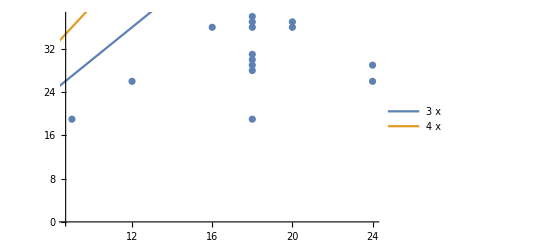

```mathematica
Show[ListPlot[TadRankDataShort],Plot[{3x, 4 x},{x,0,90}, PlotLegends->"Expressions"]]
```

```mathematica
TadRankDataShort
```

{{9,19},{12,26},{24,29},{18,30},{18,29},{16,36},{20,36},{18,37},{18,38},{20,37},{24,26},{18,36},{18,19},{18,31},{18,28}}

```mathematica
Max[TadRankDataShort[[;;,2]]]
```

38

### Level 3

```mathematica
TadRankDataShort3 = {};
```

```mathematica
LaunchKernels[20];
Module[{inds =Subsets[Range[180], {3}]},
myFunction[x_]:=Module[{coeffs ={{1,1,1},{1,1,-1},{1,-1,1}, {-1,1,1}}, sols, data},
sols = Dot[Basisshort[[inds[[x]]]], #]& /@ coeffs;
data = Select[{TAD[#],MatrixRank[N[MM[#]]]}&/@sols,#[[1]]<=70&];
TadRankDataShort3= Union[TadRankDataShort3, data]];
results=ParallelTable[myFunction[ii],{ii,1,Length@inds}];
]//AbsoluteTiming
CloseKernels[];
```

{195039.,Null}

```mathematica
Export["P:/Loras/rank_v_Nflux_short3_1minus1.mx", TadRankDataShort3];
```

```mathematica
TadRankDataShort3=DeleteDuplicates[Partition[Flatten[results],2]];
```

```mathematica
Length@TadRankDataShort3
Max[TadRankDataShort3[[;;,2]]]
```

113

55

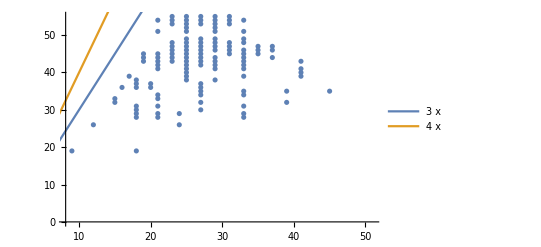

```mathematica
Show[ListPlot[Union[TadRankDataShort,TadRankDataShort3]],Plot[{3x, 4 x},{x,0,90}, PlotLegends->"Expressions"]]
```

```mathematica
Length@Union[TadRankDataShort,TadRankDataShort3]
```

128

```mathematica
poolN={{12,26},{16,36},{18,32},{20,44},{20,48},{22,50},{24,44},{24,45},{24,50},{24,56},{24,57},{24,58},{24,60},{24,62},{24,64},{26,58},{26,60},{28,50},{28,56},{28,57},{28,58},{28,59},{28,60},{28,62},{28,64},{28,65},{28,66},{28,68},{28,70},{28,71},{28,73},{28,74},{28,76},{28,77},{28,81},{30,58},{30,60},{30,68},{30,70},{30,71},{32,36},{32,42},{32,47},{32,50},{32,54},{32,55},{32,56},{32,57},{32,58},{32,59},{32,60},{32,61},{32,62},{32,64},{32,70},{32,71},{32,72},{32,73},{32,79},{32,82},{34,56},{34,58},{34,59},{34,60},{34,62},{34,66},{34,70},{34,71},{34,74},{34,76},{34,78},{34,80},{34,82},{36,50},{36,57},{36,58},{36,60},{36,61},{36,62},{36,71},{36,72},{36,73},{36,74},{36,76},{36,77},{36,78},{36,79},{36,80},{36,82},{36,89},{36,90},{37,80},{38,60},{38,62},{38,72},{38,74},{38,75},{38,76},{38,77},{38,82},{38,85},{40,48},{40,50},{40,54},{40,56},{40,57},{40,58},{40,59},{40,60},{40,61},{40,62},{40,64},{40,67},{40,68},{40,70},{40,71},{40,72},{40,73},{40,74},{40,75},{40,77},{40,78},{40,79},{40,80},{40,81},{40,82},{40,83},{40,84},{40,85},{40,86},{40,87},{40,88},{40,89},{40,90},{40,91}};
```

```mathematica
poolA=Union[Import["P:/Loras/data_Anindya/rank_v_Nflux_long3_1minus1.mx"],Import["P:/Loras/data_Anindya/rank_v_Nflux_long3_2s1s.mx"],Import["P:/Loras/data_Anindya/rank_v_Nflux_short2_1minus1.mx"],Import["P:/Loras/data_Anindya/rank_v_Nflux_short3_1minus1_inc.mx"],Import["P:/Loras/data_Anindya/rank_v_Nflux_short3NonBasis_1minus1_inc.mx"]];
poolQ=Union[TadRankDataShort,TadRankDataShort3];
```

```mathematica
pool4=Import["P:/Loras/data_Anindya/rank_v_Nflux_upto_4Oms.mx"];
```

```mathematica
fig1=ListPlot[{poolN,poolA,poolQ,pool4}, PlotLegends->{"poolN", "poolA","poolQ","pool4"},PlotStyle->{{Orange},{Green},{Blue},{Purple}},AxesLabel->{"N_flux","rank(∂_I ∂_J W)"}];
```

```mathematica
fig2=Plot[{3x, 4 x},{x,0,90}, PlotLegends->"Expressions"];
```

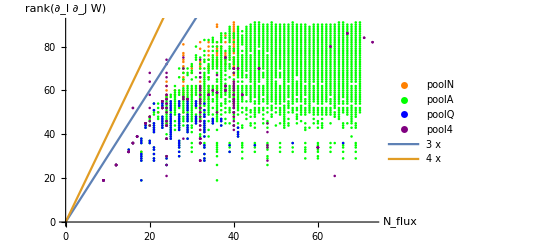

```mathematica
Show[fig1,fig2]
```

```mathematica
LaunchKernels[20];
```

```mathematica
coeffs ={{1,1,1,1},{1,1,1,-1},{1,1,-1,1}, {1,-1,1,1},{1,1,1,1},{1,1,-1,-1},{1,-1,-1,1}, {1,-1,1,-1}};
```

```mathematica
SolsLevel4=ConstantArray[{},20];
```

```mathematica
TadRankDataShort4=ConstantArray[{},20];
```

```mathematica
SetSharedVariable[SolsLevel4,TadRankDataShort4];
DistributeDefinitions[Basisshort,coeffs,inds,HH,H21,TAD,MM,ClClb,f,fprod,ktoI,W2OneOm,W2,MMOneOm,MM,conj,re,im];
```